## xAct`xTensor`

### Author

© 2002-2018, under the GNU General Public License (GPL)
     José M. Martín-García
	jose@xact.es
	http://www.xAct.es
		http://groups.google.com/group/xAct/

Helped by:
	Alfonso García-Parrado : design of vector bundles, complex structure, products and mappings.
	Guillaume Faye : design of n+m decompositions.

### Intro

xTensor` extends Mathematica capabilities in abstract tensor calculus, focusing on General Relativity. It works with tensor fields with arbitrary symmetries under permutations of indices, defined on one or more vector bundles and manifolds. It computes covariant derivatives with respect to multiple connections, including gauge connections in complex vector bundles. xTensor` can work with Lie derivatives, parametric derivatives and variational derivatives. It allows the presence of a metric in each manifold and defines all the associated torsion and curvature tensors (Riemann, Ricci, Einstein, Weyl, etc.), handling automatically their definitions and relations in terms of Christoffel objects. It can work with mappings between any two manifolds and push/pull tensor fields along those maps.
xTensor` does not perform component calculations. See the twin package xCoba`.
xTensor` needs the twin package xPerm` in order to compute the canonical form of a list of indices under certain symmetry group.
xTensor` has been designed with the following priorities in mind:
	1.- Mathematical structure
	2.- Efficiency
	3.- Compliance with Mathematica style
	4.- Simplicity of input/output
In particular, concerning the mathematical structure, xTensor` imitates the usual cycle in mathematics ``let X be a (Type) with properties props; then use it to do some computations.b4.b4 with the general form of declaration
	DefType[X, props]
	computations

### Load the package

This loads the package from the default directory, for example $HOME/.Mathematica/Applications/xAct/ for a single-user installation under Linux (see the installation notes for other possibilities),

```mathematica
<<xAct`xTensor`
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external mac executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.1.4, {2020,2,16}

CopyRight (C) 2002-2020, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

## 0. Basics

### 0.1. Example session

This is a very simple example of the use of xTensor`. We start by defining a manifold and some tensor fields on its tangent bundle.

Define a 3d manifold M3:

```mathematica
DefManifold[M3,3,{a,b,c,d,e}]
```

** DefManifold: Defining manifold M3.

** DefVBundle: Defining vbundle TangentM3.

Define a contravariant vector v and a covariant antisymmetric tensor F:

```mathematica
DefTensor[v[a],M3]
DefTensor[F[-a,-b],M3,Antisymmetric[{-a,-b}]]
```

** DefTensor: Defining tensor v[a].

** DefTensor: Defining tensor F[-a,-b].

Tensor product of both tensors, based on the abstract index notation:

```mathematica
F[-a,-b]v[b]
```

F |   |  
a | b v | b

```mathematica
% v[a]
```

F |   |  
a | b v | a
  v | b

There is no automatic simplification. It must be explicitly asked for:

```mathematica
Simplification[%]
```

0

Example of dummy handling:

```mathematica
F[-a,-d]v[d]v[b]v[-b]+3v[b]v[c]v[-c]F[-b,d]F[-d,-a]
```

3 F |   | d
b |   F |   |  
d | a v | b
  v |  
c v | c
 +F |   |  
a | d v |  
b v | b
  v | d

```mathematica
%//Simplification
```

(F |   |  
a | c-3 F |   |  
a | d F |   | d
c |  ) v |  
b v | b
  v | c

There is not a metric and hence v cannot be covariant. Note the position of the head ERROR:

```mathematica
Validate[%]
```

Validate::error: Invalid character of index in tensor F

Validate::error: Invalid character of index in tensor v

ERROR[v |  
b] (F |   |  
a | c-3 ERROR[F |   | d
c |  ] F |   |  
a | d) v | b
  v | c

Internal structure:

```mathematica
InputForm[%%]
```

(F[-a, -c] - 3*F[-a, -d]*F[-c, d])*v[-b]*v[b]*v[c]

Now we define a covariant derivative operator and check the first Bianchi identity (valid for any symmetric connection). Note that xTensor` uses unique (dollar-) variables as internal dummy indices to avoid index collisions. The function ScreenDollarIndices hides those indices replacing them by "normal" indices.

Covariant derivatives are defined by default with curvature but without torsion. Note also the default associated symbols: semicolon in Postfix notation and nabla in Prefix notation:

```mathematica
Options[DefCovD]
```

{SymbolOfCovD→{;,▽},Torsion→False,Curvature→True,FromMetric→Null,CurvatureRelations→True,ExtendedFrom→Null,OtherDependencies→{},OrthogonalTo→{},ProjectedWith→{},WeightedWithBasis→Null,ProtectNewSymbol:>$ProtectNewSymbols,Master→Null,DefInfo→{covariant derivative,}}

```mathematica
DefCovD[Cd[-a]]
```

** DefCovD: Defining covariant derivative Cd[-a].

** DefTensor: Defining vanishing torsion tensor TorsionCd[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelCd[a,-b,-c].

** DefTensor: Defining Riemann tensor RiemannCd[-a,-b,-c,d]. Antisymmetric only in the first pair.

** DefTensor: Defining non-symmetric Ricci tensor RicciCd[-a,-b].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

The Leibnitz rule is automatic:

```mathematica
Cd[-a][ F[-b,-c]v[c] ]
```

v | c
  (▽_a F |   |  
b | c)+F |   |  
b | c (▽_a v | c
 )

```mathematica
% v[b]//Simplification
```

F |   |  
b | c v | b
  (▽_a v | c
 )

The tensors have been defined with their expected symmetries:

```mathematica
RiemannCd[-a,-b,-c,d]+RiemannCd[-b,-a,-c,d]//Simplification
```

0

but it is possible to deduce them from more basic principles:

```mathematica
RiemannCd[-a,-b,-c,d]+RiemannCd[-b,-a,-c,d]//RiemannToChristoffel//Simplification
```

0

```mathematica
RiemannCd[-a,-b,-c,d]+RiemannCd[-b,-c,-a,d]+RiemannCd[-c,-a,-b,d]//RiemannToChristoffel//Simplification
```

0

Check of the second Bianchi identity:

```mathematica
Antisymmetrize[Cd[-e][RiemannCd[-c,-d,-b,a]],{-c,-d,-e}]
```

1/6 (▽_c R[▽] |   |   |   | a
d | e | b |  -▽_c R[▽] |   |   |   | a
e | d | b |  -▽_d R[▽] |   |   |   | a
c | e | b |  +▽_d R[▽] |   |   |   | a
e | c | b |  +▽_e R[▽] |   |   |   | a
c | d | b |  -▽_e R[▽] |   |   |   | a
d | c | b |  )

```mathematica
3%//Simplification
```

▽_c R[▽] |   |   |   | a
d | e | b |  -▽_d R[▽] |   |   |   | a
c | e | b |  +▽_e R[▽] |   |   |   | a
c | d | b |

```mathematica
%//CovDToChristoffel
```

Γ[▽] | a |   |  
  | e | e$2842 R[▽] |   |   |   | e$2842
c | d | b |  -Γ[▽] | e$2843 |   |  
  | e | b R[▽] |   |   |   | a
c | d | e$2843 |  -Γ[▽] | a |   |  
  | d | e$2833 R[▽] |   |   |   | e$2833
c | e | b |  +Γ[▽] | e$2834 |   |  
  | d | b R[▽] |   |   |   | a
c | e | e$2834 |  +Γ[▽] | e$2836 |   |  
  | d | e R[▽] |   |   |   | a
c | e$2836 | b |  -Γ[▽] | e$2845 |   |  
  | e | d R[▽] |   |   |   | a
c | e$2845 | b |  +Γ[▽] | a |   |  
  | c | e$2824 R[▽] |   |   |   | e$2824
d | e | b |  -Γ[▽] | e$2825 |   |  
  | c | b R[▽] |   |   |   | a
d | e | e$2825 |  -Γ[▽] | e$2827 |   |  
  | c | e R[▽] |   |   |   | a
d | e$2827 | b |  -Γ[▽] | e$2826 |   |  
  | c | d R[▽] |   |   |   | a
e$2826 | e | b |  +Γ[▽] | e$2835 |   |  
  | d | c R[▽] |   |   |   | a
e$2835 | e | b |  -Γ[▽] | e$2844 |   |  
  | e | c R[▽] |   |   |   | a
e$2844 | d | b |  +∂_c R[▽] |   |   |   | a
d | e | b |  -∂_d R[▽] |   |   |   | a
c | e | b |  +∂_e R[▽] |   |   |   | a
c | d | b |

```mathematica
%//RiemannToChristoffel//ScreenDollarIndices
```

-Γ[▽] | e1 |   |  
  | e | b ∂_c Γ[▽] | a |   |  
  | d | e1+Γ[▽] | e1 |   |  
  | d | b ∂_c Γ[▽] | a |   |  
  | e | e1+Γ[▽] | a |   |  
  | e | e1 ∂_c Γ[▽] | e1 |   |  
  | d | b-Γ[▽] | a |   |  
  | d | e1 ∂_c Γ[▽] | e1 |   |  
  | e | b-∂_c ∂_d Γ[▽] | a |   |  
  | e | b+∂_c ∂_e Γ[▽] | a |   |  
  | d | b+Γ[▽] | e1 |   |  
  | e | b ∂_d Γ[▽] | a |   |  
  | c | e1-Γ[▽] | e1 |   |  
  | e | b (Γ[▽] | a |   |  
  | d | e2 Γ[▽] | e2 |   |  
  | c | e1-Γ[▽] | a |   |  
  | c | e2 Γ[▽] | e2 |   |  
  | d | e1-∂_c Γ[▽] | a |   |  
  | d | e1+∂_d Γ[▽] | a |   |  
  | c | e1)-Γ[▽] | e1 |   |  
  | c | b ∂_d Γ[▽] | a |   |  
  | e | e1-Γ[▽] | a |   |  
  | e | e1 ∂_d Γ[▽] | e1 |   |  
  | c | b+Γ[▽] | a |   |  
  | e | e1 (Γ[▽] | e1 |   |  
  | d | e2 Γ[▽] | e2 |   |  
  | c | b-Γ[▽] | e1 |   |  
  | c | e2 Γ[▽] | e2 |   |  
  | d | b-∂_c Γ[▽] | e1 |   |  
  | d | b+∂_d Γ[▽] | e1 |   |  
  | c | b)+Γ[▽] | a |   |  
  | c | e1 ∂_d Γ[▽] | e1 |   |  
  | e | b+∂_d ∂_c Γ[▽] | a |   |  
  | e | b-∂_d ∂_e Γ[▽] | a |   |  
  | c | b-Γ[▽] | e1 |   |  
  | d | b ∂_e Γ[▽] | a |   |  
  | c | e1+Γ[▽] | e1 |   |  
  | d | b (Γ[▽] | a |   |  
  | e | e2 Γ[▽] | e2 |   |  
  | c | e1-Γ[▽] | a |   |  
  | c | e2 Γ[▽] | e2 |   |  
  | e | e1-∂_c Γ[▽] | a |   |  
  | e | e1+∂_e Γ[▽] | a |   |  
  | c | e1)+Γ[▽] | e1 |   |  
  | c | b ∂_e Γ[▽] | a |   |  
  | d | e1-Γ[▽] | e1 |   |  
  | c | b (Γ[▽] | a |   |  
  | e | e2 Γ[▽] | e2 |   |  
  | d | e1-Γ[▽] | a |   |  
  | d | e2 Γ[▽] | e2 |   |  
  | e | e1-∂_d Γ[▽] | a |   |  
  | e | e1+∂_e Γ[▽] | a |   |  
  | d | e1)+Γ[▽] | a |   |  
  | d | e1 ∂_e Γ[▽] | e1 |   |  
  | c | b-Γ[▽] | a |   |  
  | d | e1 (Γ[▽] | e1 |   |  
  | e | e2 Γ[▽] | e2 |   |  
  | c | b-Γ[▽] | e1 |   |  
  | c | e2 Γ[▽] | e2 |   |  
  | e | b-∂_c Γ[▽] | e1 |   |  
  | e | b+∂_e Γ[▽] | e1 |   |  
  | c | b)-Γ[▽] | a |   |  
  | c | e1 ∂_e Γ[▽] | e1 |   |  
  | d | b+Γ[▽] | a |   |  
  | c | e1 (Γ[▽] | e1 |   |  
  | e | e2 Γ[▽] | e2 |   |  
  | d | b-Γ[▽] | e1 |   |  
  | d | e2 Γ[▽] | e2 |   |  
  | e | b-∂_d Γ[▽] | e1 |   |  
  | e | b+∂_e Γ[▽] | e1 |   |  
  | d | b)-∂_e ∂_c Γ[▽] | a |   |  
  | d | b+∂_e ∂_d Γ[▽] | a |   |  
  | c | b+Γ[▽] | e1 |   |  
  | d | e (Γ[▽] | a |   |  
  | e1 | e2 Γ[▽] | e2 |   |  
  | c | b-Γ[▽] | a |   |  
  | c | e2 Γ[▽] | e2 |   |  
  | e1 | b-∂_c Γ[▽] | a |   |  
  | e1 | b+∂_e1 Γ[▽] | a |   |  
  | c | b)-Γ[▽] | e1 |   |  
  | e | d (Γ[▽] | a |   |  
  | e1 | e2 Γ[▽] | e2 |   |  
  | c | b-Γ[▽] | a |   |  
  | c | e2 Γ[▽] | e2 |   |  
  | e1 | b-∂_c Γ[▽] | a |   |  
  | e1 | b+∂_e1 Γ[▽] | a |   |  
  | c | b)-Γ[▽] | e1 |   |  
  | e | c (-Γ[▽] | a |   |  
  | e1 | e2 Γ[▽] | e2 |   |  
  | d | b+Γ[▽] | a |   |  
  | d | e2 Γ[▽] | e2 |   |  
  | e1 | b+∂_d Γ[▽] | a |   |  
  | e1 | b-∂_e1 Γ[▽] | a |   |  
  | d | b)-Γ[▽] | e1 |   |  
  | c | e (Γ[▽] | a |   |  
  | e1 | e2 Γ[▽] | e2 |   |  
  | d | b-Γ[▽] | a |   |  
  | d | e2 Γ[▽] | e2 |   |  
  | e1 | b-∂_d Γ[▽] | a |   |  
  | e1 | b+∂_e1 Γ[▽] | a |   |  
  | d | b)-Γ[▽] | e1 |   |  
  | c | d (-Γ[▽] | a |   |  
  | e1 | e2 Γ[▽] | e2 |   |  
  | e | b+Γ[▽] | a |   |  
  | e | e2 Γ[▽] | e2 |   |  
  | e1 | b+∂_e Γ[▽] | a |   |  
  | e1 | b-∂_e1 Γ[▽] | a |   |  
  | e | b)+Γ[▽] | e1 |   |  
  | d | c (-Γ[▽] | a |   |  
  | e1 | e2 Γ[▽] | e2 |   |  
  | e | b+Γ[▽] | a |   |  
  | e | e2 Γ[▽] | e2 |   |  
  | e1 | b+∂_e Γ[▽] | a |   |  
  | e1 | b-∂_e1 Γ[▽] | a |   |  
  | e | b)

```mathematica
Simplification[%]//AbsoluteTiming
```

{0.174235,0}

Commutation of covariant derivatives. It is possible to choose the indices (use CommuteCovDs) or just let xTensor` to bring the derivative indices into canonical order (use 
SortCovDs):

```mathematica
Cd[-a]@Cd[-b]@v[c]
```

▽_a▽_b v | c

```mathematica
CommuteCovDs[%,Cd,{-b,-a}]//ScreenDollarIndices
```

R[▽] |   |   |   | c
b | a | d |   v | d
 +▽_b▽_a v | c

```mathematica
SortCovDs[%%]//ScreenDollarIndices
```

R[▽] |   |   |   | c
b | a | d |   v | d
 +▽_b▽_a v | c

Now we introduce a metric on the manifold. Its associated curvature tensors are defined: RiemannCD, RiciCD, EinsteinCD, etc:

Define the metric g, with negative determinant. Its Levi-Civita connection will be called CD:

```mathematica
DefMetric[-1,g[-a,-b],CD,SymbolOfCovD->{"|","D"}]
```

** DefTensor: Defining symmetric metric tensor g[-a,-b].

** DefTensor: Defining antisymmetric tensor epsilong[-a,-b,-c].

** DefCovD: Defining covariant derivative CD[-a].

** DefTensor: Defining vanishing torsion tensor TorsionCD[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelCD[a,-b,-c].

** DefTensor: Defining Riemann tensor RiemannCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric Ricci tensor RicciCD[-a,-b].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarCD[].

** DefCovD:  Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor EinsteinCD[-a,-b].

** DefTensor: Defining vanishing Weyl tensor WeylCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric TFRicci tensor TFRicciCD[-a,-b].

** DefTensor: Defining Kretschmann scalar KretschmannCD[].

** DefCovD:  Computing RiemannToWeylRules for dim 3

** DefCovD:  Computing RicciToTFRicci for dim 3

** DefCovD:  Computing RicciToEinsteinRules for dim 3

** DefTensor: Defining weight +2 density Detg[]. Determinant.

Standard properties of the metric and its associated objects:

```mathematica
CD[-a][ g[-b,-c] ]
```

0

```mathematica
CD[-a][ EinsteinCD[a,b] ]
```

0

```mathematica
g[a,-a]
```

3

```mathematica
g[a,b]g[-b,-c]
```

δ |   | a
c |

Let us check the antisymmetry of the second pair of indices in the Riemann tensor:

```mathematica
RiemannCD[-a,-b,-c,-d]+RiemannCD[-a,-b,-d,-c]
```

R[D] |   |   |   |  
a | b | c | d+R[D] |   |   |   |  
a | b | d | c

Because canonicalization is not automatic, the previous expression is not automatically zero. We expand it in derivatives of Christoffels and canonicalize. The partial derivative does not commute with the metric, so that internally the code replaces temporarily those derivatives with Levi-Civita connections:

```mathematica
%//RiemannToChristoffel//Simplification//ScreenDollarIndices
```

ToCanonical::cmods: Detected metric-incompatible derivatives {PD}.

General::stop: Further output of ToCanonical::cmods will be suppressed during this calculation.

Γ[D] |   |   | e
d | b |   Γ[D] |   |   |  
e | a | c+Γ[D] |   |   | e
c | b |   Γ[D] |   |   |  
e | a | d-Γ[D] |   |   | e
d | a |   Γ[D] |   |   |  
e | b | c-Γ[D] |   |   | e
c | a |   Γ[D] |   |   |  
e | b | d+Γ[D] | e |   |  
  | b | d Γ[D] | e1 |   |  
  | a | e g |   |  
c | e1-Γ[D] | e |   |  
  | a | d Γ[D] | e1 |   |  
  | b | e g |   |  
c | e1+Γ[D] | e |   |  
  | b | c Γ[D] | e1 |   |  
  | a | e g |   |  
d | e1-Γ[D] | e |   |  
  | a | c Γ[D] | e1 |   |  
  | b | e g |   |  
d | e1-∂_a Γ[D] |   |   |  
c | b | d-∂_a Γ[D] |   |   |  
d | b | c+∂_b Γ[D] |   |   |  
c | a | d+∂_b Γ[D] |   |   |  
d | a | c

Metric contraction is not automatic either. The resulting expression is not obviously zero:

```mathematica
%//ContractMetric//Simplification
```

-∂_a Γ[D] |   |   |  
c | b | d-∂_a Γ[D] |   |   |  
d | b | c+∂_b Γ[D] |   |   |  
c | a | d+∂_b Γ[D] |   |   |  
d | a | c

Actually it is only zero for connections deriving from a metric:

```mathematica
%//ChristoffelToGradMetric//Expand
```

-1/2 ∂_a ∂_b g |   |  
c | d-1/2 ∂_a ∂_b g |   |  
d | c+1/2 ∂_b ∂_a g |   |  
c | d+1/2 ∂_b ∂_a g |   |  
d | c

```mathematica
%//Simplification
```

0

In this case a simple reordering of the partial derivatives (this is not automatic) would have been enough:

```mathematica
%%//SortCovDs
```

0

Examples of Lie derivative and bracket:

```mathematica
LieD[3v[a]][F[-a,-b]v[b]]
```

3 v | b
  (ℒ_v F |   |  
a | b)

```mathematica
Bracket[v[a],F[a,-b]v[b]][a]
```

[v | a
 ,F | a |  
  | b v | b
 ] | a

Undefine all objects on the manifold and the manifold itself:

```mathematica
UndefMetric[g]
```

** UndefTensor: Undefined weight +2 density Detg

** UndefTensor: Undefined symmetric Christoffel tensor ChristoffelCD

** UndefTensor: Undefined symmetric Einstein tensor EinsteinCD

** UndefTensor: Undefined Kretschmann scalar KretschmannCD

** UndefTensor: Undefined symmetric Ricci tensor RicciCD

** UndefTensor: Undefined Ricci scalar RicciScalarCD

** UndefTensor: Undefined Riemann tensor RiemannCD

** UndefTensor: Undefined symmetric TFRicci tensor TFRicciCD

** UndefTensor: Undefined torsion tensor TorsionCD

** UndefTensor: Undefined Weyl tensor WeylCD

** UndefCovD: Undefined covariant derivative CD

** UndefTensor: Undefined antisymmetric tensor epsilong

** UndefTensor: Undefined symmetric metric tensor g

```mathematica
UndefTensor/@{v,F};
UndefCovD[Cd]
```

** UndefTensor: Undefined tensor v

** UndefTensor: Undefined tensor F

** UndefTensor: Undefined symmetric Christoffel tensor ChristoffelCd

** UndefTensor: Undefined non-symmetric Ricci tensor RicciCd

** UndefTensor: Undefined Riemann tensor RiemannCd

** UndefTensor: Undefined torsion tensor TorsionCd

** UndefCovD: Undefined covariant derivative Cd

```mathematica
UndefManifold[M3]
```

** UndefVBundle: Undefined vbundle 𝕋M3

** UndefManifold: Undefined manifold M3

There are no symbols left in the Global` context

```mathematica
?Global`*
```

Global`$UseTextSearchQ

### 0.2. Summary

These are the objects that currently can be defined in xTensor`.
	- Manifolds
	- Mappings
	- Vector bundles
	- Indices (of different types)
	- Tensors (in particular, Metrics)
	- Covariant derivative operators (including partial derivatives)
	- Constant symbols
	- Parameters
	- Inert heads (wrappers for tensors)
	- Scalar functions
	- Charts (coordinate systems): use the twin package xCoba` (in collaboration with D. Yllanes)
	- Bases (frames): use the twin package xCoba`
We also have predefined mathematical operators:
	- Lie derivative
	- Lie bracket
	- Parametric derivative
	- Variational derivative
and useful mathematical operations:
	- Relations and rules among indexed objects
	- Indexed equations solving
	- Canonicalization and simplification of expressions
	- Automatic definition of curvature tensors, and relations among them
	- Complex conjugation
There are also specialized algorithms, frequently used in General Relativity:
	- Warped metric decomposition
	- ADM-like decomposition
	- Perturbation theory in General Relativity: use the twin package xPert` (in collaboration with D. Brizuela and G. Mena Marugán)
	- Spherical tensor harmonics: use the twin package Harmonics` (in collaboration with D. Brizuela and G. Mena Marugán)
	- Manipulation of invariants of the Riemann tensor: use the twin package Invar` (in collaboration with R. Portugal, L. Manssur and D. Yllanes)
	- Spinor calculus (in collaboration with A. García-Parrado)

### 0.3. Getting info

Every piece of information in Mathematica is associated to a symbol and can be obtained using the ? and ?? symbols (see the command Information in the Mathematica help). xTensor` strictly follows that rule. (In particular, we have explicitly avoided notations based on string input/output which would require a parser, much restricting the capabilities of the user.)

```mathematica
?DefManifold
```

DefManifold[M, dim, {a, b, c,...}] defines M to be an n-dimensional differentiable manifold with dimension dim (a positive integer or a constant symbol) and tensor abstract indices a, b, c, ... .  DefManifold[M, {M1, ..., Mm}, {a, b, c,...}] defines M to be the product manifold of previously defined manifolds M1 ... Mm. For backward compatibility dim can be a list of positive integers, whose length is interpreted as the dimension of the defined manifold.

```mathematica
??ERROR
```

ERROR[expr] is an expression where an error has been detected. ERROR is an inert head with a single argument.

Attributes[ERROR]={HoldFirst,Protected}
 
DefInfo[ERROR]^={inert head,Generic head to wrap expressions with errors.}
 
InertHeadQ[ERROR]^=True
 
LinearQ[ERROR]^=False
 
PrintAs[ERROR]^=ERROR

### 0.4. Too many brackets!

This is a common complaint from most users after their first contact with xTensor`. My answer to that is the following:

1. That is how Mathematica internally works. For example, did you expect this simple derivative having internally six pairs of brackets, when it has just one in the "user-notation"?

```mathematica
f'[2x-y]//FullForm
```

Derivative[1][f][Plus[Times[2,x],Times[-1,y]]]

2. xTensor` does not have different internal and external notations (at least not now). This helps understanding what is happening internally and allows the user to build pattern rules which always work. However, you are continually exposed to the internal notation.

3. The highest accummulation of brackets happens in derivatives. This simply follows the general idea in Mathematica (made clear in the example above) of treating a derivative as an operator on an expression, and not as a simple additional argument of the expression, as the traditional "comma-index" notation might suggest.

4. The Mathematica language is very similar to LISP, in which you have a lot of parenthesis.

5. If you are still not convinced by the previous three arguments, then I must say that it is possible to construct whatever other notation you like for a derivative, or for any other operator, and several examples of this are given in section 6.1 below.

```mathematica
Remove[f,x,y]
```

### 0.5. Warnings

xTensor` is a very powerful tool in the hands of an average Mathematica user, but could be difficult for an unexperienced Mathematica user. This is because I have not tried to hide Mathematica subtleties (like delayed assignments, unique symbols or upvalues), but rather I have tried to make as much use as possible of such powerful instruments. If you don't understand those three listed concepts, please spend some (not really much) time with a Mathematica tutorial. It will pay off, even if you finally don't use xTensor`.

If you think you can do your tensor computation by hand in a few lines, then xTensor` is probably too much. This system is designed to be efficient when developing big projects, not small computations: a general-purpose tensor computer algebra system always has hundreds of commands, and only big projects give you enough motivation to learn them.

xTensor` is a manipulator of abstract expressions. It does not compute (at least easily) the components of the Riemann tensor associated with a given matrix of metric components, and things like that. xTensor` is specialized in the manipulation of identities obeyed by families of objects with some properties (like being antisymmetric). Many users feel dissapointed at the beginning because they were expecting component-type computations. Use the twin package xCoba` for that.

## 1. Manifolds, vector bundles and parameters

### 1.1. Define a manifold and its tangent bundle

Just after loading,  xTensor` does not have any manifold defined. Here we see how to declare our own abstract manifolds, on which tensor fields will be defined.

DefManifold				Define a manifold or a product of manifolds
UndefManifold			Undefine a manifold
ManifoldQ				Check manifold
$Manifolds				List of defined manifolds
$ProductManifolds		List of defined product manifolds

Definition of a manifold.

We define a 3-dimensional manifold M3 with abstract indices {a, b, ..., h} associated to its tangent vector bundle:

```mathematica
DefManifold[M3,3,{a,b,c,d,e,f,g,h}]
```

** DefManifold: Defining manifold M3.

** DefVBundle: Defining vbundle TangentM3.

```mathematica
DimOfManifold[M3]
```

3

We can ask Mathematica about this manifold using the question mark ? (command Information). We see that the data is stored in several property-functions using the concept of "upvalue" (this is why we find the  ^= sign below)

```mathematica
?M3
```

Global`M3

DefInfo[M3]^={manifold,}
 
DimOfManifold[M3]^=3
 
ManifoldQ[M3]^=True
 
PrintAs[M3]^=M3
 
ServantsOf[M3]^={𝕋M3}
 
SplittingsOfManifold[M3]^={}

Together with the manifold we have also defined its tangent vector bundle, which stores all the information related to indices and indexed objects. By default, the tangent bundle is named by joining the symbol Tangent with the name of the manifold, but that name can be freely choosen. To conform with the standard notation, it is typeset by default as the character 𝕋 followed by the typesetting of the manifold, but the typsetting can also be freely chosen. Note that we shall often abbreviate "vector bundle" to "vbundle".

Tangent[M]		Tangent bundle of the manifold M

Tangent bundle of a manifold.

By default, tangent bundles are real and have no metric. The dimension of the tangent bundle is defined as that of the vector space at each point, and coincides with the dimension of the base manifold.

```mathematica
Tangent[M3]
```

𝕋M3

```mathematica
%//InputForm
```

TangentM3

```mathematica
?TangentM3
```

𝕋M3

BaseOfVBundle[𝕋M3]^=M3
 
Dagger[𝕋M3]^=𝕋M3
 
DefInfo[𝕋M3]^={vbundle,}
 
DimOfVBundle[𝕋M3]^=3
 
IndicesOfVBundle[𝕋M3]^={{a,b,c,d,e,f,g,h},{}}
 
LastIndex[𝕋M3]^={h,1}
 
MasterOf[𝕋M3]^=M3
 
MetricsOfVBundle[𝕋M3]^={}
 
PrintAs[𝕋M3]^=𝕋M3
 
SplittingsOfVBundle[𝕋M3]^={}
 
VBundleQ[𝕋M3]^=True

We define a second manifold S2. Note that we can use C, D, K, N, O as indices, even though Mathematica has reserved meanings for those symbols. The capitals E and I cannot be used as indices because they are always understood as the base of natural logarithms and the square root of -1, respectively. xTensor` issues warnings to remind you of this point:

```mathematica
DefManifold[S2, 2, {A,B,C,D,F,G,H}]
```

** DefManifold: Defining manifold S2.

** DefVBundle: Defining vbundle TangentS2.

ValidateSymbol::capital: System name C is overloaded as an abstract index.

ValidateSymbol::capital: System name D is overloaded as an abstract index.

The lists of manifolds and vbundles defined in the current session are given by the global variables $Manifolds and $VBundles, respectively:

```mathematica
$Manifolds
```

{M3,S2}

```mathematica
$VBundles
```

{𝕋M3,𝕋S2}

A manifold can be undefined (its properties are lost and the symbol is removed). In the process, the associated tangent bundle is also undefined:

```mathematica
UndefManifold[M3]
```

** UndefVBundle: Undefined vbundle 𝕋M3

** UndefManifold: Undefined manifold M3

```mathematica
?M3
```

Information::notfound: Symbol M3 not found.

```mathematica
$Manifolds
```

{S2}

And redefined (note the use of the command IndexRange, quite handy for long lists of indices):

```mathematica
DefManifold[M3, 3, IndexRange[a,h]]
```

** DefManifold: Defining manifold M3.

** DefVBundle: Defining vbundle TangentM3.

```mathematica
$Manifolds
```

{S2,M3}

It is possible to define 1-dimensional manifolds, with a corresponding 1-dimensional tangent vbundle. They are treated in exactly the same way as other manifolds and vbundles. Other systems, like Ricci`, only allow a single abstract index (which can be repeated), but that is a large internal exception, and xTensor`does not follow that idea. Instead, we shall declare all indices of the same 1-dimensional space to be symmetric. See subsection 4.4 below.

The dimension of a manifold does not have to be an integer necessarily. It can be any expression. It is advisable to use constant-symbols (see 6.5 below) as manifold dimensions.

### 1.2. Product manifolds. V1.1.0 UPDATE

Given two manifolds, it is always possible to define another manifold as the Cartesian product of those. The tangent bundle of the product will be then constructed as the (external, or disjoint) direct sum of the tangent bundles of the submanifolds. There are two ways to approach this problem, and we will find this duality repeatedly in all of xAct`. On the one hand we can declare a new symbolic manifold using a DefType command, which will prepare everything for us in advance. On the other hand we can describe the new manifold using a CartesianProduct command, whose properties will be computed in real time whenever they are needed.

We define a product manifold as

```mathematica
DefManifold[M5,{M3,S2}, {μ, ν, λ, σ, η, ρ}]
```

** DefManifold: Defining manifold M5.

** DefVBundle: Defining vbundle TangentM5.

```mathematica
?M5
```

Global`M5

DefInfo[M5]^={manifold,}
 
DimOfManifold[M5]^=5
 
ManifoldQ[M5]^=True
 
PrintAs[M5]^=M5
 
ServantsOf[M5]^={𝕋M5}
 
SplittingsOfManifold[M5]^={M3×S2}
 
M5/:SubmanifoldQ[M5,M3]=True
 
M5/:SubmanifoldQ[M5,S2]=True

whose tangent bundle is a direct sum of the corresponding subvbundles:

```mathematica
?TangentM5
```

𝕋M5

BaseOfVBundle[𝕋M5]^=M5
 
Dagger[𝕋M5]^=𝕋M5
 
DefInfo[𝕋M5]^={vbundle,}
 
DimOfVBundle[𝕋M5]^=5
 
IndicesOfVBundle[𝕋M5]^={{μ,ν,λ,σ,η,ρ},{}}
 
LastIndex[𝕋M5]^={ρ,1}
 
MasterOf[𝕋M5]^=M5
 
MetricsOfVBundle[𝕋M5]^={}
 
PrintAs[𝕋M5]^=𝕋M5
 
SplittingsOfVBundle[𝕋M5]^={𝕋M3⊕𝕋S2}
 
𝕋M5/:SubvbundleQ[𝕋M5,𝕋M3]=True
 
𝕋M5/:SubvbundleQ[𝕋M5,𝕋S2]=True
 
VBundleQ[𝕋M5]^=True

The list of product manifolds is given by another global variable:

```mathematica
$ProductManifolds
```

{M5}

The command SplitManifold also allows constructing a product manifold, or splitting a previously existing manifold.

```mathematica
?SplitManifold
```

SplitManifold[M, {m1, ..., mn}] identifies the manifold M as the (external) Cartesian product of the manifolds mi. Both the M manifold and the mi manifolds are assumed to exist already. The dimension of M must coincide with the sum of the dimensions of the mi manifolds.

We can also work directly with an expression representing the product manifold.

CartesianProduct[M1, M2, ...]		Cartesian product of the manifolds M1, M2, ...

Cartesian product of manifolds.

Cartesian product of our two manifolds :

```mathematica
prod=CartesianProduct[M3,S2]
```

M3×S2

```mathematica
ManifoldQ[prod]
```

True

```mathematica
DimOfManifold[prod]
```

5

```mathematica
Tangent[prod]
```

𝕋M3⊕𝕋S2

```mathematica
%//FullForm
```

CirclePlus[TangentM3,TangentS2]

Clean up:

```mathematica
UndefManifold[M5]
```

** UndefVBundle: Undefined vbundle 𝕋M5

** UndefManifold: Undefined manifold M5

```mathematica
Remove[prod]
```

### 1.3. Inner vector bundles

xTensor` allows the definition of vector bundles other than tangent bundles. These ``inner vbundles.b4.b4 can be real or complex, which forces the definition of the complex conjugated vbundle. Complex conjugation is controlled by the function Dagger.

DefVBundle				Define a vbundle or a sum of vbundles
UndefVBundle			Undefine a vbundle
VBundleQ				Check a vbundle
$VBundles				List of defined vbundles
$SumVBundles			List of defined sum vbundles

Definition of a vbundle.

Define a complex inner vbundle with dimension 4 (this is the fiber dimension) and base manifold M3:

```mathematica
DefVBundle[InnerC,M3,4,{𝔄,𝔅,ℭ,𝔇,𝔈,𝔉,𝔊,ℌ},Dagger->Complex]
```

** DefVBundle: Defining vbundle InnerC.

** DefVBundle: Defining conjugated vbundle InnerC†. Assuming fixed anti-isomorphism between InnerC and InnerC†

```mathematica
?InnerC
```

InnerC

BaseOfVBundle[InnerC]^=M3
 
Dagger[InnerC]^=InnerC†
 
DefInfo[InnerC]^={vbundle,}
 
DimOfVBundle[InnerC]^=4
 
HostsOf[InnerC]^={M3}
 
IndicesOfVBundle[InnerC]^={{𝔄,𝔅,ℭ,𝔇,𝔈,𝔉,𝔊,ℌ},{}}
 
LastIndex[InnerC]^={ℌ,1}
 
MetricsOfVBundle[InnerC]^={}
 
PrintAs[InnerC]^=InnerC
 
ServantsOf[InnerC]^={InnerC†}
 
SplittingsOfVBundle[InnerC]^={}
 
VBundleQ[InnerC]^=True

In the process of definition, the conjugated vbundle InnerC†, with corresponding conjugated indices, has been created. It is a servant of InnerC, and hence can only be undefined through undefinition of the latter. By default, all conjugated symbols are constructed by appending the dagger character †. (This character is stored in the goblal variable $DaggerCharacter, which can be changed.)

```mathematica
?InnerC†
```

InnerC†

BaseOfVBundle[InnerC†]^=M3
 
Dagger[InnerC†]^=InnerC
 
DefInfo[InnerC†]^={conjugated vbundle,Assuming fixed anti-isomorphism between InnerC and InnerC†}
 
DimOfVBundle[InnerC†]^=4
 
HostsOf[InnerC†]^={M3}
 
IndicesOfVBundle[InnerC†]^={{𝔄†,𝔅†,ℭ†,𝔇†,𝔈†,𝔉†,𝔊†,ℌ†},{}}
 
LastIndex[InnerC†]^={ℌ†,1}
 
MasterOf[InnerC†]^=InnerC
 
MetricsOfVBundle[InnerC†]^={}
 
PrintAs[InnerC†]^=InnerC†
 
SplittingsOfVBundle[InnerC†]^={}
 
VBundleQ[InnerC†]^=True

We have already defined four different vector bundles:

```mathematica
$VBundles
```

{𝕋S2,𝕋M3,InnerC,InnerC†}

There is also a function SplitVBundle, parallel to SplitManifold.

```mathematica
?SplitVBundle
```

SplitVBundle[V, {v1, ..., vn}] identifies the vbundle V as the direct sum of the vbundles vi. Both the V vbundle and the vi vbundles are assumed to exist already. The dimension of V must coincide with the sum of the dimensions of the vi vbundles.

### 1.4. Parameters

In xTensor` the indexed objects can be fields on manifolds and/or functions of real parameters (for example proper time).

DefParameter			Define a real parameter
UndefParameter			Undefine a parameter
ParameterQ				Check a real parameter
$Parameters				List of defined parameters

Definition of a parameter

We define a real parameter that will be used below to compute parametric derivatives (see ParamD in subsection 6.6).

```mathematica
DefParameter[time]
```

** DefParameter: Defining parameter time.

```mathematica
?time
```

time

DefInfo[time]^={parameter,}
 
ParameterQ[time]^=True
 
PrintAs[time]^=time

Manifolds and parameters are the only possible "dependencies" of the objects in xTensor`. We shall later explain this in more detail.

An important question is the relation between fields on 1d manifolds and functions of a parameter. In decompositions of ADM-type it would be nice to have a way of going from a 4d structure to a 3+1 structure and then from here to a 3d structure plus a time parameter. I still don't know how to program this idea. There are many things to change in a nontrivial way: tensor fields, covariant derivatives, metrics, etc. Please, let me know if you have suggestions.

### 1.5. Vector spaces: bundles over a point

It is possible to work  xTensor` with a single vector space, considered as a bundle over a manifold that happens to be a point.

Define a zero-dimensional manifold, a point. We do not need to specify indices because there is no tangent space:

```mathematica
DefManifold[P,0,{}]
```

** DefManifold: Defining manifold P.

** DefManifold:  Tangent bundle does not exist for a 0-dim manifold

Now we can define a vector bundle over this point. It has a single fiber, which is a vector space of the required dimension:

```mathematica
DefVBundle[V,P,4,{𝔞,𝔟,𝔠}]
```

** DefVBundle: Defining vbundle V.

And now we can define vectors and tensors on this space, with no dependencies:

```mathematica
DefTensor[X[𝔞],{}]
```

** DefTensor: Defining tensor X[𝔞].

Undefine all objects:

```mathematica
UndefTensor[X]
```

** UndefTensor: Undefined tensor X

```mathematica
UndefVBundle[V]
```

** UndefVBundle: Undefined vbundle V

```mathematica
UndefManifold[P]
```

** UndefManifold: Undefined manifold P

## 2. Indices

### 2.0. Important comments

1) Indices are the key objects in xTensor`, and the source of the generality of the system. They are carriers of contextual information, much like the decimal digits in numerical computations, or the letters in a text. An index by itself has little information (only an association to a vector space), but a group of indices together can encode a lot of information (rank, symmetries, metrics, bases, etc). In general, an index is anything which can be placed at an index-slot: that is, we shall later define four places in which we can put indices and anything which we can meaningfully put there will be called an index.

2) Starting version 0.9 of xTensor`, indices are associated to vbundles, and not to manifolds, as was the case in previous versions. This allows us to work with vbundles other than tangent bundles to manifolds.

3) We need a "language" to talk about indices, and though we usually understand what a dummy index or a covariant index is, such a language is not rigorously defined anywhere. I have invented my own language for this. Please, suggest changes if you find inconsistencies, gaps or bad choices.

4) Taken from the Internet:
	The plural of "index" for books, journals and newspapers is "indexes"; the plural of "index" for graphs and benchmarks for economics for example, is "indices"; but the plural of "appendix" is always "appendices".
I think the "index" of a tensor must follow the rule for the second group, and hence its plural will be "indices".

### 2.1. Properties of indices: type, character, state

1) There are five known types of index in xTensor` (other types could be added, but there is no user-defined way to do this):
	- Abstract index (AIndex). See subsection 2.2.
	- Basis index (BIndex), associated to some basis (coordinated or not) of vector fields. Described in xCoba`.
	- Component index (CIndex), also associated to some basis. Described in xCoba`.
	- Directional index (DIndex). See subsection 3.7.
	- Label index (LIndex). See subsection 3.8.
Collectively we refer to all five classes as "generalized indices" (GIndex). Additionally, we can have patterns (PIndex) for g-indices at those positions where g-indices are expected, but patterns are not considered as g-indices. In the following "indices" will mean "g-indices" unless we specify the type.

2) All indices have a "character", which can be either covariant (Down-index) or contravariant (Up-index).

3) Some indices can be used to represent contractions, following the Einstein convention: two repeated indices in the same tensor or tensor product, but each having a different character.  We call them "contractible" or "Einstein" indices (EIndex) and currently only abstract and basis indices are allowed to be contractible. (Note that having contractible indices with the same character is a syntactic error in xTensor`.) E-indices have a "state": they can be Free or contracted (aka Dummy). For completeness, the state of components, directions and labels is said to be always "Blocked", what in particular means that they can be repeated (i.e. truly repeated, not simply staggered).

4) Basis and component indices are known by part of the routines of xTensor` (for example the formatting routines, the index selectors, the canonicalizer or the constructors of rules), but used in the twin package xCoba`. From now on we shall not consider those two types of indices. See xCobaDoc.nb for further information.
5) There is a further property of an index, only used internally: its metric-state, saying whether an index can be raised or lowered using a given metric (not whether it has been or not actually raised already). This will be important in section 7.3.

### 2.2. Covariant and contravariant abstract indices

Abstract indices in xTensor` are valid atomic symbols without numeric value (excluding therefore E and I) and with no special output (excluding symbols like Space, Tab, etc.) One of the most important decisions when working with tensors is the notation for covariant and contravariant indices. Given the binary character of the problem there is only one natural simple choice: the use of signs + and - . We shall denote contravariant indices as +a or a, and covariant indices as -a. This choice is very simple, but not particularly convenient when doing pattern matching, due to the asymmetry of a being a symbol but -a being a composite expression.

AIndexQ					Validate an abstract index
VB`Q						Check that an abstract up-index belongs to vbundle VB
VB`pmQ					Check that an abstract (up- or down-) index belongs to vbundle VB

Validation of indices.

We can check whether a symbol has been registered as an abstract index using the function AIndexQ

```mathematica
AIndexQ[A]
```

True

```mathematica
AIndexQ[-b]
```

True

```mathematica
AIndexQ[q]
```

False

```mathematica
Remove[q]
```

In particular, we can specify the vbundle it must belong to:

```mathematica
AIndexQ[A,TangentS2]
```

True

```mathematica
AIndexQ[𝔄,TangentM3]
```

False

```mathematica
AIndexQ[𝔄,InnerC]
```

True

```mathematica
AIndexQ[𝔄†,InnerC]
```

False

```mathematica
AIndexQ[𝔄†,InnerC†]
```

True

Each vbundle has two special functions that select abstract indices on that manifold. For example for the vbundle TangentM3 they are TangentM3`Q and TangentM3`pmQ. The former only accepts contravariant indices; the latter accepts both characters. The use of context notation (the ` ) is purely historical : before using upvalues to store information I tried to use contexts, but it is less convenient.

```mathematica
TangentM3`Q[a]
```

True

```mathematica
TangentM3`Q[-a]
```

False

```mathematica
TangentM3`Q[A]
```

False

```mathematica
TangentM3`pmQ[a]
```

True

```mathematica
TangentM3`pmQ[-a]
```

True

### 2.3. Get (new) indices

Sometimes we need to use many indices. There are two ways to do it. We can register more symbols using AddIndices or we can ask xTensor` to generate new indices for a vbundle using NewIndexIn (it uses a combination of the last registered symbol and integer numbers). User-defined indices and computer-defined indices are kept in two different lists.

AddIndices				Add user-defined indices to a vbundle
RemoveIndices			Remove user-defined indices from a vbundle
NewIndexIn				Generate a computer-defined index
GetIndicesOfVBundle			Give n indices

Functions that return or change the available indices.

Currently there are only user-defined indices. We add some more:

```mathematica
IndicesOfVBundle[TangentM3]
```

{{a,b,c,d,e,f,g,h},{}}

```mathematica
AddIndices[TangentM3,{i,j,k,l}]
```

```mathematica
IndicesOfVBundle[TangentM3]
```

{{a,b,c,d,e,f,g,h,i,j,k,l},{}}

We can also remove indices, but this is a very dangerous operation because some previous expressions could get corrupted if they contain removed indices. There is no built-in command to check whether this is happening or not.

```mathematica
RemoveIndices[TangentM3,{j,i,l,k}]
```

```mathematica
IndicesOfVBundle[TangentM3]
```

{{a,b,c,d,e,f,g,h},{}}

xTensor` generates new indices using NewIndexIn

```mathematica
NewIndexIn[TangentM3]
```

h1

```mathematica
IndicesOfVBundle[TangentM3]
```

{{a,b,c,d,e,f,g,h},{h1}}

The user-function to get any number of indices is GetIndicesOfVBundle. Note that the last argument is a list of symbols that we do not want to get:

```mathematica
GetIndicesOfVBundle[TangentM3,14,{d,e,h3}]
```

{a,b,c,f,g,h,h1,h2,h4,h5,h6,h7,h8,h9}

```mathematica
IndicesOfVBundle[TangentM3]
```

{{a,b,c,d,e,f,g,h},{h1,h2,h3,h4,h5,h6,h7,h8,h9}}

The indices of complex conjugated vbundles are paired, and therefore if we generate an index in one of them, automatically the complex conjugated index is generated in the other one:

```mathematica
NewIndexIn[InnerC]
```

ℌ1

```mathematica
IndicesOfVBundle[InnerC]
```

{{𝔄,𝔅,ℭ,𝔇,𝔈,𝔉,𝔊,ℌ},{ℌ1}}

```mathematica
IndicesOfVBundle[InnerC†]
```

{{𝔄†,𝔅†,ℭ†,𝔇†,𝔈†,𝔉†,𝔊†,ℌ†},{ℌ1†}}

```mathematica
GetIndicesOfVBundle[InnerC†,10]
```

{𝔄†,𝔅†,ℭ†,𝔇†,𝔈†,𝔉†,𝔊†,ℌ1†,ℌ†,ℌ2}

```mathematica
IndicesOfVBundle[InnerC]
```

{{𝔄,𝔅,ℭ,𝔇,𝔈,𝔉,𝔊,ℌ},{ℌ1,ℌ2}}

Note the information associated to an abstract index:

```mathematica
?𝔄
```

Global`𝔄

AbstractIndexQ[𝔄]^=True
 
DaggerIndex[𝔄]^=𝔄†
 
xAct`xTensor`Private`NoDollar[𝔄]^=𝔄
 
PrintAs[𝔄]^=𝔄
 
InnerC`Q[𝔄]^=True
 
VBundleOfIndex[𝔄]^=InnerC

## 3. Tensors and tensor slots

### 3.1. Define a tensor

Now we can define tensors. In xTensor` we always work with tensor fields on zero, one or several manifolds, having indices on zero, one or several of their vbundles.

DefTensor				Define a tensor
UndefTensor				Undefine a tensor
xTensorQ				Check a tensor
$Tensors				List of defined tensors

Definition of tensors.

Define a tensor field T on M3 with two contravariant indices and one covariant index, and two other tensors. The actual indices used in the definition are irrelevant, and are only meant to specify the vbundle associated to each slot

```mathematica
DefTensor[T[a,b,-c],M3]
```

** DefTensor: Defining tensor T[a,b,-c].

```mathematica
DefTensor[S[a,b],M3]
```

** DefTensor: Defining tensor S[a,b].

```mathematica
DefTensor[v[a],M3]
```

** DefTensor: Defining tensor v[a].

Define a scalar field r (do not forget the empty pair of brackets!)

```mathematica
DefTensor[r[],M3]
```

** DefTensor: Defining tensor r[].

Define a tensor U on M3 and S2 with two contravariant indices and one covariant index, The tensor is also a function of the parameter time:

```mathematica
DefTensor[U[a,b,-C],{M3,S2,time}]
```

** DefTensor: Defining tensor U[a,b,-C].

The tensor is identified by a symbol and we shall associate to that symbol all definitions related to the tensor. This is internally done using UpSet (^=) rather than Set (=). The definitions can then be collected using ?

```mathematica
?U
```

Global`U

Dagger[U]^=U
 
DefInfo[U]^={tensor,}
 
DependenciesOfTensor[U]^={time,M3,S2}
 
HostsOf[U]^={M3,S2,𝕋M3,𝕋S2,time}
 
PrintAs[U]^=U
 
SlotsOfTensor[U]^={𝕋M3,𝕋M3,-𝕋S2}
 
SymmetryGroupOfTensor[U]^=StrongGenSet[{},GenSet[]]
 
TensorID[U]^={}
 
xTensorQ[U]^=True

A tensor can be undefined. Its properties are lost, and the symbol is removed.

```mathematica
UndefTensor[U]
```

** UndefTensor: Undefined tensor U

```mathematica
?U
```

Information::notfound: Symbol U not found.

An object with indices on a given vbundle is considered to be necessarily a field on the base manifold of that vbundle. xTensor` checks that point. See the discussion below on Constant objects.

The tensor U with indices on vbundles TangentM3 and TangentS2 is defined to live only on M3. xTensor` adds the manifold S2 to the list DependenciesOfTensor[U].

```mathematica
DefTensor[U[a,A],M3]
```

** DefTensor: Defining tensor U[a,A].

```mathematica
?U
```

Global`U

Dagger[U]^=U
 
DefInfo[U]^={tensor,}
 
DependenciesOfTensor[U]^={M3}
 
HostsOf[U]^={M3,𝕋M3,𝕋S2}
 
PrintAs[U]^=U
 
SlotsOfTensor[U]^={𝕋M3,𝕋S2}
 
SymmetryGroupOfTensor[U]^=StrongGenSet[{},GenSet[]]
 
TensorID[U]^={}
 
xTensorQ[U]^=True

```mathematica
UndefTensor[U]
```

** UndefTensor: Undefined tensor U

Note that, from version 1.0 of xTensor`, it is now possible to work with tensors whose head is not a symbol, but a more complicated expression. See the update in section 3.7.

### 3.2. Standard output

It is important to have nice-looking output expressions, mainly when we deal with very large expressions. xTensor` has built-in rules to convert tensors and derivatives into 2-dimensional boxes for StandardForm output. Those boxes can be cut and pasted, using InterpretationBox. Additionally, translation to LATEX will be shown below.

The output of tensors in StandardForm has been defined with 2-dimensional boxes, but the internal structure is kept in 1-dimensional form (as usual in Mathematica):

```mathematica
{T[a,b,-c],S[a,b],v[-a],r[]}
```

{T | a | b |  
  |   | c,S | a | b
  |  ,v |  
a,r}

```mathematica
InputForm[%]
```

{T[a, b, -c], S[a, b], v[-a], r[]}

No rules have been defined for OutputForm because the output is simple enough:

```mathematica
OutputForm[%%]
```

{T[a, b, -c], S[a, b], v[-a], r[]}

The ouput representation of the heads can be given at definition time, or changed later. Again, this is only possible in StandardForm. When using this option, it is very important to remember that the input and output names of the same tensor are different!

PrintAs					Option of DefType functions to define the output of a head

Output of defined heads.

The tensor TT will be output as τ. PrintAs must give a string or a function that applied on the defined symbol gives a string

```mathematica
DefTensor[TT[a,-b], M3, PrintAs->"τ"]
```

** DefTensor: Defining tensor TT[a,-b].

```mathematica
TT[a,-c]
```

τ | a |  
  | c

```mathematica
InputForm[%]
```

TT[a, -c]

As an example of a printas function we can use:

```mathematica
FirstCharacter[symbol_]:=First[Characters[ToString[symbol]]]
```

```mathematica
DefTensor[Force[a], M3, PrintAs->FirstCharacter]
```

** DefTensor: Defining tensor Force[a].

```mathematica
Force[a]
```

F | a

The formatting of a tensor can be manually changed at any time:

```mathematica
PrintAs[Force]^="ℱ"
```

ℱ

```mathematica
Force[a]
```

ℱ | a

The 2-dimensional boxes are based on a combination of three built-in's: 
	SubsuperscriptBox/GridBox, which construct the sub/super-indices structures,
	StyleBox, which arranges the indices with the proper interspaces, and
	InterpretationBox, which stores both the box-form and the input-form of the expression. Note the option Editable->False, which prevents desynchronization. 
Before version 1.0.0 we always used a formatting based on SubsuperscriptBox. Now we use a formatting based on GridBox, which allows vertical alignment of indices. This can be controlled with a global variable:

```mathematica
$TensorBoxes
```

GridBox

```mathematica
Force[a]
```

ℱ | a

```mathematica
ToBoxes[%]
```

InterpretationBox[StyleBox[GridBox[{{ℱ,StyleBox[GridBox[{{a},{ }},RowSpacings→0,ColumnSpacings→0.05,GridFrameMargins→{{0,0},{0,0}}],FontSize→9]}},ColumnSpacings→0.05,RowAlignments→Center],AutoSpacing→False,ShowAutoStyles→False],ℱ | a
 ,Editable→False]

```mathematica
$TensorBoxes="ScriptBox"
```

ScriptBox

```mathematica
Force[a]
```

ℱ_^a

```mathematica
ToBoxes[%]
```

InterpretationBox[StyleBox[SubsuperscriptBox[ℱ, ,a],AutoSpacing→False,ShowAutoStyles→False],ℱ_^a,Editable→False]

```mathematica
$TensorBoxes="GridBox";
```

We can cut-and-paste the output, but not edit it, nor construct a tensor directly in box-form (do this manually; the "help" format of this notebook does not allow cut and paste through different sessions):

```mathematica
ℱ_^a
```

ℱ | a

```mathematica
InputForm[%]
```

Force[a]

Clean up:

```mathematica
UndefTensor[Force]
```

** UndefTensor: Undefined tensor Force

```mathematica
UndefTensor[TT]
```

** UndefTensor: Undefined tensor TT

```mathematica
Remove[FirstCharacter,symbol]
```

### 3.3. Expressions and validation

Once we use abstract indices, there is no need to have a special TensorTimes. The usual Times product is enough and has one important advantage: we can use many built-in rules in Mathematica to simplify Times expressions. As usual, contractions are given using Einstein rule of staggered up/down repeated indices.

The order of factors is irrelevant in Times expressions:

```mathematica
v[-a]T[a,b]
```

T | a | b
  |   v |  
a

```mathematica
v[-a]T[a,b]+T[a,b]v[-a]
```

2 T | a | b
  |   v |  
a

The syntax of any expression can be checked using the function Validate. This function works recursively from the most external structures to the most internal ones, calling private functions ValidateTensor, ValidateCovD, etc. That gives you an idea of which problems will be detected first.

Validate				Validate an input expression

Functions that deal with validation.

If we get no errors, the input is syntactically correct:

```mathematica
Validate[T[a,b,-c]S[c,d]v[-d]+r[]^3S[a,b]]
```

Validate::error: Invalid character of index in tensor v

r^3 S | a | b
  |  +ERROR[v |  
d] S | c | d
  |   T | a | b |  
  |   | c

```mathematica
Validate[T[a,b,c]S[-c,d]v[-d]+r[]^3S[a,b]]
```

Validate::error: Invalid character of index in tensor T

Validate::error: Invalid character of index in tensor S

Validate::error: Invalid character of index in tensor v

General::stop: Further output of Validate::error will be suppressed during this calculation.

ERROR[S |   | d
c |  ] ERROR[T | a | b | c
  |   |  ] ERROR[v |  
d]+r^3 S | a | b
  |

Some errors cannot be always localized in a single object. We do not return the expression:

```mathematica
Validate[T[a,b,-c]v[-c]]
```

Validate::repeated: Found indices with the same name -c.

```mathematica
Validate[S[a,b]v[-b]+v[-a]]
```

Validate::inhom: Found inhomogeneous indices: {IndexList[-a], IndexList[a]}.

Because validation takes up some time, it is not automatic. xTensor` has the command Validate to be used by the user as required. However, if validation is needed in all computations it is possible to switch on automatic validation, by acting on the $Pre variable:

Here, there is not automatic validation:

```mathematica
S[a,b]v[b]
```

S | a | b
  |   v | b

```mathematica
Validate[%]
```

Validate::repeated: Found indices with the same name b.

This switches on automatic validation:

```mathematica
$Pre
```

$Pre

```mathematica
$Pre=Validate;
```

```mathematica
S[a,b]v[b]
```

Validate::repeated: Found indices with the same name b.

This switches off automatic validation:

```mathematica
$Pre=.
```

```mathematica
S[a,b]v[b]
```

S | a | b
  |   v | b

Note the HoldFirst  attribute of Validate, to make sure that we validate the input expression, and not whatever it evaluates to. That means that Evaluate must be used when the expression is not explicit:

```mathematica
Attributes[Validate]
```

{HoldFirst,Protected}

```mathematica
expr=S[a,b]v[b];
```

```mathematica
Validate[expr]
```

S | a | b
  |   v | b

```mathematica
Validate[Evaluate[expr]]
```

Validate::repeated: Found indices with the same name b.

```mathematica
Remove[expr]
```

```mathematica
UndefTensor[S]
```

** UndefTensor: Undefined tensor S

### 3.4. Symmetries

There are two kinds of symmetries for a tensor. We can have monoterm (or permutation) symmetries, such that a tensor remains equal or changes sign under a permutation of its indices. Or we can have multiterm (for example cyclic) symmetries, such that a linear combination of several of those permuted tensors is equal to zero. In the former case the symmetry of a tensor of n indices can be described as a subgroup of the group {1,-1}x S_n. In the latter, the symmetry can be described as an algebra. Currently xTensor` can deal with an arbitrary case (n not too large: say 200 indices at most) of monoterm symmetries. However, it does not implement any general algorithm for multiterm symmetries, because no efficient algorithm is known for that case.
The twin package xPerm` is used to work with permutations. See xPermDoc.nb for further information.

GenSet					Generating set of a permutations group
StrongGenSet			Strong generating set of a permutations group
Symmetric				Completely symmetric permutation group
Antisymmetric			Completely antisymmetric permutation group
RiemannSymmetric		Group of symmetry of the Riemann tensor	
SymmetryOf				Symmetry properties of an expression.
ForceSymmetries			Option of DefTensor to allow for symmetries among up/down indices

Functions related to symmetries

Any permutation group on a set of n points can be given using a set of generators (head GenSet) or, better, a strong set of generators (head StrongGenSet). The functions Symmetric and Antisymmetric are example: From version 1.0.5, following Mathematica 9, the expressions Symmetric[inds] and Antisymmetric[inds] are inert. The use of a second argument is needed to produce actually a strong generating set. The second argument will be in red, but that is a harmless issue.

```mathematica
Symmetric[{a,b},Cycles]
```

StrongGenSet[{a,b},GenSet[(a,b)]]

```mathematica
Antisymmetric[{a,b},Cycles]
```

StrongGenSet[{a,b},GenSet[-(a,b)]]

Define a symmetric tensor S on M3

```mathematica
DefTensor[S[a,b], M3,Symmetric[{a,b}]]
```

** DefTensor: Defining tensor S[a,b].

```mathematica
?S
```

Global`S

Dagger[S]^=S
 
DefInfo[S]^={tensor,}
 
DependenciesOfTensor[S]^={M3}
 
HostsOf[S]^={M3,𝕋M3}
 
PrintAs[S]^=S
 
SlotsOfTensor[S]^={𝕋M3,𝕋M3}
 
SymmetryGroupOfTensor[S]^=StrongGenSet[{1,2},GenSet[(1,2)]]
 
TensorID[S]^={}
 
xTensorQ[S]^=True

Define a totally antisymmetric tensor U on M3. We can use the names of the indices or their positions in the tensor

```mathematica
DefTensor[U[-a,-b,-c], M3,Antisymmetric[{1,2,3}]]
```

** DefTensor: Defining tensor U[-a,-b,-c].

```mathematica
?U
```

Global`U

Dagger[U]^=U
 
DefInfo[U]^={tensor,}
 
DependenciesOfTensor[U]^={M3}
 
HostsOf[U]^={M3,𝕋M3}
 
PrintAs[U]^=U
 
SlotsOfTensor[U]^={-𝕋M3,-𝕋M3,-𝕋M3}
 
SymmetryGroupOfTensor[U]^=StrongGenSet[{1,2,3},GenSet[-(1,2),-(2,3)]]
 
TensorID[U]^={}
 
xTensorQ[U]^=True

For example, for the tensor U the group is generated by the two signed permutations -Cycles[{1,2}] (representing a change of sign under the exchange of slots 1 and 2) and -Cycles[{2,3}] (representing a change of sign under the exchange of slots 2 and 3). Again, Cycles is colored in red because there is a Mathematica symbol with the same name.

Note however that not every generating set is valid:

For example, in a group of three indices, antisymmetry in the first two indices is not consistent with symmetry in the second and third indices, unless the whole tensor is zero:

```mathematica
DefTensor[W[a,b,c],M3,GenSet[-Cycles[{1,2}],Cycles[{2,3}]]]
```

DefTensor::zero: Symmetry makes tensor zero. Use VanishingQ instead.

The symmetries must be consistent with the character of the indices (irrespectively of whether there is a metric or not). This is checked.

We cannot define a symmetric tensor with two indices of different character:

```mathematica
DefTensor[Q[a,-b],M3,Symmetric[{1,2}]]
```

DefTensor::wrongsym: Symmetry properties are inconsistent with indices of tensor.

unless we force it (so that the check is not performed):

```mathematica
DefTensor[Q[a,-b],M3,Symmetric[{1,2}],ForceSymmetries->True]
```

** DefTensor: Defining tensor Q[a,-b].

For symmetry groups of order larger than 10000 the check would take too long and is not performed:

```mathematica
DefTensor[supereta[a,b,c,d,e,-f,-g,-h,-h1],M3,Antisymmetric[Range[8]]]
```

Order of group of symmetry: 40320 > 10000. ForceSymmetry check not performed.

** DefTensor: Defining tensor supereta[a,b,c,d,e,-f,-g,-h,-h1].

```mathematica
UndefTensor/@{Q,supereta,U};
```

** UndefTensor: Undefined tensor Q

** UndefTensor: Undefined tensor supereta

** UndefTensor: Undefined tensor U

```mathematica
Remove[W]
```

### 3.5. delta, Gdelta and Sdelta. V1.1.0 UPDATE

The identity tensor on vbundles is called delta and is the same for all vbundles. This has changed from old versions of xTensor`, in which each vbundle had its own identity tensor.
The delta is a very special object. For example Penrose & Rindler use a delta object with one index on top of the other, rather than staggered, not following the "sorted slots" convention. That means that indices of such an object cannot be moved up and down with a metric. Such a construction is not natural in xTensor and hence we must look for an alternative. Up to version 0.9.6 delta was considered to be always a symmetric tensor, though this didn't make much sense in the absence of a metric, because an object with mixed indices cannot have symmetry. The problem becomes even worse in the presence of an antisymmetric metric (spinor and symplectic calculus), and hence this has now changed. The main requirement is that delta is a tensor and has a preferred index configuration, which will be taken as delta[-a, b], which is more natural in the usual conventions of spinor calculus. In the presence of a metric other configurations are possible, and actually delta becomes equal to the metric. That means that in the presence of a symmetric metric delta is symmetric, and in the presence of an antisymmetric metric delta is antisymmetric.

delta					Identity tensor on every vbundle
Gdelta					Generalized delta tensor on every vbundle
ExpandGdelta				Expansion of Gdelta in products of delta's

Identity tensors.

The delta tensor on the the vector bundle TangentM3:

```mathematica
delta[-a,b]
```

δ |   | b
a |

The opposite configuration is forbidden without a metric:

```mathematica
delta[a,-b]//Validate
```

Validate::error: Invalid character of index in tensor delta

ERROR[δ | a |  
  | b]

There is automatic simplification with most of the expected rules for the delta tensors:

```mathematica
delta[-a,a]
```

3

```mathematica
delta[-a,b]delta[-b,c]
```

δ |   | c
a |

```mathematica
delta[-b,a]v[-a]
```

v |  
b

When both indices can be contracted, the second index of delta is contracted first:

```mathematica
delta[-a,b]S[a,-b]
```

S | a |  
  | a

The indices of delta can never have the same character, unless automatic conversion to a metric is possible:

```mathematica
delta[a,b]//Catch
```

MetricsOfVBundle::missing: There is no metric in 𝕋M3.

In version 0.9.0 xTensor` added a generalized delta tensor, with two sets of antisymmetric slots. In version 1.1.0 its contraction properties have been improved. In particular we now try to avoid expanding generalized deltas into single deltas whenever possible.

This is the generalized tensor with 2 lower indices and 2 upper indices:

```mathematica
Gdelta[-a,-b,c,d]
```

δ |   |   | c | d
a | b |   |

It is antisymmetric in the first group of indices and separately antisymmetric in the second group of indices. Note that there is no group-exchange symmetry because there is no metric on this vbundle yet.

```mathematica
{Gdelta[-b,-a,c,d],Gdelta[-a,-b,d,c],Gdelta[-d,-c,b,a]}//ToCanonical
```

{-δ |   |   | c | d
a | b |   |  ,-δ |   |   | c | d
a | b |   |  ,δ |   |   | a | b
c | d |   |  }

Staggered indices are automatically contracted (there is no need of a metric for this):

```mathematica
Gdelta[-a,-b,-c,a,b,c]
```

6

```mathematica
Gdelta[-a,-b,-c,d,e,c]
```

δ |   |   | d | e
a | b |   |

Contractions in the same group give zero. A metric is actually needed here, and Gdelta does not check its existence.

```mathematica
Gdelta[-a,-b,a,-c,d,e]
```

0

It is always possible to convert it into a determinant of normal delta tensors:

```mathematica
ExpandGdelta[Gdelta[-a,-b,d,e]]
```

-δ |   | e
a |   δ |   | d
b |  +δ |   | d
a |   δ |   | e
b |

Conversion into delta is automatic:

```mathematica
Gdelta[-a,b]//InputForm
```

delta[-a, b]

We can contract two generalized deltas into another generalized delta:

```mathematica
Gdelta[-a,-b,c,d]Gdelta[-c,-d,e,f]
```

2 δ |   |   | e | f
a | b |   |

```mathematica
Gdelta[-a,-b,-c,d,e,f]Gdelta[-d,-e,-f,g,h,h1]
```

6 δ |   |   |   | g | h | h1
a | b | c |   |   |

```mathematica
Gdelta[-a,-b,-c,d,e,f]Gdelta[-d,-e,-g,h,h1,h2]
```

2 (δ |   | f
c |   δ |   |   |   | h | h1 | h2
a | b | g |   |   |  -δ |   | f
b |   δ |   |   |   | h | h1 | h2
a | c | g |   |   |  +δ |   | f
a |   δ |   |   |   | h | h1 | h2
b | c | g |   |   |  )

Let us check this last result.

```mathematica
ExpandGdelta[%]
```

2 (δ |   | f
c |   (-δ |   | h2
a |   δ |   | h1
b |   δ |   | h
g |  +δ |   | h1
a |   δ |   | h2
b |   δ |   | h
g |  +δ |   | h2
a |   δ |   | h
b |   δ |   | h1
g |  -δ |   | h
a |   δ |   | h2
b |   δ |   | h1
g |  -δ |   | h1
a |   δ |   | h
b |   δ |   | h2
g |  +δ |   | h
a |   δ |   | h1
b |   δ |   | h2
g |  )-δ |   | f
b |   (-δ |   | h2
a |   δ |   | h1
c |   δ |   | h
g |  +δ |   | h1
a |   δ |   | h2
c |   δ |   | h
g |  +δ |   | h2
a |   δ |   | h
c |   δ |   | h1
g |  -δ |   | h
a |   δ |   | h2
c |   δ |   | h1
g |  -δ |   | h1
a |   δ |   | h
c |   δ |   | h2
g |  +δ |   | h
a |   δ |   | h1
c |   δ |   | h2
g |  )+δ |   | f
a |   (-δ |   | h2
b |   δ |   | h1
c |   δ |   | h
g |  +δ |   | h1
b |   δ |   | h2
c |   δ |   | h
g |  +δ |   | h2
b |   δ |   | h
c |   δ |   | h1
g |  -δ |   | h
b |   δ |   | h2
c |   δ |   | h1
g |  -δ |   | h1
b |   δ |   | h
c |   δ |   | h2
g |  +δ |   | h
b |   δ |   | h1
c |   δ |   | h2
g |  ))

```mathematica
%-ExpandGdelta[Gdelta[-a,-b,-c,d,e,f]]ExpandGdelta[Gdelta[-d,-e,-g,h,h1,h2]]
```

-(-δ |   | f
a |   δ |   | e
b |   δ |   | d
c |  +δ |   | e
a |   δ |   | f
b |   δ |   | d
c |  +δ |   | f
a |   δ |   | d
b |   δ |   | e
c |  -δ |   | d
a |   δ |   | f
b |   δ |   | e
c |  -δ |   | e
a |   δ |   | d
b |   δ |   | f
c |  +δ |   | d
a |   δ |   | e
b |   δ |   | f
c |  ) (-δ |   | h2
d |   δ |   | h1
e |   δ |   | h
g |  +δ |   | h1
d |   δ |   | h2
e |   δ |   | h
g |  +δ |   | h2
d |   δ |   | h
e |   δ |   | h1
g |  -δ |   | h
d |   δ |   | h2
e |   δ |   | h1
g |  -δ |   | h1
d |   δ |   | h
e |   δ |   | h2
g |  +δ |   | h
d |   δ |   | h1
e |   δ |   | h2
g |  )+2 (δ |   | f
c |   (-δ |   | h2
a |   δ |   | h1
b |   δ |   | h
g |  +δ |   | h1
a |   δ |   | h2
b |   δ |   | h
g |  +δ |   | h2
a |   δ |   | h
b |   δ |   | h1
g |  -δ |   | h
a |   δ |   | h2
b |   δ |   | h1
g |  -δ |   | h1
a |   δ |   | h
b |   δ |   | h2
g |  +δ |   | h
a |   δ |   | h1
b |   δ |   | h2
g |  )-δ |   | f
b |   (-δ |   | h2
a |   δ |   | h1
c |   δ |   | h
g |  +δ |   | h1
a |   δ |   | h2
c |   δ |   | h
g |  +δ |   | h2
a |   δ |   | h
c |   δ |   | h1
g |  -δ |   | h
a |   δ |   | h2
c |   δ |   | h1
g |  -δ |   | h1
a |   δ |   | h
c |   δ |   | h2
g |  +δ |   | h
a |   δ |   | h1
c |   δ |   | h2
g |  )+δ |   | f
a |   (-δ |   | h2
b |   δ |   | h1
c |   δ |   | h
g |  +δ |   | h1
b |   δ |   | h2
c |   δ |   | h
g |  +δ |   | h2
b |   δ |   | h
c |   δ |   | h1
g |  -δ |   | h
b |   δ |   | h2
c |   δ |   | h1
g |  -δ |   | h1
b |   δ |   | h
c |   δ |   | h2
g |  +δ |   | h
b |   δ |   | h1
c |   δ |   | h2
g |  ))

```mathematica
%//Expand
```

0

We can also contract generalized deltas with antisymmetric tensors, without expanding into standard deltas:

```mathematica
DefTensor[U[a,b,c],M3,Antisymmetric[{1,2,3}]]
```

** DefTensor: Defining tensor U[a,b,c].

```mathematica
U[a,b,c]Gdelta[-a,-b,-c,e,f,g]
```

6 U | e | f | g
  |   |

Again, let us check the result:

```mathematica
U[a,b,c]ExpandGdelta[Gdelta[-a,-b,-c,e,f,g]]
```

(-δ |   | g
a |   δ |   | f
b |   δ |   | e
c |  +δ |   | f
a |   δ |   | g
b |   δ |   | e
c |  +δ |   | g
a |   δ |   | e
b |   δ |   | f
c |  -δ |   | e
a |   δ |   | g
b |   δ |   | f
c |  -δ |   | f
a |   δ |   | e
b |   δ |   | g
c |  +δ |   | e
a |   δ |   | f
b |   δ |   | g
c |  ) U | a | b | c
  |   |

```mathematica
%//Expand
```

U | e | f | g
  |   |  -U | e | g | f
  |   |  -U | f | e | g
  |   |  +U | f | g | e
  |   |  +U | g | e | f
  |   |  -U | g | f | e
  |   |

```mathematica
%//ToCanonical
```

6 U | e | f | g
  |   |

```mathematica
UndefTensor[U]
```

** UndefTensor: Undefined tensor U

In version 1.0.0, xTensor` has added yet another delta tensor, the "superdelta", which accepts any symmetry group. This object is still under development.

This tensor projects any other tensor onto an expression with the symmetries of the Riemann tensor :

```mathematica
Sdelta[RiemannSymmetric[{1,2,3,4}]][-a,-b,-c,-d,e,f,g,h]
```

δ |   |   |   |   | e | f | g | h
a | b | c | d |   |   |   |

```mathematica
%//ExpandSdelta
```

1/8 (δ |   | h
a |   δ |   | g
b |   δ |   | f
c |   δ |   | e
d |  -δ |   | g
a |   δ |   | h
b |   δ |   | f
c |   δ |   | e
d |  -δ |   | h
a |   δ |   | g
b |   δ |   | e
c |   δ |   | f
d |  +δ |   | g
a |   δ |   | h
b |   δ |   | e
c |   δ |   | f
d |  +δ |   | f
a |   δ |   | e
b |   δ |   | h
c |   δ |   | g
d |  -δ |   | e
a |   δ |   | f
b |   δ |   | h
c |   δ |   | g
d |  -δ |   | f
a |   δ |   | e
b |   δ |   | g
c |   δ |   | h
d |  +δ |   | e
a |   δ |   | f
b |   δ |   | g
c |   δ |   | h
d |  )

### 3.6. Directional indices

From the abstract point of view, covariant (contravariant) indices of tensors represent slots where vectors (covectors) can be "contracted". It is interesting sometimes to write that contraction explicitly: xTensor` uses the head Dir to denote that kind of "directional index". The introduction of a special head is a technical decision: we expect this feature to be seldom used and therefore it makes no sense to force xTensor` to check continuously whether a given slot contains an abstract index or a vector. All definitions concerning directional-indices are associated to Dir, and hence they are not even considered unless the head Dir is found.

Dir						Head denoting directional slots in tensors

Directional indices.

This is the usual representation for a contraction:

```mathematica
v[-b]S[a,b]
```

S | a | b
  |   v |  
b

But it can also be given as (note the different results of the validation routine below)

```mathematica
S[a,Dir[v[-c]] ]
```

S | a | v
  |

```mathematica
Validate[%]
```

Validate::error: Invalid character of index in tensor v

S | a | v
  |

Directional slots containing vectors are represented downstairs, and slots containing covectors are represented upstairs:

```mathematica
S[a,Dir[v[c]] ]
```

S | a |  
  | v

```mathematica
Validate[%]
```

Validate::error: Invalid character of index in tensor S

ERROR[S | a |  
  | v]

```mathematica
S[a,Dir[v[-c]] ]
```

S | a | v
  |

```mathematica
Validate[%]
```

Validate::error: Invalid character of index in tensor v

S | a | v
  |

It has the expected properties for a tensorial slot:

```mathematica
DefTensor[w[a],M3]
```

** DefTensor: Defining tensor w[a].

```mathematica
S[a,Dir[3v[-c]+w[-c]] ]
```

3 S | a | v
  |  +S | a | w
  |

```mathematica
UndefTensor[w]
```

** UndefTensor: Undefined tensor w

In particular, xTensor` understands the whole expression as a vector, and not as a 2-tensor:

```mathematica
UpVectorQ[S[a,Dir[v[-c]]]]
```

True

It is important to realize that the free index c in Dir[v[c]] is completely irrelevant except for its sign and the tangent bundle it belongs to. It is there for consistency reasons: it identifies the argument of Dir as an upvector on TangentM3. I call those indices "ultraindices".

If you find annoying to write Dir[v[c]] many times, you can name this expression:

```mathematica
dirv=Dir[v[c]];
S[a,dirv]
```

S | a |  
  | v

Finally, there is a pair of functions to convert the Dir indices into normal contractions, and viceversa :

```mathematica
SeparateDir[%,v]//ScreenDollarIndices
```

S | a |  
  | b v | b

```mathematica
ContractDir[%,v]
```

S | a |  
  | v

```mathematica
Remove[dirv]
```

### 3.7. Label indices

Sometimes we want to have indices with no tensorial meaning. For instance the labels l, m of the spherical harmonics can be defined as label indices. This is done using a new head LI, following similar ideas to those bringing us to the head Dir. There are no definitions associated to LI; the user can use LI for any purpose he likes.

LI						Head denoting label slots in tensors
Labels					A ficticious vbundle to which all label indices belong

Label indices.

We can define the spherical harmonics as

```mathematica
DefTensor[Y[LI@l,LI@m],S2]
```

** DefTensor: Defining tensor Y[LI[l],LI[m]].

```mathematica
?Y
```

Global`Y

Dagger[Y]^=Y
 
DefInfo[Y]^={tensor,}
 
DependenciesOfTensor[Y]^={S2}
 
HostsOf[Y]^={S2}
 
PrintAs[Y]^=Y
 
SlotsOfTensor[Y]^={xAct`xTensor`Labels,xAct`xTensor`Labels}
 
SymmetryGroupOfTensor[Y]^=StrongGenSet[{},GenSet[]]
 
TensorID[Y]^={}
 
xTensorQ[Y]^=True

The up/down character of the labels only indicates the output position of the indices. Note that the signs inside LI are part of the label, and do not indicate the character.

```mathematica
Y[LI@L,LI@M]
```

Y | L | M
  |

```mathematica
{Y[-LI[L],-LI[2]],Y[LI[-L],LI[-2]]}
```

{Y |   |  
L | 2,Y | -L | -2
  |  }

```mathematica
UndefTensor[Y]
```

** UndefTensor: Undefined tensor Y

In version 1.0.0 xTensor` has added the possibility of having tensors with nonatomic heads. However, this is not accepted in DefTensor, which means that we need to declare by hand all properties of the tensors.

For example, we could have (symmetric) tensor spherical harmonics, with a variable number of indices, expressed as (note the use of upvalues)

```mathematica
xTensorQ[Y[l_,m_,s_]]^=True;
SlotsOfTensor[Y[l_,m_,s_]]^:=Table[-TangentS2,{s}];
DependenciesOfTensor[Y[l_,m_,s_]]^={S2};
SymmetryGroupOfTensor[Y[l_,m_,s_][inds___]]^:=Symmetric[Range[Length[{inds}]]];
PrintAs[Y[l_,m_,s_]]^:=SubscriptBox["Y",ToBoxes[{l,m,s}]];
```

```mathematica
Y[3,-2,1][a,b,c]
```

Y_{3,-2,1} | a | b | c
  |   |

Sometimes we do not need to define values for all functions. The only essential functions are xTensorQ, SlotsOfTensor and DependenciesOfTensor, that identify the tensor field character of the object. Then SymmetryGroupOfTensor is needed if the tensor has a symmetry, and PrintAs if special formatting is needed. The only other functions that might be needed are Dagger and WeightOfTensor, the latter having a default of zero. The remaining function are used by xTensor` for bookkeping purposes, namely DefInfo, HostsOf and TensorID. These non-atomic-head tensors cannot be defined via DefTensor. They must necessarily be defined by hand.

```mathematica
Remove[Y,l,m,s,inds,L,M]
```

### 3.8. Complex conjugation

Complex conjugation is performed by the function Dagger, except on indices, where we shall use the variant DaggerIndex, to avoid overloading Dagger too much.

Dagger				Complex conjugation of tensor expressions
DaggerIndex			Complex conjugation of indices
DaggerQ				Check for complex objects
TransposeDagger		Transposition of indices of complex conjugate vbundles
$DaggerCharacter	Character which denotes complex conjugates of other objects

Complex conjugation

A tensor with indices on a complex vbundle always has a dagger pair:

```mathematica
DefTensor[V[a,𝔅],TangentM3,Dagger->Complex]
```

** DefTensor: Defining tensor V[a,𝔅].

** DefTensor: Defining tensor V†[a,𝔅†].

```mathematica
?V
```

Global`V

Dagger[V]^=V†
 
DefInfo[V]^={tensor,}
 
DependenciesOfTensor[V]^={M3}
 
HostsOf[V]^={InnerC,M3,𝕋M3}
 
PrintAs[V]^=V
 
ServantsOf[V]^={V†}
 
SlotsOfTensor[V]^={𝕋M3,InnerC}
 
SymmetryGroupOfTensor[V]^=StrongGenSet[{},GenSet[]]
 
TensorID[V]^={}
 
xTensorQ[V]^=True

```mathematica
?V†
```

Global`V†

Dagger[V†]^=V
 
DefInfo[V†]^={tensor,}
 
DependenciesOfTensor[V†]^={M3}
 
HostsOf[V†]^={InnerC†,M3,𝕋M3}
 
MasterOf[V†]^=V
 
PrintAs[V†]^=V†
 
SlotsOfTensor[V†]^={𝕋M3,InnerC†}
 
SymmetryGroupOfTensor[V†]^=StrongGenSet[{},GenSet[]]
 
TensorID[V†]^={}
 
xTensorQ[V†]^=True

Complex conjugation acts on the name of the tensor and on its indices as well:

```mathematica
Dagger[ V[a,ℭ] ]
```

V† | a | ℭ†
  |

```mathematica
UndefTensor[V]
```

** UndefTensor: Undefined tensor V†

** UndefTensor: Undefined tensor V

Conjugation of indices (this should be used only for programming):

```mathematica
DaggerIndex/@{a,-b,𝔄,-𝔅†}
```

{a,-b,𝔄†,-𝔅}

Tensors can be defined with different properties against complex conjugation.

On real vbundles tensors are real by default:

```mathematica
Options[DefTensor]
```

{Dagger→Real,Master→Null,PrintAs→Identity,VanishingQ→False,ForceSymmetries→False,WeightOfTensor→0,GradeOfTensor→0,FrobeniusQ→False,OrthogonalTo→{},ProjectedWith→{},ProtectNewSymbol:>$ProtectNewSymbols,DefInfo→{tensor,},TensorID→{}}

```mathematica
DefTensor[V[a],M3]
```

** DefTensor: Defining tensor V[a].

```mathematica
Dagger[3I V[a]]
```

-3 ⅈ V | a

```mathematica
UndefTensor[V]
```

** UndefTensor: Undefined tensor V

However, it is possible to "complexify" a real vbundle, in such a way that we duplicate its real dimension. Then vectors can have nontrivial complex conjugates:

```mathematica
DefTensor[V[a],M3,Dagger->Complex]
```

** DefTensor: Defining tensor V[a].

** DefTensor: Defining tensor V†[a].

```mathematica
Dagger[3I V[a]]
```

-3 ⅈ V† | a

```mathematica
UndefTensor[V]
```

** UndefTensor: Undefined tensor V†

** UndefTensor: Undefined tensor V

If the vbundle is complex then all tensors on it must be complex:

```mathematica
DefTensor[V[𝔄],M3]
```

DefTensor::invalid: Real is not a valid value for Dagger: complex indices.

```mathematica
DefTensor[V[𝔄],M3,Dagger->Complex]
```

** DefTensor: Defining tensor V[𝔄].

** DefTensor: Defining tensor V†[𝔄†].

```mathematica
Dagger[3I V[𝔄]]
```

-3 ⅈ V† | 𝔄†

```mathematica
UndefTensor[V]
```

** UndefTensor: Undefined tensor V†

** UndefTensor: Undefined tensor V

On complex vbundles it is possible to define Hermitian tensors if they have equal number of indices on both conjugated vbundles (though there is no built-in operation of Hermitian conjugation):

```mathematica
DefTensor[V[𝔄,𝔅,ℭ†,𝔇†],M3,Dagger->Hermitian]
```

** DefTensor: Defining tensor V[𝔄,𝔅,ℭ†,𝔇†].

** DefTensor: Defining tensor V†[𝔄†,𝔅†,ℭ,𝔇].

```mathematica
Dagger[V[𝔄,𝔅,ℭ†,𝔇†]]
```

V | ℭ | 𝔇 | 𝔄† | 𝔅†
  |   |   |

```mathematica
Dagger[V†[𝔄†,𝔅†,ℭ,𝔇]]
```

V | 𝔄 | 𝔅 | ℭ† | 𝔇†
  |   |   |

```mathematica
DefTensor[W[𝔄,𝔅,ℭ†],M3,Dagger->Hermitian]
```

TransposeDagger::error3: Different number of indices of InnerC and its conjugate InnerC†

```mathematica
UndefTensor[V];
```

** UndefTensor: Undefined tensor V†

** UndefTensor: Undefined tensor V

Note that the transposition involved for Hermitian objects does not require any particular ordering of indices of the tensors. However it follows the convention of exchanging the first slot of a given complex vbundle with the first slot of its complex conjugate:

```mathematica
DefTensor[V[𝔄,𝔅,ℭ†,𝔇†,𝔈,𝔉†],M3,Dagger->Hermitian]
```

** DefTensor: Defining tensor V[𝔄,𝔅,ℭ†,𝔇†,𝔈,𝔉†].

** DefTensor: Defining tensor V†[𝔄†,𝔅†,ℭ,𝔇,𝔈†,𝔉].

```mathematica
Dagger[V[𝔄,𝔅,ℭ†,𝔇†,𝔈,𝔉†]]
```

V | ℭ | 𝔇 | 𝔄† | 𝔅† | 𝔉 | 𝔈†
  |   |   |   |   |

```mathematica
UndefTensor[V]
```

** UndefTensor: Undefined tensor V†

** UndefTensor: Undefined tensor V

The symbol for conjugation can be changed using the global variable $DaggerCharacter, but of course the command for complex conjugation will still be called Dagger.

```mathematica
$DaggerCharacter
```

†

```mathematica
Remove[W]
```

### 3.9. Tensors with a variable number of slots

Sometimes it is desirable to work with tensors with a variable number of slots, and xTensor` supports it. For example, this is important when dealing with tensor harmonics, and actually the special package xAct`Harmonics` makes use of it.
In general, once a tensor has been defined with a number of slots and the symmetry properties of those slots, it is possible to use the tensor with more slots, and the system will assume that there are no additional symmetry properties on the added slots. The problem, however, comes when we want all slots to participate in the symmetry of the tensor. The solution is very simple:
The symmetry of a tensor is given by the function SymmetryGroupOfTensor, which stores the symmetry as an upvalue for the name of the tensor. However, this function tries first to get the symmetry from the whole expression of the tensor (indices included), and only if this is not defined it will use the stored definition. Therefore we can give additional symmetry definitions for the tensor which will overwrite the initial symmetry assignment. From version 0.9.4 we include a special notation to indicate from the beginning the presence of a variable number of slots in vbundle.

Define a tensor with a variable number of indices on a given vbundle:

```mathematica
DefTensor[Z[AnyIndices@TangentM3],M3]
```

** DefTensor: Defining tensor Z[AnyIndices[𝕋M3]].

```mathematica
?Z
```

Global`Z

Dagger[Z]^=Z
 
DefInfo[Z]^={tensor,}
 
DependenciesOfTensor[Z]^={M3}
 
HostsOf[Z]^={M3,𝕋M3}
 
PrintAs[Z]^=Z
 
SlotsOfTensor[Z]^={AnyIndices[𝕋M3]}
 
TensorID[Z]^={}
 
xTensorQ[Z]^=True

The tensor is given no symmetry. By default we return the identity group:

```mathematica
SymmetryGroupOfTensor[Z]
```

StrongGenSet[{},GenSet[]]

```mathematica
SymmetryGroupOfTensor[Z[]]
```

StrongGenSet[{},GenSet[]]

Now make it symmetric for any number of indices:

```mathematica
SymmetryGroupOfTensor[Z[inds___]]^:=Symmetric[Range[Length[{inds}]]]
```

```mathematica
SymmetryGroupOfTensor[Z[]]
```

Symmetric[{}]

```mathematica
SymmetryGroupOfTensor[Z[a,b]]
```

Symmetric[{1,2}]

```mathematica
SymmetryGroupOfTensor[Z[a,b,c,d]]
```

Symmetric[{1,2,3,4}]

Clean up:

```mathematica
UndefTensor[Z]
```

** UndefTensor: Undefined tensor Z

```mathematica
Remove[inds]
```

In case you need symmetries other  than total symmetry or total antisymmetry, you will need to use the general notation for permutation groups (see xPermDoc.nb for a description).

### 3.10. Clean up

It is good practice in xTensor, and in all of xAct, to remove those symbols that are no longer needed. This makes the symbols available for other uses, and also frees memory that may be used to store properties of those symbols.
This documentation notebook is quite large, and hence at the end of some sections we will have “Clean up” sections removing symbols used in examples in the previous sections.

Undefine tensors:

```mathematica
$Tensors
```

{T,v,r,S}

```mathematica
UndefTensor/@%;
```

** UndefTensor: Undefined tensor T

** UndefTensor: Undefined tensor v

** UndefTensor: Undefined tensor r

** UndefTensor: Undefined tensor S

We cannot yet undefine the manifold M3 because other geometric structures (in this case an inner vector bundle) are defined on it. We call them “visitors” of the “host” structure, the manifold M3 in this case.

```mathematica
Catch[UndefManifold[M3]]
```

General::noundef: Symbol M3 cannot be undefined because it has visitors.

Undefine the inner vbundle explicitly:

```mathematica
UndefVBundle[InnerC]
```

** UndefVBundle: Undefined conjugated vbundle InnerC†

** UndefVBundle: Undefined vbundle InnerC

Now we can undefine the manifolds:

```mathematica
UndefManifold[S2]
```

** UndefVBundle: Undefined vbundle 𝕋S2

** UndefManifold: Undefined manifold S2

```mathematica
UndefManifold[M3]
```

** UndefVBundle: Undefined vbundle 𝕋M3

** UndefManifold: Undefined manifold M3

And the parameter:

```mathematica
UndefParameter[time]
```

** UndefParameter: Undefined parameter time

Our session is empty again:

```mathematica
?Global`*
```

Global`$UseTextSearchQ

TODO: Where are those two symbols coming from? They should not be there...

## 4. Canonicalization

### 4.1. Basics

In any calculation it is essential to bring all tensors and products of tensors down to a canonical form, in order to be compared. This is done by the function ToCanonical, probably the most important ingredient of xTensor`, and certainly the most complicated function.
Do not confuse the canonicalization proces, by which an expression is brought to a canonical form (not necessarily simple) from the simplification process, by which an expression is rewritten as an equivalent, but simpler form. The former is uniquely defined once the canonical form of every sintactycally correct expression is decided. The latter is largely subjective, and generally more difficult to work with. Fortunately Mathematica has a very good algorithm for simplification (Simplify). This is one of the main reasons to avoid introducing TensorTimes or TensorPlus, which would force us to build a new TensorSimplify, and another strong reason to use abstract index notation. In xTensor` we have defined a command Simplification, which simply applies ToCanonical first, and then Simplify.
The hardest part of the process (the canonicalization of indices) is performed by the companion package xPerm`. The canonicalization code is duplicated in that package: there is first a pure Mathematica version of the code, and then there is an external C-executable, which is much faster, but requires a MathLink connection, which does not work for some operating systems. Which code is used is controlled with several switches, as we will see later on.

ToCanonical				Canonicalization of indices of an expression
Simplification			Apply ToCanonical and then Simplify

Simplification functions

Define a manifold and some tensors fields:

```mathematica
DefManifold[M3,3,{a,b,c,d,e,f,g,h,i,j}]
```

** DefManifold: Defining manifold M3.

** DefVBundle: Defining vbundle TangentM3.

```mathematica
DefTensor[U[-a,-b,-c],M3,Antisymmetric[{1,2,3}]]
```

** DefTensor: Defining tensor U[-a,-b,-c].

```mathematica
DefTensor[S[a,b],M3]
```

** DefTensor: Defining tensor S[a,b].

```mathematica
DefTensor[v[a],M3]
```

** DefTensor: Defining tensor v[a].

Canonical form of the totally antisymmetric tensor U: sort indices in alphabetical order:

```mathematica
ToCanonical[ U[-a,-d,-b] ]
```

-U |   |   |  
a | b | d

```mathematica
U[-a,-b,-c]+U[-c,-b,-a]//ToCanonical
```

0

Dummy indices are replaced so that the total number of different dummies is minimal:

```mathematica
S[a,b]v[-b]+S[a,c]v[-c]//ToCanonical
```

2 S | a | b
  |   v |  
b

The process of canonicalization is far from trivial (see next section). We can monitor it using Verbose options.

Verbose				Gives a real-time report of the tensorial canonicalization process
TimeVerbose				Gives timings of several canonicalization steps
xPermVerbose				Gives a real-time report of the permutation canonicalization process

Verbosing options of ToCanonical.

These three cells show the output of the three Verbose options of ToCanonical in a simple case. The output of xPermVerbose can be very large even for small expressions. We do not use the external executable because there is not verbose information from it:

```mathematica
SetOptions[CanonicalPerm,MathLink->False]
```

{MathLink→False,TimeVerbose→False,xPermVerbose→False,OrderedBase→True}

```mathematica
ToCanonical[U[b,c,a]v[-b],TimeVerbose->True]
```

OptionValue::nodef: Unknown option TimeVerbose for RightCosetRepresentative.

Free algorithm applied in 0.009223 secs.

OptionValue::nodef: Unknown option TimeVerbose for DoubleCosetRepresentative.

Dummy algorithm applied in 0.007001 secs.

-U | a | c | b
  |   |   v |  
b

```mathematica
ToCanonical[U[b,c,a]v[-b],Verbose->True]
```

***********************************************************

ToCanonical:: object: UnderBar[(UnderBar[Times])[UnderBar[v |  
b],UnderBar[U | b | c | a
  |   |]]]

ToCanonical:: sym: Symmetry[4,(UnderBar[Times])[v | ●1
 ,U | ●2 | ●3 | ●4
  |   |  ],{●1→-b,●2→b,●3→c,●4→a},StrongGenSet[{2,3,4},GenSet[-(2,3),-(3,4)]]]

ToCanonicalOne:: Actual configuration: {-b, b, c, a}

ToCanonicalOne:: Standard configuration: {a, c, b, -b}

ToCanonicalOne:: Repeated indices: {}

ToCanonicalOne:: Repeated indices: {}

ToCanonicalOne:: Permutation to be canonicalized: Images[{4,3,2,1}]

dummies: {b}

ToCanonicalOne:: dummysets_tmp: {DummySet[𝕋M3,{b},0]}

ToCanonicalOne:: dummysets: {DummySet[𝕋M3,{{3,4}},0]}

ToCanonicalOne:: Free indices: {1,2}

ToCanonicalOne:: calling: CanonicalPerm[Images[{4,3,2,1}],4,StrongGenSet[{2,3,4},GenSet[-(2,3),-(3,4)]],{1,2},{DummySet[𝕋M3,{{3,4}},0]},Verbose→True]

ToCanonicalOne:: Canonical permutation: -Images[{4,1,2,3}]

ToCanonical:: newindices: {-1,{-b, a, c, b}}

ToCanonical:: riskyders: {}

ToCanonical:: result: -(UnderBar[Times])[v |  
b,U | a | c | b
  |   |  ]

-U | a | c | b
  |   |   v |  
b

```mathematica
ToCanonical[U[b,c,a]v[-b],xPermVerbose->True]
```

OptionValue::nodef: Unknown option xPermVerbose for ToCanonical.

Free indices at slots: {4,3}

RIGHT-COSET-REPRESENTATIVE ALGORITHM for Images[{4,3,2,1}]

which corresponds to the index list: Perm[{4,3,2,1}]

base: {1,2,3,4}

****** Analysing element i=1 of base: slot 1 ******

Symmetry orbit Delta of slots: {1}

Free slots: {4,3}

Free slots that can go to that slot: {}

****** Analysing element i=2 of base: slot 2 ******

Symmetry orbit Delta of slots: {2,3,4}

Free slots: {4,3}

Free slots that can go to that slot: {3,4}

At those slots we respectively find indices Deltap: {2,1}

The least index is 1, found at position pk: 2 of Deltap

That index is found in tensor at slot pp: 4

We can move slot 4 to slot 2 using permutation om: Images[{1,4,2,3}] in S

New indices list: Perm[{4,1,3,2}]

Computing stabilizer in S of slot 2

SGS before change: StrongGenSet[{1,2,3,4},GenSet[-Images[{1,3,2,4}],-Images[{1,2,4,3}]]]

SGS after change: StrongGenSet[{2,1,3,4},GenSet[-Images[{1,2,4,3}],-Images[{1,3,2,4}]]]

SGS after stabilization: StrongGenSet[{1,3,4},GenSet[-Images[{1,2,4,3}]]]

newbase after change: {1,3,4}

****** Analysing element i=3 of base: slot 3 ******

Symmetry orbit Delta of slots: {3,4}

Free slots: {2,4}

Free slots that can go to that slot: {4}

At those slots we respectively find indices Deltap: {2}

The least index is 2, found at position pk: 1 of Deltap

That index is found in tensor at slot pp: 4

We can move slot 4 to slot 3 using permutation om: -Images[{1,2,4,3}] in S

New indices list: -Perm[{4,1,2,3}]

Computing stabilizer in S of slot 3

SGS before change: StrongGenSet[{1,3,4},GenSet[-Images[{1,2,4,3}]]]

SGS after change: StrongGenSet[{3,1,4},GenSet[-Images[{1,2,4,3}]]]

SGS after stabilization: StrongGenSet[{1,4},GenSet[]]

newbase after change: {1,4}

Canonical Permutation after RightCosetRepresentative: -Images[{4,1,2,3}]

DOUBLE-COSET-REPRESENTATIVE ALGORITHM for -Images[{4,1,2,3}]

index-dummysets: {DummySet[𝕋M3,{{3,4}},0]}

dummyindices: {3,4}

dummyslots: {4,1}

Extended {1,4} to {1,4}

Initial SGSS: StrongGenSet[{1,4},GenSet[]]

base for sorting: {3,4}

Initial SGSD: StrongGenSet[{3},GenSet[]]

******************* Loop i= 1 *********************

Analyzing slot 1 of tensor

nuS: Schreier[{1},{2},{3},{4},{0,0,0,0},{0,0,0,0}] with first element 1

Under S, slot 1 can go to slots Deltab: {1}

Orbits of indices under D: DeltaD: {{1},{2},{3},{4}}

With L={} we get sgd: -Images[{4,1,2,3}]

which maps slots in Deltab to indices list: {4}

whose points belong to orbits {4}

Therefore at slot 1 we can have indices IMAGES: {4}

The least of them is p[[1]]: 4

Moved pairs {DummySet[𝕋M3,{{4,3}},0]}

New SGS of D: StrongGenSet[{4},GenSet[]]

with Schreier vector nuD: Schreier[{1},{2},{3},{4},{0,0,0,0},{0,0,0,0}]

In particular, the orbit of index 4 is Deltap: {4}

Now looking for all permutations sgd that move index 4 to slot 1

Loop with l=1

L= {}

TAB[L] = {s, d} = {Images[{1,2,3,4}],Images[{1,2,3,4}]}

Calculating NEXT. We need the intersection of sets of slots {1} and {1}

Intermediate slots NEXT= {1}

From slot 1 to intermediate slot 1 use s1=Images[{1,2,3,4}]

d1= Images[{1,2,3,4}]

L1= {1}

This gives us the new index configuration: -Perm[{4,1,2,3}]

New ALPHA: {{1}}

Checking consistency in set {-Images[{2,3,4,1}]}

Removing permutations from SGS of S that move slot 1

New SGS of S: StrongGenSet[{4},GenSet[]]

Removing permutations from SGS of D that move index 4

New SGS of D: StrongGenSet[{},GenSet[]]

******************* Loop i= 2 *********************

Analyzing slot 4 of tensor

nuS: Schreier[{1},{2},{3},{4},{0,0,0,0},{0,0,0,0}] with first element 4

Under S, slot 4 can go to slots Deltab: {4}

Orbits of indices under D: DeltaD: {{1},{2},{3},{4}}

With L={1} we get sgd: -Images[{4,1,2,3}]

which maps slots in Deltab to indices list: {3}

whose points belong to orbits {3}

Therefore at slot 4 we can have indices IMAGES: {3}

The least of them is p[[2]]: 3

Moved pairs {DummySet[𝕋M3,{},0]}

New SGS of D: StrongGenSet[{},GenSet[]]

with Schreier vector nuD: Schreier[{1},{2},{3},{4},{0,0,0,0},{0,0,0,0}]

In particular, the orbit of index 3 is Deltap: {3}

Now looking for all permutations sgd that move index 3 to slot 4

Loop with l=1

L= {1}

TAB[L] = {s, d} = {Images[{1,2,3,4}],Images[{1,2,3,4}]}

Calculating NEXT. We need the intersection of sets of slots {4} and {4}

Intermediate slots NEXT= {4}

From slot 4 to intermediate slot 4 use s1=Images[{1,2,3,4}]

d1= Images[{1,2,3,4}]

L1= {1,4}

This gives us the new index configuration: -Perm[{4,1,2,3}]

New ALPHA: {{1,4}}

Checking consistency in set {-Images[{2,3,4,1}]}

Removing permutations from SGS of S that move slot 4

New SGS of S: StrongGenSet[{},GenSet[]]

Removing permutations from SGS of D that move index 3

New SGS of D: StrongGenSet[{},GenSet[]]

-U | a | c | b
  |   |   v |  
b

The canonicalization of expressions involving a large number of indices is a slow process, mainly when most of those indices are dummies. In those cases the Mathematica code for xPerm`, which is interpreted, becomes too slow. A C executable called xperm is used to compute the hardest part of the calculations; xTensor` communicates with it using a MathLink connection. Currently this executable exists for Linux and Mac for any version of Mathematica, and for MS Windows starting Mathematica 6.0.

In order to be able to connect to the external executable, the following global variable must return True. If you get False, contact JMM to see what is the problem, and whether it can be solved.

```mathematica
$xpermQ
```

True

MathLink			Option of CanonicalPerm to use the external C executable xperm

MathLink connection.

Let us show an example of the difference in timings between the interpreted Mathematica code and the external executable.

We define an antisymmetric tensor Anti:

```mathematica
DefTensor[Anti[a,b],M3,Antisymmetric[{a,b}],PrintAs->"A"]
```

** DefTensor: Defining tensor Anti[a,b].

Now we fake that there is a metric on TangentM3. We shall later explain how to define a metric properly.

```mathematica
MetricsOfVBundle[TangentM3]^={metricg};
SymmetryGroupOfTensor[metricg]^=Symmetric[{1,2}];
```

By default the external executable is used, if the link was possible,

```mathematica
Options[CanonicalPerm]
```

{MathLink→False,TimeVerbose→False,xPermVerbose→False,OrderedBase→True}

Let us temporarily use the internal interpreted Mathematica code to see the difference in timings :

```mathematica
SetOptions[CanonicalPerm,MathLink->False]
```

{MathLink→False,TimeVerbose→False,xPermVerbose→False,OrderedBase→True}

Powers of an odd number of antisymmetric tensors are 0 :

```mathematica
Options[ToCanonical]
```

{Verbose→False,UseMetricOnVBundle→All,Method→{ChangeCovD,ExpandChristoffel→False},MathLink:>$xpermQ,TimeVerbose→False}

```mathematica
AbsoluteTiming[ToCanonical[Anti[a,-a],TimeVerbose->True]]
```

OptionValue::nodef: Unknown option TimeVerbose for RightCosetRepresentative.

Free algorithm applied in 0.003973 secs.

OptionValue::nodef: Unknown option TimeVerbose for DoubleCosetRepresentative.

Dummy algorithm applied in 0.005352 secs.

{0.010406,0}

```mathematica
AbsoluteTiming[ToCanonical[Anti[a,b]Anti[-b,-a],TimeVerbose->True]]
```

OptionValue::nodef: Unknown option TimeVerbose for RightCosetRepresentative.

Free algorithm applied in 0.005965 secs.

OptionValue::nodef: Unknown option TimeVerbose for DoubleCosetRepresentative.

Dummy algorithm applied in 0.015282 secs.

{0.024889,-A |   |  
a | b A | a | b
  |  }

```mathematica
AbsoluteTiming[ToCanonical[Anti[a,b]Anti[-b,-c]Anti[c,-a],TimeVerbose->True]]
```

OptionValue::nodef: Unknown option TimeVerbose for RightCosetRepresentative.

Free algorithm applied in 0.007366 secs.

OptionValue::nodef: Unknown option TimeVerbose for DoubleCosetRepresentative.

Dummy algorithm applied in 0.031122 secs.

{0.044653,0}

```mathematica
AbsoluteTiming[ToCanonical[Anti[a,b]Anti[-b,-c]Anti[c,d]Anti[-d,-a],TimeVerbose->True]]
```

OptionValue::nodef: Unknown option TimeVerbose for RightCosetRepresentative.

Free algorithm applied in 0.007921 secs.

OptionValue::nodef: Unknown option TimeVerbose for DoubleCosetRepresentative.

Dummy algorithm applied in 0.066047 secs.

{0.083074,A |   | c
a |   A | a | b
  |   A |   | d
b |   A |   |  
c | d}

```mathematica
AbsoluteTiming[ToCanonical[Anti[a,b]Anti[-b,-c]Anti[c,d]Anti[-d,-e]Anti[e,-a],TimeVerbose->True]]
```

OptionValue::nodef: Unknown option TimeVerbose for RightCosetRepresentative.

Free algorithm applied in 0.008775 secs.

OptionValue::nodef: Unknown option TimeVerbose for DoubleCosetRepresentative.

Dummy algorithm applied in 0.107802 secs.

{0.128523,0}

```mathematica
AbsoluteTiming[ToCanonical[Anti[a,b]Anti[-b,-c]Anti[c,d]Anti[-d,-e]Anti[e,f]Anti[-f,-a],TimeVerbose->True]]
```

OptionValue::nodef: Unknown option TimeVerbose for RightCosetRepresentative.

Free algorithm applied in 0.011491 secs.

OptionValue::nodef: Unknown option TimeVerbose for DoubleCosetRepresentative.

Dummy algorithm applied in 0.209072 secs.

{0.235312,-A |   | c
a |   A | a | b
  |   A |   | d
b |   A |   | e
c |   A |   | f
d |   A |   |  
e | f}

```mathematica
AbsoluteTiming[ToCanonical[Anti[a,b]Anti[-b,-c]Anti[c,d]Anti[-d,-e]Anti[e,f]Anti[-f,-g]Anti[g,-a],TimeVerbose->True]]
```

OptionValue::nodef: Unknown option TimeVerbose for RightCosetRepresentative.

Free algorithm applied in 0.011878 secs.

OptionValue::nodef: Unknown option TimeVerbose for DoubleCosetRepresentative.

Dummy algorithm applied in 0.314331 secs.

{0.344869,0}

These are the corresponding timings with the C executable:

```mathematica
SetOptions[CanonicalPerm,MathLink->True]
```

{MathLink→True,TimeVerbose→False,xPermVerbose→False,OrderedBase→True}

```mathematica
AbsoluteTiming[ToCanonical[Anti[a,b]Anti[-b,-c]Anti[c,d]Anti[-d,-e]Anti[e,-a]]]
```

{0.006754,0}

```mathematica
AbsoluteTiming[ToCanonical[Anti[a,b]Anti[-b,-c]Anti[c,d]Anti[-d,-e]Anti[e,f]Anti[-f,-a]]]
```

{0.007632,-A |   | c
a |   A | a | b
  |   A |   | d
b |   A |   | e
c |   A |   | f
d |   A |   |  
e | f}

```mathematica
AbsoluteTiming[ToCanonical[Anti[a,b]Anti[-b,-c]Anti[c,d]Anti[-d,-e]Anti[e,f]Anti[-f,-g]Anti[g,-a]]]
```

{0.008334,0}

```mathematica
AbsoluteTiming[ToCanonical[Anti[a,b]Anti[-b,-c]Anti[c,d]Anti[-d,-e]Anti[e,f]Anti[-f,-g]Anti[g,h]Anti[-h,-a]]]
```

{0.009496,A |   | c
a |   A | a | b
  |   A |   | d
b |   A |   | e
c |   A |   | f
d |   A |   | g
e |   A |   | h
f |   A |   |  
g | h}

```mathematica
AbsoluteTiming[ToCanonical[Anti[a,b]Anti[-b,-c]Anti[c,d]Anti[-d,-e]Anti[e,f]Anti[-f,-g]Anti[g,h]Anti[-h,-i]Anti[i,-a]]]
```

{0.010742,0}

### 4.2. Technical details

Canonicalization:
The canonicalization process has essentially six steps, of which only steps 4 and 5 are really hard. Assume we start from a generic syntactically correct input in xTensor` on which we act with ToCanonical:
	1) Expand the expression to convert it into a sum (Plus) of terms, each being a product (Times) of indexed objects, sharing dummy indices. This can be considered a polynomial in tensor variables, and as with any normal polynomial, it cannot be canonicalized without first expanding it. We use the Mathematica command Expand. It might happen that during the expansion some parts of the expression are evaluated and give new products to expand. That means that Expand must be used repeatedly until the expression does no longer change (we use the Mathematica command FixedPoint for that).
	2) Minimize the number of different dummies in the whole expression. We use the xTensor` command SameDummies.
	3) ToCanonical is threaded on each term. Steps 4 and 5 cannot compare different terms in the expression. From now on we only deal with products of objects.
	4) The objects in each term must be sorted according to certain priorities depending on the types and properties of the objects, but not on the actual indices they have. The term is then considered to be a single tensor, whose properties can be deduced from the properties of the elementary objects composing it. This idea is taken from R. Portugal (put journal ref. here).
	5) We extract the list of indices of that composite tensor and canonicalize that list according to the symmetries of the composite object and comparing with the "ideal" ordering of those indices (given in xTensor` by the function IndexSort). This "ideal" ordering is also decided by a number of priorities depending on the properties of the indices (type, character and state), as explained below. In general, the indices can change slot, but there is no creation of new indices, the exception being the treatment of derivatives which generate new terms. A very important issue at this step is the interaction between metrics and derivatives, discussed below. The problem will be even harder if frames are involved. The canonicalization algorithms for tensors are basically those of R. Portugal et al (put journal refs here).
	6) By now each term is already canonicalized. The function Plus will add up equal terms and the result is returned, in canonical form. No simplification (e.g. factorization) is attempted by ToCanonical.
The priorities for sorting objects in step 4 are fixed, even though they could be easily changed if a user needs it, but the priorities for sorting indices in step 5 can be configured by the user. In this section we shall describe what those priorities are and how some of them affect the efficiency of the whole process.

Sorting objects:
Objects are sorted according to seven considerations, most based in lexicographic ordering (this is also what Mathematica does). Objects are sorted with respect to the first of these criteria applying:
	1) Type: use alphabetical order in the types:
		Constant
		ConstantSymbol
		Parameter
		Scalar (see subsection 8.7 for a description of this head)
		Tensor
	     In subexpressions sometimes we need the type of a composite object: the type of a product is the product of types, and the type of a sum is the sum of types. Both Times and Plus sort their arguments lexicographically.
	2) Order (in the sense of number of elements) of the group of symmetry of the objects. More symmetric (higher order) objects come last (to improve efficiency for tensors with lots of indices), though I have found that the opposite choice is aesthetically better in general.
	3) Names of objects. Every object is given a name which depends on the names and the structure of its components, but not on its indices.
	4) Number of indices of objects. Sort first the objects with less indices. This is also more efficient.
	5) Number of free indices (of the whole term) of objects. Sort first the objects with more free indices.
	6) If the global variable $CommuteFreeIndices is False then sort first the object with the least free index according to IndexSort. If it is True (the default) then do not take into account the actual free indices and jump to step 6.
	7) If several objects cannot be sorted according to the previous considerations, then they are considered equivalent (I call them "commuting") and left then marked as CommutingObjects[o1, o2, ...], what will be used by the permutations algorithms to add new symmetries among the indices of those equivalent tensors.

Sorting indices:
These are all possible things we can consider when sorting indices, in no special order.
	- Relative position of free and dummy indices.
	- Relative position of the members of the same dummy pair.
	- Relative position of up and down indices.
	- Alphabetic order of indices.
	- The order that the indices have in IndicesOfManifold (the order at definition time).
The default is the following, chosen "experimentally" as the most efficient, in average (I don't really have an explanation of why this seems to be more efficient than other choices):
	1) free indices come before dummy indices.
	2) sort the indices according to lexicographic order.
	3) up-indices come before down-indices.
Those priorities can be changed. We need three priorities, that must be chosen from four pairs of strings, not choosing two of the same pair: "free" / "dummy", "up" / "down", "lexicographic" / "antilexicographic" and "positional" / "antipositional".

IndexSort				Sort a list of indices
SetIndexSortPriorities	Define priorities for index sorting

Functions that sort indices.

```mathematica
?IndexSort
```

IndexSort[list] sorts the elements of list (assumed to be g-indices) according to three priorities set up by SetIndexSortPriorities. Currently: first: free; second: lexicographic; third: up.

Indices of manifold TangentM3:

```mathematica
IndicesOfVBundle[TangentM3]
```

{{a,b,c,d,e,f,g,h,i,j},{}}

Study this case, taking into account the default priorities given above:

```mathematica
IndexSort[{a,b,i,j,-e,d,c,-c,-j,e,f}]
```

{a, b, d, f, i, c, -c, e, -e, j, -j}

Now we change priorities. The list is sorted differently

```mathematica
SetIndexSortPriorities["down","free","antilexicographic"]
```

```mathematica
?IndexSort
```

IndexSort[list] sorts the elements of list (assumed to be g-indices) according to three priorities set up by SetIndexSortPriorities. Currently: first: down; second: free; third: antilexicographic.

```mathematica
IndexSort[{a,b,i,j,-e,d,c,-c,-j,e,f}]
```

{-j, -e, -c, i, f, d, b, a, j, e, c}

Note that once "positional" or "lexicographic" is chosen (or their opposite), then the priority "free"/"dummy" becomes irrelevant:

```mathematica
SetIndexSortPriorities["positional","down","dummy"]
```

```mathematica
IndexSort[{a,b,i,j,-e,d,c,-c,-j,e,f}]
```

{a, b, -c, c, d, -e, e, f, i, -j, j}

The choice of priorities can make a huge difference in the efficiency of the dummy-canonicalization process. In principle, it is not possible to predict which set of priorities will be better in a given situation, but experimentally we have found that trying to match pairs of dummies with symmetry pairs of S gives better results:

```mathematica
expr=Anti[a,b]Anti[-b,-c]Anti[c,d]Anti[-d,-e]Anti[e,f]Anti[-f,-a]
```

A | a | b
  |   A |   |  
b | c A | c | d
  |   A |   |  
d | e A | e | f
  |   A |   |  
f | a

Having one of "up"/"down" before "free"/"up" seems terrible in the Dummy algorithm:

```mathematica
SetIndexSortPriorities["up","free","lexicographic"]
```

```mathematica
AbsoluteTiming[ToCanonical[expr,TimeVerbose->True,MathLink->False]]
```

OptionValue::nodef: Unknown option TimeVerbose for RightCosetRepresentative.

Free algorithm applied in 0.009828 secs.

OptionValue::nodef: Unknown option TimeVerbose for DoubleCosetRepresentative.

Dummy algorithm applied in 0.776165 secs.

{0.799659,-A |   |  
a | c A | a | b
  |   A |   |  
b | e A | c | d
  |   A |   |  
d | f A | e | f
  |  }

This is the default choice, instead. Note that the final result is different. This is not a problem: what we want is a uniquely defined process of canonicalization, but which one we choose is "only" a matter of efficiency and aesthetics.

```mathematica
SetIndexSortPriorities["free","lexicographic","up"]
```

```mathematica
AbsoluteTiming[ToCanonical[expr,TimeVerbose->True,MathLink->False]]
```

OptionValue::nodef: Unknown option TimeVerbose for RightCosetRepresentative.

Free algorithm applied in 0.01029 secs.

OptionValue::nodef: Unknown option TimeVerbose for DoubleCosetRepresentative.

Dummy algorithm applied in 0.211347 secs.

{0.237522,-A |   | c
a |   A | a | b
  |   A |   | d
b |   A |   | e
c |   A |   | f
d |   A |   |  
e | f}

```mathematica
Remove[expr]
```

### 4.3. Benchmarking

This section contains a series of examples performed in a Linux box with a 1.7 GHz Dual core processor. At least 256 Mb RAM are required to repeat some of these examples.
We use the external executable xperm, compiled from the code xperm.c and linked from xPerm` through the MathLink protocol (xperm.tm template). The code xperm.c contains some C99 extensions, supported by GNU gcc, and therefore Linux and Mac can always use this executable. However, all other Windows C-compilers that MathLink can communicate to (Borland, MS Visual 2003, etc) are still C90 complier only. The gcc compiler under Windows (under the cygwin system) is compatible with MathLink only from version 6.0 of Mathematica, but not before and therefore pre-6.0 versions of Mathematica cannot use xperm.

This variable says whether the connection to the external executable has been performed correctly. If you get False, don't try to repeat these examples; they will take too long.

```mathematica
$xpermQ
```

True

Example 1:

Let us come back to the problem of products of antisymmetric tensors.

This simple code constructs the products we want to canonicalize:

```mathematica
productAnti[n_]:=Times@@Apply[Anti,Partition[RotateLeft@Flatten@Transpose[{-#,#}&@GetIndicesOfVBundle[TangentM3,n]],2],{1}]
```

```mathematica
productAnti[1]
```

A | a |  
  | a

```mathematica
productAnti[7]
```

A | a |  
  | b A | b |  
  | c A | c |  
  | d A | d |  
  | e A | e |  
  | f A | f |  
  | g A | g |  
  | a

We shall need up to 59 different indices:

```mathematica
GetIndicesOfVBundle[TangentM3,59,{}]
```

{a,b,c,d,e,f,g,h,i,j,j1,j2,j3,j4,j5,j6,j7,j8,j9,j10,j11,j12,j13,j14,j15,j16,j17,j18,j19,j20,j21,j22,j23,j24,j25,j26,j27,j28,j29,j30,j31,j32,j33,j34,j35,j36,j37,j38,j39,j40,j41,j42,j43,j44,j45,j46,j47,j48,j49}

And this canonicalizes it, giving the AbsoluteTiming spent. Note that we can get products of up to 25 tensors in less than half a second (in that case the dummy group D has more than 5 10^32 elements).

```mathematica
canAnti[n_]:=Flatten[{n,With[{product=productAnti[n]},AbsoluteTiming[ToCanonical[product]]]}]
```

```mathematica
canAnti[6]
```

{6,0.008214,-A |   | c
a |   A | a | b
  |   A |   | d
b |   A |   | e
c |   A |   | f
d |   A |   |  
e | f}

```mathematica
canAnti[7]
```

{7,0.00847,0}

```mathematica
canAnti[25]
```

{25,0.107618,0}

Let us see how the timings scale with the number of antisymmetric tensors. Evaluating this cell takes about a minute in a 1.8GHz Dual core processor. The executable xperm.linux requires here up to 30 Mbytes. Each computation is done only once, and that invariably introduces small deviations depending on which other tasks the computer is busy with.

```mathematica
data=canAnti/@Range[1,59,2]
```

{{1,0.001215,0},{3,0.004188,0},{5,0.005516,0},{7,0.007171,0},{9,0.009748,0},{11,0.011858,0},{13,0.019129,0},{15,0.024334,0},{17,0.034803,0},{19,0.03962,0},{21,0.060073,0},{23,0.084288,0},{25,0.099601,0},{27,0.134321,0},{29,0.178059,0},{31,0.223807,0},{33,0.280071,0},{35,0.353737,0},{37,0.445857,0},{39,0.579452,0},{41,0.723847,0},{43,0.947962,0},{45,1.16123,0},{47,1.42311,0},{49,1.61865,0},{51,2.05579,0},{53,2.36635,0},{55,2.93152,0},{57,3.4808,0},{59,4.17786,0}}

```mathematica
TableForm[data,TableHeadings->{None,{"n","time","result"}}]
```

n | time | result
1 | 0.001215 | 0
3 | 0.004188 | 0
5 | 0.005516 | 0
7 | 0.007171 | 0
9 | 0.009748 | 0
11 | 0.011858 | 0
13 | 0.019129 | 0
15 | 0.024334 | 0
17 | 0.034803 | 0
19 | 0.03962 | 0
21 | 0.060073 | 0
23 | 0.084288 | 0
25 | 0.099601 | 0
27 | 0.134321 | 0
29 | 0.178059 | 0
31 | 0.223807 | 0
33 | 0.280071 | 0
35 | 0.353737 | 0
37 | 0.445857 | 0
39 | 0.579452 | 0
41 | 0.723847 | 0
43 | 0.947962 | 0
45 | 1.16123 | 0
47 | 1.42311 | 0
49 | 1.61865 | 0
51 | 2.05579 | 0
53 | 2.36635 | 0
55 | 2.93152 | 0
57 | 3.4808 | 0
59 | 4.17786 | 0

This is a log-log plot. A straight line represents a power-law. The fit on the last half of points seems to favour a fourth power-law scaling.

```mathematica
fit[x_]=Fit[Log[data[[Range[15,30],{1,2}]]],{1,x},x]
```

-17.0487+4.51693 x

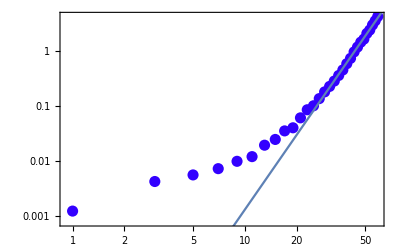

```mathematica
Show[ListLogLogPlot[data[[All,{1,2}]],PlotStyle->{PointSize[0.02],Hue[0.7]},DisplayFunction->Identity],Plot[fit[x],{x,0,5},DisplayFunction->Identity],DisplayFunction->$DisplayFunction,Frame->True,Axes->False]
```

This is a linear-log plot. A straight line represents an exponential:

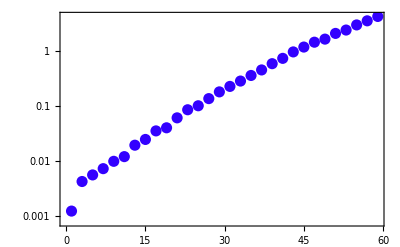

```mathematica
ListLogPlot[data[[All,{1,2}]],PlotStyle->{PointSize[0.02],Hue[0.7]},Frame->True,Axes->False]
```

It is difficult to decide from the plots whether the behaviour is polynomic or exponential, but seems polynomic. This is misleading. The Dummy algorithm is based on the Intersection algorithm, which is known to be exponential in the worst case, though highly efficient. The meaning of this will become clear in the second example below.
This linear-log plot (not produced in this notebook) compares the timings of several packages on the same problem. On the x-axis, the number of antisymmetric tensors to canonicalize (both when the result is zero and when it is not zero). On the y-axis, the timings in Seconds. The color code is the following:
	Red: MathTensor
	Yello: dhPark
	Green: Tools of Tensor Calculus
	Blue (upper): xTensor with pure Mathematica code in xPerm
	Magenta: Canon (R. Portugal's own implementation in Maple of his canonicalization algorithms)
	Blue (lower): xTensor with the external C-executable xperm
The efficiency of the permutation-based algorithms with respect to more classic algorithms is clear.

```mathematica
UndefTensor[Anti];
Remove[productAnti,canAnti]
```

** UndefTensor: Undefined tensor Anti

Example 2:

As a second example, let us work with the canonicalization of products of Riemann tensors.

Define the Riemann tensor:

```mathematica
DefTensor[R[a,b,c,d],M3,RiemannSymmetric[{1,2,3,4}]]
```

** DefTensor: Defining tensor R[a,b,c,d].

with the expected permutation symmetries:

```mathematica
R[a,-a,b,c]//ToCanonical
```

0

```mathematica
R[-b,-c,-d,-a]//ToCanonical
```

-R |   |   |   |  
a | d | b | c

The function productR constructs random products of Riemann tensors. The second argument gives the list of free indices of the expression (always with even length). There is no defined conversion to Ricci or RicciScalar tensors.

```mathematica
canonindices[npairs_,frees_]:=Join[frees,Flatten[{#,-#}&/@GetIndicesOfVBundle[TangentM3,npairs,Join[frees,-frees]]]];
productR[n_,frees_:{}]:=Apply[Times,Apply[R,Partition[canonindices[2n-Length[frees]/2,frees][[First@RandomPerm[4n]]],4],1]]/;EvenQ[Length[frees]];
```

```mathematica
productR[1]
```

R | a |   |   | b
  | a | b |

```mathematica
productR[10]
```

R |   |   | j14 |  
b | j12 |   | j14 R |   | j | j13 | i
g |   |   |   R | g | j15 |   | a
  |   | j15 |   R |   |   |   | f
i | h | a |   R |   |   |   | j18
j1 | f | d |   R | j1 |   |   | j17
  | e | c |   R | j10 | b |   |  
  |   | j16 | j10 R |   |   | j11 | h
j11 | j13 |   |   R |   |   | c | e
j17 | j |   |   R |   | j16 | j12 | d
j18 |   |   |

```mathematica
productR[3,{a,b,c,-d}]
```

R | a | f |   |  
  |   | d | h R | b |   | c | g
  | e |   |   R |   | h |   | e
f |   | g |

```mathematica
productR[3,{a,b,c}]
```

productR[3,{a,b,c}]

This second function canonicalizes the products of Riemanns, timing the process:

```mathematica
canR[n_,frees_:{}]:=Flatten[{n,With[{product=productR[n,frees]},AbsoluteTiming[ToCanonical[product]]]}]
```

Examples:

```mathematica
canR[1]
```

{1,0.001532,-R | a | b |   |  
  |   | a | b}

```mathematica
canR[2]
```

{2,0.004183,0}

```mathematica
canR[3]
```

{3,0.006365,0}

```mathematica
canR[4]
```

{4,0.008595,R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   |   |   | g
c | e | f |   R |   | h |   |  
d |   | g | h}

```mathematica
canR[10]
```

{10,0.024734,-R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | f | g | h
d |   |   |   R |   | i |   | j
e |   | g |   R |   | j1 | j10 | j11
f |   |   |   R |   | j12 |   | j13
h |   | j1 |   R |   | j14 | j15 | j16
i |   |   |   R |   | j17 |   |  
j |   | j10 | j13 R |   |   |   |  
j11 | j14 | j15 | j16 R |   | j18 |   |  
j12 |   | j17 | j18}

```mathematica
canR[20]
```

{20,0.209571,R |   |   | e | f
a | c |   |   R | a | b | c | d
  |   |   |   R |   | g |   | h
b |   | d |   R |   | i |   | j
e |   | f |   R |   | j1 | j10 | j11
g |   |   |   R |   | j12 | j13 | j14
h |   |   |   R |   |   | j15 | j16
i | j1 |   |   R |   | j17 | j18 | j19
j |   |   |   R |   | j2 |   | j20
j10 |   | j15 |   R |   | j21 | j22 | j23
j11 |   |   |   R |   | j24 |   | j25
j12 |   | j21 |   R |   |   | j26 | j27
j13 | j18 |   |   R |   | j28 |   | j29
j14 |   | j24 |   R |   | j3 |   |  
j16 |   | j22 | j29 R |   | j30 |   | j31
j17 |   | j23 |   R |   | j32 |   | j33
j19 |   | j26 |   R |   |   |   | j34
j2 | j33 | j3 |   R |   | j35 |   |  
j20 |   | j30 | j34 R |   |   |   | j36
j25 | j32 | j28 |   R |   |   |   |  
j27 | j31 | j35 | j36}

```mathematica
canR[25]
```

{25,0.094011,0}

Scaling of timings. Evaluating next cell could take between half a minute and a minute:

```mathematica
data1=canR/@Range[1,25];
data2=canR/@Range[1,25];
data3=canR/@Range[1,25];
```

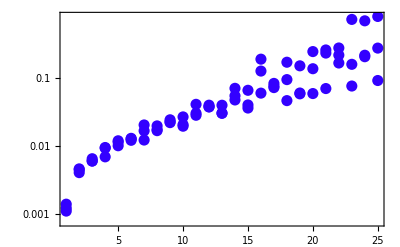

```mathematica
plot0=ListLogPlot[Join[data1,data2,data3][[All,{1,2}]],PlotRange->All,Frame->True,PlotStyle->{PointSize[0.02],Hue[0.7]}]
```

We repeat the computation, but now leaving two and four free indices in the expressions:

```mathematica
data1=canR[#,{a,b}]&/@Range[1,25];
data2=canR[#,{a,b}]&/@Range[1,25];
data3=canR[#,{a,b}]&/@Range[1,25];
```

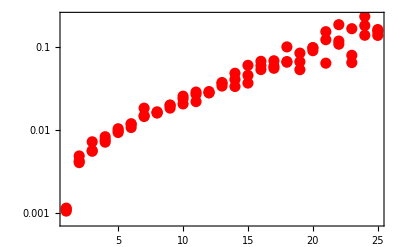

```mathematica
plot1=ListLogPlot[Join[data1,data2,data3][[All,{1,2}]],PlotRange->All,Frame->True,PlotStyle->{PointSize[0.02],Hue[0]}]
```

```mathematica
data1=canR[#,{a,b,c,d}]&/@Range[1,25];
data2=canR[#,{a,b,c,d}]&/@Range[1,25];
data3=canR[#,{a,b,c,d}]&/@Range[1,25];
```

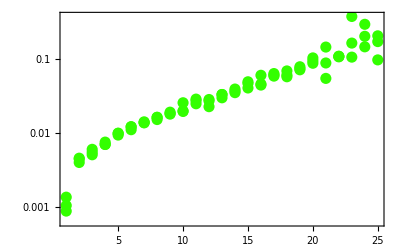

```mathematica
plot2=ListLogPlot[Join[data1,data2,data3][[All,{1,2}]],PlotRange->All,Frame->True,PlotStyle->{PointSize[0.02],Hue[0.3]}]
```

Combining the three plots, we do not see any important difference in the timings:

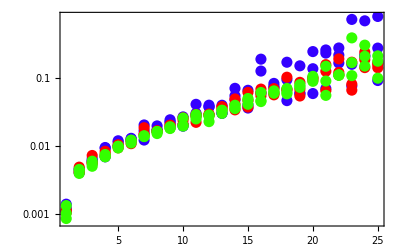

```mathematica
Show[plot0,plot1,plot2]
```

Example 3:

Now let us concentrate on the products of seven Riemanns.

This figure (not constructed in this notebook) shows an histogram of the timings of canonicalization of a hundred thousand ramdom products of seven Riemanns. Note in the smaller plot that there are some cases which take much more time (and much more memory) to canonicalize. This is a consequence of the algorithm not being polynomial, but exponential in the worst case. Those are cases in which the symmetry is much higher than usual, for example because the product of Riemanns can be separated in products of decoupled monomials. There are cases in which, however, the reason is not at all clear, so that in general it is not possible to prepare the canonicalization algorithms to avoid all possible "worst cases".

Clean up

```mathematica
UndefTensor[R]
Remove[canonindices,productR,canR,data1,data2,data3,plot0,plot1,plot2]
```

** UndefTensor: Undefined tensor R

```mathematica
MetricsOfVBundle[TangentM3]^={};
Clear[metricg];
```

Summarizing, the general canonicalization algorithms of xTensor` are highly efficient in most cases, much faster than the algorithms used by other tensor computer algebra systems. However, from time to time you will find special cases which take several orders of magnitude longer to canonicalize than other similar cases (for example a simple reordering of the indices keeping the same tensors), usually also swallowing up a large chunk of memory in your computer. This is normal behaviour, and it is due to the fact that the Group Intersection algorithm unavoidably behaves like that. Fortunately the special cases are always that: special; if you understand the meaning of "special" in your problem, you can prepare the system in advance to switch to "special" alternative algorithms.
In hindsight, this is the price we pay for using a general algorithm, but for the case of permutation symmetries it is worth paying it, because only in a very small fraction of cases the algorithm behaves exponentially, instead of polynomially. The case with multiterm symmetries is precisely the opposite: all known algorithms behave exponentially in most cases.

### 4.4. Canonicalization in a 1-dimensional space

xTensor` deals with 1-dimensional spaces in exactly the same way as with any other space. In particular, indices cannot be repeated, even though there is just one indiependent direction. This is solved by imposing full symmetry at canonicalization time.

Define a 1-dimensional space:

```mathematica
DefManifold[M1,1,{a1,b1,c1,d1}]
```

** DefManifold: Defining manifold M1.

** DefVBundle: Defining vbundle TangentM1.

and some tensors in this space :

```mathematica
DefTensor[W[a1,b1],M1]
```

** DefTensor: Defining tensor W[a1,b1].

```mathematica
DefTensor[R[a1,b1],M1]
```

** DefTensor: Defining tensor R[a1,b1].

Now something like this is zero :

```mathematica
W[a1,b1]R[c1,d1]-W[d1,a1]R[c1,b1]//ToCanonical
```

0

Clean up :

```mathematica
UndefTensor/@{W,R};
UndefManifold[M1]
```

** UndefTensor: Undefined tensor W

** UndefTensor: Undefined tensor R

** UndefVBundle: Undefined vbundle 𝕋M1

** UndefManifold: Undefined manifold M1

## 5. Rules and patterns

### 5.1. Unique dummies and screening

One of the most important issues in a tensor packages is how to deal with index contractions, i.e. with dummy indices. Until now this was not a real issue for us because all input expressions were simply canonicalized, a process which does not introduce new indices, but rather, eliminates indices. Now we face the opposite problem: expanding expressions into new expressions with more dummy indices, for example the conversion of a covariant derivative of a tensor in terms of a different covariant derivative. There are three problems with conversions that we must address.
This subsection explains in detail what those three problems are and how they will be solved. Though the explanations might seem a bit technical, it is important to understand them, because they are based on core concepts of Mathematica.
As an aside, there are two ways to define conversions of expressions into new expressions in Mathematica: assignments (Set and its variants SetDelayed, TagSet, UpSet, etc.) and rules (Rule and its variant RuleDelayed). Asignments can be considered as global or automatic rules. Rules can be considered as local assignments. See the Mathematica Help.
First problem. Let us see a simple example using Set:

Define the vector w in terms of S and v. Introduce a simple dummy:

```mathematica
DefTensor[w[a],M3]
```

** DefTensor: Defining tensor w[a].

```mathematica
w[a_]=S[a,b]v[-b]
```

S | a | b
  |   v |  
b

[Note that we have used a Pattern on the right hand side. That is normal Mathematica, and a helpful feature which allows us to indicate the generality of the rule (which indices or tensors are accepted in the rule)].

Then these expressions would be totally wrong:

```mathematica
w[b]
```

S | b | b
  |   v |  
b

```mathematica
w[a]w[-a]
```

S |   | b
a |   S | a | b
  |   (v |  
b)^2

Mathematica recommends the following solution to this problem:

Use a Module construct, such that the dummy index b is replaced by a unique symbol denoted with a $ sign, and a unique integer number. Note that we must now use SetDelayed (:=), and not Set (=), to avoid inmediate evaluation of Module:

```mathematica
w[a_]:=Module[{b},S[a,b]v[-b]]
```

```mathematica
w[b]
```

S | b | b$20151
  |   v |  
b$20151

```mathematica
w[a]w[-a]
```

S |   | b$20153
a |   S | a | b$20152
  |   v |  
b$20152 v |  
b$20153

This solves the first problem but generates two more, which are solved by "screening" the dollar-indices:

ScreenDollarIndices		Hide internal unique dummy indices

Screening of indices.

First, each time we use the assignment we get a different object, what complicates comparisons. The following is not automatically recognized as zero!

```mathematica
w[a]-w[a]
```

S | a | b$20154
  |   v |  
b$20154-S | a | b$20155
  |   v |  
b$20155

```mathematica
%//InputForm
```

S[a, b$20154]*v[-b$20154] - S[a, b$20155]*v[-b$20155]

The second problem is purely aesthetical: the dollar-indices are terribly ugly. xTensor` has the function ScreenDollarIndices to convert the dollar-indices into normal-looking indices:

```mathematica
{w[a],w[b],w[c],w[a]w[-a],w[a]-w[a]}
```

{S | a | b$20157
  |   v |  
b$20157,S | b | b$20158
  |   v |  
b$20158,S | c | b$20159
  |   v |  
b$20159,S |   | b$20161
a |   S | a | b$20160
  |   v |  
b$20160 v |  
b$20161,S | a | b$20162
  |   v |  
b$20162-S | a | b$20163
  |   v |  
b$20163}

```mathematica
ScreenDollarIndices[%]
```

{S | a | b
  |   v |  
b,S | b | a
  |   v |  
a,S | c | a
  |   v |  
a,S |   | c
a |   S | a | b
  |   v |  
b v |  
c,0}

```mathematica
InputForm[%]
```

{S[a, b]*v[-b], S[b, a]*v[-a], S[c, a]*v[-a], S[-a, c]*S[a, b]*v[-b]*v[-c], 0}

The Module construct is not the solution for all problems in tensor conversions. There are two more problems, as seen in the following examples. Second problem:

Objects and indices cannot share the same symbol names. Suppose there were a tensor also called a:

```mathematica
w[a_]:=a[a]
```

```mathematica
w[b]
```

b[b]

In xTensor`, this is solved by enforcing type declarations. Every object must be defined supplying a symbol, and that symbol is given a type. A symbol cannot have two different types. This can be seen as a restriction, but it is actually a useful safety feature.

The tensor a[b] cannot be defined:

```mathematica
DefTensor[a[b],M3]
```

ValidateSymbol::used: Symbol a is already used as an abstract index.

The final (third) problem involves dummies again, and happens in the few cases in which the same symbol represents a dummy on both sides and there are additional dummies on the right. The only possible solution is changing the name of the conflicting dummies either on the left or on the right hand side.

Define the following relation with dummies both on the left and right hand sides. Note that the b dummy is present in both sides and is a pattern on the left hand side (Mathematica already points out the error by reddening the dummy):

```mathematica
w[a_,b_,-b_]:=Module[{b,c},S[a,b,-b,c,-c]]
```

```mathematica
w[a,b,-b]
```

S | a | b$20178 |   | c$20178 |  
  |   | b$20178 |   | c$20178

```mathematica
w[a,c,-c]
```

Module::dups: Conflicting local variables c and c$ found in local variable specification {c,c$}.

Module[{c,c$},S | a | c |   | c$ |  
  |   | c |   | c$]

For example, we can change the name of the dummy index b on the right hand side:

```mathematica
w[a_,b_,-b_]:=Module[{d,c},S[a,d,-d,c,-c]]
```

```mathematica
w[a,b,-b]
```

S | a | d$20185 |   | c$20185 |  
  |   | d$20185 |   | c$20185

```mathematica
w[a,c,-c]
```

S | a | d$20186 |   | c$20186 |  
  |   | d$20186 |   | c$20186

As we said, the second problem is solved in xTensor` simply by enforcing type declarations. The first and third problems will be solved introducing a new collection of Index* assignment and rule functions which properly prepare the required Module constructs. They are IndexSet, IndexSetDelayed, IndexRule and IndexRuleDelayed, imitating their respective Mathematica counterparts, and they are described in detail in the next subsections.

We finish this section coming back to the function ScreenDollarIndices. We recommend to automate its use by assigning one of the global variables $Post or $PrePrint to it. There is a small difference between these two global variables (mentioned below), and it is not clear that one of them is always better than the other for screening, but I generally prefer $PrePrint:

Assign $PrePrint:

```mathematica
$PrePrint=ScreenDollarIndices;
```

Now the screening is automatic:

```mathematica
w[a,c,-c]
```

S | a | c |   | b |  
  |   | c |   | b

The screening happened after the result was assigned to Out[...] and hence if we temporarily remove $PrePrint, we still see the dollar-indices. (That wouldn't happen using $Post.)

```mathematica
$PrePrint=.
```

```mathematica
%%
```

S | a | d$20187 |   | c$20187 |  
  |   | d$20187 |   | c$20187

Clean up

```mathematica
w[a_,b_,-b_]=.
```

From now on, in this notebook, we shall use automatic screening:

```mathematica
$PrePrint=ScreenDollarIndices;
```

### 5.2. IndexSet and IndexSetDelayed

The xTensor` functions IndexSet and IndexSetDelayed imitate the behaviour of Set and SetDelayed (which delays the evaluation of the rhs to the moment when the lhs is converted into the rhs).

IndexSet				Set value of an indexed expression, at definition time
IndexSetDelayed			Set value of an indexed expression, at evaluation time

Set functions for indexed expressions.

Example of use of IndexSet:

```mathematica
IndexSet[w[a_],S[a,b]v[-b]]
```

S | a | b
  |   v |  
b

```mathematica
?w
```

Global`w

Dagger[w]^=w
 
DefInfo[w]^={tensor,}
 
DependenciesOfTensor[w]^={M3}
 
HostsOf[w]^={M3,𝕋M3}
 
PrintAs[w]^=w
 
SlotsOfTensor[w]^={𝕋M3}
 
SymmetryGroupOfTensor[w]^=StrongGenSet[{},GenSet[]]
 
TensorID[w]^={}
 
xTensorQ[w]^=True
 
w | a̲
 :=Module[{b},S | a | b
  |   v |  
b]

```mathematica
w[b]
```

S | b | a
  |   v |  
a

In this case the code finds the conflicting dummies, and then replaces the offending dummy on the right hand side:

```mathematica
DefTensor[T[a,b,c],M3]
```

** DefTensor: Defining tensor T[a,b,c].

```mathematica
IndexSet[T[a_,b_,-b_],S[a,b,-b,c,-c]]
```

S | a | b |   | c |  
  |   | b |   | c

```mathematica
?T
```

Global`T

Dagger[T]^=T
 
DefInfo[T]^={tensor,}
 
DependenciesOfTensor[T]^={M3}
 
HostsOf[T]^={M3,𝕋M3}
 
PrintAs[T]^=T
 
SlotsOfTensor[T]^={𝕋M3,𝕋M3,𝕋M3}
 
SymmetryGroupOfTensor[T]^=StrongGenSet[{},GenSet[]]
 
TensorID[T]^={}
 
xTensorQ[T]^=True
 
T | a̲ | b̲ |  
  |   | b̲:=Module[{j$20206,c},S | a | j$20206 |   | c |  
  |   | j$20206 |   | c]

```mathematica
T[a,c,-c]
```

S | a | c |   | b |  
  |   | c |   | b

Example of use of IndexSetDelayed. Note that we only use a pattern in the first index of U and that w is still not evaluated:

```mathematica
IndexSetDelayed[T[-a_,-b,-c],w[-a]w[-b]w[-c]]
```

```mathematica
?T
```

Global`T

Dagger[T]^=T
 
DefInfo[T]^={tensor,}
 
DependenciesOfTensor[T]^={M3}
 
HostsOf[T]^={M3,𝕋M3}
 
PrintAs[T]^=T
 
SlotsOfTensor[T]^={𝕋M3,𝕋M3,𝕋M3}
 
SymmetryGroupOfTensor[T]^=StrongGenSet[{},GenSet[]]
 
TensorID[T]^={}
 
xTensorQ[T]^=True
 
T | a̲ | b̲ |  
  |   | b̲:=Module[{j$20206,c},S | a | j$20206 |   | c |  
  |   | j$20206 |   | c]
 
T |   |   |  
a̲ | b | c:=Module[{},w |  
a w |  
b w |  
c]

```mathematica
T[-a,-b,-c]
```

S |   | d
a |   S |   | e
b |   S |   | f
c |   v |  
d v |  
e v |  
f

We can change the definition of w and the conversion from S to w will be still valid:

```mathematica
IndexSet[w[a_],S[a,b]S[-b,-c]v[c]]
```

S | a | b
  |   S |   |  
b | c v | c

```mathematica
T[-a,-b,-c]
```

S |   | d
a |   S |   | e
b |   S |   | f
c |   S |   |  
d | g S |   |  
e | h S |   |  
f | i v | g
  v | h
  v | i

Clean up:

```mathematica
T[a_,b_,-b_]=.
```

```mathematica
T[-a_,-b,-c]=.
```

```mathematica
w[a_]=.
```

### 5.3. Index patterns

In the previous definitions of the vector w[a] we always used the pattern a_ which stands for any possible input, including up-indices and down-indices of any manifold, or even directional or label (or basis or component) indices. Sometimes this is what we want, but often it is not. In the following definitions there are no dummies or conflicts between indices and tensor names, so that we can safely use the usual SetDelayed (:=) definitions to simplify the examples.
The notation for tensors and indices in xTensor` is very simple, but that complicates working with patterns. On the other hand, there are always several ways to represent the same pattern.

Define, for the sake of simplicity:

```mathematica
dirvup=Dir[v[d]];
dirvdown=Dir[v[-d]];
```

This pattern stands for everything. Every w is converted into T:

```mathematica
w[a_]:=S[a]
```

```mathematica
{w[a],w[-a],w[dirvdown],w[dirvup],w[A],w[-A]}
```

{S | a
 ,S |  
a,S | v
 ,S |  
v,S | A
 ,S |  
A}

```mathematica
w[a_]=.
```

Let us first work with the character of the indices: use the functions

UpIndexQ				Detect up-indices
DownIndexQ				Detect down-indices

Index character.

This pattern matches only up-indices:

```mathematica
w[a_?UpIndexQ]:=S[a]
```

```mathematica
{w[a],w[-a],w[dirvdown],w[dirvup],w[A],w[-A]}
```

{S | a
 ,w |  
a,S | v
 ,w |  
v,S | A
 ,w |  
A}

```mathematica
w[a_?UpIndexQ]=.
```

This pattern matches only down-indices:

```mathematica
w[a_?DownIndexQ]:=S[a]
```

```mathematica
{w[a],w[-a],w[dirvdown],w[dirvup],w[A],w[-A]}
```

{w | a
 ,S |  
a,w | v
 ,S |  
v,w | A
 ,S |  
A}

```mathematica
w[a_?DownIndexQ]=.
```

And now we work with the type of index: use the functions

AIndexQ				Detect abstract indices
BIndexQ				Detect basis indices
CIndexQ				Detect component indices
DIndexQ				Detect directional indices
LIndexQ				Detect label indices
GIndexQ				Detect all generalized indices, but not patterns
ABIndexQ				Detect contractible indices (abstract or basis indices)
BCIndexQ				Detect indices associated to a basis or chart (basis or component indices)
CDIndexQ				Detect indices representing a direction (component or directional indices)
PIndexQ				Detect pattern indices

Detect types of indices.

Introduce another manifold, with a new set of indices:

```mathematica
DefManifold[S2,2,{A,B,C,D,F,G}]
```

** DefManifold: Defining manifold S2.

** DefVBundle: Defining vbundle TangentS2.

ValidateSymbol::capital: System name C is overloaded as an abstract index.

ValidateSymbol::capital: System name D is overloaded as an abstract index.

This pattern matches only abstract indices, from any vector bundle:

```mathematica
w[a_?AIndexQ]:=S[a]
```

```mathematica
{w[a],w[-a],w[dirvup],w[dirvdown],w[A],w[-A]}
```

{S | a
 ,S |  
a,w |  
v,w | v
 ,S | A
 ,S |  
A}

```mathematica
w[a_?AIndexQ]=.
```

There is a simple and efficient pattern for abstract up-indices or abstract down-indices:

```mathematica
w[a_Symbol]:=S[a]
```

```mathematica
{w[a],w[-a],w[dirvup],w[dirvdown],w[A],w[-A]}
```

{S | a
 ,w |  
a,w |  
v,w | v
 ,S | A
 ,w |  
A}

```mathematica
w[a_Symbol]=.
```

```mathematica
w[-a_Symbol]:=S[-a]
```

```mathematica
{w[a],w[-a],w[dirvup],w[dirvdown],w[A],w[-A]}
```

{w | a
 ,S |  
a,w |  
v,w | v
 ,w | A
 ,S |  
A}

```mathematica
w[-a_Symbol]=.
```

This pattern matches only directional indices. Recall that directions do not have a sign in front. A message is sent complaining about the character of the vector v.

```mathematica
w[a_?DIndexQ]:=S[a]
```

```mathematica
{w[a],w[-a],w[dirvup],w[dirvdown],w[A],w[-A]}
```

Validate::error: Invalid character of index in tensor v

{w | a
 ,w |  
a,S |  
v,S | v
 ,w | A
 ,w |  
A}

```mathematica
w[a_?DIndexQ]=.
```

There is also a simpler version (which does not find the problem with the position of the ultraindex):

```mathematica
w[a_Dir]:=S[a]
```

```mathematica
{w[a],w[-a],w[dirvup],w[dirvdown],w[A],w[-A]}
```

{w | a
 ,w |  
a,S |  
v,S | v
 ,w | A
 ,w |  
A}

```mathematica
w[a_Dir]=.
```

The functions AIndexQ, BIndexQ, CIndexQ, DIndexQ and GIndexQ admit a second argument restricting the manifold to which the indices must belong.

This pattern only matches abstract indices on TangentM3:

```mathematica
w[a_?(AIndexQ[#,TangentM3]&)]:=S[a]
```

```mathematica
{w[a],w[-a],w[dirvup],w[dirvdown],w[A],w[-A]}
```

{S | a
 ,S |  
a,w |  
v,w | v
 ,w | A
 ,w |  
A}

```mathematica
w[a_?(AIndexQ[#,TangentM3]&)]=.
```

Again there are simpler and cleaner versions, also discriminating between upindices and downindices (Q-functions) or not (pmQ-functions). The use of Symbol is not needed now.

```mathematica
w[a_?TangentM3`Q]:=S[a]
```

```mathematica
{w[a],w[-a],w[dirvup],w[dirvdown],w[A],w[-A]}
```

{S | a
 ,w |  
a,w |  
v,w | v
 ,w | A
 ,w |  
A}

```mathematica
w[a_?TangentM3`Q]=.
```

```mathematica
w[-a_?TangentM3`Q]:=S[-a]
```

```mathematica
{w[a],w[-a],w[dirvup],w[dirvdown],w[A],w[-A]}
```

{w | a
 ,S |  
a,w |  
v,w | v
 ,w | A
 ,w |  
A}

```mathematica
w[-a_?TangentM3`Q]=.
```

```mathematica
w[a_?TangentM3`pmQ]:=S[a]
```

```mathematica
{w[a],w[-a],w[dirvup],w[dirvdown],w[A],w[-A]}
```

{S | a
 ,S |  
a,w |  
v,w | v
 ,w | A
 ,w |  
A}

```mathematica
w[a_?TangentM3`pmQ]=.
```

In case of doubt use the function PatternIndex, which constructs patterns of the required form.

These are examples of different patterns for abstract indices named a. Note the minus sign in front of a for down-indices. The pattern is for the symbol of the index, and not for the whole index.

```mathematica
PatternIndex[a,AIndex]
```

a_?AIndexQ

```mathematica
PatternIndex[a,AIndex,Up]
```

a_Symbol?AIndexQ

```mathematica
PatternIndex[a,AIndex,Down,TangentM3]
```

-a_Symbol?TangentM3`Q

```mathematica
PatternIndex[a,AIndex,Null,TangentM3]
```

a_?TangentM3`pmQ

These are patterns for directional indices named d:

```mathematica
PatternIndex[d,DIndex]
```

d_Dir

```mathematica
PatternIndex[d,DIndex,Up]
```

d_Dir?UpIndexQ

```mathematica
PatternIndex[d,DIndex,Down,TangentM3]
```

d_Dir?(DownIndexQ[#1]&&DIndexQ[#1,𝕋M3]&)

```mathematica
PatternIndex[d,DIndex,Null,TangentM3]
```

d_Dir?(DIndexQ[#1,𝕋M3]&)

### 5.4. IndexRule and IndexRuleDelayed

The function IndexRule relates to Rule exactly in the same way that IndexSet relates to Set. It just introduces Module constructs. The symbol ↦ has been introduced. It is input as ∖[RightTeeArrow], but this input sequence doesn't work with the style used in this notebook (I don't know why).

IndexRule				Construct rule for an indexed expression, at definition time
IndexRuleDelayed		Construct rule for an indexed expression, at evaluation time

Rule  functions for indexed expressions.

Here we have again the problem of repeated indices b:

```mathematica
{w[a],w[b]}/.w[a_]->S[a,b]v[-b]
```

Validate::repeated: Found indices with the same name b.

Throw::nocatch: Uncaught Throw[Null] returned to top level.

Hold[Throw[Null]]

Using IndexRule the problem disappears:

```mathematica
{w[a],w[b]}/.IndexRule[w[a_],S[a,b]v[-b]]
```

{S | a | b
  |   v |  
b,S | b | a
  |   v |  
a}

```mathematica
{w[a],w[b]}/.w[a_]↦S[a,b]v[-b]
```

{S | a | b
  |   v |  
b,S | b | a
  |   v |  
a}

### 5.5. MakeRule

Apart from the coding aspects solved by the Index* functions, there are other, more mathematical issues which must be adressed. For instance, given a rule LHS→RHS how can we apply the rule on expressions which are equivalent to LHS but indices are permuted due to symmetries or metric shifting? Can we apply the rule on all vbundles or just on some of them? These kind of options are controlled by MakeRule, the second most complicated function in xTensor` after ToCanonical. This function uses the properties of the metric tensors, and hence we delay its description to subsection 9.1 below.

## 6. Derivatives

### 6.1. Covariant derivatives

We understand a covariant derivative as a covariant derivative operator (see Wald). In particular, ordinary ("partial") derivative operators are obtained as covariant derivatives with the options Curvature->False and Torsion->False. Covariant derivatives are real operators acting on (possibly complex) vector bundles. The treatment of derivatives on xTensor` is fully abstract, and hence we do not explain here how to take components of a derivative of a tensor. This is dealt with in the companion package xCoba`, and explained in its documentation.

DefCovD				Define a covariant derivative operator
UndefCovD				Undefine a covariant derivative
$CovDs					List of defined covariant derivatives
CovDQ					Validate a covariant derivative symbol

Definition of a covariant derivative.

Default options for DefCovD:

```mathematica
Options[DefCovD]
```

{SymbolOfCovD→{;,▽},Torsion→False,Curvature→True,FromMetric→Null,CurvatureRelations→True,ExtendedFrom→Null,OtherDependencies→{},OrthogonalTo→{},ProjectedWith→{},WeightedWithBasis→Null,ProtectNewSymbol:>$ProtectNewSymbols,Master→Null,DefInfo→{covariant derivative,}}

Define a covariant derivative Cd on TangentM3 (the default vbundle obtained from the index given in the derivative). Automatically the Christoffel symbols and the Riemann and Ricci tensors are defined. By default xTensor` does not assume that this derivative is associated to a metric and therefore the symmetries of the Riemann tensor are not as expected: there is just antisymmetry in the first pair of indices. The Ricci tensor has no symmetry at all. There is no Ricci scalar.

```mathematica
DefCovD[Cd[-a]]
```

** DefCovD: Defining covariant derivative Cd[-a].

** DefTensor: Defining vanishing torsion tensor TorsionCd[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelCd[a,-b,-c].

** DefTensor: Defining Riemann tensor RiemannCd[-a,-b,-c,d]. Antisymmetric only in the first pair.

** DefTensor: Defining non-symmetric Ricci tensor RicciCd[-a,-b].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

```mathematica
SymmetryGroupOfTensor[RiemannCd]
```

StrongGenSet[{1,2},GenSet[-(1,2)]]

```mathematica
RiemannCd[-a,-b,-c,b]
```

R[▽] |   |  
a | c

```mathematica
SymmetryGroupOfTensor[RicciCd]
```

StrongGenSet[{},GenSet[]]

The names of the associated tensors are determined by the function GiveSymbol. Their output symbols are determined by the function GiveOutputString.If you want to change any of those, modify the corresponding function before defining the object.

```mathematica
GiveSymbol[Riemann,Cd]
```

RiemannCd

```mathematica
GiveOutputString[Riemann,Cd]
```

R[▽]

Derivatives can be represented in two ways, encoded as the strings "Prefix" or "Postfix" in the global variable $CovDFormat. The default value is "Prefix". Directional derivatives are always given in "Prefix" notation.

```mathematica
$CovDFormat
```

Prefix

```mathematica
Cd[-a][T[a,b,-c]]
```

▽_a T | a | b |  
  |   | c

```mathematica
$CovDFormat="Postfix";
```

```mathematica
Cd[-a][T[a,b,-c]]
```

T | a | b |   |   
  |   | c | ;a

```mathematica
Cd[Dir[v[d]]][T[a,b,-c]]
```

▽_v T | a | b |  
  |   | c

Derivatives are linear operators and implement automatically the Leibnitz rule. The final ordering of terms is decided by Mathematica.

```mathematica
DefTensor[r[],M3]
```

** DefTensor: Defining tensor r[].

```mathematica
Cd[-a][7r[]v[a]+S[a,b]v[-b]]
```

v |  
b S | a | b |   
  |   | ;a+7 (v | a
  (▽_a r)+r v | a |   
  | ;a)+S | a | b
  |   v |   |   
b | ;a

Dummy indices are, by default, pushed to the right by the canonicalization process

```mathematica
Cd[-a][T[f,c,-b]U[-c,-e,-d]]//ToCanonical
```

-U |   |   |  
d | e | c T | f | c |   |   
  |   | b | ;a-T | f | c |  
  |   | b U |   |   |   |   
d | e | c | ;a

SortCovDs				Commute covariant derivatives, adding Riemann tensors if needed
SortCovDsStart			Automatic commutation of covariant derivatives
SortCovDsStop			Remove automatic commutation of covariant derivatives
$CommuteCovDsOnScalars		Automatic commutation of torsionless derivatives on scalar expressions

Commutation of derivatives.

By default, a special ordinary derivative called PD is defined. It is one of the many covariant derivative operators without curvature and without torsion, but no further assumptions are made about it. It can be used as a generic "partial derivative" in most computations, but its meaning is different. Note that they are not automatically sorted:

```mathematica
PD[-a][PD[-b][T[c,d,-e]]]
```

T | c | d |   |    |   
  |   | e | ,b | ,a

```mathematica
$CovDFormat="Prefix";
```

```mathematica
PD[-a][PD[-b][T[c,d,-e]]]
```

∂_a ∂_b T | c | d |  
  |   | e

```mathematica
PD[-a][PD[-b][T[c,d,-e]]]-PD[-b][PD[-a][T[c,d,-e]]]
```

∂_a ∂_b T | c | d |  
  |   | e-∂_b ∂_a T | c | d |  
  |   | e

```mathematica
%//SortCovDs
```

0

We can automate the commutation of derivatives:

```mathematica
SortCovDsStart[PD]
```

```mathematica
PD[-a][PD[-b][T[c,d,-e]]]-PD[-b][PD[-a][T[c,d,-e]]]
```

0

```mathematica
SortCovDsStop[PD]
```

Note that $CommuteCovDsOnScalars is still True.

All symmetric (torsionless) connections commute (with themselves) on scalar expressions. That can be avoided switching off the variable $CommuteCovDsOnScalars.

The input of high-order derivatives is certainly slow due to the sharp syntactic restrictions of xTensor`. There are several options to avoid this problem. Of course, you cannot use Validate unless you modify it to recognize the new syntactic extensions.

The standard way to input a third order derivative is this:

```mathematica
PD[-a][PD[-b][PD[-c][T[c,d,-e]]]]
```

∂_a ∂_b ∂_c T | c | d |  
  |   | e

We can use the prefix notation of Mathematica:

```mathematica
PD[-a]@PD[-b]@PD[-c]@T[c,d,-e]
```

∂_a ∂_b ∂_c T | c | d |  
  |   | e

or we can define our own rules to input derivatives, breaking the standard syntax. The simplest possibility, based on the fact that the first bracket of PD always contains a single index, is:

```mathematica
Unprotect[PD];
```

```mathematica
PD[expr_,a__,b_]:=PD[b][PD[expr,a]]
PD[expr_,a_]:=PD[a][expr]
```

```mathematica
PD[T[c,d,-e],-c,-b,-a]
```

∂_a ∂_b ∂_c T | c | d |  
  |   | e

```mathematica
InputForm[%]
```

PD[-a][PD[-b][PD[-c][T[c, d, -e]]]]

```mathematica
PD[expr_,a__,b_]=.
PD[expr_,a_]=.
```

or an intermediate situation, based on the same fact, is:

```mathematica
PD[a_,b__][expr_]:=PD[a][PD[b][expr]]
```

```mathematica
PD[-a,-b,-c][T[c,d,e]]
```

∂_a ∂_b ∂_c T | c | d | e
  |   |

```mathematica
InputForm[%]
```

PD[-a][PD[-b][PD[-c][T[c, d, e]]]]

```mathematica
PD[a_,b__][expr_]=.
```

A totally different notation could be

```mathematica
PD/:tensor_?xTensorQ[indices___,PD[index_]]:=PD[index][tensor[indices]]
```

```mathematica
T[c,d,-e,PD[-c],PD[-b],PD[-a]]
```

∂_a ∂_b ∂_c T | c | d |  
  |   | e

```mathematica
InputForm[%]
```

PD[-a][PD[-b][PD[-c][T[c, d, -e]]]]

```mathematica
PD/:tensor_?xTensorQ[indices___,PD[index_]]=.
```

```mathematica
Protect[PD];
```

### 6.2A. Implosion and explosion (I)

It is important to understand the following notational problem with derivatives. From a mathematical point of view, the derivative of a function or a tensor is another function or tensor, and hence should share its same notation. However, we must input the derivative using an operator, and hence a notational change should happen at some point. For instance, in Mathematica the operator D[f[x], x] is inmediately converted into Derivative[1][f][x]. The former doesn't have the "function form" head[x] but the latter does, with the head being Derivative[1][f]. There are many obvious advantages in this change, because now we can use a consistent treatment for all functions, but there are also disadvantages.

The main disadvantage of the change is, a mystery for all new users of Mathematica, that this does not work:

```mathematica
D[f[x],x]/.f[x]->Sin[x]
```

f'[x]

but this does work:

```mathematica
D[f[x],x]/.f->Sin
```

Cos[x]

In xTensor` we work essentially with the operator form only, and hence rules are simpler to use, but we have the problem that tensors and their covariant derivatives are treated differently. To alleviate that problem, a new device has been introduced in version 0.9.6: we now have the concepts of "implosion" and "explosion":

Suppose we start from the covariant derivative

```mathematica
Cd[-a][v[b]]
```

▽_a v | b

```mathematica
InputForm[%]
```

Cd[-a][v[b]]

Now we "implode" this expression, resulting in a new tensor being defined (there is no message reporting the creation of this new tensor, but that can be activated setting the global variable $ImplodeInfo = Info). Compare with the previous expression, and please pay attention to the positions of indices!

```mathematica
Implode[%]
```

▽v | b |  
  | a

```mathematica
InputForm[%]
```

Cdv[b, -a]

The expression can be "exploded", returning to the original:

```mathematica
Explode[%]
```

▽_a v | b

Implosion involves the construction of new tensors, and in this process their symmetries must also be constructed.

This object is symmetric:

```mathematica
PD[-a]@PD[-b]@v[c]
```

∂_a ∂_b v | c

```mathematica
SymmetryOf[%]
```

Symmetry[3,∂^(●3) ∂^(●2) v | ●1
 ,{●1→c,●2→-b,●3→-a},StrongGenSet[{2,3},GenSet[(2,3)]]]

If we implode it, that symmetry must be stored into the new tensor:

```mathematica
Implode[%%]
```

∂∂v | c |   |  
  | b | a

```mathematica
SymmetryGroupOfTensor[PDPDv]
```

StrongGenSet[{2},GenSet[(2,3)]]

Other torsionless derivatives are commuted on scalars :

```mathematica
Cd[-a]@Cd[-b]@r[]
```

▽_b▽_a r

```mathematica
Implode[%]
```

▽▽r |   |  
a | b

```mathematica
SymmetryGroupOfTensor[CdCdr]
```

StrongGenSet[{1},GenSet[(1,2)]]

but not on other tensors :

```mathematica
Cd[-a]@Cd[-b]@v[a]
```

▽_a▽_b v | a

```mathematica
Implode[%]
```

▽▽v | a |   |  
  | b | a

```mathematica
SymmetryGroupOfTensor[CdCdv]
```

StrongGenSet[{},GenSet[]]

The problem of implosion becomes more complicated when metrics (and bases) are present, but we defer the corresponding analysis to the next section, after metrics are introduced.

### 6.2B. TensorDerivative

Now that we can have tensors with non-atomic heads, it is natural to absorb the imploded information in the head of a new tensor. Following Derivative in Mathematica we introduce the head TensorDerivative.

Take a tensor expression containing derivatives:

```mathematica
Cd[-a][v[b]]
```

▽_a v | b

Convert it into the new notation (note that the derivative index is placed last):

```mathematica
%//ToTensorDerivative
```

▽v | b |  
  | a

```mathematica
%//InputForm
```

TensorDerivative[v, Cd][b, -a]

and back:

```mathematica
%%//FromTensorDerivative
```

▽_a v | b

```mathematica
%//InputForm
```

Cd[-a][v[b]]

### 6.3. Change of covariant derivative

In xTensor` we can work simultaneously with any number of covariant derivatives.

The list of all covariant derivatives currently defined is

```mathematica
$CovDs
```

{PD,Cd}

We define another one

```mathematica
DefCovD[CD[-a],SymbolOfCovD->{"|","D"}]
```

** DefCovD: Defining covariant derivative CD[-a].

** DefTensor: Defining vanishing torsion tensor TorsionCD[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelCD[a,-b,-c].

** DefTensor: Defining Riemann tensor RiemannCD[-a,-b,-c,d]. Antisymmetric only in the first pair.

** DefTensor: Defining non-symmetric Ricci tensor RicciCD[-a,-b].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

The difference between two covariant derivatives of the same tensor can be expressed in terms of Christoffel tensors (the C tensors of Wald), and in xTensor` we shall always use this point of view of Christoffels: they are always tensors, but associated to two covariant derivatives. The Christoffel tensor defined together with each derivative is the tensor associated to that derivative and the derivative PD associated to a generic chart.

Christoffel constructs the Christoffel tensor relating two derivatives. It is antisymmetric in its derivatives arguments.

```mathematica
Christoffel[CD,PD][a,-b,-c]
```

Γ[D] | a |   |  
  | b | c

```mathematica
%//InputForm
```

ChristoffelCD[a, -b, -c]

```mathematica
Christoffel[PD,CD][a,-b,-c]
```

-Γ[D] | a |   |  
  | b | c

```mathematica
%//InputForm
```

-ChristoffelCD[a, -b, -c]

The Christoffel tensor relating two non-PD derivatives is constructed automatically whenever needed, with (lexicographically) sorted derivatives, to avoid duplicity:

```mathematica
Christoffel[CD,Cd][a,-b,-c]
```

** DefTensor: Defining tensor ChristoffelCdCD[a,-b,-c].

-Γ[▽,D] | a |   |  
  | b | c

```mathematica
%//InputForm
```

-ChristoffelCdCD[a, -b, -c]

The origin of this curious conversion from Christoffel[Cd,CD] to ChristoffelCdCD is again the fact that we cannot associate information to the former.

Using this structure of Christoffel tensors we can relate any two derivatives of any tensor.

Suppose this derivative:

```mathematica
expr=CD[-d][U[-a,b,-c]]
```

D_d U |   | b |  
a |   | c

ChangeCovD (aka CovDToChristoffel in xTensor` version 0.7) changes by default to PD:

```mathematica
ChangeCovD[expr]
```

-Γ[D] | e |   |  
  | d | c U |   | b |  
a |   | e+Γ[D] | b |   |  
  | d | e U |   | e |  
a |   | c-Γ[D] | e |   |  
  | d | a U |   | b |  
e |   | c+∂_d U |   | b |  
a |   | c

That is equivalent to

```mathematica
ChangeCovD[expr,CD]
```

-Γ[D] | e |   |  
  | d | c U |   | b |  
a |   | e+Γ[D] | b |   |  
  | d | e U |   | e |  
a |   | c-Γ[D] | e |   |  
  | d | a U |   | b |  
e |   | c+∂_d U |   | b |  
a |   | c

but we can also change to any desired derivative:

```mathematica
ChangeCovD[expr,CD,Cd]
```

Γ[▽,D] | e |   |  
  | d | c U |   | b |  
a |   | e-Γ[▽,D] | b |   |  
  | d | e U |   | e |  
a |   | c+Γ[▽,D] | e |   |  
  | d | a U |   | b |  
e |   | c+▽_d U |   | b |  
a |   | c

```mathematica
ChangeCovD[%,Cd,CD]
```

D_d U |   | b |  
a |   | c

If you do not like the double-derivative Christoffels, you can always break them to the CovD-PD Christoffels:

```mathematica
%%//BreakChristoffel
```

(Γ[▽] | e |   |  
  | d | c-Γ[D] | e |   |  
  | d | c) U |   | b |  
a |   | e-(Γ[▽] | b |   |  
  | d | e-Γ[D] | b |   |  
  | d | e) U |   | e |  
a |   | c+(Γ[▽] | e |   |  
  | d | a-Γ[D] | e |   |  
  | d | a) U |   | b |  
e |   | c+▽_d U |   | b |  
a |   | c

The expansion is recursive:

```mathematica
ChangeCovD[Cd[-e][Cd[-a][T[f,c,-b]]],Cd]
```

-Γ[▽] | i |   |  
  | e | b (-Γ[▽] | d |   |  
  | a | i T | f | c |  
  |   | d+Γ[▽] | c |   |  
  | a | g T | f | g |  
  |   | i+Γ[▽] | f |   |  
  | a | h T | h | c |  
  |   | i+∂_a T | f | c |  
  |   | i)+Γ[▽] | c |   |  
  | e | i (Γ[▽] | i |   |  
  | a | g T | f | g |  
  |   | b-Γ[▽] | d |   |  
  | a | b T | f | i |  
  |   | d+Γ[▽] | f |   |  
  | a | h T | h | i |  
  |   | b+∂_a T | f | i |  
  |   | b)+Γ[▽] | f |   |  
  | e | i (Γ[▽] | i |   |  
  | a | h T | h | c |  
  |   | b-Γ[▽] | d |   |  
  | a | b T | i | c |  
  |   | d+Γ[▽] | c |   |  
  | a | g T | i | g |  
  |   | b+∂_a T | i | c |  
  |   | b)+T | f | d |  
  |   | b ∂_e Γ[▽] | c |   |  
  | a | d-T | f | c |  
  |   | d ∂_e Γ[▽] | d |   |  
  | a | b+T | d | c |  
  |   | b ∂_e Γ[▽] | f |   |  
  | a | d+Γ[▽] | f |   |  
  | a | d ∂_e T | d | c |  
  |   | b-Γ[▽] | d |   |  
  | a | b ∂_e T | f | c |  
  |   | d+Γ[▽] | c |   |  
  | a | d ∂_e T | f | d |  
  |   | b+∂_e ∂_a T | f | c |  
  |   | b-Γ[▽] | i |   |  
  | e | a (-Γ[▽] | d |   |  
  | i | b T | f | c |  
  |   | d+Γ[▽] | c |   |  
  | i | g T | f | g |  
  |   | b+Γ[▽] | f |   |  
  | i | h T | h | c |  
  |   | b+∂_i T | f | c |  
  |   | b)

Christoffel			Construct Christoffel tensor relating two derivatives
BreakChristoffel		Rewrite a Christoffel tensor as the difference of two other Christoffel tensors
ChangeCovD			Rewrite the covariant derivative of a tensor in terms of a second derivative and Christoffels

Change of covariant derivative.

If the relation between two covariant derivatives is fully described by a Christoffel tensor, then the curvature and torsion tensors associated to them must be also related by those Christoffel tensors.

This is the curvature tensor of the derivative CD:

```mathematica
RiemannCD[-a,-b,-c,d]
```

R[D] |   |   |   | d
a | b | c |

ChangeCurvature (aka RiemannToChristoffel in xTensor` version 0.7) changes any curvature tensor of a derivative to the curvature tensor of other derivative (by default PD, with zero curvature).

```mathematica
ChangeCurvature[%]
```

Γ[D] | d |   |  
  | b | e Γ[D] | e |   |  
  | a | c-Γ[D] | d |   |  
  | a | e Γ[D] | e |   |  
  | b | c-∂_a Γ[D] | d |   |  
  | b | c+∂_b Γ[D] | d |   |  
  | a | c

but we can convert to any derivative:

```mathematica
ChangeCurvature[%%,CD,Cd]
```

Γ[▽,D] | d |   |  
  | b | e Γ[▽,D] | e |   |  
  | a | c-Γ[▽,D] | d |   |  
  | a | e Γ[▽,D] | e |   |  
  | b | c+R[▽] |   |   |   | d
a | b | c |  +▽_a Γ[▽,D] | d |   |  
  | b | c-▽_b Γ[▽,D] | d |   |  
  | a | c

```mathematica
ChangeCurvature[RiemannCD[-a,-b,-c,a],CD,Cd]
```

Γ[▽,D] | a |   |  
  | b | d Γ[▽,D] | d |   |  
  | a | c-Γ[▽,D] | a |   |  
  | a | d Γ[▽,D] | d |   |  
  | b | c-R[▽] |   |  
b | c+▽_a Γ[▽,D] | a |   |  
  | b | c-▽_b Γ[▽,D] | a |   |  
  | a | c

Define a covariant derivative with torsion, but not metric-compatible. Now the Christoffel tensor is non-symmetric:

```mathematica
DefCovD[CDT[-a],SymbolOfCovD->{"#","DT"},Torsion->True]
```

** DefCovD: Defining covariant derivative CDT[-a].

** DefTensor: Defining torsion tensor TorsionCDT[a,-b,-c].

** DefTensor: Defining non-symmetric Christoffel tensor ChristoffelCDT[a,-b,-c].

** DefTensor: Defining Riemann tensor RiemannCDT[-a,-b,-c,d]. Antisymmetric only in the first pair.

** DefTensor: Defining non-symmetric Ricci tensor RicciCDT[-a,-b].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

Now the formulas involving CDT will contain torsion terms:

```mathematica
ChangeCurvature[RiemannCd[-a,-b,-c,a],Cd,CDT]
```

** DefTensor: Defining tensor ChristoffelCdCDT[a,-b,-c].

Γ[▽,DT] | a |   |  
  | b | d Γ[▽,DT] | d |   |  
  | a | c-Γ[▽,DT] | a |   |  
  | a | d Γ[▽,DT] | d |   |  
  | b | c-R[DT] |   |  
b | c+Γ[▽,DT] | a |   |  
  | d | c T[DT] | d |   |  
  | b | a-DT_a Γ[▽,DT] | a |   |  
  | b | c+DT_b Γ[▽,DT] | a |   |  
  | a | c

```mathematica
%//InputForm
```

-(ChristoffelCdCDT[j$22259, -j$22259, -j$22269]*ChristoffelCdCDT[j$22269, -b, -c]) + 
 ChristoffelCdCDT[j$22259, -b, -j$22269]*ChristoffelCdCDT[j$22269, -j$22259, -c] - 
 RicciCDT[-b, -c] + ChristoffelCdCDT[j$22259, -j$22269, -c]*TorsionCDT[j$22269, -b, -j$22259] + 
 CDT[-b][ChristoffelCdCDT[j$22259, -j$22259, -c]] - 
 CDT[-j$22259][ChristoffelCdCDT[j$22259, -b, -c]]

The difference between the torsion tensors of two derivatives is given by the antisymmetric part of the Christoffel relating them. In this case the torsion of Cd is zero. The change is performed by ChangeTorsion (aka TorsionToChristoffel in xTensor` version 0.7):

```mathematica
ChangeTorsion[TorsionCDT[a,-b,-c],CDT,Cd]
```

-Γ[▽,DT] | a |   |  
  | b | c+Γ[▽,DT] | a |   |  
  | c | b

ChangeCurvature			Change in curvature when changing between two covariant derivatives
ChangeTorsion			Change in torsion when changing between two covariant derivatives

Induced changes in curvature and torsion tensors.

Undefine some derivatives:

```mathematica
UndefCovD/@{CD,CDT};
```

** UndefTensor: Undefined symmetric Christoffel tensor ChristoffelCD

** UndefTensor: Undefined tensor ChristoffelCdCD

** UndefTensor: Undefined non-symmetric Ricci tensor RicciCD

** UndefTensor: Undefined Riemann tensor RiemannCD

** UndefTensor: Undefined torsion tensor TorsionCD

** UndefCovD: Undefined covariant derivative CD

** UndefTensor: Undefined tensor ChristoffelCdCDT

** UndefTensor: Undefined non-symmetric Christoffel tensor ChristoffelCDT

** UndefTensor: Undefined non-symmetric Ricci tensor RicciCDT

** UndefTensor: Undefined Riemann tensor RiemannCDT

** UndefTensor: Undefined torsion tensor TorsionCDT

** UndefCovD: Undefined covariant derivative CDT

Note that xTensor` also allows metric-compatible connections with torsion. The symmetry properties of the associated curvature tensors are not complete. We shall later illustrate this type of derivatives, after defining metric fields.

### 6.4. General Bianchi identities

Let us now check the Bianchi identities for general covariant derivatives with torsion. Note that these identities are not directly encoded in xTensor`, but can be easily computed.

Define a covariant derivative with torsion. Note the special symmetry properties of the defined tensors:

```mathematica
DefCovD[CD[-a],Torsion->True]
```

** DefCovD: Defining covariant derivative CD[-a].

** DefTensor: Defining torsion tensor TorsionCD[a,-b,-c].

** DefTensor: Defining non-symmetric Christoffel tensor ChristoffelCD[a,-b,-c].

** DefTensor: Defining Riemann tensor RiemannCD[-a,-b,-c,d]. Antisymmetric only in the first pair.

** DefTensor: Defining non-symmetric Ricci tensor RicciCD[-a,-b].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

This is the general form of the first Bianchi identity:

```mathematica
RiemannCD[-a,-b,-c,d]+CD[-a][ TorsionCD[d,-b,-c] ]-TorsionCD[e,-a,-b]TorsionCD[d,-c,-e]
```

R[▽] |   |   |   | d
a | b | c |  -T[▽] | d |   |  
  | c | e T[▽] | e |   |  
  | a | b+▽_a T[▽] | d |   |  
  | b | c

```mathematica
6Antisymmetrize[%,{-a,-b,-c}]
```

R[▽] |   |   |   | d
a | b | c |  -R[▽] |   |   |   | d
a | c | b |  -R[▽] |   |   |   | d
b | a | c |  +R[▽] |   |   |   | d
b | c | a |  +R[▽] |   |   |   | d
c | a | b |  -R[▽] |   |   |   | d
c | b | a |  -T[▽] | d |   |  
  | c | e T[▽] | e |   |  
  | a | b+T[▽] | d |   |  
  | b | e T[▽] | e |   |  
  | a | c+T[▽] | d |   |  
  | c | e T[▽] | e |   |  
  | b | a-T[▽] | d |   |  
  | a | e T[▽] | e |   |  
  | b | c-T[▽] | d |   |  
  | b | e T[▽] | e |   |  
  | c | a+T[▽] | d |   |  
  | a | e T[▽] | e |   |  
  | c | b+▽_a T[▽] | d |   |  
  | b | c-▽_a T[▽] | d |   |  
  | c | b-▽_b T[▽] | d |   |  
  | a | c+▽_b T[▽] | d |   |  
  | c | a+▽_c T[▽] | d |   |  
  | a | b-▽_c T[▽] | d |   |  
  | b | a

The computation can be performed by transforming the derivative CD and its associated tensors into PD and Christoffel tensors:

```mathematica
%//ChangeCovD
```

R[▽] |   |   |   | d
a | b | c |  -R[▽] |   |   |   | d
a | c | b |  -R[▽] |   |   |   | d
b | a | c |  +R[▽] |   |   |   | d
b | c | a |  +R[▽] |   |   |   | d
c | a | b |  -R[▽] |   |   |   | d
c | b | a |  +Γ[▽] | e |   |  
  | b | c T[▽] | d |   |  
  | a | e-Γ[▽] | e |   |  
  | c | b T[▽] | d |   |  
  | a | e-Γ[▽] | e |   |  
  | a | c T[▽] | d |   |  
  | b | e+Γ[▽] | e |   |  
  | c | a T[▽] | d |   |  
  | b | e+Γ[▽] | e |   |  
  | a | b T[▽] | d |   |  
  | c | e-Γ[▽] | e |   |  
  | b | a T[▽] | d |   |  
  | c | e-Γ[▽] | e |   |  
  | b | c T[▽] | d |   |  
  | e | a+Γ[▽] | e |   |  
  | c | b T[▽] | d |   |  
  | e | a+Γ[▽] | e |   |  
  | a | c T[▽] | d |   |  
  | e | b-Γ[▽] | e |   |  
  | c | a T[▽] | d |   |  
  | e | b-Γ[▽] | e |   |  
  | a | b T[▽] | d |   |  
  | e | c+Γ[▽] | e |   |  
  | b | a T[▽] | d |   |  
  | e | c+Γ[▽] | d |   |  
  | c | e T[▽] | e |   |  
  | a | b-T[▽] | d |   |  
  | c | e T[▽] | e |   |  
  | a | b-Γ[▽] | d |   |  
  | b | e T[▽] | e |   |  
  | a | c+T[▽] | d |   |  
  | b | e T[▽] | e |   |  
  | a | c-Γ[▽] | d |   |  
  | c | e T[▽] | e |   |  
  | b | a+T[▽] | d |   |  
  | c | e T[▽] | e |   |  
  | b | a+Γ[▽] | d |   |  
  | a | e T[▽] | e |   |  
  | b | c-T[▽] | d |   |  
  | a | e T[▽] | e |   |  
  | b | c+Γ[▽] | d |   |  
  | b | e T[▽] | e |   |  
  | c | a-T[▽] | d |   |  
  | b | e T[▽] | e |   |  
  | c | a-Γ[▽] | d |   |  
  | a | e T[▽] | e |   |  
  | c | b+T[▽] | d |   |  
  | a | e T[▽] | e |   |  
  | c | b+∂_a T[▽] | d |   |  
  | b | c-∂_a T[▽] | d |   |  
  | c | b-∂_b T[▽] | d |   |  
  | a | c+∂_b T[▽] | d |   |  
  | c | a+∂_c T[▽] | d |   |  
  | a | b-∂_c T[▽] | d |   |  
  | b | a

```mathematica
%//RiemannToChristoffel
```

-2 Γ[▽] | d |   |  
  | c | e Γ[▽] | e |   |  
  | a | b+2 Γ[▽] | d |   |  
  | b | e Γ[▽] | e |   |  
  | a | c+2 Γ[▽] | d |   |  
  | c | e Γ[▽] | e |   |  
  | b | a-2 Γ[▽] | d |   |  
  | a | e Γ[▽] | e |   |  
  | b | c-2 Γ[▽] | d |   |  
  | b | e Γ[▽] | e |   |  
  | c | a+2 Γ[▽] | d |   |  
  | a | e Γ[▽] | e |   |  
  | c | b+Γ[▽] | e |   |  
  | b | c T[▽] | d |   |  
  | a | e-Γ[▽] | e |   |  
  | c | b T[▽] | d |   |  
  | a | e-Γ[▽] | e |   |  
  | a | c T[▽] | d |   |  
  | b | e+Γ[▽] | e |   |  
  | c | a T[▽] | d |   |  
  | b | e+Γ[▽] | e |   |  
  | a | b T[▽] | d |   |  
  | c | e-Γ[▽] | e |   |  
  | b | a T[▽] | d |   |  
  | c | e-Γ[▽] | e |   |  
  | b | c T[▽] | d |   |  
  | e | a+Γ[▽] | e |   |  
  | c | b T[▽] | d |   |  
  | e | a+Γ[▽] | e |   |  
  | a | c T[▽] | d |   |  
  | e | b-Γ[▽] | e |   |  
  | c | a T[▽] | d |   |  
  | e | b-Γ[▽] | e |   |  
  | a | b T[▽] | d |   |  
  | e | c+Γ[▽] | e |   |  
  | b | a T[▽] | d |   |  
  | e | c+Γ[▽] | d |   |  
  | c | e T[▽] | e |   |  
  | a | b-T[▽] | d |   |  
  | c | e T[▽] | e |   |  
  | a | b-Γ[▽] | d |   |  
  | b | e T[▽] | e |   |  
  | a | c+T[▽] | d |   |  
  | b | e T[▽] | e |   |  
  | a | c-Γ[▽] | d |   |  
  | c | e T[▽] | e |   |  
  | b | a+T[▽] | d |   |  
  | c | e T[▽] | e |   |  
  | b | a+Γ[▽] | d |   |  
  | a | e T[▽] | e |   |  
  | b | c-T[▽] | d |   |  
  | a | e T[▽] | e |   |  
  | b | c+Γ[▽] | d |   |  
  | b | e T[▽] | e |   |  
  | c | a-T[▽] | d |   |  
  | b | e T[▽] | e |   |  
  | c | a-Γ[▽] | d |   |  
  | a | e T[▽] | e |   |  
  | c | b+T[▽] | d |   |  
  | a | e T[▽] | e |   |  
  | c | b-2 ∂_a Γ[▽] | d |   |  
  | b | c+2 ∂_a Γ[▽] | d |   |  
  | c | b+∂_a T[▽] | d |   |  
  | b | c-∂_a T[▽] | d |   |  
  | c | b+2 ∂_b Γ[▽] | d |   |  
  | a | c-2 ∂_b Γ[▽] | d |   |  
  | c | a-∂_b T[▽] | d |   |  
  | a | c+∂_b T[▽] | d |   |  
  | c | a-2 ∂_c Γ[▽] | d |   |  
  | a | b+2 ∂_c Γ[▽] | d |   |  
  | b | a+∂_c T[▽] | d |   |  
  | a | b-∂_c T[▽] | d |   |  
  | b | a

```mathematica
%//TorsionToChristoffel
```

-2 Γ[▽] | d |   |  
  | c | e Γ[▽] | e |   |  
  | a | b+(Γ[▽] | d |   |  
  | c | e-Γ[▽] | d |   |  
  | e | c) Γ[▽] | e |   |  
  | a | b-(-Γ[▽] | d |   |  
  | c | e+Γ[▽] | d |   |  
  | e | c) Γ[▽] | e |   |  
  | a | b+2 Γ[▽] | d |   |  
  | b | e Γ[▽] | e |   |  
  | a | c-(Γ[▽] | d |   |  
  | b | e-Γ[▽] | d |   |  
  | e | b) Γ[▽] | e |   |  
  | a | c+(-Γ[▽] | d |   |  
  | b | e+Γ[▽] | d |   |  
  | e | b) Γ[▽] | e |   |  
  | a | c+Γ[▽] | d |   |  
  | c | e (Γ[▽] | e |   |  
  | a | b-Γ[▽] | e |   |  
  | b | a)-(Γ[▽] | d |   |  
  | c | e-Γ[▽] | d |   |  
  | e | c) (Γ[▽] | e |   |  
  | a | b-Γ[▽] | e |   |  
  | b | a)+2 Γ[▽] | d |   |  
  | c | e Γ[▽] | e |   |  
  | b | a-(Γ[▽] | d |   |  
  | c | e-Γ[▽] | d |   |  
  | e | c) Γ[▽] | e |   |  
  | b | a+(-Γ[▽] | d |   |  
  | c | e+Γ[▽] | d |   |  
  | e | c) Γ[▽] | e |   |  
  | b | a-Γ[▽] | d |   |  
  | c | e (-Γ[▽] | e |   |  
  | a | b+Γ[▽] | e |   |  
  | b | a)+(Γ[▽] | d |   |  
  | c | e-Γ[▽] | d |   |  
  | e | c) (-Γ[▽] | e |   |  
  | a | b+Γ[▽] | e |   |  
  | b | a)-2 Γ[▽] | d |   |  
  | a | e Γ[▽] | e |   |  
  | b | c+(Γ[▽] | d |   |  
  | a | e-Γ[▽] | d |   |  
  | e | a) Γ[▽] | e |   |  
  | b | c-(-Γ[▽] | d |   |  
  | a | e+Γ[▽] | d |   |  
  | e | a) Γ[▽] | e |   |  
  | b | c-Γ[▽] | d |   |  
  | b | e (Γ[▽] | e |   |  
  | a | c-Γ[▽] | e |   |  
  | c | a)+(Γ[▽] | d |   |  
  | b | e-Γ[▽] | d |   |  
  | e | b) (Γ[▽] | e |   |  
  | a | c-Γ[▽] | e |   |  
  | c | a)-2 Γ[▽] | d |   |  
  | b | e Γ[▽] | e |   |  
  | c | a+(Γ[▽] | d |   |  
  | b | e-Γ[▽] | d |   |  
  | e | b) Γ[▽] | e |   |  
  | c | a-(-Γ[▽] | d |   |  
  | b | e+Γ[▽] | d |   |  
  | e | b) Γ[▽] | e |   |  
  | c | a+Γ[▽] | d |   |  
  | b | e (-Γ[▽] | e |   |  
  | a | c+Γ[▽] | e |   |  
  | c | a)-(Γ[▽] | d |   |  
  | b | e-Γ[▽] | d |   |  
  | e | b) (-Γ[▽] | e |   |  
  | a | c+Γ[▽] | e |   |  
  | c | a)+Γ[▽] | d |   |  
  | a | e (Γ[▽] | e |   |  
  | b | c-Γ[▽] | e |   |  
  | c | b)-(Γ[▽] | d |   |  
  | a | e-Γ[▽] | d |   |  
  | e | a) (Γ[▽] | e |   |  
  | b | c-Γ[▽] | e |   |  
  | c | b)+2 Γ[▽] | d |   |  
  | a | e Γ[▽] | e |   |  
  | c | b-(Γ[▽] | d |   |  
  | a | e-Γ[▽] | d |   |  
  | e | a) Γ[▽] | e |   |  
  | c | b+(-Γ[▽] | d |   |  
  | a | e+Γ[▽] | d |   |  
  | e | a) Γ[▽] | e |   |  
  | c | b-Γ[▽] | d |   |  
  | a | e (-Γ[▽] | e |   |  
  | b | c+Γ[▽] | e |   |  
  | c | b)+(Γ[▽] | d |   |  
  | a | e-Γ[▽] | d |   |  
  | e | a) (-Γ[▽] | e |   |  
  | b | c+Γ[▽] | e |   |  
  | c | b)

```mathematica
%//Expand
```

0

This is the general form of the second Bianchi identity:

```mathematica
CD[-a][ RiemannCD[-b,-c,-d,e] ]-TorsionCD[f,-a,-b]RiemannCD[-c,-f,-d,e]
```

-R[▽] |   |   |   | e
c | f | d |   T[▽] | f |   |  
  | a | b+▽_a R[▽] |   |   |   | e
b | c | d |

```mathematica
6Antisymmetrize[%,{-a,-b,-c}]
```

-R[▽] |   |   |   | e
c | f | d |   T[▽] | f |   |  
  | a | b+R[▽] |   |   |   | e
b | f | d |   T[▽] | f |   |  
  | a | c+R[▽] |   |   |   | e
c | f | d |   T[▽] | f |   |  
  | b | a-R[▽] |   |   |   | e
a | f | d |   T[▽] | f |   |  
  | b | c-R[▽] |   |   |   | e
b | f | d |   T[▽] | f |   |  
  | c | a+R[▽] |   |   |   | e
a | f | d |   T[▽] | f |   |  
  | c | b+▽_a R[▽] |   |   |   | e
b | c | d |  -▽_a R[▽] |   |   |   | e
c | b | d |  -▽_b R[▽] |   |   |   | e
a | c | d |  +▽_b R[▽] |   |   |   | e
c | a | d |  +▽_c R[▽] |   |   |   | e
a | b | d |  -▽_c R[▽] |   |   |   | e
b | a | d |

The computation proceeds along the same lines:

```mathematica
%//ChangeCovD
```

Γ[▽] | e |   |  
  | c | f R[▽] |   |   |   | f
a | b | d |  -Γ[▽] | f |   |  
  | c | d R[▽] |   |   |   | e
a | b | f |  -Γ[▽] | e |   |  
  | b | f R[▽] |   |   |   | f
a | c | d |  +Γ[▽] | f |   |  
  | b | d R[▽] |   |   |   | e
a | c | f |  +Γ[▽] | f |   |  
  | b | c R[▽] |   |   |   | e
a | f | d |  -Γ[▽] | f |   |  
  | c | b R[▽] |   |   |   | e
a | f | d |  -Γ[▽] | e |   |  
  | c | f R[▽] |   |   |   | f
b | a | d |  +Γ[▽] | f |   |  
  | c | d R[▽] |   |   |   | e
b | a | f |  +Γ[▽] | e |   |  
  | a | f R[▽] |   |   |   | f
b | c | d |  -Γ[▽] | f |   |  
  | a | d R[▽] |   |   |   | e
b | c | f |  -Γ[▽] | f |   |  
  | a | c R[▽] |   |   |   | e
b | f | d |  +Γ[▽] | f |   |  
  | c | a R[▽] |   |   |   | e
b | f | d |  +Γ[▽] | e |   |  
  | b | f R[▽] |   |   |   | f
c | a | d |  -Γ[▽] | f |   |  
  | b | d R[▽] |   |   |   | e
c | a | f |  -Γ[▽] | e |   |  
  | a | f R[▽] |   |   |   | f
c | b | d |  +Γ[▽] | f |   |  
  | a | d R[▽] |   |   |   | e
c | b | f |  +Γ[▽] | f |   |  
  | a | b R[▽] |   |   |   | e
c | f | d |  -Γ[▽] | f |   |  
  | b | a R[▽] |   |   |   | e
c | f | d |  -Γ[▽] | f |   |  
  | b | c R[▽] |   |   |   | e
f | a | d |  +Γ[▽] | f |   |  
  | c | b R[▽] |   |   |   | e
f | a | d |  +Γ[▽] | f |   |  
  | a | c R[▽] |   |   |   | e
f | b | d |  -Γ[▽] | f |   |  
  | c | a R[▽] |   |   |   | e
f | b | d |  -Γ[▽] | f |   |  
  | a | b R[▽] |   |   |   | e
f | c | d |  +Γ[▽] | f |   |  
  | b | a R[▽] |   |   |   | e
f | c | d |  -R[▽] |   |   |   | e
c | f | d |   T[▽] | f |   |  
  | a | b+R[▽] |   |   |   | e
b | f | d |   T[▽] | f |   |  
  | a | c+R[▽] |   |   |   | e
c | f | d |   T[▽] | f |   |  
  | b | a-R[▽] |   |   |   | e
a | f | d |   T[▽] | f |   |  
  | b | c-R[▽] |   |   |   | e
b | f | d |   T[▽] | f |   |  
  | c | a+R[▽] |   |   |   | e
a | f | d |   T[▽] | f |   |  
  | c | b+∂_a R[▽] |   |   |   | e
b | c | d |  -∂_a R[▽] |   |   |   | e
c | b | d |  -∂_b R[▽] |   |   |   | e
a | c | d |  +∂_b R[▽] |   |   |   | e
c | a | d |  +∂_c R[▽] |   |   |   | e
a | b | d |  -∂_c R[▽] |   |   |   | e
b | a | d |

```mathematica
%//RiemannToChristoffel
```

-2 Γ[▽] | f |   |  
  | c | d ∂_a Γ[▽] | e |   |  
  | b | f+2 Γ[▽] | f |   |  
  | b | d ∂_a Γ[▽] | e |   |  
  | c | f+2 Γ[▽] | e |   |  
  | c | f ∂_a Γ[▽] | f |   |  
  | b | d-2 Γ[▽] | e |   |  
  | b | f ∂_a Γ[▽] | f |   |  
  | c | d-2 ∂_a ∂_b Γ[▽] | e |   |  
  | c | d+2 ∂_a ∂_c Γ[▽] | e |   |  
  | b | d+Γ[▽] | f |   |  
  | c | d (-Γ[▽] | e |   |  
  | b | g Γ[▽] | g |   |  
  | a | f+Γ[▽] | e |   |  
  | a | g Γ[▽] | g |   |  
  | b | f+∂_a Γ[▽] | e |   |  
  | b | f-∂_b Γ[▽] | e |   |  
  | a | f)+2 Γ[▽] | f |   |  
  | c | d ∂_b Γ[▽] | e |   |  
  | a | f-Γ[▽] | f |   |  
  | c | d (Γ[▽] | e |   |  
  | b | g Γ[▽] | g |   |  
  | a | f-Γ[▽] | e |   |  
  | a | g Γ[▽] | g |   |  
  | b | f-∂_a Γ[▽] | e |   |  
  | b | f+∂_b Γ[▽] | e |   |  
  | a | f)-2 Γ[▽] | f |   |  
  | a | d ∂_b Γ[▽] | e |   |  
  | c | f-Γ[▽] | e |   |  
  | c | f (-Γ[▽] | f |   |  
  | b | g Γ[▽] | g |   |  
  | a | d+Γ[▽] | f |   |  
  | a | g Γ[▽] | g |   |  
  | b | d+∂_a Γ[▽] | f |   |  
  | b | d-∂_b Γ[▽] | f |   |  
  | a | d)-2 Γ[▽] | e |   |  
  | c | f ∂_b Γ[▽] | f |   |  
  | a | d+Γ[▽] | e |   |  
  | c | f (Γ[▽] | f |   |  
  | b | g Γ[▽] | g |   |  
  | a | d-Γ[▽] | f |   |  
  | a | g Γ[▽] | g |   |  
  | b | d-∂_a Γ[▽] | f |   |  
  | b | d+∂_b Γ[▽] | f |   |  
  | a | d)+2 Γ[▽] | e |   |  
  | a | f ∂_b Γ[▽] | f |   |  
  | c | d+2 ∂_b ∂_a Γ[▽] | e |   |  
  | c | d-2 ∂_b ∂_c Γ[▽] | e |   |  
  | a | d-Γ[▽] | f |   |  
  | b | d (-Γ[▽] | e |   |  
  | c | g Γ[▽] | g |   |  
  | a | f+Γ[▽] | e |   |  
  | a | g Γ[▽] | g |   |  
  | c | f+∂_a Γ[▽] | e |   |  
  | c | f-∂_c Γ[▽] | e |   |  
  | a | f)-2 Γ[▽] | f |   |  
  | b | d ∂_c Γ[▽] | e |   |  
  | a | f+Γ[▽] | f |   |  
  | b | d (Γ[▽] | e |   |  
  | c | g Γ[▽] | g |   |  
  | a | f-Γ[▽] | e |   |  
  | a | g Γ[▽] | g |   |  
  | c | f-∂_a Γ[▽] | e |   |  
  | c | f+∂_c Γ[▽] | e |   |  
  | a | f)+Γ[▽] | f |   |  
  | a | d (-Γ[▽] | e |   |  
  | c | g Γ[▽] | g |   |  
  | b | f+Γ[▽] | e |   |  
  | b | g Γ[▽] | g |   |  
  | c | f+∂_b Γ[▽] | e |   |  
  | c | f-∂_c Γ[▽] | e |   |  
  | b | f)+2 Γ[▽] | f |   |  
  | a | d ∂_c Γ[▽] | e |   |  
  | b | f-Γ[▽] | f |   |  
  | a | d (Γ[▽] | e |   |  
  | c | g Γ[▽] | g |   |  
  | b | f-Γ[▽] | e |   |  
  | b | g Γ[▽] | g |   |  
  | c | f-∂_b Γ[▽] | e |   |  
  | c | f+∂_c Γ[▽] | e |   |  
  | b | f)+Γ[▽] | e |   |  
  | b | f (-Γ[▽] | f |   |  
  | c | g Γ[▽] | g |   |  
  | a | d+Γ[▽] | f |   |  
  | a | g Γ[▽] | g |   |  
  | c | d+∂_a Γ[▽] | f |   |  
  | c | d-∂_c Γ[▽] | f |   |  
  | a | d)+2 Γ[▽] | e |   |  
  | b | f ∂_c Γ[▽] | f |   |  
  | a | d-Γ[▽] | e |   |  
  | b | f (Γ[▽] | f |   |  
  | c | g Γ[▽] | g |   |  
  | a | d-Γ[▽] | f |   |  
  | a | g Γ[▽] | g |   |  
  | c | d-∂_a Γ[▽] | f |   |  
  | c | d+∂_c Γ[▽] | f |   |  
  | a | d)-Γ[▽] | e |   |  
  | a | f (-Γ[▽] | f |   |  
  | c | g Γ[▽] | g |   |  
  | b | d+Γ[▽] | f |   |  
  | b | g Γ[▽] | g |   |  
  | c | d+∂_b Γ[▽] | f |   |  
  | c | d-∂_c Γ[▽] | f |   |  
  | b | d)-2 Γ[▽] | e |   |  
  | a | f ∂_c Γ[▽] | f |   |  
  | b | d+Γ[▽] | e |   |  
  | a | f (Γ[▽] | f |   |  
  | c | g Γ[▽] | g |   |  
  | b | d-Γ[▽] | f |   |  
  | b | g Γ[▽] | g |   |  
  | c | d-∂_b Γ[▽] | f |   |  
  | c | d+∂_c Γ[▽] | f |   |  
  | b | d)-2 ∂_c ∂_a Γ[▽] | e |   |  
  | b | d+2 ∂_c ∂_b Γ[▽] | e |   |  
  | a | d-Γ[▽] | f |   |  
  | b | c (-Γ[▽] | e |   |  
  | f | g Γ[▽] | g |   |  
  | a | d+Γ[▽] | e |   |  
  | a | g Γ[▽] | g |   |  
  | f | d+∂_a Γ[▽] | e |   |  
  | f | d-∂_f Γ[▽] | e |   |  
  | a | d)+Γ[▽] | f |   |  
  | c | b (-Γ[▽] | e |   |  
  | f | g Γ[▽] | g |   |  
  | a | d+Γ[▽] | e |   |  
  | a | g Γ[▽] | g |   |  
  | f | d+∂_a Γ[▽] | e |   |  
  | f | d-∂_f Γ[▽] | e |   |  
  | a | d)+Γ[▽] | f |   |  
  | b | c (Γ[▽] | e |   |  
  | f | g Γ[▽] | g |   |  
  | a | d-Γ[▽] | e |   |  
  | a | g Γ[▽] | g |   |  
  | f | d-∂_a Γ[▽] | e |   |  
  | f | d+∂_f Γ[▽] | e |   |  
  | a | d)-Γ[▽] | f |   |  
  | c | b (Γ[▽] | e |   |  
  | f | g Γ[▽] | g |   |  
  | a | d-Γ[▽] | e |   |  
  | a | g Γ[▽] | g |   |  
  | f | d-∂_a Γ[▽] | e |   |  
  | f | d+∂_f Γ[▽] | e |   |  
  | a | d)-T[▽] | f |   |  
  | b | c (Γ[▽] | e |   |  
  | f | g Γ[▽] | g |   |  
  | a | d-Γ[▽] | e |   |  
  | a | g Γ[▽] | g |   |  
  | f | d-∂_a Γ[▽] | e |   |  
  | f | d+∂_f Γ[▽] | e |   |  
  | a | d)+T[▽] | f |   |  
  | c | b (Γ[▽] | e |   |  
  | f | g Γ[▽] | g |   |  
  | a | d-Γ[▽] | e |   |  
  | a | g Γ[▽] | g |   |  
  | f | d-∂_a Γ[▽] | e |   |  
  | f | d+∂_f Γ[▽] | e |   |  
  | a | d)+Γ[▽] | f |   |  
  | a | c (-Γ[▽] | e |   |  
  | f | g Γ[▽] | g |   |  
  | b | d+Γ[▽] | e |   |  
  | b | g Γ[▽] | g |   |  
  | f | d+∂_b Γ[▽] | e |   |  
  | f | d-∂_f Γ[▽] | e |   |  
  | b | d)-Γ[▽] | f |   |  
  | c | a (-Γ[▽] | e |   |  
  | f | g Γ[▽] | g |   |  
  | b | d+Γ[▽] | e |   |  
  | b | g Γ[▽] | g |   |  
  | f | d+∂_b Γ[▽] | e |   |  
  | f | d-∂_f Γ[▽] | e |   |  
  | b | d)-Γ[▽] | f |   |  
  | a | c (Γ[▽] | e |   |  
  | f | g Γ[▽] | g |   |  
  | b | d-Γ[▽] | e |   |  
  | b | g Γ[▽] | g |   |  
  | f | d-∂_b Γ[▽] | e |   |  
  | f | d+∂_f Γ[▽] | e |   |  
  | b | d)+Γ[▽] | f |   |  
  | c | a (Γ[▽] | e |   |  
  | f | g Γ[▽] | g |   |  
  | b | d-Γ[▽] | e |   |  
  | b | g Γ[▽] | g |   |  
  | f | d-∂_b Γ[▽] | e |   |  
  | f | d+∂_f Γ[▽] | e |   |  
  | b | d)+T[▽] | f |   |  
  | a | c (Γ[▽] | e |   |  
  | f | g Γ[▽] | g |   |  
  | b | d-Γ[▽] | e |   |  
  | b | g Γ[▽] | g |   |  
  | f | d-∂_b Γ[▽] | e |   |  
  | f | d+∂_f Γ[▽] | e |   |  
  | b | d)-T[▽] | f |   |  
  | c | a (Γ[▽] | e |   |  
  | f | g Γ[▽] | g |   |  
  | b | d-Γ[▽] | e |   |  
  | b | g Γ[▽] | g |   |  
  | f | d-∂_b Γ[▽] | e |   |  
  | f | d+∂_f Γ[▽] | e |   |  
  | b | d)-Γ[▽] | f |   |  
  | a | b (-Γ[▽] | e |   |  
  | f | g Γ[▽] | g |   |  
  | c | d+Γ[▽] | e |   |  
  | c | g Γ[▽] | g |   |  
  | f | d+∂_c Γ[▽] | e |   |  
  | f | d-∂_f Γ[▽] | e |   |  
  | c | d)+Γ[▽] | f |   |  
  | b | a (-Γ[▽] | e |   |  
  | f | g Γ[▽] | g |   |  
  | c | d+Γ[▽] | e |   |  
  | c | g Γ[▽] | g |   |  
  | f | d+∂_c Γ[▽] | e |   |  
  | f | d-∂_f Γ[▽] | e |   |  
  | c | d)+Γ[▽] | f |   |  
  | a | b (Γ[▽] | e |   |  
  | f | g Γ[▽] | g |   |  
  | c | d-Γ[▽] | e |   |  
  | c | g Γ[▽] | g |   |  
  | f | d-∂_c Γ[▽] | e |   |  
  | f | d+∂_f Γ[▽] | e |   |  
  | c | d)-Γ[▽] | f |   |  
  | b | a (Γ[▽] | e |   |  
  | f | g Γ[▽] | g |   |  
  | c | d-Γ[▽] | e |   |  
  | c | g Γ[▽] | g |   |  
  | f | d-∂_c Γ[▽] | e |   |  
  | f | d+∂_f Γ[▽] | e |   |  
  | c | d)-T[▽] | f |   |  
  | a | b (Γ[▽] | e |   |  
  | f | g Γ[▽] | g |   |  
  | c | d-Γ[▽] | e |   |  
  | c | g Γ[▽] | g |   |  
  | f | d-∂_c Γ[▽] | e |   |  
  | f | d+∂_f Γ[▽] | e |   |  
  | c | d)+T[▽] | f |   |  
  | b | a (Γ[▽] | e |   |  
  | f | g Γ[▽] | g |   |  
  | c | d-Γ[▽] | e |   |  
  | c | g Γ[▽] | g |   |  
  | f | d-∂_c Γ[▽] | e |   |  
  | f | d+∂_f Γ[▽] | e |   |  
  | c | d)

```mathematica
%//TorsionToChristoffel
```

-2 Γ[▽] | f |   |  
  | c | d ∂_a Γ[▽] | e |   |  
  | b | f+2 Γ[▽] | f |   |  
  | b | d ∂_a Γ[▽] | e |   |  
  | c | f+2 Γ[▽] | e |   |  
  | c | f ∂_a Γ[▽] | f |   |  
  | b | d-2 Γ[▽] | e |   |  
  | b | f ∂_a Γ[▽] | f |   |  
  | c | d-2 ∂_a ∂_b Γ[▽] | e |   |  
  | c | d+2 ∂_a ∂_c Γ[▽] | e |   |  
  | b | d+Γ[▽] | f |   |  
  | c | d (-Γ[▽] | e |   |  
  | b | g Γ[▽] | g |   |  
  | a | f+Γ[▽] | e |   |  
  | a | g Γ[▽] | g |   |  
  | b | f+∂_a Γ[▽] | e |   |  
  | b | f-∂_b Γ[▽] | e |   |  
  | a | f)+2 Γ[▽] | f |   |  
  | c | d ∂_b Γ[▽] | e |   |  
  | a | f-Γ[▽] | f |   |  
  | c | d (Γ[▽] | e |   |  
  | b | g Γ[▽] | g |   |  
  | a | f-Γ[▽] | e |   |  
  | a | g Γ[▽] | g |   |  
  | b | f-∂_a Γ[▽] | e |   |  
  | b | f+∂_b Γ[▽] | e |   |  
  | a | f)-2 Γ[▽] | f |   |  
  | a | d ∂_b Γ[▽] | e |   |  
  | c | f-Γ[▽] | e |   |  
  | c | f (-Γ[▽] | f |   |  
  | b | g Γ[▽] | g |   |  
  | a | d+Γ[▽] | f |   |  
  | a | g Γ[▽] | g |   |  
  | b | d+∂_a Γ[▽] | f |   |  
  | b | d-∂_b Γ[▽] | f |   |  
  | a | d)-2 Γ[▽] | e |   |  
  | c | f ∂_b Γ[▽] | f |   |  
  | a | d+Γ[▽] | e |   |  
  | c | f (Γ[▽] | f |   |  
  | b | g Γ[▽] | g |   |  
  | a | d-Γ[▽] | f |   |  
  | a | g Γ[▽] | g |   |  
  | b | d-∂_a Γ[▽] | f |   |  
  | b | d+∂_b Γ[▽] | f |   |  
  | a | d)+2 Γ[▽] | e |   |  
  | a | f ∂_b Γ[▽] | f |   |  
  | c | d+2 ∂_b ∂_a Γ[▽] | e |   |  
  | c | d-2 ∂_b ∂_c Γ[▽] | e |   |  
  | a | d-Γ[▽] | f |   |  
  | b | d (-Γ[▽] | e |   |  
  | c | g Γ[▽] | g |   |  
  | a | f+Γ[▽] | e |   |  
  | a | g Γ[▽] | g |   |  
  | c | f+∂_a Γ[▽] | e |   |  
  | c | f-∂_c Γ[▽] | e |   |  
  | a | f)-2 Γ[▽] | f |   |  
  | b | d ∂_c Γ[▽] | e |   |  
  | a | f+Γ[▽] | f |   |  
  | b | d (Γ[▽] | e |   |  
  | c | g Γ[▽] | g |   |  
  | a | f-Γ[▽] | e |   |  
  | a | g Γ[▽] | g |   |  
  | c | f-∂_a Γ[▽] | e |   |  
  | c | f+∂_c Γ[▽] | e |   |  
  | a | f)+Γ[▽] | f |   |  
  | a | d (-Γ[▽] | e |   |  
  | c | g Γ[▽] | g |   |  
  | b | f+Γ[▽] | e |   |  
  | b | g Γ[▽] | g |   |  
  | c | f+∂_b Γ[▽] | e |   |  
  | c | f-∂_c Γ[▽] | e |   |  
  | b | f)+2 Γ[▽] | f |   |  
  | a | d ∂_c Γ[▽] | e |   |  
  | b | f-Γ[▽] | f |   |  
  | a | d (Γ[▽] | e |   |  
  | c | g Γ[▽] | g |   |  
  | b | f-Γ[▽] | e |   |  
  | b | g Γ[▽] | g |   |  
  | c | f-∂_b Γ[▽] | e |   |  
  | c | f+∂_c Γ[▽] | e |   |  
  | b | f)+Γ[▽] | e |   |  
  | b | f (-Γ[▽] | f |   |  
  | c | g Γ[▽] | g |   |  
  | a | d+Γ[▽] | f |   |  
  | a | g Γ[▽] | g |   |  
  | c | d+∂_a Γ[▽] | f |   |  
  | c | d-∂_c Γ[▽] | f |   |  
  | a | d)+2 Γ[▽] | e |   |  
  | b | f ∂_c Γ[▽] | f |   |  
  | a | d-Γ[▽] | e |   |  
  | b | f (Γ[▽] | f |   |  
  | c | g Γ[▽] | g |   |  
  | a | d-Γ[▽] | f |   |  
  | a | g Γ[▽] | g |   |  
  | c | d-∂_a Γ[▽] | f |   |  
  | c | d+∂_c Γ[▽] | f |   |  
  | a | d)-Γ[▽] | e |   |  
  | a | f (-Γ[▽] | f |   |  
  | c | g Γ[▽] | g |   |  
  | b | d+Γ[▽] | f |   |  
  | b | g Γ[▽] | g |   |  
  | c | d+∂_b Γ[▽] | f |   |  
  | c | d-∂_c Γ[▽] | f |   |  
  | b | d)-2 Γ[▽] | e |   |  
  | a | f ∂_c Γ[▽] | f |   |  
  | b | d+Γ[▽] | e |   |  
  | a | f (Γ[▽] | f |   |  
  | c | g Γ[▽] | g |   |  
  | b | d-Γ[▽] | f |   |  
  | b | g Γ[▽] | g |   |  
  | c | d-∂_b Γ[▽] | f |   |  
  | c | d+∂_c Γ[▽] | f |   |  
  | b | d)-2 ∂_c ∂_a Γ[▽] | e |   |  
  | b | d+2 ∂_c ∂_b Γ[▽] | e |   |  
  | a | d-Γ[▽] | f |   |  
  | b | c (-Γ[▽] | e |   |  
  | f | g Γ[▽] | g |   |  
  | a | d+Γ[▽] | e |   |  
  | a | g Γ[▽] | g |   |  
  | f | d+∂_a Γ[▽] | e |   |  
  | f | d-∂_f Γ[▽] | e |   |  
  | a | d)+Γ[▽] | f |   |  
  | c | b (-Γ[▽] | e |   |  
  | f | g Γ[▽] | g |   |  
  | a | d+Γ[▽] | e |   |  
  | a | g Γ[▽] | g |   |  
  | f | d+∂_a Γ[▽] | e |   |  
  | f | d-∂_f Γ[▽] | e |   |  
  | a | d)+Γ[▽] | f |   |  
  | b | c (Γ[▽] | e |   |  
  | f | g Γ[▽] | g |   |  
  | a | d-Γ[▽] | e |   |  
  | a | g Γ[▽] | g |   |  
  | f | d-∂_a Γ[▽] | e |   |  
  | f | d+∂_f Γ[▽] | e |   |  
  | a | d)-(Γ[▽] | f |   |  
  | b | c-Γ[▽] | f |   |  
  | c | b) (Γ[▽] | e |   |  
  | f | g Γ[▽] | g |   |  
  | a | d-Γ[▽] | e |   |  
  | a | g Γ[▽] | g |   |  
  | f | d-∂_a Γ[▽] | e |   |  
  | f | d+∂_f Γ[▽] | e |   |  
  | a | d)-Γ[▽] | f |   |  
  | c | b (Γ[▽] | e |   |  
  | f | g Γ[▽] | g |   |  
  | a | d-Γ[▽] | e |   |  
  | a | g Γ[▽] | g |   |  
  | f | d-∂_a Γ[▽] | e |   |  
  | f | d+∂_f Γ[▽] | e |   |  
  | a | d)+(-Γ[▽] | f |   |  
  | b | c+Γ[▽] | f |   |  
  | c | b) (Γ[▽] | e |   |  
  | f | g Γ[▽] | g |   |  
  | a | d-Γ[▽] | e |   |  
  | a | g Γ[▽] | g |   |  
  | f | d-∂_a Γ[▽] | e |   |  
  | f | d+∂_f Γ[▽] | e |   |  
  | a | d)+Γ[▽] | f |   |  
  | a | c (-Γ[▽] | e |   |  
  | f | g Γ[▽] | g |   |  
  | b | d+Γ[▽] | e |   |  
  | b | g Γ[▽] | g |   |  
  | f | d+∂_b Γ[▽] | e |   |  
  | f | d-∂_f Γ[▽] | e |   |  
  | b | d)-Γ[▽] | f |   |  
  | c | a (-Γ[▽] | e |   |  
  | f | g Γ[▽] | g |   |  
  | b | d+Γ[▽] | e |   |  
  | b | g Γ[▽] | g |   |  
  | f | d+∂_b Γ[▽] | e |   |  
  | f | d-∂_f Γ[▽] | e |   |  
  | b | d)-Γ[▽] | f |   |  
  | a | c (Γ[▽] | e |   |  
  | f | g Γ[▽] | g |   |  
  | b | d-Γ[▽] | e |   |  
  | b | g Γ[▽] | g |   |  
  | f | d-∂_b Γ[▽] | e |   |  
  | f | d+∂_f Γ[▽] | e |   |  
  | b | d)+(Γ[▽] | f |   |  
  | a | c-Γ[▽] | f |   |  
  | c | a) (Γ[▽] | e |   |  
  | f | g Γ[▽] | g |   |  
  | b | d-Γ[▽] | e |   |  
  | b | g Γ[▽] | g |   |  
  | f | d-∂_b Γ[▽] | e |   |  
  | f | d+∂_f Γ[▽] | e |   |  
  | b | d)+Γ[▽] | f |   |  
  | c | a (Γ[▽] | e |   |  
  | f | g Γ[▽] | g |   |  
  | b | d-Γ[▽] | e |   |  
  | b | g Γ[▽] | g |   |  
  | f | d-∂_b Γ[▽] | e |   |  
  | f | d+∂_f Γ[▽] | e |   |  
  | b | d)-(-Γ[▽] | f |   |  
  | a | c+Γ[▽] | f |   |  
  | c | a) (Γ[▽] | e |   |  
  | f | g Γ[▽] | g |   |  
  | b | d-Γ[▽] | e |   |  
  | b | g Γ[▽] | g |   |  
  | f | d-∂_b Γ[▽] | e |   |  
  | f | d+∂_f Γ[▽] | e |   |  
  | b | d)-Γ[▽] | f |   |  
  | a | b (-Γ[▽] | e |   |  
  | f | g Γ[▽] | g |   |  
  | c | d+Γ[▽] | e |   |  
  | c | g Γ[▽] | g |   |  
  | f | d+∂_c Γ[▽] | e |   |  
  | f | d-∂_f Γ[▽] | e |   |  
  | c | d)+Γ[▽] | f |   |  
  | b | a (-Γ[▽] | e |   |  
  | f | g Γ[▽] | g |   |  
  | c | d+Γ[▽] | e |   |  
  | c | g Γ[▽] | g |   |  
  | f | d+∂_c Γ[▽] | e |   |  
  | f | d-∂_f Γ[▽] | e |   |  
  | c | d)+Γ[▽] | f |   |  
  | a | b (Γ[▽] | e |   |  
  | f | g Γ[▽] | g |   |  
  | c | d-Γ[▽] | e |   |  
  | c | g Γ[▽] | g |   |  
  | f | d-∂_c Γ[▽] | e |   |  
  | f | d+∂_f Γ[▽] | e |   |  
  | c | d)-(Γ[▽] | f |   |  
  | a | b-Γ[▽] | f |   |  
  | b | a) (Γ[▽] | e |   |  
  | f | g Γ[▽] | g |   |  
  | c | d-Γ[▽] | e |   |  
  | c | g Γ[▽] | g |   |  
  | f | d-∂_c Γ[▽] | e |   |  
  | f | d+∂_f Γ[▽] | e |   |  
  | c | d)-Γ[▽] | f |   |  
  | b | a (Γ[▽] | e |   |  
  | f | g Γ[▽] | g |   |  
  | c | d-Γ[▽] | e |   |  
  | c | g Γ[▽] | g |   |  
  | f | d-∂_c Γ[▽] | e |   |  
  | f | d+∂_f Γ[▽] | e |   |  
  | c | d)+(-Γ[▽] | f |   |  
  | a | b+Γ[▽] | f |   |  
  | b | a) (Γ[▽] | e |   |  
  | f | g Γ[▽] | g |   |  
  | c | d-Γ[▽] | e |   |  
  | c | g Γ[▽] | g |   |  
  | f | d-∂_c Γ[▽] | e |   |  
  | f | d+∂_f Γ[▽] | e |   |  
  | c | d)

```mathematica
%//Expand
```

2 Γ[▽] | e |   |  
  | c | f Γ[▽] | f |   |  
  | b | g Γ[▽] | g |   |  
  | a | d-2 Γ[▽] | e |   |  
  | b | f Γ[▽] | f |   |  
  | c | g Γ[▽] | g |   |  
  | a | d+2 Γ[▽] | e |   |  
  | c | g Γ[▽] | f |   |  
  | b | d Γ[▽] | g |   |  
  | a | f-2 Γ[▽] | e |   |  
  | b | g Γ[▽] | f |   |  
  | c | d Γ[▽] | g |   |  
  | a | f-2 Γ[▽] | e |   |  
  | c | f Γ[▽] | f |   |  
  | a | g Γ[▽] | g |   |  
  | b | d+2 Γ[▽] | e |   |  
  | a | f Γ[▽] | f |   |  
  | c | g Γ[▽] | g |   |  
  | b | d-2 Γ[▽] | e |   |  
  | c | g Γ[▽] | f |   |  
  | a | d Γ[▽] | g |   |  
  | b | f+2 Γ[▽] | e |   |  
  | a | g Γ[▽] | f |   |  
  | c | d Γ[▽] | g |   |  
  | b | f+2 Γ[▽] | e |   |  
  | b | f Γ[▽] | f |   |  
  | a | g Γ[▽] | g |   |  
  | c | d-2 Γ[▽] | e |   |  
  | a | f Γ[▽] | f |   |  
  | b | g Γ[▽] | g |   |  
  | c | d+2 Γ[▽] | e |   |  
  | b | g Γ[▽] | f |   |  
  | a | d Γ[▽] | g |   |  
  | c | f-2 Γ[▽] | e |   |  
  | a | g Γ[▽] | f |   |  
  | b | d Γ[▽] | g |   |  
  | c | f-2 ∂_a ∂_b Γ[▽] | e |   |  
  | c | d+2 ∂_a ∂_c Γ[▽] | e |   |  
  | b | d+2 ∂_b ∂_a Γ[▽] | e |   |  
  | c | d-2 ∂_b ∂_c Γ[▽] | e |   |  
  | a | d-2 ∂_c ∂_a Γ[▽] | e |   |  
  | b | d+2 ∂_c ∂_b Γ[▽] | e |   |  
  | a | d

```mathematica
%//ToCanonical
```

0

Clean up:

```mathematica
UndefCovD[CD]
```

** UndefTensor: Undefined non-symmetric Christoffel tensor ChristoffelCD

** UndefTensor: Undefined non-symmetric Ricci tensor RicciCD

** UndefTensor: Undefined Riemann tensor RiemannCD

** UndefTensor: Undefined torsion tensor TorsionCD

** UndefCovD: Undefined covariant derivative CD

### 6.5. Constant symbols

It is important to discuss the concept of a constant in xTensor`. A scalar field c[] is a constant if it is defined on no manifold. However a nonscalar tensor field cannot be constant on the base manifold of its indices (actually xTensor` automatically defines the tensor to be a field on the base manifolds on its indices). On the other hand we have to use symbols denoting constants (as Newton's constant). We shall use the command DefConstantSymbol to define those constants.

DefConstantSymbol			Define a constant
UndefConstantSymbol			Undefine a constant
$ConstantSymbols			List of defined constants
ConstantSymbolQ			Check a constant symbol

Functions that operate with constants.

This defines a constant scalar field:

```mathematica
DefTensor[const[],{}]
```

** DefTensor: Defining tensor const[].

```mathematica
?const
```

Global`const

Dagger[const]^=const
 
DefInfo[const]^={tensor,}
 
DependenciesOfTensor[const]^={}
 
PrintAs[const]^=const
 
SlotsOfTensor[const]^={}
 
SymmetryGroupOfTensor[const]^=StrongGenSet[{},GenSet[]]
 
TensorID[const]^={}
 
xTensorQ[const]^=True

By default, it is not automatic to check that a derivative on an object living on a different manifold is zero because that is a slow process that could be internally happening too often.

```mathematica
Cd[-a][const[]]
```

▽_a const

```mathematica
CheckZeroDerivative[%]
```

0

We can automate it for a particular derivative (or for all):

```mathematica
CheckZeroDerivativeStart[PD]
```

```mathematica
PD[-a][const[]]
```

0

```mathematica
CheckZeroDerivativeStop[PD]
```

An arbitrary symbol is not understood by default as a constant. We must define it as a constant:

```mathematica
Cd[-a][GNewton]
```

▽_a GNewton

```mathematica
DefConstantSymbol[GNewton]
```

** DefConstantSymbol: Defining constant symbol GNewton.

```mathematica
Cd[-a][GNewton]
```

0

```mathematica
UndefConstantSymbol[GNewton]
```

** UndefConstantSymbol: Undefined constant symbol GNewton

```mathematica
PD[-a][GNewton]
```

∂_a GNewton

```mathematica
Remove[GNewton]
```

### 6.6. Parameter derivatives

Given a parameter defined with DefParameter we can take parametric derivatives of expressions which depend on that parameter, using ParamD. For historical reasons xTensor` has a generic parametric derivative called OverDot such that every field is considered to depend on the corresponding (undefined) parameter.

ParamD				Parametric derivative with respect to a defined parameter
OverDot			Generic parametric derivative with respect to an unspecified parameter

Parametric derivatives.

The generic parametric derivative OverDot (Dot is used by Mathematica as inner scalar product) is represented by a (very) small over dot:

```mathematica
OverDot[r[]^2]
```

2 ṙ r

OverDot has been defined to commute with partial derivatives, but not with other covariant derivatives or with Lie derivatives:

```mathematica
OverDot[PD[-a][r[]]]//InputForm
```

PD[-a][OverDot[r[]]]

```mathematica
OverDot[Cd[-a][r[]]]//InputForm
```

OverDot[Cd[-a][r[]]]

All fields currently defined do not depend on external parameters, so that we define new objects:

```mathematica
DefParameter[time,PrintAs->"t"]
```

** DefParameter: Defining parameter time.

```mathematica
ParamD[time][r[]]
```

0

```mathematica
DefTensor[Q[-a],{M3,time}]
```

** DefTensor: Defining tensor Q[-a].

```mathematica
?Q
```

Global`Q

Dagger[Q]^=Q
 
DefInfo[Q]^={tensor,}
 
DependenciesOfTensor[Q]^={t,M3}
 
HostsOf[Q]^={M3,𝕋M3,t}
 
PrintAs[Q]^=Q
 
SlotsOfTensor[Q]^={-𝕋M3}
 
SymmetryGroupOfTensor[Q]^=StrongGenSet[{},GenSet[]]
 
TensorID[Q]^={}
 
xTensorQ[Q]^=True

V1.0 UPDATE: From version 1.0.2 there are several posible representations of a ParamD derivative, controlled by a global variable called $ParamDFormat, with default value "Prefix". Let us first simplify the printing of the parameter:

```mathematica
$ParamDFormat
```

Prefix

```mathematica
ParamD[time][3Q[-a]v[a]]
```

3 v | a
  ∂_t Q |  
a

```mathematica
ParamD[time,time][3Q[-a]v[a]]
```

3 v | a
  ∂_t ∂_t Q |  
a

```mathematica
$ParamDFormat="SinglePrefix";
```

```mathematica
ParamD[time][3Q[-a]v[a]]
```

3 v | a
  ∂_t Q |  
a

```mathematica
ParamD[time,time][3Q[-a]v[a]]
```

3 v | a
  ∂_tt Q |  
a

```mathematica
$ParamDFormat="Postfix";
```

```mathematica
ParamD[time][3Q[-a]v[a]]
```

3 v | a
  Q |   |  |  
a | , | t

```mathematica
ParamD[time,time][3Q[-a]v[a]]
```

3 v | a
  Q |   |  |   |  
a | , | t | t

Clean up:

```mathematica
UndefTensor[Q]
```

** UndefTensor: Undefined tensor Q

```mathematica
UndefParameter[time]
```

** UndefParameter: Undefined parameter t

### 6.7. Lie derivatives

xTensor` does not define independent Lie derivatives, but a single command LieD which depends both on a contravariant vector field and on the expression that we want to derive.

LieD					Lie derivative
LieDToCovD				Expansion of Lie derivative in terms of covariant derivatives

Lie derivatives.

Lie derivatives of expressions with respect to a contravariant vector field are not automatically expanded in terms of derivatives.

```mathematica
LieD[v[a]][S[-b,c]]
```

ℒ_v S |   | c
b |

However, we can expand them using any derivative (PD is the default).

```mathematica
LieDToCovD[LieD[w[a]][S[-b,c]],PD]
```

w | a
  ∂_a S |   | c
b |  -S |   | a
b |   ∂_a w | c
 +S |   | c
a |   ∂_b w | a

```mathematica
LieDToCovD[LieD[w[a]][S[-b,c]],Cd]
```

w | a
  (▽_a S |   | c
b |  )-S |   | a
b |   (▽_a w | c
 )+S |   | c
a |   (▽_b w | a
 )

The derivative can also be expanded directly:

```mathematica
LieD[w[a],Cd][S[-b,c]]
```

w | a
  (▽_a S |   | c
b |  )-S |   | a
b |   (▽_a w | c
 )+S |   | c
a |   (▽_b w | a
 )

LieD knows the Leibniz rule:

```mathematica
LieD[w[a]][S[a]T[-a] ]
```

T |  
a (ℒ_w S | a
 )+S | a
  (ℒ_w T |  
a)

We can have any expression in the "directional argument". Recall however that it is not a tensorial slot (it hence cannot be described with an abstract index):

```mathematica
LieD[7r[]w[a]+v[a]][T[a]]
```

ℒ_v T | a
 +7 (ℒ_(r w | a)T | a
 )

### 6.8. Directional derivatives

From the mathematical point of view, the simplest concept of a derivative is that of a "derivation", a mapping from scalar fields to scalar fields. In fact, the concept of tanget space at a point is constructed as the space of derivations at that point. We can work with operators acting as derivations (or "directional derivatives") using the Dir head.

The object PD[Dir[v[a]]] can be interpreted as the directional derivative along the vector v[a]:

```mathematica
PD[Dir[w[a]]][r[]]
```

∂_w r

and it has all the expected properties:

```mathematica
PD[Dir[ 3S[a,Dir[v[-b]]]+w[a] ]][ 1/r[]^2 ]
```

-(2 (3 ∂_# r+∂_w r))/r^3

Actually, it is possible to work directly with the derivations acting on scalars, saving 6 brackets (!) in the notation. For example we define the derivation wder associated to the vector w[a]:

```mathematica
wder:=PD[Dir[w[a]]]
```

```mathematica
wder[ r[] ]
```

∂_w r

Or even better, in prefix notation:

```mathematica
wder@r[]
```

∂_w r

```mathematica
ScalarQ[%]
```

True

```mathematica
Remove[wder]
```

### 6.9. Lie brackets

The Lie bracket of two vector fields is a third vector field.

Using abstract indices a bracket can be expressed as

```mathematica
Bracket[v[b],w[b]][a]
```

[v | b
 ,w | b
 ] | a

Note that the indices of the vector fields are ultraindices. The index of the resulting vector field is represented outside the bracket.

It has almost all expected properties: bilinearity, antisymmetry, derivation, ..., but not yet the Jacobi rule.

```mathematica
Bracket[v[b]+w[b],3w[b]+r[]v[b]][a]
```

3 [v | b
 ,w | b
 ] | a
 -r [v | b
 ,w | b
 ] | a
 +v | a
  ∂_v r+v | a
  ∂_w r

```mathematica
UndefTensor[w];
```

** UndefTensor: Undefined tensor w

### 6.10. Derivatives on inner vbundles

It is possible to define a derivative which acts on an inner vector bundle (as used in Yang-Mills gauge theories).

Define a complex vector bundle:

```mathematica
DefVBundle[InnerC,M3,4,{𝔄,𝔅,ℭ,𝔇,𝔈,𝔉,𝔊,ℌ},Dagger->Complex]
```

** DefVBundle: Defining vbundle InnerC.

** DefVBundle: Defining conjugated vbundle InnerC†. Assuming fixed anti-isomorphism between InnerC and InnerC†

Define a connection on a complex inner vbundle:

```mathematica
DefCovD[ICD[-a],InnerC,SymbolOfCovD->{"*","D"}]
```

** DefCovD: Defining covariant derivative ICD[-a].

** DefTensor: Defining vanishing torsion tensor TorsionICD[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelICD[a,-b,-c].

** DefTensor: Defining Riemann tensor RiemannICD[-a,-b,-c,d]. Antisymmetric only in the first pair.

** DefTensor: Defining non-symmetric Ricci tensor RicciICD[-a,-b].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining nonsymmetric AChristoffel tensor AChristoffelICD[𝔄,-b,-ℭ].

** DefTensor: Defining nonsymmetric AChristoffel tensor AChristoffelICD†[𝔄†,-b,-ℭ†].

** DefTensor: Defining FRiemann tensor FRiemannICD[-a,-b,-ℭ,𝔇]. Antisymmetric only in the first pair.

** DefTensor: Defining FRiemann tensor FRiemannICD†[-a,-b,-ℭ†,𝔇†]. Antisymmetric only in the first pair.

We see that a single torsion tensor has been defined, but two Christoffel and two Riemann tensors. The inner Christoffel is called AChristoffelICD and the inner Riemann tensor is called FRiemannICD. They are both complex tensors and therefore have their complex conjugates. Note the different vbundles of their indices.

```mathematica
?AChristoffelICD
```

Global`AChristoffelICD

Dagger[AChristoffelICD]^=AChristoffelICD†
 
DefInfo[AChristoffelICD]^={nonsymmetric AChristoffel tensor,}
 
DependenciesOfTensor[AChristoffelICD]^={M3}
 
HostsOf[AChristoffelICD]^={InnerC,M3,𝕋M3}
 
MasterOf[AChristoffelICD]^=ICD
 
PrintAs[AChristoffelICD]^=A[D]
 
ServantsOf[AChristoffelICD]^={AChristoffelICD†}
 
SlotsOfTensor[AChristoffelICD]^={InnerC,-𝕋M3,-InnerC}
 
SymmetryGroupOfTensor[AChristoffelICD]^=StrongGenSet[{},GenSet[]]
 
TensorID[AChristoffelICD]^={AChristoffel,ICD,PD}
 
xTensorQ[AChristoffelICD]^=True

```mathematica
?FRiemannICD
```

Global`FRiemannICD

Dagger[FRiemannICD]^=FRiemannICD†
 
DefInfo[FRiemannICD]^={FRiemann tensor,Antisymmetric only in the first pair.}
 
DependenciesOfTensor[FRiemannICD]^={M3}
 
HostsOf[FRiemannICD]^={InnerC,M3,𝕋M3}
 
MasterOf[FRiemannICD]^=ICD
 
PrintAs[FRiemannICD]^=F[D]
 
ServantsOf[FRiemannICD]^={FRiemannICD†}
 
SlotsOfTensor[FRiemannICD]^={-𝕋M3,-𝕋M3,-InnerC,InnerC}
 
SymmetryGroupOfTensor[FRiemannICD]^=StrongGenSet[{1,2},GenSet[-(1,2)]]
 
TensorID[FRiemannICD]^={FRiemann,ICD}
 
xTensorQ[FRiemannICD]^=True

```mathematica
?AChristoffelICD†
```

Global`AChristoffelICD†

Dagger[AChristoffelICD†]^=AChristoffelICD
 
DefInfo[AChristoffelICD†]^={nonsymmetric AChristoffel tensor,}
 
DependenciesOfTensor[AChristoffelICD†]^={M3}
 
HostsOf[AChristoffelICD†]^={InnerC†,M3,𝕋M3}
 
MasterOf[AChristoffelICD†]^=AChristoffelICD
 
PrintAs[AChristoffelICD†]^=A[D]†
 
SlotsOfTensor[AChristoffelICD†]^={InnerC†,-𝕋M3,-InnerC†}
 
SymmetryGroupOfTensor[AChristoffelICD†]^=StrongGenSet[{},GenSet[]]
 
TensorID[AChristoffelICD†]^={AChristoffel,ICD,PD}
 
xTensorQ[AChristoffelICD†]^=True

```mathematica
?FRiemannICD†
```

Global`FRiemannICD†

Dagger[FRiemannICD†]^=FRiemannICD
 
DefInfo[FRiemannICD†]^={FRiemann tensor,Antisymmetric only in the first pair.}
 
DependenciesOfTensor[FRiemannICD†]^={M3}
 
HostsOf[FRiemannICD†]^={InnerC†,M3,𝕋M3}
 
MasterOf[FRiemannICD†]^=FRiemannICD
 
PrintAs[FRiemannICD†]^=F[D]†
 
SlotsOfTensor[FRiemannICD†]^={-𝕋M3,-𝕋M3,-InnerC†,InnerC†}
 
SymmetryGroupOfTensor[FRiemannICD†]^=StrongGenSet[{1,2},GenSet[-(1,2)]]
 
TensorID[FRiemannICD†]^={FRiemann,ICD}
 
xTensorQ[FRiemannICD†]^=True

The derivative ICD has curvature in both the tangent bundle TangentM3 and in the inner bundle InnerC. That becomes most apparent when changing to a different derivative:

```mathematica
DefTensor[X[a,𝔅],M3,Dagger->Complex]
```

** DefTensor: Defining tensor X[a,𝔅].

** DefTensor: Defining tensor X†[a,𝔅†].

```mathematica
ICD[-c][X[a,𝔅]]
```

D_c X | a | 𝔅
  |

```mathematica
ChangeCovD[%,ICD]
```

A[D] | 𝔅 |   |  
  | c | 𝔄 X | a | 𝔄
  |  +Γ[D] | a |   |  
  | c | b X | b | 𝔅
  |  +∂_c X | a | 𝔅
  |

```mathematica
ChangeCovD[%,PD,ICD]
```

D_c X | a | 𝔅
  |

or when commuting two derivatives:

```mathematica
ICD[-c]@ICD[-d]@X[a,𝔅]
```

D_c D_d X | a | 𝔅
  |

```mathematica
SortCovDs[%]
```

F[D] |   |   |   | 𝔅
d | c | 𝔄 |   X | a | 𝔄
  |  +R[D] |   |   |   | a
d | c | b |   X | b | 𝔅
  |  +D_d D_c X | a | 𝔅
  |

For their complex conjugates:

```mathematica
ICD[-c][X[a,𝔅]]//Dagger
```

D_c X† | a | 𝔅†
  |

```mathematica
ChangeCovD[%,ICD]
```

A[D]† | 𝔅† |   |  
  | c | 𝔄† X† | a | 𝔄†
  |  +Γ[D] | a |   |  
  | c | b X† | b | 𝔅†
  |  +∂_c X† | a | 𝔅†
  |

```mathematica
ICD[-c]@ICD[-d]@X[a,𝔅]//Dagger
```

D_c D_d X† | a | 𝔅†
  |

```mathematica
SortCovDs[%]
```

F[D]† |   |   |   | 𝔅†
d | c | 𝔄† |   X† | a | 𝔄†
  |  +R[D] |   |   |   | a
d | c | b |   X† | b | 𝔅†
  |  +D_d D_c X† | a | 𝔅†
  |

```mathematica
UndefTensor[X]
```

** UndefTensor: Undefined tensor X†

** UndefTensor: Undefined tensor X

An important concept, introduced in version 0.9.1 of xTensor`, is that of extension of a derivative.  Given a derivative Cd it is possible to define a second one CD in such a way that the associated tensors of CD on its tangent bundle will be those of Cd. We say then that CD extends Cd, or that CD has been constructed by extension of Cd.

Let us take the Cd derivative as base covd:

```mathematica
$CovDs
```

{PD,Cd,ICD}

We now extend that derivative to CD:

```mathematica
DefCovD[CD[-a],InnerC,SymbolOfCovD->{"#","D"},ExtendedFrom->Cd]
```

** DefCovD: Defining covariant derivative CD[-a].

** DefTensor: Defining vanishing tensor ChristoffelCdCD[a,-b,-c].

** DefTensor: Defining nonsymmetric AChristoffel tensor AChristoffelCD[𝔄,-b,-ℭ].

** DefTensor: Defining nonsymmetric AChristoffel tensor AChristoffelCD†[𝔄†,-b,-ℭ†].

** DefTensor: Defining FRiemann tensor FRiemannCD[-a,-b,-ℭ,𝔇]. Antisymmetric only in the first pair.

** DefTensor: Defining FRiemann tensor FRiemannCD†[-a,-b,-ℭ†,𝔇†]. Antisymmetric only in the first pair.

Now the tensors associated to the extended derivative will be those of the base derivative:

```mathematica
{ChristoffelCD[a,-b,-c],RiemannCD[-a,-b,-c,d],TorsionCD[a,-b,-c]}
```

{Γ[▽] | a |   |  
  | b | c,R[▽] |   |   |   | d
a | b | c |  ,0}

And then we have the inner curvature of the extended derivative:

```mathematica
{AChristoffelCD[𝔄,-b,-ℭ],FRiemannCD[-a,-b,-ℭ,𝔇]}
```

{A[D] | 𝔄 |   |  
  | b | ℭ,F[D] |   |   |   | 𝔇
a | b | ℭ |  }

We can undefine the extended derivative, without removing any of the base derivative objects:

```mathematica
UndefCovD[CD]
```

** UndefTensor: Undefined nonsymmetric AChristoffel tensor AChristoffelCD†

** UndefTensor: Undefined nonsymmetric AChristoffel tensor AChristoffelCD

** UndefTensor: Undefined tensor ChristoffelCdCD

** UndefTensor: Undefined FRiemann tensor FRiemannCD†

** UndefTensor: Undefined FRiemann tensor FRiemannCD

** UndefCovD: Undefined covariant derivative CD

```mathematica
{ChristoffelCd[a,-b,-c],TorsionCd[a,-b,-c],RiemannCd[-a,-b,-c,d],RicciCd[-a,-b]}
```

{Γ[▽] | a |   |  
  | b | c,0,R[▽] |   |   |   | d
a | b | c |  ,R[▽] |   |  
a | b}

```mathematica
{ChristoffelCD[a,-b,-c],TorsionCD[a,-b,-c],RiemannCD[-a,-b,-c,d],RicciCD[-a,-b]}
```

{ChristoffelCD[a,-b,-c],TorsionCD[a,-b,-c],RiemannCD[-a,-b,-c,d],RicciCD[-a,-b]}

## 7. Metrics

### 7.1. Definition

Now we introduce metrics on the vbundles.

DefMetric				Define a metric on a single vbundle
DefProductMetric			Define a metric on a product vbundle
UndefMetric				Undefine a metric
$Metrics				List of defined metrics
$ProductMetrics			List of defined product metrics
MetricQ				Validate name of metric

Definition of a metric.

We define a metric metricg with negative determinant. The associated covariant derivative will be called CD and will be represented with a semicolon under IndexForm. All the needed associated tensors are defined (note that epsilon has a suffix metricg and the other tensors have a suffix CD). Because we use indices of 𝕋M it is understood that metricg will be a metric on M3.

```mathematica
DefMetric[-1,metricg[-a,-b],CD,PrintAs->"g"]
```

** DefTensor: Defining symmetric metric tensor metricg[-a,-b].

** DefTensor: Defining antisymmetric tensor epsilonmetricg[-a,-b,-c].

** DefCovD: Defining covariant derivative CD[-a].

** DefTensor: Defining vanishing torsion tensor TorsionCD[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelCD[a,-b,-c].

** DefTensor: Defining Riemann tensor RiemannCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric Ricci tensor RicciCD[-a,-b].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarCD[].

** DefCovD:  Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor EinsteinCD[-a,-b].

** DefTensor: Defining vanishing Weyl tensor WeylCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric TFRicci tensor TFRicciCD[-a,-b].

** DefTensor: Defining Kretschmann scalar KretschmannCD[].

** DefCovD:  Computing RiemannToWeylRules for dim 3

** DefCovD:  Computing RicciToTFRicci for dim 3

** DefCovD:  Computing RicciToEinsteinRules for dim 3

** DefTensor: Defining weight +2 density Detmetricg[]. Determinant.

Now we have

```mathematica
RiemannCD[-a,b,-b,-c]
```

-R[▽] |   |  
a | c

```mathematica
%//InputForm
```

-RicciCD[-a, -c]

```mathematica
RiemannCD[-a,-b,b,a]
```

-R[▽]

```mathematica
%//InputForm
```

-RicciScalarCD[]

```mathematica
CD[-c][metricg[-a,-b]]
```

0

```mathematica
Cd[-c][metricg[-a,-b]]
```

▽_c g |   |  
a | b

```mathematica
CD[-c][epsilonmetricg[a,b,c]]
```

0

```mathematica
CD[-a][EinsteinCD[b,c]]
```

▽_a G[▽] | b | c
  |

```mathematica
CD[-a][EinsteinCD[a,b]]
```

0

The determinant of the basis in the default basis AIndex (the double tilde denotes weight +2 in that basis; this is Astekhar notation):

```mathematica
Detmetricg[]
```

g^OverTilde[~]

Its Weyl tensor is zero because the manifold is 3d:

```mathematica
WeylCD[-a,-b,-c,-d]
```

0

There is also the traceless part of the Ricci tensor:

```mathematica
TFRicciCD[-a,-b]
```

S[▽] |   |  
a | b

```mathematica
TFRicciCD[a,-a]
```

0

Now xTensor` accepts index structures that do not correspond to the original definition, as long as they only involve defined metrics:

```mathematica
SlotsOfTensor[U]
```

{-𝕋M3,-𝕋M3,-𝕋M3}

```mathematica
Validate[U[a,b,c]]
```

U | a | b | c
  |   |

```mathematica
DefTensor[X[a,b,A],{M3,S2}]
```

** DefTensor: Defining tensor X[a,b,A].

```mathematica
SlotsOfTensor[X]
```

{𝕋M3,𝕋M3,𝕋S2}

```mathematica
Validate[X[a,b,-A]]
```

Validate::error: Invalid character of index in tensor X

ERROR[X | a | b |  
  |   | A]

```mathematica
UndefTensor[X]
```

** UndefTensor: Undefined tensor X

Expression of the Christoffel symbols (with respect to PD) in terms of the metric:

```mathematica
CD[-a][v[-b]]//ChangeCovD
```

-Γ[▽] | c |   |  
  | a | b v |  
c+∂_a v |  
b

```mathematica
%//ChristoffelToGradMetric
```

∂_a v |  
b-1/2 g | c | d
  |   v |  
c (∂_a g |   |  
b | d+∂_b g |   |  
a | d-∂_d g |   |  
a | b)

### 7.2. Contraction

Metrics are not contracted by default because in general that obscures the manipulation of indices and the canonicalization process becomes slower. However, xTensor` has a number of commands that perform metric contraction. When the expression is a pure tensor contraction is a simple process, but when there are derivatives which are not associated to the (first) metric of the vbundle then problematic situations could develop. There are two situations we need to worry about: one is the process of contraction itself, shown in this subsection; the other is the influence of the metric in the process of canonicalization, studied in the next subsection.

ContractMetric				Perform metric contractions without differentiating metrics
OverDerivatives				Option to perform metric contractions with metric differentiation if needed
AllowUpperDerivatives			Option stating if it is possible to contract an inverse metric with a derivative operator

Metric contraction.

Metric factors are automatically contracted with themselve:

```mathematica
metricg[a,b]metricg[-b,-c]
```

δ |   | a
c |

```mathematica
metricg[a,-a]
```

3

However they are only contracted with other objects if required. This is to have more control on expressions formed by metric factors, and mostly to avoid unexpected index-shiftings.

```mathematica
metricg[a,b]S[-a,c]
```

g | a | b
  |   S |   | c
a |

```mathematica
ContractMetric[%,metricg]
```

S | b | c
  |

Derivatives of a metric are automatically converted so that the indices of the metric are covariant, introducing new dummies. Note that derivatives of mixed-indices metrics are zero. That means that all non-zero derivatives of metrics will have covariant indices:

```mathematica
PD[-a][metricg[b,c]]
```

-g | b | d
  |   g | c | e
  |   ∂_a g |   |  
d | e

```mathematica
PD[-a][metricg[b,-c]]
```

0

Contraction of derivative indices is not allowed by default, but can be forced using the option AllowUpperDerivatives:

```mathematica
ContractMetric[metricg[a,b]PD[-b][S[c,d]],metricg]
```

g | a | b
  |   ∂_b S | c | d
  |

```mathematica
ContractMetric[metricg[a,b]PD[-b][S[c,d]],metricg,AllowUpperDerivatives->True]
```

∂^a S | c | d
  |

With ContractMetric a metric can be contracted through its Levi-Civita derivative, but not through other derivatives:

```mathematica
ContractMetric[metricg[a,b]CD[-d][S[-a,c]],metricg]
```

▽_d S | b | c
  |

```mathematica
ContractMetric[metricg[a,b]PD[-d][S[-a,c]],metricg]
```

g | a | b
  |   ∂_d S |   | c
a |

In those cases we need to use a different function which forces contraction over derivatives, but at the price of producing new terms with derivatives of the metric:

```mathematica
ContractMetric[metricg[a,b]PD[-d][S[-a,c]],metricg,OverDerivatives->True]
```

g | b | e
  |   S | a | c
  |   ∂_d g |   |  
a | e+∂_d S | b | c
  |

### 7.3A. Canonicalization with a metric. IMPORTANT BUG

In the presence of a metric new symmetries can be added to the process of canonicalization. The command ToCanonical has an option UseMetricOnVBundle that specifies on which vbundles the metric (if there is one) must be used during canonicalization. Possible values are All (default), None or a list of (maybe one) vbundles.

Tensors S and T have no symmetries and therefore their canonicalization without metric is trivial:

```mathematica
ToCanonical[S[c,a]T[-a,-b,b],UseMetricOnVBundle->None]
```

S | c | a
  |   T |   |   | b
a | b |

However with metric the canonical form is different because pairs of dummies are sorted such that the up-index comes first:

```mathematica
ToCanonical[S[c,a]T[-a,-b,b]]
```

S | c | a
  |   T |   | b |  
a |   | b

When derivatives are present canonicalization with a metric is harder, unless the only derivative is its Levi-Civita associated operator. In other cases, ToCanonical shows a warning message and changes to a different algorithm rather than using the default algorithm which just moves indices around and that could get easily confused. There are two possible internal algorithms, controlled with the option Method of ToCanonical. Before version 0.9.8 of xTensor` the only possibility was (and still is the default) Method->ChangeCovD, which changes the non-compatible derivatives into Levi-Civita connections. Now there is a second option, Method->Implode, which uses the new idea of converting all derivatives into tensors. The latter is faster and more general, but hasn't been tested much. Use it with care. Both methods considerably slow down the process of canonicalization because they require several internal calls to ToCanonical.

We use the same tensors S and T, with metric-compatible derivatives:

```mathematica
ToCanonical[S[c,a]CD[-d][T[-a,-b,b]],UseMetricOnVBundle->None]//AbsoluteTiming
```

{0.003378,S | c | a
  |   (▽_d T |   |   | b
a | b |  )}

```mathematica
ToCanonical[S[c,a]CD[-d][T[-a,-b,b]]]//AbsoluteTiming
```

{0.003491,S | c | a
  |   (▽_d T |   | b |  
a |   | b)}

But now if we use PD instead:

```mathematica
ToCanonical[S[c,a]PD[-d][T[-a,-b,b]],UseMetricOnVBundle->None]//AbsoluteTiming
```

{0.004159,S | c | a
  |   ∂_d T |   |   | b
a | b |  }

```mathematica
ToCanonical[S[c,a]PD[-d][T[-a,-b,b]]]//AbsoluteTiming
```

ToCanonical::cmods: Detected metric-incompatible derivatives {PD}.

{0.021684,S | c | a
  |   ∂_d T |   | b |  
a |   | b}

This form of canonicalization leaves lots of Christoffel hanging around. You can get rid of them in three steps: first use ChristoffelToGradMetric; then use ContractMetric,

```mathematica
Last[%]//ChristoffelToGradMetric//ContractMetric
```

S | c | a
  |   ∂_d T |   | b |  
a |   | b

Finally, canonicalize again, but this time without moving indices, to avoid bringing back the Christoffels:

```mathematica
ToCanonical[%,UseMetricOnVBundle->None]
```

S | c | a
  |   ∂_d T |   | b |  
a |   | b

The whole process is automatic with the option ExpandChristoffel:

```mathematica
ToCanonical[S[c,a]PD[-d][T[-a,-b,b]],ExpandChristoffel->True]//AbsoluteTiming
```

OptionValue::nodef: Unknown option ExpandChristoffel for ToCanonical.

ToCanonical::cmods: Detected metric-incompatible derivatives {PD}.

OptionValue::nodef: Unknown option ExpandChristoffel for ToCanonical.

General::stop: Further output of OptionValue::nodef will be suppressed during this calculation.

{0.04141,S | c | a
  |   ∂_d T |   | b |  
a |   | b}

The alternative algorithm based on implosion is similar (note that it would require a further use of ContractMetric to arrive at the same result):

```mathematica
ToCanonical[S[c,a]PD[-d][T[-a,-b,b]],Method->Implode]//AbsoluteTiming
```

ToCanonical::cmods: Detected metric-incompatible derivatives {PD}.

{0.040908,S | c | a
  |   T | b | e |  
  |   | e ∂_d g |   |  
a | b+S | c | a
  |   T |   | b | e
a |   |   ∂_d g |   |  
b | e+g |   |  
b | e S | c |  
  | a ∂_d T | a | b | e
  |   |  }

This is another, somehow harder, example. Partial derivatives do not commute when having upper indices:

```mathematica
PD[-b]@PD[a]@v[-a]-PD[a]@PD[-b]@v[-a]//Simplification
```

ToCanonical::cmods: Detected metric-incompatible derivatives {PD}.

General::stop: Further output of ToCanonical::cmods will be suppressed during this calculation.

-Γ[▽] |   | d |  
c |   | d Γ[▽] | c |   |  
  | b | a v | a
 -Γ[▽] | c |   |  
  | b | a Γ[▽] | d |   |  
  | c | d v | a
 -Γ[▽] |   |   | c
a | b |   (Γ[▽] |   | d |  
c |   | d+Γ[▽] | d |   |  
  | c | d) v | a
 -∂_a ∂_b v | a
 +v | a
  ∂_b Γ[▽] |   | c |  
a |   | c+v | a
  ∂_b Γ[▽] | c |   |  
  | a | c+∂_b ∂_a v | a
 -v | a
  ∂_c Γ[▽] |   |   | c
a | b |  -v | a
  ∂_c Γ[▽] | c |   |  
  | b | a-Γ[▽] |   |   |  
a | b | c ∂^c v | a
 -Γ[▽] |   |   |  
c | b | a ∂^c v | a

Now we can drop the two second derivatives, and remove the Christoffels:

```mathematica
%//SortCovDs
```

-Γ[▽] |   | d |  
c |   | d Γ[▽] | c |   |  
  | b | a v | a
 -Γ[▽] | c |   |  
  | b | a Γ[▽] | d |   |  
  | c | d v | a
 -Γ[▽] |   |   | c
a | b |   (Γ[▽] |   | d |  
c |   | d+Γ[▽] | d |   |  
  | c | d) v | a
 +v | a
  ∂_b Γ[▽] |   | c |  
a |   | c+v | a
  ∂_b Γ[▽] | c |   |  
  | a | c-v | a
  ∂_c Γ[▽] |   |   | c
a | b |  -v | a
  ∂_c Γ[▽] | c |   |  
  | b | a-Γ[▽] |   |   |  
a | b | c ∂^c v | a
 -Γ[▽] |   |   |  
c | b | a ∂^c v | a

```mathematica
result1=Simplification[%//ChristoffelToGradMetric//ContractMetric,UseMetricOnVBundle->None]//AbsoluteTiming
```

{0.449143,-∂_b g |   |  
a | c ∂^c v | a
 -g | c | d
  |   g | e | f
  |   v | a
  ∂_b g |   |  
c | e ∂_f g |   |  
a | d}

In this case the newer algorithm is faster, and again differs from the previous result just in the use of ContractMetric:

```mathematica
ToCanonical[PD[-b]@PD[a]@v[-a]-PD[a]@PD[-b]@v[-a],Method->Implode]//AbsoluteTiming
```

ToCanonical::cmods: Detected metric-incompatible derivatives {PD}.

{0.096447,-g | c | d
  |   ∂_b g |   |  
a | d ∂_c v | a
 -g | c | d
  |   g | e | f
  |   v | a
  ∂_b g |   |  
c | e ∂_f g |   |  
a | d}

General recommendations:
	1. The simplest situation is having just one tangent bundle, with one metric and its Levi-Civita connection. In that case the metric can be always contracted, and we recommend to do it, just to decrease the number of indices.
	2. If there are several tangent bundles, each one having one metric with its Levi-Civita connection, then the metrics can be freely contracted, and the only additional problem is that you decide whether to use CheckZeroDerivative at some intermediate steps of the calculation, or else automate that point.
	3. If there is one vbundle, one metric with its Levi-Civita connection and an additional derivative (ordinary or not, that is irrelevant) then the canonicalizer must change to the slower algorithm. I recommend not to change the character of the slots of the tensors. To do that set UseMetricOnVBundle->False in ToCanonical and never use ContractMetric. The metric factors will be always explicit, and the number of indices in the expressions will be larger, but overall the canonicalizations will be faster.
	4. If there are several vbundles with several derivatives, combine comments 2 and 3.
	5. If furthermore there are several metrics on the vbundles, each with its own Levi-Civita connection, then before start crying, see next subsection.

The canonicalizer also takes into account whether indices can be moved up and down or not. This is done internally using the concept of metric-state for indices. Study next example carefully:

This expression is clearly antisymmetric under the exchange of derivatives:

```mathematica
U[a,b,c]PD[-a][v[d]]PD[-b][v[e]]metricg[-d,-e]
```

g |   |  
d | e U | a | b | c
  |   |   ∂_a v | d
  ∂_b v | e

and it is thus zero:

```mathematica
ToCanonical[%]
```

0

We contract the metric through a derivative. The expression however is now different and not zero:

```mathematica
U[a,b,c]PD[-a][v[-d]]PD[-b][v[e]]metricg[d,-e]
```

U | a | b | c
  |   |   ∂_a v |  
e ∂_b v | e

but the system detects it and change to the alternative algorithm (THIS IS BROKEN NOW):

```mathematica
ToCanonical[%,Method->ChangeCovD,ExpandChristoffel->True]
```

OptionValue::nodef: Unknown option ExpandChristoffel for ToCanonical.

0

```mathematica
ToCanonical[%%,Method->Implode]//ContractMetric
```

0

Another example:

```mathematica
T[a,-b,c]PD[-d][v[-a]]PD[-e][v[b]]metricg[d,e]
```

g | d | e
  |   T | a |   | c
  | b |   ∂_d v |  
a ∂_e v | b

```mathematica
ToCanonical[%]
```

ToCanonical::cmods: Detected metric-incompatible derivatives {PD}.

General::stop: Further output of ToCanonical::cmods will be suppressed during this calculation.

-Γ[▽] |   |   | f
b | d |   g |   |  
e | f T | a | b | c
  |   |   v | d
  ∂^e v |  
a-Γ[▽] |   |   | f
d | b |   g |   |  
e | f T | a | b | c
  |   |   v | d
  ∂^e v |  
a+g |   |  
d | e T | a | b | c
  |   |   ∂^d v |  
a ∂^e v |  
b

```mathematica
ToCanonical[%%,ExpandChristoffel->True]
```

OptionValue::nodef: Unknown option ExpandChristoffel for ToCanonical.

ToCanonical::cmods: Detected metric-incompatible derivatives {PD}.

OptionValue::nodef: Unknown option ExpandChristoffel for ToCanonical.

General::stop: Further output of OptionValue::nodef will be suppressed during this calculation.

ToCanonical::cmods: Detected metric-incompatible derivatives {PD}.

General::stop: Further output of ToCanonical::cmods will be suppressed during this calculation.

-Γ[▽] |   |   | f
b | d |   g |   |  
e | f T | a | b | c
  |   |   v | d
  ∂^e v |  
a-Γ[▽] |   |   | f
d | b |   g |   |  
e | f T | a | b | c
  |   |   v | d
  ∂^e v |  
a+g |   |  
d | e T | a | b | c
  |   |   ∂^d v |  
a ∂^e v |  
b

```mathematica
ToCanonical[%%%,Method->Implode]
```

ToCanonical::cmods: Detected metric-incompatible derivatives {PD}.

g | d | e
  |   T |   |   | c
a | b |   ∂_d v | a
  ∂_e v | b
 +g | e | f
  |   T | a |   | c
  | b |   v | d
  ∂_e v | b
  ∂_f g |   |  
a | d

### 7.3B. Canonicalization with a metric using TensorDerivative

The head TensorDerivative allows an easier handling of this problem.

Take the same example we had before. We arrive at a result much faster:

```mathematica
PD[-b]@PD[a]@v[-a]-PD[a]@PD[-b]@v[-a]//ToTensorDerivative
```

-∂g | c | a |  
  |   | b ∂v |   |  
a | c+v | c
  (-∂g |   |   |  
c | a | d ∂g | d | a |  
  |   | b+∂∂g |   |   | a |  
c | a |   | b)-v | c
  ∂∂g |   |   |   | a
c | a | b |  +∂∂v |   | a |  
a |   | b-∂∂v |   |   | a
a | b |

```mathematica
%//ToCanonical
```

-v | a
  ∂g |   |   |  
a | c | d ∂g | c | d |  
  |   | b-∂g |   |   |  
a | c | b ∂v | a | c
  |

Other examples shown before:

```mathematica
U[a,b,c]PD[-a][v[d]]PD[-b][v[e]]metricg[-d,-e]
```

g |   |  
d | e U | a | b | c
  |   |   ∂_a v | d
  ∂_b v | e

```mathematica
%//ToTensorDerivative
```

g |   |  
d | e U | a | b | c
  |   |   ∂v | d |  
  | a ∂v | e |  
  | b

```mathematica
ToCanonical[%]
```

0

Another example:

```mathematica
U[a,b,c]PD[-a][v[-d]]PD[-b][v[e]]metricg[d,-e]
```

U | a | b | c
  |   |   ∂_a v |  
e ∂_b v | e

```mathematica
%//ToTensorDerivative
```

U | a | b | c
  |   |   (v | d
  ∂g |   |   |  
d | e | a+∂v |   |  
e | a) ∂v | e |  
  | b

```mathematica
ToCanonical[%]
```

-U | c |   |  
  | e | d v | a
  ∂g |   |   | d
a | b |   ∂v | b | e
  |

Another example:

```mathematica
T[a,-b,c]PD[-d][v[-a]]PD[-e][v[b]]metricg[d,e]
```

g | d | e
  |   T | a |   | c
  | b |   ∂_d v |  
a ∂_e v | b

```mathematica
%//ToTensorDerivative
```

g | d | e
  |   T | a |   | c
  | b |   (v | f
  ∂g |   |   |  
f | a | d+∂v |   |  
a | d) ∂v | b |  
  | e

```mathematica
ToCanonical[%]
```

T | a | b | c
  |   |   v | d
  ∂g |   |   |  
a | d | e ∂v |   | e
b |  +g |   |  
d | e T | a | b | c
  |   |   ∂v |   | d
a |   ∂v |   | e
b |

### 7.4. Several metrics

It is possible to work with several metrics on the same vbundle. Of course, not all of them can raise and lower the indices of other tensors because we would inmediately loose track of the metric that was used to move a given index. The situation in xTensor` is as follows. The list of metrics on a vbundle is stored as an upvalue of the vbundle for the function MetricsOfVBundle. The metrics are placed in that list in order of definition. The first metric is considered special and it is the only one which can move indices. All other metrics (called "frozen" metrics) are simply symmetric two-tensors with a Levi-Civita associated connection and a number of associated tensors. For a frozen metric, many of the expected rules do not work.
It is possible to remove the first metric, suddenly converting the second metric into the first of the list. I cannot think of any situation where that could be valid or just safe.
I have never seriously tested this part of the code. Please use it with maximum care!

Currently there is only one metric on TangentM3:

```mathematica
MetricsOfVBundle[TangentM3]
```

{metricg}

We define a second (frozen) metric:

```mathematica
DefMetric[1,frozen[-a,-b],CD2,SymbolOfCovD->{"|","D"},PrintAs->"f"]
```

DefMetric::old: There are already metrics {metricg} in vbundle 𝕋M3.

** DefTensor: Defining symmetric metric tensor frozen[-a,-b].

** DefTensor: Defining inverse metric tensor Invfrozen[a,b]. Metric is frozen!

** DefTensor: Defining antisymmetric tensor epsilonfrozen[-a,-b,-c].

** DefCovD: Defining covariant derivative CD2[-a].

** DefTensor: Defining vanishing torsion tensor TorsionCD2[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelCD2[a,-b,-c].

** DefTensor: Defining Riemann tensor RiemannDownCD2[-a,-b,-c,-d].

** DefTensor: Defining Riemann tensor RiemannCD2[-a,-b,-c,d]. Antisymmetric only in the first pair.

** DefTensor: Defining symmetric Ricci tensor RicciCD2[-a,-b].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarCD2[].

** DefCovD:  Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor EinsteinCD2[-a,-b].

** DefTensor: Defining vanishing Weyl tensor WeylCD2[-a,-b,-c,-d].

** DefTensor: Defining symmetric TFRicci tensor TFRicciCD2[-a,-b].

** DefTensor: Defining Kretschmann scalar KretschmannCD2[].

** DefCovD:  Computing RiemannToWeylRules for dim 3

** DefCovD:  Computing RicciToEinsteinRules for dim 3

** DefTensor: Defining weight +2 density Detfrozen[]. Determinant.

```mathematica
MetricsOfVBundle[TangentM3]
```

{metricg,frozen}

Compare these two results:

```mathematica
{metricg[a,-b],frozen[a,-b]}
```

{δ |   | a
b |  ,f | a |  
  | b}

That is because these three expressions behave very differently:

```mathematica
{frozen[a,c]frozen[-c,-b],metricg[a,c]frozen[-c,-b],metricg[a,c]metricg[-c,-b]}
```

{f | a | c
  |   f |   |  
c | b,f |   |  
c | b g | a | c
  |  ,δ |   | a
b |  }

```mathematica
ContractMetric[%]
```

{f | a | c
  |   f |   |  
c | b,f | a |  
  | b,δ |   | a
b |  }

In particular the inverse of frozen[-a,-b] is not frozen[a,b], but Invfrozen[a,b]:

```mathematica
Invfrozen[a,b]frozen[-b,-c]
```

δ |   | a
c |

It is problematic to generalize typical expressions. For example this is not zero now:

```mathematica
CD2[-a][EinsteinCD2[a,b]]
```

D_a G[D] | a | b
  |

but this is zero:

```mathematica
Invfrozen[a,b]CD2[-a][EinsteinCD2[-b,-c]]
```

0

V1.0 UPDATE: An important problem is that of the symmetries of the Riemann tensor. Only if we lower the upper index of the Riemann tensor with the appropriate metric we get the correct answer. But when that appropriate metric is not the first metric then the all-lower-indices Riemann tensor cannot be identified with the original tensor directly. Hence, we introduce the RiemannDown tensor.

Note the different symmetries of these two tensors:

```mathematica
SymmetryGroupOfTensor[RiemannCD2[-a,-b,-c,d]]
```

StrongGenSet[{1,2},GenSet[-(1,2)]]

```mathematica
SymmetryGroupOfTensor[RiemannDownCD2[-a,-b,-c,-d]]
```

StrongGenSet[{1,2,3,4},GenSet[-(1,2),-(3,4),(1,3)(2,4)]]

It is possible to convert between those two tensors (note the different formatted representation):

```mathematica
RiemannCD2[-a,-b,-c,d]
```

R[D] |   |   |   | d
a | b | c |

```mathematica
%//RiemannToRiemannDown
```

if | e | d
  |   ℛ[D] |   |   |   |  
a | b | c | e

```mathematica
%//RiemannDownToRiemann
```

R[D] |   |   |   | d
a | b | c |

```mathematica
UndefMetric[frozen]
```

** UndefTensor: Undefined weight +2 density Detfrozen

** UndefTensor: Undefined symmetric Christoffel tensor ChristoffelCD2

** UndefTensor: Undefined symmetric Einstein tensor EinsteinCD2

** UndefTensor: Undefined Kretschmann scalar KretschmannCD2

** UndefTensor: Undefined symmetric Ricci tensor RicciCD2

** UndefTensor: Undefined Ricci scalar RicciScalarCD2

** UndefTensor: Undefined Riemann tensor RiemannCD2

** UndefTensor: Undefined Riemann tensor RiemannDownCD2

** UndefTensor: Undefined symmetric TFRicci tensor TFRicciCD2

** UndefTensor: Undefined torsion tensor TorsionCD2

** UndefTensor: Undefined Weyl tensor WeylCD2

** UndefCovD: Undefined covariant derivative CD2

** UndefTensor: Undefined antisymmetric tensor epsilonfrozen

** UndefTensor: Undefined inverse metric tensor Invfrozen

** UndefTensor: Undefined symmetric metric tensor frozen

Other commands and algorithms have been updated in V1 .0 to work properly with frozen metrics.

### 7.5. Curvature tensors of the metric

When we define a metric, a number of curvature tensors are defined. Currently they are: Riemann, Ricci, RicciScalar, Einstein, TFRici, Weyl. Note that they are all associated to the Levi-Civita connection of the metric, and not directly to the metric. There are a number of functions to change among them.

First we have some automatic contractions. These can be prevented with the option CurvatureRelations of DefCovD. By default, contractions of the Riemann tensor are automatically replaced by the Ricci tensor:

```mathematica
RiemannCD[-a,-b,-c,a]
```

-R[▽] |   |  
b | c

```mathematica
%//InputForm
```

-RicciCD[-b, -c]

And contractions of the Ricci tensor are replaced by the Ricci scalar:

```mathematica
metricg[c,d]RicciCD[-d,-c]
```

R[▽]

```mathematica
%//InputForm
```

RicciScalarCD[]

```mathematica
RicciCD[a,-a]
```

R[▽]

Then we can change among the tensors:

```mathematica
EinsteinCD[-a,-b]//EinsteinToRicci
```

R[▽] |   |  
a | b-1/2 g |   |  
b | a R[▽]

```mathematica
%//RicciToEinstein
```

G[▽] |   |  
a | b

In a 3d manifold the Weyl tensor is zero:

```mathematica
WeylCD[-a,-b,-c,-d]
```

0

```mathematica
RiemannCD[-a,-b,-c,-d]//RiemannToWeyl
```

g |   |  
b | d R[▽] |   |  
a | c-g |   |  
b | c R[▽] |   |  
a | d-g |   |  
a | d R[▽] |   |  
b | c+g |   |  
a | c R[▽] |   |  
b | d+1/2 g |   |  
a | d g |   |  
b | c R[▽]-1/2 g |   |  
a | c g |   |  
b | d R[▽]

We can also change between Ricci and TFRicci:

```mathematica
RicciCD[-a,-b]//RicciToTFRicci
```

1/3 g |   |  
a | b R[▽]+S[▽] |   |  
a | b

```mathematica
%//TFRicciToRicci//ToCanonical
```

R[▽] |   |  
a | b

RiemannToWeyl			Expand Riemann tensors into Weyl, Ricci and RicciScalar tensors
WeylToRiemann			Expand Weyl tensors into Riemann, Ricci and RicciScalar tensors
RicciToEinstein			Expand Ricci tensors into Einstein and RicciScalar tensors
EinsteinToRicci			Expand Einstein tensors into Ricci and RicciScalar tensors
RicciToTFRicci			Expand Ricci tensors into TFRicci and RicciScalar tensors
TFRicciToRicci			Expand TFRicci tensors into Ricci and RicciScalar tensors

Relations among curvature objects.

As we said, we can work with connections which are compatible with a given metric field but have torsion too.

We define a new connection associated to our metric field, but this time with torsion. The Riemann tensor is antisymmetric in both pairs, but now those pairs cannot be exchanged. Hence the Ricci tensor is not symmetric. Currently Weyl is not even defined:

```mathematica
DefCovD[CDT[-a],SymbolOfCovD->{"#","D"},Torsion->True,FromMetric->metricg]
```

** DefCovD: Defining covariant derivative CDT[-a].

** DefTensor: Defining torsion tensor TorsionCDT[a,-b,-c].

** DefTensor: Defining non-symmetric Christoffel tensor ChristoffelCDT[a,-b,-c].

** DefTensor: Defining Riemann tensor RiemannCDT[-a,-b,-c,-d]. Antisymmetric pairs cannot be exchanged.

** DefTensor: Defining non-symmetric Ricci tensor RicciCDT[-a,-b].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarCDT[].

** DefCovD:  Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining non-symmetric Einstein tensor EinsteinCDT[-a,-b].

** DefTensor: Defining vanishing Weyl tensor WeylCDT[-a,-b,-c,-d]. Antisymmetric pairs cannot be exchanged.

** DefTensor: Defining non-symmetric TFRicci tensor TFRicciCDT[-a,-b].

** DefTensor: Defining Kretschmann scalar KretschmannCDT[].

** DefCovD:  Computing RiemannToWeylRules for dim 3

** DefCovD:  Computing RicciToTFRicci for dim 3

** DefCovD:  Computing RicciToEinsteinRules for dim 3

The difference of covariant derivatives

```mathematica
CDT[-a][v[b]]-CD[-a][v[b]]
```

-(▽_a v | b
 )+D_a v | b

is given by a Christoffel tensor

```mathematica
ChangeCovD[%,CDT,CD]
```

** DefTensor: Defining tensor ChristoffelCDCDT[a,-b,-c].

-Γ[▽,D] | b |   |  
  | a | c v | c

which can be expressed uniquely in terms of torsion and metric fields:

```mathematica
%//ChristoffelToGradMetric
```

-1/2 g | b | d
  |   (T[D] |   |   |  
a | c | d+T[D] |   |   |  
c | a | d-T[D] |   |   |  
d | a | c) v | c

```mathematica
UndefCovD[CDT]
```

** UndefTensor: Undefined tensor ChristoffelCDCDT

** UndefTensor: Undefined non-symmetric Christoffel tensor ChristoffelCDT

** UndefTensor: Undefined non-symmetric Einstein tensor EinsteinCDT

** UndefTensor: Undefined Kretschmann scalar KretschmannCDT

** UndefTensor: Undefined non-symmetric Ricci tensor RicciCDT

** UndefTensor: Undefined Ricci scalar RicciScalarCDT

** UndefTensor: Undefined Riemann tensor RiemannCDT

** UndefTensor: Undefined non-symmetric TFRicci tensor TFRicciCDT

** UndefTensor: Undefined torsion tensor TorsionCDT

** UndefTensor: Undefined Weyl tensor WeylCDT

** UndefCovD: Undefined covariant derivative CDT

### 7.6. Product metrics

Spacetimes with a high degree of symmetry can be sometimes locally decomposed as products of reduced manifolds and the orbits of symmetry. The metric of the whole manifold can then be given in terms of metrics on simpler vbundles. Currently there is a stupid limitation to two subvbundles. It will be dropped soon.

Define a product manifold:

```mathematica
DefManifold[M5,{M3,S2}, {μ, ν, λ, σ, η, ρ}]
```

** DefManifold: Defining manifold M5.

** DefVBundle: Defining vbundle TangentM5.

Define a product metric. We already have a scalar r[] on M3. Now we define another scalar w[] on S2:

```mathematica
DefTensor[w[],S2]
```

** DefTensor: Defining tensor w[].

```mathematica
DefProductMetric[g5[-μ,-ν],{{TangentM3,w[]},{TangentS2,r[]}},Cd5,SymbolOfCovD->{"#","𝔇"}]
```

DefProductMetric::nometric: VBundle 𝕋S2 does not have a metric.

```mathematica
DefMetric[1,gamma[-A,-B],CdS,SymbolOfCovD->{":","D"},PrintAs->"γ"]
```

** DefTensor: Defining symmetric metric tensor gamma[-A,-B].

** DefTensor: Defining antisymmetric tensor epsilongamma[-A,-B].

** DefCovD: Defining covariant derivative CdS[-A].

** DefTensor: Defining vanishing torsion tensor TorsionCdS[A,-B,-C].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelCdS[A,-B,-C].

** DefTensor: Defining Riemann tensor RiemannCdS[-A,-B,-C,-D].

** DefTensor: Defining symmetric Ricci tensor RicciCdS[-A,-B].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarCdS[].

** DefCovD:  Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining vanishing Einstein tensor EinsteinCdS[-A,-B].

** DefTensor: Defining vanishing Weyl tensor WeylCdS[-A,-B,-C,-D].

** DefTensor: Defining vanishing TFRicci tensor TFRicciCdS[-A,-B].

** DefTensor: Defining Kretschmann scalar KretschmannCdS[].

** DefCovD:  Computing RiemannToWeylRules for dim 2

** DefCovD:  Computing RicciToTFRicci for dim 2

** DefCovD:  Computing RicciToEinsteinRules for dim 2

** DefTensor: Defining weight +2 density Detgamma[]. Determinant.

We define the warped metric      w[]^2 MetricOfVBundle[TangentM3]+r[]^2 MetricOfVBundle[TangentS2] :

```mathematica
DefProductMetric[g5[-μ,-ν],{{TangentM3,w[]},{TangentS2,r[]}},Cd5,SymbolOfCovD->{"#","𝔇"}]
```

** DefTensor: Defining symmetric metric tensor g5[-μ,-ν].

** DefTensor: Defining antisymmetric tensor epsilong5[-η,-λ,-μ,-ν,-ρ].

** DefCovD: Defining covariant derivative Cd5[-μ].

** DefTensor: Defining vanishing torsion tensor TorsionCd5[η,-λ,-μ].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelCd5[η,-λ,-μ].

** DefTensor: Defining Riemann tensor RiemannCd5[-η,-λ,-μ,-ν].

** DefTensor: Defining symmetric Ricci tensor RicciCd5[-η,-λ].

** DefTensor: Defining Ricci scalar RicciScalarCd5[].

** DefTensor: Defining symmetric Einstein tensor EinsteinCd5[-η,-λ].

** DefTensor: Defining Weyl tensor WeylCd5[-η,-λ,-μ,-ν].

** DefTensor: Defining symmetric TFRicci tensor TFRicciCd5[-η,-λ].

** DefTensor: Defining Kretschmann scalar KretschmannCd5[].

** DefCovD:  Computing RiemannToWeylRules for dim 5

** DefCovD:  Computing RicciToTFRicci for dim 5

** DefCovD:  Computing RicciToEinsteinRules for dim 5

** DefTensor: Defining weight +2 density Detg5[]. Determinant.

ExpandProducMetric		Expansion of the metric of a product manifold into objects of its submanifolds

Computations with product metrics.

The delta tensors are automatically expanded:

```mathematica
{g5[a,-b],g5[A,-B]}
```

{δ |   | a
b |  ,δ |   | A
B |  }

```mathematica
InputForm/@%
```

{delta[-b, a],delta[-B, A]}

Now we can compute any object on M5 in terms of objects of M3 and S2:

```mathematica
ExpandProductMetric[{g5[-a,-b],g5[-a,-B],g5[-A,-B]},g5]
```

{g |   |  
a | b w^2,0,γ |   |  
A | B r^2}

```mathematica
ExpandProductMetric[{ChristoffelCd5[A,-B,-C],ChristoffelCd5[a,-B,-C],ChristoffelCd5[A,b,-C],ChristoffelCd5[a,-b,-C],ChristoffelCd5[A,-b,-c],ChristoffelCd5[a,-b,-c]},g5]//ContractMetric
```

{Γ[D] | A |   |  
  | B | C,-(γ |   |  
B | C g | a | b
  |   r (▽_b r))/w^2,(δ |   | A
C |   g | b | a
  |   (▽_a r))/(r w^2),(δ |   | a
b |   (D_C w))/w,-(γ | A | B
  |   g |   |  
b | c w (D_B w))/r^2,Γ[▽] | a |   |  
  | b | c}

```mathematica
RiemannCd5[-a,-b,-c,-d]//ExpandProductMetric//ContractMetric//Simplify
```

w^2 (R[▽] |   |   |   |  
a | b | c | d+(γ | A | B
  |   (g |   |  
a | d g |   |  
b | c-g |   |  
a | c g |   |  
b | d) (D_A w) (D_B w))/r^2)

```mathematica
RicciScalarCd5[]//ExpandProductMetric//ContractMetric//Simplification
```

(r^2 R[▽]+R[D] w^2-4 g | a | b
  |   r (▽_b▽_a r)-2 g |   |  
a | b (▽^a r) (▽^b r)-6 γ | A | B
  |   w (D_B D_A w)-6 γ |   |  
A | B (D^A w) (D^B w))/(r^2 w^2)

By default derivative indices cannot be contracted with metric tensors. This behaviour can be changed using the option AllowUpperDerivatives:

```mathematica
ContractMetric[%,AllowUpperDerivatives->True]//Simplification
```

(r^2 R[▽]+R[D] w^2-4 r (▽_a▽^a r)-2 (▽_a r) (▽^a r)-6 w (D_A D^A w)-6 (D_A w) (D^A w))/(r^2 w^2)

Clean up

```mathematica
UndefMetric[g5]
```

** UndefTensor: Undefined weight +2 density Detg5

** UndefTensor: Undefined symmetric Christoffel tensor ChristoffelCd5

** UndefTensor: Undefined symmetric Einstein tensor EinsteinCd5

** UndefTensor: Undefined Kretschmann scalar KretschmannCd5

** UndefTensor: Undefined symmetric Ricci tensor RicciCd5

** UndefTensor: Undefined Ricci scalar RicciScalarCd5

** UndefTensor: Undefined Riemann tensor RiemannCd5

** UndefTensor: Undefined symmetric TFRicci tensor TFRicciCd5

** UndefTensor: Undefined torsion tensor TorsionCd5

** UndefTensor: Undefined Weyl tensor WeylCd5

** UndefCovD: Undefined covariant derivative Cd5

** UndefTensor: Undefined antisymmetric tensor epsilong5

** UndefTensor: Undefined symmetric metric tensor g5

```mathematica
UndefMetric[metricg]
```

** UndefTensor: Undefined weight +2 density Detmetricg

** UndefTensor: Undefined symmetric Christoffel tensor ChristoffelCD

** UndefTensor: Undefined symmetric Einstein tensor EinsteinCD

** UndefTensor: Undefined Kretschmann scalar KretschmannCD

** UndefTensor: Undefined symmetric Ricci tensor RicciCD

** UndefTensor: Undefined Ricci scalar RicciScalarCD

** UndefTensor: Undefined Riemann tensor RiemannCD

** UndefTensor: Undefined symmetric TFRicci tensor TFRicciCD

** UndefTensor: Undefined torsion tensor TorsionCD

** UndefTensor: Undefined Weyl tensor WeylCD

** UndefCovD: Undefined covariant derivative CD

** UndefTensor: Undefined antisymmetric tensor epsilonmetricg

** UndefTensor: Undefined symmetric metric tensor metricg

```mathematica
UndefMetric[gamma]
```

** UndefTensor: Undefined weight +2 density Detgamma

** UndefTensor: Undefined symmetric Christoffel tensor ChristoffelCdS

** UndefTensor: Undefined Einstein tensor EinsteinCdS

** UndefTensor: Undefined Kretschmann scalar KretschmannCdS

** UndefTensor: Undefined symmetric Ricci tensor RicciCdS

** UndefTensor: Undefined Ricci scalar RicciScalarCdS

** UndefTensor: Undefined Riemann tensor RiemannCdS

** UndefTensor: Undefined TFRicci tensor TFRicciCdS

** UndefTensor: Undefined torsion tensor TorsionCdS

** UndefTensor: Undefined Weyl tensor WeylCdS

** UndefCovD: Undefined covariant derivative CdS

** UndefTensor: Undefined antisymmetric tensor epsilongamma

** UndefTensor: Undefined symmetric metric tensor gamma

```mathematica
UndefManifold[M5]
```

** UndefVBundle: Undefined vbundle 𝕋M5

** UndefManifold: Undefined manifold M5

### 7.7. Flat and Cartesian metrics

A flat metric is one without curvature. We define its Christoffel and epsilon objects, and then zero curvature tensors.

We can define a flat metric using the option FlatMetric:

```mathematica
DefMetric[-1,gflat[-a,-b],Cdflat,SymbolOfCovD->{"%","∂"},FlatMetric->True]
```

** DefTensor: Defining symmetric metric tensor gflat[-a,-b].

** DefTensor: Defining antisymmetric tensor epsilongflat[-a,-b,-c].

** DefCovD: Defining covariant derivative Cdflat[-a].

** DefTensor: Defining vanishing torsion tensor TorsionCdflat[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelCdflat[a,-b,-c].

** DefTensor: Defining vanishing Riemann tensor RiemannCdflat[-a,-b,-c,-d].

** DefTensor: Defining vanishing Ricci tensor RicciCdflat[-a,-b].

** DefTensor: Defining vanishing Ricci scalar RicciScalarCdflat[].

** DefTensor: Defining vanishing Einstein tensor EinsteinCdflat[-a,-b].

** DefTensor: Defining vanishing Weyl tensor WeylCdflat[-a,-b,-c,-d].

** DefTensor: Defining vanishing TFRicci tensor TFRicciCdflat[-a,-b].

** DefTensor: Defining vanishing Kretschmann scalar KretschmannCdflat[].

** DefTensor: Defining weight +2 density Detgflat[]. Determinant.

```mathematica
UndefMetric[gflat]
```

** UndefTensor: Undefined weight +2 density Detgflat

** UndefTensor: Undefined symmetric Christoffel tensor ChristoffelCdflat

** UndefTensor: Undefined Einstein tensor EinsteinCdflat

** UndefTensor: Undefined Kretschmann scalar KretschmannCdflat

** UndefTensor: Undefined Ricci tensor RicciCdflat

** UndefTensor: Undefined Ricci scalar RicciScalarCdflat

** UndefTensor: Undefined Riemann tensor RiemannCdflat

** UndefTensor: Undefined TFRicci tensor TFRicciCdflat

** UndefTensor: Undefined torsion tensor TorsionCdflat

** UndefTensor: Undefined Weyl tensor WeylCdflat

** UndefCovD: Undefined covariant derivative Cdflat

** UndefTensor: Undefined antisymmetric tensor epsilongflat

** UndefTensor: Undefined symmetric metric tensor gflat

A delicate issue is that of a Cartesian metric. The concept of a flat metric is covariantly defined and therefore perfectly fits in the current structure of xTensor`. However we say that a metric in a given basis of vectors is Cartesian if all metric components in that basis are constant (not necessarily of unit modulus). For a flat metric coordinate systems of that kind always exist. We introduce the possibility of associating PD as the covariant derivative of a flat metric. That means that PD is the partial derivative of one of those coordinate systems with respect to that metric and hence PD is not general anymore. This is an ugly trick for a problem which is only properly solved in the twin package xCoba`.

We redefine the flat metric. In this case not even the Christoffel symbol is defined. By definition it is zero.

```mathematica
DefMetric[-1,gflat[-a,-b],PD,SymbolOfCovD->{",","∂"},FlatMetric->True]
```

** DefTensor: Defining symmetric metric tensor gflat[-a,-b].

** DefTensor: Defining antisymmetric tensor epsilongflat[-a,-b,-c].

** DefMetric: Associating fiducial flat derivative PD to metric.

** DefTensor: Defining weight +2 density Detgflat[]. Determinant.

```mathematica
PD[-a][gflat[-b,-c]]
```

0

```mathematica
UndefMetric[gflat]
```

** UndefTensor: Undefined weight +2 density Detgflat

** UndefTensor: Undefined antisymmetric tensor epsilongflat

** UndefTensor: Undefined symmetric metric tensor gflat

### 7.8. Induced metrics

xTensor` has a simple way to define the induced metric obtained from projection of another metric along hypersurface-orthogonal vector fields, as it is typically done in the ADM 3+1 decomposition of the spacetime metric:

We first define the global ambient metric:

```mathematica
DefMetric[-1,metricg[-a,-b],CD,PrintAs->"g"];
```

** DefTensor: Defining symmetric metric tensor metricg[-a,-b].

** DefTensor: Defining antisymmetric tensor epsilonmetricg[-a,-b,-c].

** DefCovD: Defining covariant derivative CD[-a].

** DefTensor: Defining vanishing torsion tensor TorsionCD[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelCD[a,-b,-c].

** DefTensor: Defining Riemann tensor RiemannCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric Ricci tensor RicciCD[-a,-b].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarCD[].

** DefCovD:  Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor EinsteinCD[-a,-b].

** DefTensor: Defining vanishing Weyl tensor WeylCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric TFRicci tensor TFRicciCD[-a,-b].

** DefTensor: Defining Kretschmann scalar KretschmannCD[].

** DefCovD:  Computing RiemannToWeylRules for dim 3

** DefCovD:  Computing RicciToTFRicci for dim 3

** DefCovD:  Computing RicciToEinsteinRules for dim 3

** DefTensor: Defining weight +2 density Detmetricg[]. Determinant.

Define the timelike normal to the slices. The use of MakeRule and AutomaticRules will be explained later.

```mathematica
DefTensor[n[a],M3]
```

** DefTensor: Defining tensor n[a].

```mathematica
AutomaticRules[n,MakeRule[{n[a]n[-a],-1}]]
```

Rules {1} have been declared as UpValues for n.

```mathematica
AutomaticRules[n,MakeRule[{metricg[-a,-b]n[a]n[b],-1}]]
```

Rules {1,2} have been declared as UpValues for n.

We choose the standard conventions in Numerical Relativity:

```mathematica
$ExtrinsicKSign=-1;
$AccelerationSign=-1;
```

Now we can define the induced metric associated to the pair {ambient metric, orthogonal vector field}. Note that even though there is another metric on the tangent bundle, an induced metric is not considered to be a frozen metric.

```mathematica
DefMetric[1,metrich[-a,-b],cd,SymbolOfCovD->{"|","D"},InducedFrom->{metricg,n},PrintAs->"h"]
```

DefMetric::old: There are already metrics {metricg} in vbundle 𝕋M3.

** DefTensor: Defining symmetric metric tensor metrich[-a,-b].

** DefTensor: Defining antisymmetric tensor epsilonmetrich[-a,-b].

** DefCovD: Defining covariant derivative cd[-a].

** DefTensor: Defining vanishing torsion tensor Torsioncd[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor Christoffelcd[a,-b,-c].

** DefTensor: Defining Riemann tensor Riemanncd[-a,-b,-c,-d].

** DefTensor: Defining symmetric Ricci tensor Riccicd[-a,-b].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarcd[].

** DefCovD:  Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining vanishing Einstein tensor Einsteincd[-a,-b].

** DefTensor: Defining vanishing Weyl tensor Weylcd[-a,-b,-c,-d].

** DefTensor: Defining vanishing TFRicci tensor TFRiccicd[-a,-b].

** DefTensor: Defining Kretschmann scalar Kretschmanncd[].

** DefCovD:  Computing RiemannToWeylRules for dim 2

** DefCovD:  Computing RicciToTFRicci for dim 2

** DefCovD:  Computing RicciToEinsteinRules for dim 2

** DefTensor: Defining weight +2 density Detmetrich[]. Determinant.

** DefTensor: Defining extrinsic curvature tensor ExtrinsicKmetrich[a,b]. Associated to vector n

** DefTensor: Defining acceleration vector Accelerationn[a]. Associated to vector n

** DefInertHead: Defining projector inert-head Projectormetrich.

For a hypersurface orthogonal vector we can express the acceleration vector in terms of a lapse function:

```mathematica
DefTensor[lapse[],M3,PrintAs->"α"]
```

** DefTensor: Defining tensor lapse[].

```mathematica
LapseRule=Accelerationn[a_]->cd[a][lapse[]]/lapse[]
```

An | a̲
 →(D^a α)/α

We define a generic vector field and a spatial vector field:

```mathematica
DefTensor[V[-a],M3]
```

** DefTensor: Defining tensor V[-a].

```mathematica
DefTensor[W[-a],M3,OrthogonalTo->{n[a]},ProjectedWith->{metrich[a,-b]}]
```

** DefTensor: Defining tensor W[-a].

The first operation we need is the decomposition of any expression along the normal vector. This is given by the command InducedDecomposition, which requires as second argument the pair {projector, normal}. The decomposition process does not change the input; it simply rewrites it in a different way:

Any expression can be decomposed in projected and orthogonal parts with respect to the vector field. Note the special output of the head Projectormetrich:

```mathematica
InducedDecomposition[W[-a],{metrich,n}]
```

W |  
a

```mathematica
InducedDecomposition[V[-a],{metrich,n}]
```

P_h[V |  
a]-n |  
a (n | a
  V |  
a)

```mathematica
InducedDecomposition[7V[-a]V[-b]+W[-a]W[-b],{metrich,n}]
```

7 (P_h[V |  
a]-n |  
a (n | a
  V |  
a)) (P_h[V |  
b]-n |  
b (n | a
  V |  
a))+W |  
a W |  
b

```mathematica
InducedDecomposition[RiemannCD[-a,-b,-c,-d],{metrich,n}]
```

P_h[R[▽] |   |   |   |  
a | b | c | d]-n |  
d P_h[n | e
  R[▽] |   |   |   |  
a | b | c | e]-n |  
c P_h[n | e
  R[▽] |   |   |   |  
a | b | e | d]+n |  
c n |  
d P_h[n | e
  n | f
  R[▽] |   |   |   |  
a | b | e | f]-n |  
b P_h[n | e
  R[▽] |   |   |   |  
a | e | c | d]+n |  
b n |  
d P_h[n | e
  n | f
  R[▽] |   |   |   |  
a | e | c | f]+n |  
b n |  
c P_h[n | e
  n | f
  R[▽] |   |   |   |  
a | e | f | d]-n |  
b n |  
c n |  
d P_h[n | e
  n | f
  n | g
  R[▽] |   |   |   |  
a | e | f | g]-n |  
a P_h[n | e
  R[▽] |   |   |   |  
e | b | c | d]+n |  
a n |  
d P_h[n | e
  n | f
  R[▽] |   |   |   |  
e | b | c | f]+n |  
a n |  
c P_h[n | e
  n | f
  R[▽] |   |   |   |  
e | b | f | d]-n |  
a n |  
c n |  
d P_h[n | e
  n | f
  n | g
  R[▽] |   |   |   |  
e | b | f | g]+n |  
a n |  
b P_h[n | e
  n | f
  R[▽] |   |   |   |  
e | f | c | d]-n |  
a n |  
b n |  
d P_h[n | e
  n | f
  n | g
  R[▽] |   |   |   |  
e | f | c | g]-n |  
a n |  
b n |  
c P_h[n | e
  n | f
  n | g
  R[▽] |   |   |   |  
e | f | g | d]+n |  
a n |  
b n |  
c n |  
d (n | a
  n | b
  n | c
  n | d
  R[▽] |   |   |   |  
a | b | c | d)

```mathematica
ToCanonical[%]
```

P_h[R[▽] |   |   |   |  
a | b | c | d]-n |  
d P_h[n | e
  R[▽] |   |   |   |  
a | b | c | e]+n |  
c P_h[n | e
  R[▽] |   |   |   |  
a | b | d | e]-n |  
b P_h[n | e
  R[▽] |   |   |   |  
a | e | c | d]+n |  
b n |  
d P_h[n | e
  n | f
  R[▽] |   |   |   |  
a | e | c | f]-n |  
b n |  
c P_h[n | e
  n | f
  R[▽] |   |   |   |  
a | e | d | f]+n |  
a P_h[n | e
  R[▽] |   |   |   |  
b | e | c | d]-n |  
a n |  
d P_h[n | e
  n | f
  R[▽] |   |   |   |  
b | e | c | f]+n |  
a n |  
c P_h[n | e
  n | f
  R[▽] |   |   |   |  
b | e | d | f]

Projection along the normal vector is automatic:

```mathematica
n[d]%//Expand
```

P_h[n | d
  R[▽] |   |   |   |  
a | b | c | d]-n |  
b P_h[n | d
  n | e
  R[▽] |   |   |   |  
a | d | c | e]+n |  
a P_h[n | d
  n | e
  R[▽] |   |   |   |  
b | d | c | e]

```mathematica
n[c]%//Expand
```

0

```mathematica
n[b]%%//Expand
```

P_h[n | b
  n | d
  R[▽] |   |   |   |  
a | b | c | d]

The head Projectormetrich is the formal projector, but we now need a command which actually performs the projection. This is done with ProjectWith[metrich]. Do not confuse them. They have been constructed as a matched pair, and it is very useful to go from the former to the latter.

As long as we need to work only with the projected part of RicciCD, we can use this object:

```mathematica
Projectormetrich[RicciCD[-a,-b]]
```

P_h[R[▽] |   |  
a | b]

However, if we need to perform the projection, we can do this:

```mathematica
%/.Projectormetrich->ProjectWith[metrich]
```

h |   | c
a |   h |   | d
b |   R[▽] |   |  
c | d

Finally, we can expand the projectors as

```mathematica
%//ProjectorToMetric
```

(δ |   | c
a |  +n |  
a n | c
 ) (δ |   | d
b |  +n |  
b n | d
 ) R[▽] |   |  
c | d

```mathematica
%//Expand
```

R[▽] |   |  
a | b+n |  
b n | c
  R[▽] |   |  
a | c+n |  
a n | c
  R[▽] |   |  
c | b+n |  
a n |  
b n | c
  n | d
  R[▽] |   |  
c | d

The projection process can be easily undone using InducedDecomposition:

```mathematica
InducedDecomposition[%,{metrich,n}]//ToCanonical
```

P_h[R[▽] |   |  
a | b]

InducedDecomposition	Decompose an expression along the normal vector
Projector			Formal projector head
ProjectWith			Actual projection operator, using the projected metric
ProjectorToMetric		Convert projected metric into sum of metric and projector onto the normal
MetricToProjector		Convert metric into sum of projected metric and projector onto the normal

Projection operators.

The second issue is the manipulation of derivatives. The projected metric has its own Levi-Civita connection, which is a proper covariant derivative only when acting on objects on the projected manifold. The relation between the original and the new covariant derivatives is given by  a kind of "Christoffel" encoded in two objects: the extrinsic curvature ExtrinsicK tensor and the Acceleration vector:

This is the derivative of the normal (note the sign convention):

```mathematica
CD[-a][n[b]]
```

▽_a n | b

```mathematica
%//GradNormalToExtrinsicK
```

-Kh |   | b
a |  -An | b
  n |  
a

It is useful to remove derivatives in favour of these two tensors whenever possible. For example for "spatial" vectors:

```mathematica
n[-a]CD[-b][W[a]]
```

n |  
a (▽_b W | a
 )

```mathematica
%//GradNormalToExtrinsicK//ContractMetric
```

Kh |   |  
b | a W | a
 +An |  
a n |  
b W | a

The opposite command also exists:

```mathematica
ExtrinsicKmetrich[-a,-b]
```

Kh |   |  
a | b

```mathematica
%//ExtrinsicKToGradNormal//ContractMetric
```

-An |  
b n |  
a-▽_a n |  
b

Let us now project the derivative on a "spatial" vector:

```mathematica
CD[-c][W[-b]]
```

▽_c W |  
b

```mathematica
%//ProjectWith[metrich]
```

h |   | a
b |   h |   | d
c |   (▽_d W |  
a)

```mathematica
%//ProjectorToMetric
```

(δ |   | a
b |  +n | a
  n |  
b) (δ |   | d
c |  +n |  
c n | d
 ) (▽_d W |  
a)

```mathematica
%//Expand
```

n | a
  n |  
c (▽_a W |  
b)+n | a
  n |  
b (▽_c W |  
a)+▽_c W |  
b+n | a
  n |  
b n |  
c n | d
  (▽_d W |  
a)

```mathematica
%//GradNormalToExtrinsicK
```

-n |  
b (-Kh |   | a
c |  -An | a
  n |  
c) W |  
a-n |  
b n |  
c (-Kh |   | a
d |  -An | a
  n |  
d) n | d
  W |  
a+n | a
  n |  
c (▽_a W |  
b)+▽_c W |  
b

```mathematica
%//Simplification
```

Kh |   |  
c | a n |  
b W | a
 +n | a
  n |  
c (▽_a W |  
b)+▽_c W |  
b

A different way to do it is this:

```mathematica
cd[-c][W[-b]]
```

D_c W |  
b

```mathematica
ProjectDerivative[%]
```

P_h[▽_c W |  
b]

```mathematica
%/.Projectormetrich->ProjectWith[metrich]
```

h |   | a
b |   h |   | d
c |   (▽_d W |  
a)

ExtrinsicK			Extrinsic curvature tensor
Acceleration			Acceleration vector
GradNormalToExtrinsicK	Convert from derivatives of the normal to the extrinsic curvature tensor
ExtrinsicKToGradNormal	Convert form the extrinsic curvature tensor to derivatives of the normal
ProjectDerivative		Convert derivatives on the projected vbundle into projected derivatives

Induced derivatives.

A very important detail is that of the Leibnitz rule for induced derivatives. It is not valid on expressions not on the projected vbundle!

The vector W lives on the projected vbundle and therefore the Leibnitz rule is valid:

```mathematica
cd[-a][W[b]W[c]]
```

W | c
  (D_a W | b
 )+W | b
  (D_a W | c
 )

If there are free non-spatial indices we send an error message, and the input expression is returned unevaluated:

```mathematica
cd[-a][V[b]V[c]]
```

Validate::nonproj: Induced derivative acting on the non-projected expression V | b
  V | c
 .

D_a[V | b
  V | c
 ]

With dummy indices we can expand both spatial indices and non-spatial indices:

```mathematica
cd[-a][W[a]W[b]]
```

W | b
  (D_a W | a
 )+W | a
  (D_a W | b
 )

```mathematica
cd[-a][V[b]V[-b]]//ToCanonical
```

2 P_h[V | b
 ] (D_a P_h[V |  
b])-2 (n | a
  V |  
a) D_a[n | b
  V |  
b]

In other cases, we prefer to show a warning and leave the expression untouched:

```mathematica
cd[-a][V[a]V[b]]
```

Validate::nonproj: Induced derivative acting on the non-projected expression V | a
  V | b
 .

D_a[V | a
  V | b
 ]

The most important application of this in GR is the ADM-type decomposition of a spacetime. In the rest of this section we reproduce some equations from the well-organized notes on ADM by M. Choptuik.

1) Foliations and normals. We use his same notations for the normal vector and the acceleration vector:

```mathematica
n[a]CD[-a][n[b]]//GradNormalToExtrinsicK//Expand
```

An | b

2) The projection tensor and the spatial metric. We do not follow the sign switch of York. The orthogonal projector is our pair Projectormetrich / ProjectWith[metrich] as explained above.

3) The spatial derivative operator and curvature tensor.

```mathematica
cd[-a][metrich[-b,-c]]
```

0

```mathematica
(cd[-a]@cd[-b][#]-cd[-b]@cd[-a][#])&@W[-c]
```

D_a D_b W |  
c-D_b D_a W |  
c

```mathematica
%//SortCovDs//ToCanonical
```

R[D] |   |   |   |  
a | b | c | d W | d

```mathematica
Riemanncd[-a,-b,-c,d]{n[a],n[b],n[c],n[-d]}
```

{0,0,0,0}

```mathematica
Riemanncd[-a,-c,-b,c]
```

R[D] |   |  
a | b

The contraction of Ricci into RicciScalar does not work:

```mathematica
{Riccicd[-a,a],metrich[a,b]Riccicd[-a,-b],metricg[a,b]Riccicd[-a,-b]}
```

{R[D],R[D],g | a | b
  |   R[D] |   |  
a | b}

4) The extrinsic curvature tensor

```mathematica
CD[-a][n[-b]]//GradNormalToExtrinsicK//ContractMetric
```

-Kh |   |  
a | b-An |  
b n |  
a

```mathematica
Antisymmetrize[ProjectWith[metrich][%],{-a,-b}]//ContractMetric//ToCanonical
```

0

```mathematica
ProjectWith[metrich][-1/2LieD[n[c],CD][metricg[-a,-b]]//GradNormalToExtrinsicK]//ContractMetric//ToCanonical
```

Kh |   |  
a | b

```mathematica
-1/2LieD[n[c],CD][metrich[-a,-b]]//ProjectorToMetric//GradNormalToExtrinsicK//ContractMetric//ToCanonical
```

Kh |   |  
a | b

5) The Gauss-Codazzi equations. Single derivative:

```mathematica
UndefTensor[v]
```

** UndefTensor: Undefined tensor v

```mathematica
DefTensor[v[a],M3,OrthogonalTo->{n[-a]},ProjectedWith->{metrich[-a,b]}]
```

** DefTensor: Defining tensor v[a].

```mathematica
CD[-c][v[-b]]
```

▽_c v |  
b

```mathematica
%//ProjectWith[metrich]
```

h |   | a
b |   h |   | d
c |   (▽_d v |  
a)

```mathematica
%//ProjectorToMetric
```

(δ |   | a
b |  +n | a
  n |  
b) (δ |   | d
c |  +n |  
c n | d
 ) (▽_d v |  
a)

```mathematica
%//Expand
```

n | a
  n |  
c (▽_a v |  
b)+n | a
  n |  
b (▽_c v |  
a)+▽_c v |  
b+n | a
  n |  
b n |  
c n | d
  (▽_d v |  
a)

```mathematica
%//GradNormalToExtrinsicK
```

-n |  
b (-Kh |   | a
c |  -An | a
  n |  
c) v |  
a-n |  
b n |  
c (-Kh |   | a
d |  -An | a
  n |  
d) n | d
  v |  
a+n | a
  n |  
c (▽_a v |  
b)+▽_c v |  
b

```mathematica
%//Simplification
```

Kh |   |  
c | a n |  
b v | a
 +n | a
  n |  
c (▽_a v |  
b)+▽_c v |  
b

We compare with expression (47) of Choptuik's notes:

```mathematica
-%+CD[-c][v[-b]]-n[-b]v[-f]CD[-c][n[f]]+n[-c]n[e]CD[-e][v[-b]]-n[-c]n[-b]v[-f]Accelerationn[f]
```

-Kh |   |  
c | a n |  
b v | a
 -An | f
  n |  
b n |  
c v |  
f-n | a
  n |  
c (▽_a v |  
b)-n |  
b v |  
f (▽_c n | f
 )+n |  
c n | e
  (▽_e v |  
b)

```mathematica
%//GradNormalToExtrinsicK
```

-Kh |   |  
c | a n |  
b v | a
 -An | f
  n |  
b n |  
c v |  
f-n |  
b (-Kh |   | f
c |  -An | f
  n |  
c) v |  
f-n | a
  n |  
c (▽_a v |  
b)+n |  
c n | e
  (▽_e v |  
b)

```mathematica
%//Simplification
```

0

Second derivatives:

```mathematica
ProjectWith[metrich][CD[-d][CD[-c][v[-b]]]]-cd[-d][cd[-c][v[-b]]]
```

-(D_d D_c v |  
b)+h |   | a
b |   h |   | e
c |   h |   | f
d |   (▽_f▽_e v |  
a)

```mathematica
%//ProjectDerivative//ProjectDerivative
```

-P_h[▽_d P_h[▽_c v |  
b]]+h |   | a
b |   h |   | e
c |   h |   | f
d |   (▽_f▽_e v |  
a)

```mathematica
%/.Projectormetrich->ProjectWith[metrich]
```

-h |   | f
b |   h |   | e
c |   h |   | g
d |   (▽_e v |  
a) (▽_g h |   | a
f |  )-h |   | a
b |   h |   | f
c |   h |   | g
d |   (▽_e v |  
a) (▽_g h |   | e
f |  )

```mathematica
%//ProjectorToMetric//Expand
```

-n | a
  (▽_c v |  
a) (▽_d n |  
b)-n | a
  (▽_a v |  
b) (▽_d n |  
c)-n | a
  n |  
c n | e
  (▽_a v |  
b) (▽_d n |  
e)-n | a
  n |  
b n | e
  (▽_c v |  
a) (▽_d n |  
e)-n | a
  n |  
d n | e
  (▽_c v |  
a) (▽_e n |  
b)-n | a
  n |  
d n | e
  (▽_a v |  
b) (▽_e n |  
c)-n | a
  n |  
c n | e
  (▽_d n |  
b) (▽_e v |  
a)-n | a
  n |  
b n | e
  (▽_d n |  
c) (▽_e v |  
a)-2 n | a
  n |  
b n |  
c n | e
  n | f
  (▽_d n |  
f) (▽_e v |  
a)-n | a
  n |  
c n |  
d n | e
  n | f
  (▽_e v |  
a) (▽_f n |  
b)-n | a
  n |  
b n |  
d n | e
  n | f
  (▽_e v |  
a) (▽_f n |  
c)-n | a
  n |  
c n |  
d n | e
  n | f
  (▽_a v |  
b) (▽_f n |  
e)-n | a
  n |  
b n |  
d n | e
  n | f
  (▽_c v |  
a) (▽_f n |  
e)-2 n | a
  n |  
b n |  
c n |  
d n | e
  n | f
  n | g
  (▽_e v |  
a) (▽_g n |  
f)

```mathematica
%//GradNormalToExtrinsicK//Expand
```

Kh |   | a
c |   Kh |   |  
d | b v |  
a-An | a
  Kh |   |  
d | c n |  
b v |  
a+Kh |   |  
d | c n | a
  (▽_a v |  
b)

```mathematica
%//ContractMetric
```

Kh |   | a
c |   Kh |   |  
d | b v |  
a-An | a
  Kh |   |  
d | c n |  
b v |  
a+Kh |   |  
d | c n | a
  (▽_a v |  
b)

```mathematica
%//Simplification
```

-An | a
  Kh |   |  
c | d n |  
b v |  
a+Kh |   |  
b | d Kh |   |  
c | a v | a
 +Kh |   |  
c | d n | a
  (▽_a v |  
b)

First Gauss-Codazzi equation:

```mathematica
expr1=Projectormetrich[CD[-d][CD[-c][v[-b]]]-CD[-c][CD[-d][v[-b]]]]
```

-P_h[▽_c▽_d v |  
b]+P_h[▽_d▽_c v |  
b]

```mathematica
expr1A=expr1//SortCovDs
```

P_h[R[▽] |   |   |   | a
d | c | b |   v |  
a]

```mathematica
expr1/.Projectormetrich->ProjectWith[metrich]//ProjectorToMetric//Expand
```

n | a
  n |  
d (▽_a▽_c v |  
b)-n | a
  n |  
c (▽_a▽_d v |  
b)-n | a
  n |  
c n |  
d n | e
  (▽_a▽_e v |  
b)-n | a
  n |  
d (▽_c▽_a v |  
b)-n | a
  n |  
b (▽_c▽_d v |  
a)-▽_c▽_d v |  
b-n | a
  n |  
b n |  
d n | e
  (▽_c▽_e v |  
a)+n | a
  n |  
c (▽_d▽_a v |  
b)+n | a
  n |  
b (▽_d▽_c v |  
a)+▽_d▽_c v |  
b+n | a
  n |  
b n |  
c n | e
  (▽_d▽_e v |  
a)+n | a
  n |  
c n |  
d n | e
  (▽_e▽_a v |  
b)+n | a
  n |  
b n |  
d n | e
  (▽_e▽_c v |  
a)-n | a
  n |  
b n |  
c n | e
  (▽_e▽_d v |  
a)-n | a
  n |  
b n |  
c n |  
d n | e
  n | f
  (▽_e▽_f v |  
a)+n | a
  n |  
b n |  
c n |  
d n | e
  n | f
  (▽_f▽_e v |  
a)

```mathematica
expr1B=%//GradNormalToExtrinsicK//Simplification
```

n | a
  n |  
d (▽_a▽_c v |  
b)-n | a
  n |  
c (▽_a▽_d v |  
b)-n | a
  n |  
d (▽_c▽_a v |  
b)-▽_c▽_d v |  
b+n | a
  n |  
c (▽_d▽_a v |  
b)+▽_d▽_c v |  
b+n | a
  n |  
b (-(▽_c▽_d v |  
a)+▽_d▽_c v |  
a+n |  
c n | e
  (▽_d▽_e v |  
a)+n |  
d n | e
  (-(▽_c▽_e v |  
a)+▽_e▽_c v |  
a)-n |  
c n | e
  (▽_e▽_d v |  
a))

```mathematica
expr2=cd[-d][cd[-c][v[-b]]]-cd[-c][cd[-d][v[-b]]]
```

-(D_c D_d v |  
b)+D_d D_c v |  
b

```mathematica
expr2A=expr2//SortCovDs
```

R[D] |   |   |   | a
d | c | b |   v |  
a

```mathematica
expr2//ProjectDerivative//ProjectDerivative
```

-P_h[▽_c P_h[▽_d v |  
b]]+P_h[▽_d P_h[▽_c v |  
b]]

```mathematica
%/.Projectormetrich->ProjectWith[metrich]//ProjectorToMetric//Expand
```

n | a
  n |  
d (▽_a▽_c v |  
b)-n | a
  n |  
c (▽_a▽_d v |  
b)-n | a
  (▽_a v |  
b) (▽_c n |  
d)-n | a
  n |  
d n | e
  (▽_a v |  
b) (▽_c n |  
e)-n | a
  n |  
d (▽_c▽_a v |  
b)-n | a
  n |  
b (▽_c▽_d v |  
a)-▽_c▽_d v |  
b-n | a
  n |  
b n |  
d n | e
  (▽_c▽_e v |  
a)+n | a
  (▽_c v |  
a) (▽_d n |  
b)+n | a
  (▽_a v |  
b) (▽_d n |  
c)+n | a
  n |  
c n | e
  (▽_a v |  
b) (▽_d n |  
e)+n | a
  n |  
b n | e
  (▽_c v |  
a) (▽_d n |  
e)-n | a
  (▽_c n |  
b) (▽_d v |  
a)-n | a
  n |  
b n | e
  (▽_c n |  
e) (▽_d v |  
a)+n | a
  n |  
c (▽_d▽_a v |  
b)+n | a
  n |  
b (▽_d▽_c v |  
a)+▽_d▽_c v |  
b+n | a
  n |  
b n |  
c n | e
  (▽_d▽_e v |  
a)+n | a
  n |  
d n | e
  (▽_c v |  
a) (▽_e n |  
b)-n | a
  n |  
c n | e
  (▽_d v |  
a) (▽_e n |  
b)+n | a
  n |  
d n | e
  (▽_a v |  
b) (▽_e n |  
c)-n | a
  n |  
c n | e
  (▽_a v |  
b) (▽_e n |  
d)-n | a
  n |  
c n |  
d n | e
  n | f
  (▽_a v |  
b) (▽_e n |  
f)-n | a
  n |  
d n | e
  (▽_c n |  
b) (▽_e v |  
a)-n | a
  n |  
b n | e
  (▽_c n |  
d) (▽_e v |  
a)-2 n | a
  n |  
b n |  
d n | e
  n | f
  (▽_c n |  
f) (▽_e v |  
a)+n | a
  n |  
c n | e
  (▽_d n |  
b) (▽_e v |  
a)+n | a
  n |  
b n | e
  (▽_d n |  
c) (▽_e v |  
a)+2 n | a
  n |  
b n |  
c n | e
  n | f
  (▽_d n |  
f) (▽_e v |  
a)+n | a
  n |  
b n |  
d n | e
  (▽_e▽_c v |  
a)-n | a
  n |  
b n |  
c n | e
  (▽_e▽_d v |  
a)+n | a
  n |  
b n |  
d n | e
  n | f
  (▽_e v |  
a) (▽_f n |  
c)-n | a
  n |  
b n |  
c n | e
  n | f
  (▽_e v |  
a) (▽_f n |  
d)+n | a
  n |  
c n |  
d n | e
  n | f
  (▽_a v |  
b) (▽_f n |  
e)+n | a
  n |  
b n |  
d n | e
  n | f
  (▽_c v |  
a) (▽_f n |  
e)-n | a
  n |  
b n |  
c n | e
  n | f
  (▽_d v |  
a) (▽_f n |  
e)-n | a
  n |  
b n |  
c n |  
d n | e
  n | f
  n | g
  (▽_e v |  
a) (▽_f n |  
g)+n | a
  n |  
b n |  
c n |  
d n | e
  n | f
  n | g
  (▽_e v |  
a) (▽_g n |  
f)

```mathematica
%//GradNormalToExtrinsicK//ContractMetric
```

Kh |   |  
c | b Kh |   | a
d |   v |  
a-Kh |   | a
c |   Kh |   |  
d | b v |  
a-An | a
  Kh |   |  
c | d n |  
b v |  
a+An | a
  Kh |   |  
d | c n |  
b v |  
a+Kh |   |  
c | d n | a
  (▽_a v |  
b)-Kh |   |  
d | c n | a
  (▽_a v |  
b)+n | a
  n |  
d (▽_a▽_c v |  
b)-n | a
  n |  
c (▽_a▽_d v |  
b)-n | a
  n |  
d (▽_c▽_a v |  
b)-n | a
  n |  
b (▽_c▽_d v |  
a)-▽_c▽_d v |  
b-n | a
  n |  
b n |  
d n | e
  (▽_c▽_e v |  
a)+n | a
  n |  
c (▽_d▽_a v |  
b)+n | a
  n |  
b (▽_d▽_c v |  
a)+▽_d▽_c v |  
b+n | a
  n |  
b n |  
c n | e
  (▽_d▽_e v |  
a)+n | a
  n |  
b n |  
d n | e
  (▽_e▽_c v |  
a)-n | a
  n |  
b n |  
c n | e
  (▽_e▽_d v |  
a)

```mathematica
expr2B=%//Simplification
```

-Kh |   |  
b | d Kh |   |  
c | a v | a
 +Kh |   |  
b | c Kh |   |  
d | a v | a
 +n | a
  n |  
d (▽_a▽_c v |  
b)-n | a
  n |  
c (▽_a▽_d v |  
b)-n | a
  n |  
d (▽_c▽_a v |  
b)-n | a
  n |  
b (▽_c▽_d v |  
a)-▽_c▽_d v |  
b-n | a
  n |  
b n |  
d n | e
  (▽_c▽_e v |  
a)+n | a
  n |  
c (▽_d▽_a v |  
b)+n | a
  n |  
b (▽_d▽_c v |  
a)+▽_d▽_c v |  
b+n | a
  n |  
b n |  
c n | e
  (▽_d▽_e v |  
a)+n | a
  n |  
b n |  
d n | e
  (▽_e▽_c v |  
a)-n | a
  n |  
b n |  
c n | e
  (▽_e▽_d v |  
a)

```mathematica
(expr1A-expr1B)-(expr2A-expr2B)//Simplification
```

-P_h[R[▽] |   |   |   |  
b | a | c | d v | a
 ]+(-Kh |   |  
b | d Kh |   |  
c | a+Kh |   |  
b | c Kh |   |  
d | a+R[D] |   |   |   |  
b | a | c | d) v | a

```mathematica
IndexSet[GCRiemann1[-a_,-b_,-c_,-d_],Simplification[(%/.v[_]->1//ScreenDollarIndices)]]
```

Kh |   |  
a | d Kh |   |  
b | c-Kh |   |  
a | c Kh |   |  
b | d+P_h[R[▽] |   |   |   |  
a | b | c | d]-R[D] |   |   |   |  
a | b | c | d

If we decompose the Riemann tensor along the vector n

```mathematica
inducedRiemann[-a_,-b_,-c_,-d_]=InducedDecomposition[RiemannCD[-a,-b,-c,-d],{metrich,n}]//ToCanonical
```

P_h[R[▽] |   |   |   |  
a | b | c | d]-n |  
d P_h[n | e
  R[▽] |   |   |   |  
a | b | c | e]+n |  
c P_h[n | e
  R[▽] |   |   |   |  
a | b | d | e]-n |  
b P_h[n | e
  R[▽] |   |   |   |  
a | e | c | d]+n |  
b n |  
d P_h[n | e
  n | f
  R[▽] |   |   |   |  
a | e | c | f]-n |  
b n |  
c P_h[n | e
  n | f
  R[▽] |   |   |   |  
a | e | d | f]+n |  
a P_h[n | e
  R[▽] |   |   |   |  
b | e | c | d]-n |  
a n |  
d P_h[n | e
  n | f
  R[▽] |   |   |   |  
b | e | c | f]+n |  
a n |  
c P_h[n | e
  n | f
  R[▽] |   |   |   |  
b | e | d | f]

then we can express it as

```mathematica
inducedRiemann[-a_,-b_,-c_,-d_]=inducedRiemann[-a,-b,-c,-d]-GCRiemann1[-a,-b,-c,-d]//ToCanonical
```

-Kh |   |  
a | d Kh |   |  
b | c+Kh |   |  
a | c Kh |   |  
b | d-n |  
d P_h[n | e
  R[▽] |   |   |   |  
a | b | c | e]+n |  
c P_h[n | e
  R[▽] |   |   |   |  
a | b | d | e]-n |  
b P_h[n | e
  R[▽] |   |   |   |  
a | e | c | d]+n |  
b n |  
d P_h[n | e
  n | f
  R[▽] |   |   |   |  
a | e | c | f]-n |  
b n |  
c P_h[n | e
  n | f
  R[▽] |   |   |   |  
a | e | d | f]+n |  
a P_h[n | e
  R[▽] |   |   |   |  
b | e | c | d]-n |  
a n |  
d P_h[n | e
  n | f
  R[▽] |   |   |   |  
b | e | c | f]+n |  
a n |  
c P_h[n | e
  n | f
  R[▽] |   |   |   |  
b | e | d | f]+R[D] |   |   |   |  
a | b | c | d

Second Gauss-Codazzi equation:

```mathematica
expr1=Projectormetrich[CD[-d][CD[-c][n[-b]]]-CD[-c][CD[-d][n[-b]]]]
```

-P_h[▽_c▽_d n |  
b]+P_h[▽_d▽_c n |  
b]

```mathematica
expr1A=expr1//SortCovDs
```

P_h[n |  
a R[▽] |   |   |   | a
d | c | b |  ]

```mathematica
expr1/.Projectormetrich->ProjectWith[metrich]//ProjectorToMetric//Expand
```

n | a
  n |  
d (▽_a▽_c n |  
b)-n | a
  n |  
c (▽_a▽_d n |  
b)-n | a
  n |  
c n |  
d n | e
  (▽_a▽_e n |  
b)-n | a
  n |  
d (▽_c▽_a n |  
b)-n | a
  n |  
b (▽_c▽_d n |  
a)-▽_c▽_d n |  
b-n | a
  n |  
b n |  
d n | e
  (▽_c▽_e n |  
a)+n | a
  n |  
c (▽_d▽_a n |  
b)+n | a
  n |  
b (▽_d▽_c n |  
a)+▽_d▽_c n |  
b+n | a
  n |  
b n |  
c n | e
  (▽_d▽_e n |  
a)+n | a
  n |  
c n |  
d n | e
  (▽_e▽_a n |  
b)+n | a
  n |  
b n |  
d n | e
  (▽_e▽_c n |  
a)-n | a
  n |  
b n |  
c n | e
  (▽_e▽_d n |  
a)-n | a
  n |  
b n |  
c n |  
d n | e
  n | f
  (▽_e▽_f n |  
a)+n | a
  n |  
b n |  
c n |  
d n | e
  n | f
  (▽_f▽_e n |  
a)

```mathematica
expr1B=%//GradNormalToExtrinsicK//ContractMetric//GradNormalToExtrinsicK//Simplification
```

Kh |   | a
b |   (-Kh |   |  
d | a n |  
c+Kh |   |  
c | a n |  
d)-n | a
  n |  
d (▽_a Kh |   |  
b | c)+n | a
  n |  
c (▽_a Kh |   |  
b | d)+▽_c Kh |   |  
b | d-▽_d Kh |   |  
b | c

```mathematica
expr2A=cd[-c][ExtrinsicKmetrich[-b,-d]]-cd[-d][ExtrinsicKmetrich[-b,-c]]
```

D_c Kh |   |  
b | d-D_d Kh |   |  
b | c

```mathematica
expr2A//ProjectDerivative
```

P_h[▽_c Kh |   |  
b | d]-P_h[▽_d Kh |   |  
b | c]

```mathematica
%/.Projectormetrich->ProjectWith[metrich]//ProjectorToMetric//Expand
```

-n | a
  n |  
d (▽_a Kh |   |  
b | c)+n | a
  n |  
c (▽_a Kh |   |  
b | d)+n | a
  n |  
c n |  
d n | e
  (▽_a Kh |   |  
b | e)+n | a
  n |  
b (▽_c Kh |   |  
a | d)+n | a
  n |  
b n |  
d n | e
  (▽_c Kh |   |  
a | e)+n | a
  n |  
d (▽_c Kh |   |  
b | a)+▽_c Kh |   |  
b | d-n | a
  n |  
b (▽_d Kh |   |  
a | c)-n | a
  n |  
b n |  
c n | e
  (▽_d Kh |   |  
a | e)-n | a
  n |  
c (▽_d Kh |   |  
b | a)-▽_d Kh |   |  
b | c-n | a
  n |  
b n |  
d n | e
  (▽_e Kh |   |  
a | c)+n | a
  n |  
b n |  
c n | e
  (▽_e Kh |   |  
a | d)+n | a
  n |  
b n |  
c n |  
d n | e
  n | f
  (▽_e Kh |   |  
a | f)-n | a
  n |  
c n |  
d n | e
  (▽_e Kh |   |  
b | a)-n | a
  n |  
b n |  
c n |  
d n | e
  n | f
  (▽_f Kh |   |  
a | e)

```mathematica
expr2B=%//GradNormalToExtrinsicK//ContractMetric//Simplification
```

Kh |   | a
b |   (-Kh |   |  
d | a n |  
c+Kh |   |  
c | a n |  
d)-n | a
  n |  
d (▽_a Kh |   |  
b | c)+n | a
  n |  
c (▽_a Kh |   |  
b | d)+▽_c Kh |   |  
b | d-▽_d Kh |   |  
b | c

```mathematica
IndexSet[GCRiemann2[-b_,-c_,-d_],(expr1A-expr1B)-(expr2A-expr2B)//Simplification]
```

-P_h[n | a
  R[▽] |   |   |   |  
b | a | c | d]-D_c Kh |   |  
b | d+D_d Kh |   |  
b | c

We can further decompose the Riemann tensor now:

```mathematica
inducedRiemann[-a_,-b_,-c_,-d_]=inducedRiemann[-a,-b,-c,-d]-n[-d]GCRiemann2[-c,-a,-b]+n[-c]GCRiemann2[-d,-a,-b]-n[-b]GCRiemann2[-a,-c,-d]+n[-a]GCRiemann2[-b,-c,-d]//ToCanonical
```

-Kh |   |  
a | d Kh |   |  
b | c+Kh |   |  
a | c Kh |   |  
b | d+n |  
b n |  
d P_h[n | e
  n | f
  R[▽] |   |   |   |  
a | e | c | f]-n |  
b n |  
c P_h[n | e
  n | f
  R[▽] |   |   |   |  
a | e | d | f]-n |  
a n |  
d P_h[n | e
  n | f
  R[▽] |   |   |   |  
b | e | c | f]+n |  
a n |  
c P_h[n | e
  n | f
  R[▽] |   |   |   |  
b | e | d | f]+R[D] |   |   |   |  
a | b | c | d+n |  
d (D_a Kh |   |  
b | c)-n |  
c (D_a Kh |   |  
b | d)-n |  
d (D_b Kh |   |  
a | c)+n |  
c (D_b Kh |   |  
a | d)+n |  
b (D_c Kh |   |  
a | d)-n |  
a (D_c Kh |   |  
b | d)-n |  
b (D_d Kh |   |  
a | c)+n |  
a (D_d Kh |   |  
b | c)

"Third Gauss-Codazzi equation":

```mathematica
expr1=Projectormetrich[n[d](CD[-d][CD[-c][n[-b]]]-CD[-c][CD[-d][n[-b]]])]
```

P_h[n | d
  (-(▽_c▽_d n |  
b)+▽_d▽_c n |  
b)]

```mathematica
expr1A=expr1//SortCovDs
```

P_h[n |  
a n | d
  R[▽] |   |   |   | a
d | c | b |  ]

```mathematica
expr1/.Projectormetrich->ProjectWith[metrich]//ProjectorToMetric//Expand
```

-n | a
  n |  
c n | d
  (▽_a▽_d n |  
b)-n | a
  n |  
b n | d
  (▽_c▽_d n |  
a)-n | d
  (▽_c▽_d n |  
b)+n | a
  n |  
c n | d
  (▽_d▽_a n |  
b)+n | a
  n |  
b n | d
  (▽_d▽_c n |  
a)+n | d
  (▽_d▽_c n |  
b)+n | a
  n |  
b n |  
c n | d
  n | e
  (▽_d▽_e n |  
a)-n | a
  n |  
b n |  
c n | d
  n | e
  (▽_e▽_d n |  
a)

```mathematica
expr1B=%//GradNormalToExtrinsicK//ContractMetric//GradNormalToExtrinsicK//Simplification
```

-An |  
b An |  
c+Kh |   | d
b |   Kh |   |  
c | d+An | d
  Kh |   |  
b | d n |  
c-▽_c An |  
b-n |  
c n | d
  (▽_d An |  
b)-n | d
  (▽_d Kh |   |  
b | c)

```mathematica
expr2A=-cd[-c][Accelerationn[-b]]-Projectormetrich[n[d]CD[-d][ExtrinsicKmetrich[-b,-c]]]
```

-P_h[n | d
  (▽_d Kh |   |  
b | c)]-D_c An |  
b

```mathematica
expr2A//ProjectDerivative
```

-P_h[▽_c An |  
b]-P_h[n | d
  (▽_d Kh |   |  
b | c)]

```mathematica
%/.Projectormetrich->ProjectWith[metrich]//ProjectorToMetric//Expand
```

-n | a
  n |  
c (▽_a An |  
b)-n | a
  n |  
b (▽_c An |  
a)-▽_c An |  
b-n | a
  n |  
b n |  
c n | d
  (▽_d An |  
a)-n | a
  n |  
b n | d
  (▽_d Kh |   |  
a | c)-n | a
  n |  
b n |  
c n | d
  n | e
  (▽_d Kh |   |  
a | e)-n | a
  n |  
c n | d
  (▽_d Kh |   |  
b | a)-n | d
  (▽_d Kh |   |  
b | c)

```mathematica
expr2B=%//GradNormalToExtrinsicK//ContractMetric//Simplification
```

An | d
  Kh |   |  
b | d n |  
c-▽_c An |  
b-n | d
  (n |  
c (▽_d An |  
b)+▽_d Kh |   |  
b | c)

Now we have (note that this pair of equations is equivalent to (105) of Choptuik):

```mathematica
IndexSet[GCRiemann3[-b_,-c_],(expr1A-expr1B)-(expr2A-expr2B)//Simplification]
```

An |  
b An |  
c-Kh |   | d
b |   Kh |   |  
c | d-P_h[n | a
  n | d
  R[▽] |   |   |   |  
b | d | c | a]+P_h[n | d
  (▽_d Kh |   |  
b | c)]+D_c An |  
b

```mathematica
ProjectWith[metrich][LieD[n[a],CD][ExtrinsicKmetrich[-b,-c]]-n[a]CD[-a][ExtrinsicKmetrich[-b,-c]]//GradNormalToExtrinsicK]//Simplification//ContractMetric
```

-2 Kh |   | a
b |   Kh |   |  
c | a

Finally we can combine the three Gauss-Codazzi equations into a single expression:

```mathematica
inducedRiemann[-a_,-b_,-c_,-d_]=inducedRiemann[-a,-b,-c,-d]+n[-b]n[-d]GCRiemann3[-a,-c]-n[-b]n[-c]GCRiemann3[-a,-d]-n[-a]n[-d]GCRiemann3[-b,-c]+n[-a]n[-c]GCRiemann3[-b,-d]//ToCanonical
```

-Kh |   |  
a | d Kh |   |  
b | c+Kh |   |  
a | c Kh |   |  
b | d+An |  
b An |  
d n |  
a n |  
c-Kh |   | e
b |   Kh |   |  
d | e n |  
a n |  
c-An |  
a An |  
d n |  
b n |  
c+Kh |   | e
a |   Kh |   |  
d | e n |  
b n |  
c-An |  
b An |  
c n |  
a n |  
d+Kh |   | e
b |   Kh |   |  
c | e n |  
a n |  
d+An |  
a An |  
c n |  
b n |  
d-Kh |   | e
a |   Kh |   |  
c | e n |  
b n |  
d+n |  
b n |  
d P_h[n | e
  (▽_e Kh |   |  
a | c)]-n |  
b n |  
c P_h[n | e
  (▽_e Kh |   |  
a | d)]-n |  
a n |  
d P_h[n | e
  (▽_e Kh |   |  
b | c)]+n |  
a n |  
c P_h[n | e
  (▽_e Kh |   |  
b | d)]+R[D] |   |   |   |  
a | b | c | d+n |  
d (D_a Kh |   |  
b | c)-n |  
c (D_a Kh |   |  
b | d)-n |  
d (D_b Kh |   |  
a | c)+n |  
c (D_b Kh |   |  
a | d)+n |  
b n |  
d (D_c An |  
a)-n |  
a n |  
d (D_c An |  
b)+n |  
b (D_c Kh |   |  
a | d)-n |  
a (D_c Kh |   |  
b | d)-n |  
b n |  
c (D_d An |  
a)+n |  
a n |  
c (D_d An |  
b)-n |  
b (D_d Kh |   |  
a | c)+n |  
a (D_d Kh |   |  
b | c)

```mathematica
GaussCodazziRiemannRule=IndexRule[RiemannCD[-a,-b,-c,-d],inducedRiemann[-a,-b,-c,-d]]
```

HoldPattern[R[▽] |   |   |   |  
a | b | c | d]:>Module[{e},-Kh |   |  
a | d Kh |   |  
b | c+Kh |   |  
a | c Kh |   |  
b | d+An |  
b An |  
d n |  
a n |  
c-Kh |   | e
b |   Kh |   |  
d | e n |  
a n |  
c-An |  
a An |  
d n |  
b n |  
c+Kh |   | e
a |   Kh |   |  
d | e n |  
b n |  
c-An |  
b An |  
c n |  
a n |  
d+Kh |   | e
b |   Kh |   |  
c | e n |  
a n |  
d+An |  
a An |  
c n |  
b n |  
d-Kh |   | e
a |   Kh |   |  
c | e n |  
b n |  
d+n |  
b n |  
d P_h[n | e
  (▽_e Kh |   |  
a | c)]-n |  
b n |  
c P_h[n | e
  (▽_e Kh |   |  
a | d)]-n |  
a n |  
d P_h[n | e
  (▽_e Kh |   |  
b | c)]+n |  
a n |  
c P_h[n | e
  (▽_e Kh |   |  
b | d)]+R[D] |   |   |   |  
a | b | c | d+n |  
d (D_a Kh |   |  
b | c)-n |  
c (D_a Kh |   |  
b | d)-n |  
d (D_b Kh |   |  
a | c)+n |  
c (D_b Kh |   |  
a | d)+n |  
b n |  
d (D_c An |  
a)-n |  
a n |  
d (D_c An |  
b)+n |  
b (D_c Kh |   |  
a | d)-n |  
a (D_c Kh |   |  
b | d)-n |  
b n |  
c (D_d An |  
a)+n |  
a n |  
c (D_d An |  
b)-n |  
b (D_d Kh |   |  
a | c)+n |  
a (D_d Kh |   |  
b | c)]

This expression is stored in xTensor` as

```mathematica
GaussCodazzi[RiemannCD[-a,-b,-c,-d],metrich]
```

-Kh |   |  
a | d Kh |   |  
b | c+Kh |   |  
a | c Kh |   |  
b | d+An |  
b An |  
d n |  
a n |  
c-Kh |   | e
b |   Kh |   |  
d | e n |  
a n |  
c-An |  
a An |  
d n |  
b n |  
c+Kh |   | e
a |   Kh |   |  
d | e n |  
b n |  
c-An |  
b An |  
c n |  
a n |  
d+Kh |   | e
b |   Kh |   |  
c | e n |  
a n |  
d+An |  
a An |  
c n |  
b n |  
d-Kh |   | e
a |   Kh |   |  
c | e n |  
b n |  
d+n |  
b n |  
d P_h[n | e
  (▽_e Kh |   |  
a | c)]-n |  
b n |  
c P_h[n | e
  (▽_e Kh |   |  
a | d)]-n |  
a n |  
d P_h[n | e
  (▽_e Kh |   |  
b | c)]+n |  
a n |  
c P_h[n | e
  (▽_e Kh |   |  
b | d)]+R[D] |   |   |   |  
a | b | c | d+n |  
d (D_a Kh |   |  
b | c)-n |  
c (D_a Kh |   |  
b | d)-n |  
d (D_b Kh |   |  
a | c)+n |  
c (D_b Kh |   |  
a | d)+n |  
b n |  
d (D_c An |  
a)-n |  
a n |  
d (D_c An |  
b)+n |  
b (D_c Kh |   |  
a | d)-n |  
a (D_c Kh |   |  
b | d)-n |  
b n |  
c (D_d An |  
a)+n |  
a n |  
c (D_d An |  
b)-n |  
b (D_d Kh |   |  
a | c)+n |  
a (D_d Kh |   |  
b | c)

```mathematica
%-Last[GaussCodazziRiemannRule]//ToCanonical
```

0

Most of the nontrivial computations in this area can now be easily performed using the Gauss-Codazzi formula. For example, let us compute the projections of the Ricci tensor and the Ricci scalar:

Decompose:

```mathematica
inducedRicci[-a_,-b_]=InducedDecomposition[RicciCD[-a,-b],{metrich,n}]//NoScalar
```

P_h[R[▽] |   |  
a | b]-n |  
b P_h[n | c
  R[▽] |   |  
a | c]-n |  
a P_h[n | c
  R[▽] |   |  
c | b]+n |  
a n |  
b n | c
  n | d
  R[▽] |   |  
c | d

First formula:

```mathematica
zero=RicciCD[-a,-b]-inducedRiemann[-a,-c,-b,-d] metricg[c,d]//ContractMetric//NoScalar
```

An |  
a An |  
b-Kh |   | c
a |   Kh |   |  
b | c+Kh |   | c
a |   Kh |   |  
c | b-Kh |   |  
a | b Kh |   | c
c |  -An |  
c An | c
  n |  
a n |  
b+Kh |   | d
c |   Kh | c |  
  | d n |  
a n |  
b+P_h[n | c
  (▽_c Kh |   |  
a | b)]-R[D] |   |  
a | b+R[▽] |   |  
a | b+n |  
b (D_a Kh |   | c
c |  )+D_b An |  
a+n |  
a (D_b Kh |   | c
c |  )-n |  
b (D_c Kh |   | c
a |  )-n |  
a n |  
b (D_d An | d
 )-n |  
a (D_d Kh |   | d
b |  )-h | c | d
  |   n |  
a n |  
b n | e
  (▽_e Kh |   |  
c | d)

```mathematica
zeroA=ProjectWith[metrich][%]//ContractMetric//ToCanonical
```

An |  
a An |  
b-Kh |   |  
a | b Kh | c |  
  | c+P_h[n | c
  (▽_c Kh |   |  
a | b)]-R[D] |   |  
a | b+h |   | c
a |   h |   | d
b |   R[▽] |   |  
c | d+D_b An |  
a

```mathematica
zeroB=Projectormetrich[RicciCD[-a,-b]]-ProjectWith[metrich][RicciCD[-a,-b]]
```

P_h[R[▽] |   |  
a | b]-h |   | c
a |   h |   | d
b |   R[▽] |   |  
c | d

```mathematica
IndexSet[GCRicci1[-a_,-b_],zeroA+zeroB//ToCanonical]
```

An |  
a An |  
b-Kh |   |  
a | b Kh | c |  
  | c+P_h[R[▽] |   |  
a | b]+P_h[n | c
  (▽_c Kh |   |  
a | b)]-R[D] |   |  
a | b+D_b An |  
a

```mathematica
inducedRicci[-a_,-b_]=inducedRicci[-a,-b]-GCRicci1[-a,-b]//ToCanonical
```

-An |  
a An |  
b+Kh |   |  
a | b Kh | c |  
  | c-n |  
b P_h[n | c
  R[▽] |   |  
a | c]-n |  
a P_h[n | c
  R[▽] |   |  
b | c]-P_h[n | c
  (▽_c Kh |   |  
a | b)]+R[D] |   |  
a | b+n |  
a n |  
b n | c
  n | d
  R[▽] |   |  
c | d-D_b An |  
a

Second formula:

```mathematica
zero=(RicciCD[-a,-c]-inducedRiemann[-a,-b,-c,-d] metricg[b,d])n[c]//ContractMetric//NoScalar
```

An |  
b An | b
  n |  
a-Kh |   | c
b |   Kh | b |  
  | c n |  
a+n | c
  R[▽] |   |  
a | c-D_a Kh |   | b
b |  +D_b Kh |   | b
a |  +n |  
a (D_d An | d
 )+h | b | c
  |   n |  
a n | d
  (▽_d Kh |   |  
b | c)

```mathematica
zeroA=ProjectWith[metrich][%]//MetricToProjector//ToCanonical
```

h |   | c
a |   n | b
  R[▽] |   |  
b | c-D_a Kh | b |  
  | b+D_b Kh |   | b
a |

```mathematica
zeroB=Projectormetrich[RicciCD[-a,-b]n[b]]-ProjectWith[metrich][RicciCD[-a,-b]n[b]]
```

P_h[n | b
  R[▽] |   |  
a | b]-h |   | c
a |   n | b
  R[▽] |   |  
c | b

```mathematica
IndexSet[GCRicci2[-a_],zeroA+zeroB//ToCanonical]
```

P_h[n | b
  R[▽] |   |  
a | b]-D_a Kh | b |  
  | b+D_b Kh |   | b
a |

```mathematica
inducedRicci[-a_,-b_]=inducedRicci[-a,-b]+GCRicci2[-a]n[-b]+GCRicci2[-b]n[-a]//ToCanonical
```

-An |  
a An |  
b+Kh |   |  
a | b Kh | c |  
  | c-P_h[n | c
  (▽_c Kh |   |  
a | b)]+R[D] |   |  
a | b+n |  
a n |  
b n | c
  n | d
  R[▽] |   |  
c | d-n |  
b (D_a Kh | c |  
  | c)-D_b An |  
a-n |  
a (D_b Kh | c |  
  | c)+n |  
b (D_c Kh |   | c
a |  )+n |  
a (D_c Kh |   | c
b |  )

Third formula:

```mathematica
zero=(RicciCD[-a,-c]-inducedRiemann[-a,-b,-c,-d] metricg[b,d])n[a]n[c]//Expand//ReplaceDummies
```

-An |  
a An |  
b g | a | b
  |  +Kh |   | c
a |   Kh |   |  
b | c g | a | b
  |  -h | a | b
  |   P_h[n | c
  (▽_c Kh |   |  
a | b)]+n | a
  n | b
  R[▽] |   |  
a | b-h | a | b
  |   (D_b An |  
a)

```mathematica
inducedRicci[-a_,-b_]=inducedRicci[-a,-b]-n[-a]n[-b]zero//Expand//SameDummies
```

-An |  
a An |  
b+Kh |   |  
a | b Kh | c |  
  | c+An |  
c An |  
d g | c | d
  |   n |  
a n |  
b-Kh |   | e
c |   Kh |   |  
d | e g | c | d
  |   n |  
a n |  
b-P_h[n | c
  (▽_c Kh |   |  
a | b)]+h | c | d
  |   n |  
a n |  
b P_h[n | e
  (▽_e Kh |   |  
c | d)]+R[D] |   |  
a | b-n |  
b (D_a Kh | c |  
  | c)-D_b An |  
a-n |  
a (D_b Kh | c |  
  | c)+n |  
b (D_c Kh |   | c
a |  )+n |  
a (D_c Kh |   | c
b |  )+h | c | d
  |   n |  
a n |  
b (D_d An |  
c)

Finally, the Ricci scalar:

```mathematica
inducedRiemann[-a,-b,-c,-d]metricg[b,d]metricg[a,c]//ContractMetric//NoScalar
```

-An |  
a An | a
 -An |  
b An | b
 +Kh |   | b
a |   Kh | a |  
  | b-Kh |   | b
a |   Kh |   | a
b |  +Kh |   | a
a |   Kh |   | b
b |  +Kh |   | a
b |   Kh | b |  
  | a+R[D]-D_c An | c
 -D_d An | d
 -2 h | a | b
  |   n | c
  (▽_c Kh |   |  
a | b)

```mathematica
%/.Projectormetrich->ProjectWith[metrich]//ContractMetric//ToCanonical
```

-2 An |  
a An | a
 +Kh |   |  
a | b Kh | a | b
  |  +Kh | a |  
  | a Kh | b |  
  | b+R[D]-2 (D_a An | a
 )-2 h | b | c
  |   n | a
  (▽_a Kh |   |  
b | c)

```mathematica
%//ProjectorToMetric//ContractMetric
```

-2 An |  
a An | a
 +Kh |   |  
a | b Kh | a | b
  |  +Kh | a |  
  | a Kh | b |  
  | b+R[D]-2 (D_a An | a
 )-2 n | a
  (▽_a Kh |   | b
b |  )-2 n | a
  n | b
  n | c
  (▽_a Kh |   |  
b | c)

```mathematica
%//GradNormalToExtrinsicK
```

-2 An |  
a An | a
 +Kh |   |  
a | b Kh | a | b
  |  +Kh | a |  
  | a Kh | b |  
  | b+R[D]-2 (D_a An | a
 )-2 n | a
  (▽_a Kh |   | b
b |  )

With a lapse:

```mathematica
inducedRicciScalar[]=%/.LapseRule//Expand
```

Kh |   |  
a | b Kh | a | b
  |  +Kh | a |  
  | a Kh | b |  
  | b+R[D]-(2 (D_a D^a α))/α-2 n | a
  (▽_a Kh |   | b
b |  )

```mathematica
UndefMetric[metrich]
```

** UndefInertHead: Undefined projector inert-head Projectormetrich

** UndefTensor: Undefined acceleration vector Accelerationn

** UndefTensor: Undefined extrinsic curvature tensor ExtrinsicKmetrich

** UndefTensor: Undefined weight +2 density Detmetrich

** UndefTensor: Undefined symmetric Christoffel tensor Christoffelcd

** UndefTensor: Undefined Einstein tensor Einsteincd

** UndefTensor: Undefined Kretschmann scalar Kretschmanncd

** UndefTensor: Undefined symmetric Ricci tensor Riccicd

** UndefTensor: Undefined Ricci scalar RicciScalarcd

** UndefTensor: Undefined Riemann tensor Riemanncd

** UndefTensor: Undefined TFRicci tensor TFRiccicd

** UndefTensor: Undefined torsion tensor Torsioncd

** UndefTensor: Undefined Weyl tensor Weylcd

** UndefCovD: Undefined covariant derivative cd

** UndefTensor: Undefined antisymmetric tensor epsilonmetrich

** UndefTensor: Undefined symmetric metric tensor metrich

```mathematica
UndefTensor/@{V,W};
```

** UndefTensor: Undefined tensor V

** UndefTensor: Undefined tensor W

```mathematica
Remove[zero,zeroA,zeroB,expr1,expr1A,expr1B,expr2,expr2A,expr2B,GCRiemann1,GCRiemann2,GCRiemann3,GCRicci1,GCRicci2,GaussCodazziRiemannRule,LapseRule,inducedRiemann,inducedRicci,inducedRicciScalar]
```

### 7.9. Products of epsilon tensors

In many applications we need to manipulate products of two epsilon tensors. They are automatically converted into products of metrics:

Products without contracted indices:

```mathematica
epsilonmetricg[a,-b,-c]epsilonmetricg[-d,-e,f]
```

δ | a |  
  | e δ |   | f
c |   g |   |  
b | d-δ | a |  
  | d δ |   | f
c |   g |   |  
b | e-δ | a |  
  | e δ |   | f
b |   g |   |  
c | d+g | a | f
  |   g |   |  
b | e g |   |  
c | d+δ | a |  
  | d δ |   | f
b |   g |   |  
c | e-g | a | f
  |   g |   |  
b | d g |   |  
c | e

Or with contracted indices:

```mathematica
epsilonmetricg[a,b,c]epsilonmetricg[-d,-e,-c]
```

δ | a |  
  | e δ | b |  
  | d-δ | a |  
  | d δ | b |  
  | e

```mathematica
epsilonmetricg[a,b,c]epsilonmetricg[-b,-e,-c]
```

2 δ | a |  
  | e

```mathematica
epsilonmetricg[a,b,c]epsilonmetricg[-a,-b,-c]
```

-6

### 7.10. Implosion and explosion (II)

Implosion of a tensor is only possible directly when its indices have the correct characters (those specified at definition time). In all other cases we need to pull out a number of metric factors first, to correct them.

The tensor v was defined with an upper index. Hence here we get an additional derivative of the metric, which is also imploded:

```mathematica
Cd[-a][v[-b]]
```

▽_a v |  
b

```mathematica
Implode[%]
```

▽v |   |  
b | a+▽g |   |   |  
c | b | a v | c

```mathematica
InputForm[%]
```

Cdv[-b, -a] + Cdmetricg[-j$31537, -b, -a]*v[j$31537]

Explosion now does not return to the original expression:

```mathematica
Explode[%%]
```

v | c
  (▽_a g |   |  
c | b)+g |   |  
c | b (▽_a v | c
 )

but this expression is equivalent to the original one:

```mathematica
ContractMetric[%,OverDerivatives->True]
```

▽_a v |  
b

### 7.11. Variational derivatives

There is not yet a concept of integration in xTensor`. Instead of working with a variational derivative of a functional, we shall assume that such a functional is the integral of some integrand (or "Lagrangian") and that the integral is computed with respect to a volume form which vanishes under the action of some derivative (this is the derivative which will be "integrated by parts").

For instance, let us compute the RicciScalar field of our metric:

```mathematica
rs=RicciScalarCD[]//RiemannToChristoffel//NoScalar//ChristoffelToGradMetric//Expand
```

-1/2 g | a | b
  |   g | c | d
  |   ∂_a ∂_b g |   |  
c | d-1/2 g | a | b
  |   g | c | d
  |   ∂_a ∂_c g |   |  
b | d+1/2 g | a | b
  |   g | c | d
  |   ∂_a ∂_d g |   |  
c | b+1/2 g | a | b
  |   g | c | e
  |   g | d | f
  |   ∂_a g |   |  
e | f ∂_b g |   |  
c | d-1/4 g | a | b
  |   g | c | e
  |   g | d | f
  |   ∂_a g |   |  
d | e ∂_b g |   |  
c | f+1/2 g | a | b
  |   g | c | e
  |   g | d | f
  |   ∂_a g |   |  
e | f ∂_c g |   |  
b | d-1/4 g | a | b
  |   g | c | e
  |   g | d | f
  |   ∂_a g |   |  
d | e ∂_c g |   |  
b | f+1/4 g | a | b
  |   g | c | e
  |   g | d | f
  |   ∂_a g |   |  
b | f ∂_c g |   |  
d | e+1/4 g | a | b
  |   g | c | e
  |   g | d | f
  |   ∂_b g |   |  
a | f ∂_c g |   |  
d | e-1/2 g | a | b
  |   g | c | e
  |   g | d | f
  |   ∂_a g |   |  
b | d ∂_c g |   |  
e | f-1/2 g | a | b
  |   g | c | e
  |   g | d | f
  |   ∂_b g |   |  
a | d ∂_c g |   |  
e | f+1/2 g | a | b
  |   g | c | d
  |   ∂_c ∂_a g |   |  
b | d+1/2 g | a | b
  |   g | c | d
  |   ∂_c ∂_b g |   |  
a | d-1/2 g | a | b
  |   g | c | d
  |   ∂_c ∂_d g |   |  
a | b+1/2 g | a | b
  |   g | c | e
  |   g | d | f
  |   ∂_c g |   |  
e | f ∂_d g |   |  
a | b-1/4 g | a | b
  |   g | c | e
  |   g | d | f
  |   ∂_b g |   |  
c | f ∂_d g |   |  
a | e-1/4 g | a | b
  |   g | c | e
  |   g | d | f
  |   ∂_c g |   |  
b | f ∂_d g |   |  
a | e-1/2 g | a | b
  |   g | c | e
  |   g | d | f
  |   ∂_a g |   |  
e | f ∂_d g |   |  
c | b+1/4 g | a | b
  |   g | c | e
  |   g | d | f
  |   ∂_a g |   |  
b | f ∂_d g |   |  
c | e+1/4 g | a | b
  |   g | c | e
  |   g | d | f
  |   ∂_b g |   |  
a | f ∂_d g |   |  
c | e+1/4 g | a | b
  |   g | c | e
  |   g | d | f
  |   ∂_b g |   |  
c | f ∂_e g |   |  
a | d+1/4 g | a | b
  |   g | c | e
  |   g | d | f
  |   ∂_c g |   |  
b | f ∂_e g |   |  
a | d-1/4 g | a | b
  |   g | c | e
  |   g | d | f
  |   ∂_a g |   |  
b | f ∂_e g |   |  
c | d-1/4 g | a | b
  |   g | c | e
  |   g | d | f
  |   ∂_b g |   |  
a | f ∂_e g |   |  
c | d-1/4 g | a | b
  |   g | c | e
  |   g | d | f
  |   ∂_c g |   |  
d | e ∂_f g |   |  
a | b-1/4 g | a | b
  |   g | c | e
  |   g | d | f
  |   ∂_d g |   |  
c | e ∂_f g |   |  
a | b+1/4 g | a | b
  |   g | c | e
  |   g | d | f
  |   ∂_e g |   |  
c | d ∂_f g |   |  
a | b+1/4 g | a | b
  |   g | c | e
  |   g | d | f
  |   ∂_a g |   |  
d | e ∂_f g |   |  
c | b+1/4 g | a | b
  |   g | c | e
  |   g | d | f
  |   ∂_d g |   |  
a | e ∂_f g |   |  
c | b-1/4 g | a | b
  |   g | c | e
  |   g | d | f
  |   ∂_e g |   |  
a | d ∂_f g |   |  
c | b

Working intensively with partial derivatives, it is interesting to set

```mathematica
SetOptions[ToCanonical,UseMetricOnVBundle->None]
```

{Verbose→False,UseMetricOnVBundle→None,Method→{ChangeCovD,ExpandChristoffel→False},MathLink:>$xpermQ,TimeVerbose→False}

Now we perform a direct variational derivative of the Einstein-Hilbert Lagrangian with respect to the inverse metric. It is a long computation:

```mathematica
AbsoluteTiming[Length[result=ToCanonical@VarD[metricg[a,b],PD][Sqrt[-Detmetricg[]]rs]]]
```

{10.0694,20}

The expected result is the Einstein tensor:

```mathematica
EinsteinCD[-a,-b]//EinsteinToRicci//RiemannToChristoffel//NoScalar//ChristoffelToGradMetric//ToCanonical
```

1/4 g | c | d
  |   g | e | f
  |   ∂_a g |   |  
c | e ∂_b g |   |  
d | f-1/2 g | c | d
  |   ∂_b ∂_a g |   |  
c | d+1/4 g | c | d
  |   g | e | f
  |   ∂_a g |   |  
b | c ∂_d g |   |  
e | f+1/4 g | c | d
  |   g | e | f
  |   ∂_b g |   |  
a | c ∂_d g |   |  
e | f-1/4 g | c | d
  |   g | e | f
  |   ∂_c g |   |  
a | b ∂_d g |   |  
e | f+1/2 g | c | d
  |   ∂_d ∂_a g |   |  
b | c+1/2 g | c | d
  |   ∂_d ∂_b g |   |  
a | c-1/2 g | c | d
  |   ∂_d ∂_c g |   |  
a | b-1/2 g | c | d
  |   g | e | f
  |   ∂_d g |   |  
b | f ∂_e g |   |  
a | c+1/2 g | c | d
  |   g | e | f
  |   ∂_e g |   |  
a | c ∂_f g |   |  
b | d-1/2 g | c | d
  |   g | e | f
  |   ∂_a g |   |  
b | c ∂_f g |   |  
d | e-1/2 g | c | d
  |   g | e | f
  |   ∂_b g |   |  
a | c ∂_f g |   |  
d | e+1/2 g | c | d
  |   g | e | f
  |   ∂_c g |   |  
a | b ∂_f g |   |  
d | e+1/8 g |   |  
a | b g | c | d
  |   g | e | f
  |   g | g | h
  |   ∂_e g |   |  
c | d ∂_f g |   |  
g | h-1/2 g |   |  
a | b g | c | d
  |   g | e | f
  |   ∂_f ∂_d g |   |  
c | e+1/2 g |   |  
a | b g | c | d
  |   g | e | f
  |   ∂_f ∂_e g |   |  
c | d+1/4 g |   |  
a | b g | c | d
  |   g | e | f
  |   g | g | h
  |   ∂_f g |   |  
d | h ∂_g g |   |  
c | e-3/8 g |   |  
a | b g | c | d
  |   g | e | f
  |   g | g | h
  |   ∂_g g |   |  
c | e ∂_h g |   |  
d | f+1/2 g |   |  
a | b g | c | d
  |   g | e | f
  |   g | g | h
  |   ∂_d g |   |  
c | e ∂_h g |   |  
f | g-1/2 g |   |  
a | b g | c | d
  |   g | e | f
  |   g | g | h
  |   ∂_e g |   |  
c | d ∂_h g |   |  
f | g

```mathematica
result-Sqrt[-Detmetricg[]]%//ToCanonical
```

0

Let us now define the electromagnetic fields:

```mathematica
DefTensor[MaxwellA[-a],M3,PrintAs->"A"]
```

** DefTensor: Defining tensor MaxwellA[-a].

```mathematica
DefTensor[MaxwellF[-a,-b],M3,Antisymmetric[{1,2}],PrintAs->"F"]
```

** DefTensor: Defining tensor MaxwellF[-a,-b].

```mathematica
MaxwellF[a_,b_]:=PD[a][MaxwellA[b]]-PD[b][MaxwellA[a]]
```

This is the electromagnetic Lagrangian:

```mathematica
metricg[a,b]metricg[c,d]MaxwellF[-a,-c]MaxwellF[-b,-d]/4
```

1/4 g | a | b
  |   g | c | d
  |   (∂_a A |  
c-∂_c A |  
a) (∂_b A |  
d-∂_d A |  
b)

and these are the Maxwell equations on a curved background:

```mathematica
result=VarD[MaxwellA[a],PD][Sqrt[-Detmetricg[]]%]
```

1/2 √(-g^OverTilde[~]) g | b | c
  |   g | d | e
  |   ∂_a A |  
b ∂_c g |   |  
d | e-1/2 √(-g^OverTilde[~]) g | b | c
  |   g | d | e
  |   ∂_b A |  
a ∂_c g |   |  
d | e+√(-g^OverTilde[~]) g | b | c
  |   ∂_c ∂_a A |  
b-√(-g^OverTilde[~]) g | b | c
  |   ∂_c ∂_b A |  
a-√(-g^OverTilde[~]) g | b | d
  |   g | c | e
  |   ∂_c A |  
b ∂_d g |   |  
a | e+√(-g^OverTilde[~]) g | b | d
  |   g | c | e
  |   ∂_c A |  
b ∂_e g |   |  
a | d-√(-g^OverTilde[~]) g | b | c
  |   g | d | e
  |   ∂_a A |  
b ∂_e g |   |  
c | d+√(-g^OverTilde[~]) g | b | c
  |   g | d | e
  |   ∂_b A |  
a ∂_e g |   |  
c | d

```mathematica
metricg[b,c]CD[-b][MaxwellF[-a,-c]]//ChangeCovD//ChristoffelToGradMetric//ToCanonical
```

1/2 g | b | c
  |   g | d | e
  |   ∂_a A |  
b ∂_c g |   |  
d | e-1/2 g | b | c
  |   g | d | e
  |   ∂_b A |  
a ∂_c g |   |  
d | e+g | b | c
  |   ∂_c ∂_a A |  
b-g | b | c
  |   ∂_c ∂_b A |  
a-g | b | d
  |   g | c | e
  |   ∂_c A |  
b ∂_d g |   |  
a | e+g | b | d
  |   g | c | e
  |   ∂_c A |  
b ∂_e g |   |  
a | d-g | b | c
  |   g | d | e
  |   ∂_a A |  
b ∂_e g |   |  
c | d+g | b | c
  |   g | d | e
  |   ∂_b A |  
a ∂_e g |   |  
c | d

```mathematica
result-Sqrt[-Detmetricg[]]%//ToCanonical
```

0

```mathematica
UndefTensor/@{MaxwellA,MaxwellF};
```

** UndefTensor: Undefined tensor MaxwellA

** UndefTensor: Undefined tensor MaxwellF

Restore standard options:

```mathematica
SetOptions[ToCanonical,UseMetricOnVBundle->All]
```

{Verbose→False,UseMetricOnVBundle→All,Method→{ChangeCovD,ExpandChristoffel→False},MathLink:>$xpermQ,TimeVerbose→False}

### 7.12. Clean up

Again, we remove all objects in our session. This must be done in the correct order, to respect the relations among the symbols. Otherwise, xTensor will refuse to remove the corresponding symbols, to avoid breaking internal relations.

Start by undefining the metric fields:

```mathematica
UndefMetric[metricg]
```

** UndefTensor: Undefined weight +2 density Detmetricg

** UndefTensor: Undefined symmetric Christoffel tensor ChristoffelCD

** UndefTensor: Undefined symmetric Einstein tensor EinsteinCD

** UndefTensor: Undefined Kretschmann scalar KretschmannCD

** UndefTensor: Undefined symmetric Ricci tensor RicciCD

** UndefTensor: Undefined Ricci scalar RicciScalarCD

** UndefTensor: Undefined Riemann tensor RiemannCD

** UndefTensor: Undefined symmetric TFRicci tensor TFRicciCD

** UndefTensor: Undefined torsion tensor TorsionCD

** UndefTensor: Undefined Weyl tensor WeylCD

** UndefCovD: Undefined covariant derivative CD

** UndefTensor: Undefined antisymmetric tensor epsilonmetricg

** UndefTensor: Undefined symmetric metric tensor metricg

Undefine tensors with imploded variants before removing the derivative:

```mathematica
UndefTensor/@{r,v,T};
```

** UndefTensor: Undefined tensor r

** UndefTensor: Undefined tensor v

** UndefTensor: Undefined tensor T

Undefine the derivatives:

```mathematica
UndefCovD[ICD]
```

** UndefTensor: Undefined nonsymmetric AChristoffel tensor AChristoffelICD†

** UndefTensor: Undefined nonsymmetric AChristoffel tensor AChristoffelICD

** UndefTensor: Undefined symmetric Christoffel tensor ChristoffelICD

** UndefTensor: Undefined FRiemann tensor FRiemannICD†

** UndefTensor: Undefined FRiemann tensor FRiemannICD

** UndefTensor: Undefined non-symmetric Ricci tensor RicciICD

** UndefTensor: Undefined Riemann tensor RiemannICD

** UndefTensor: Undefined torsion tensor TorsionICD

** UndefCovD: Undefined covariant derivative ICD

```mathematica
UndefCovD[Cd]
```

** UndefTensor: Undefined symmetric Christoffel tensor ChristoffelCd

** UndefTensor: Undefined non-symmetric Ricci tensor RicciCd

** UndefTensor: Undefined Riemann tensor RiemannCd

** UndefTensor: Undefined torsion tensor TorsionCd

** UndefCovD: Undefined covariant derivative Cd

Undefine the rest of the tensors:

```mathematica
UndefTensor/@$Tensors;
```

** UndefTensor: Undefined tensor U

** UndefTensor: Undefined tensor S

** UndefTensor: Undefined tensor const

** UndefTensor: Undefined tensor w

** UndefTensor: Undefined tensor n

** UndefTensor: Undefined tensor lapse

Undefine inner vector bundles:

```mathematica
UndefVBundle[InnerC]
```

** UndefVBundle: Undefined conjugated vbundle InnerC†

** UndefVBundle: Undefined vbundle InnerC

Finally undefine the manifolds:

```mathematica
UndefManifold[S2]
```

** UndefVBundle: Undefined vbundle 𝕋S2

** UndefManifold: Undefined manifold S2

```mathematica
UndefManifold[M3]
```

** UndefVBundle: Undefined vbundle 𝕋M3

** UndefManifold: Undefined manifold M3

There are still symbols in the Global` , not under control of xTensor. We can remove them all now:

```mathematica
?Global`*
```

```mathematica
Remove["Global`*"]
```

Our session is clean again:

```mathematica
?Global`*
```

Information::nomatch: No symbol matching Global`* found.

## 7. Mappings and tensors along mappings. V1.1.0 NEW

### 8.1. Diffeomorphic mapping

Since version 1.1.0 of xTensor we can define mappings between manifolds and use them to push/pull tensor fields from one vbundle to another. As in the rest of xAct, objects must be considered only locally. All manifolds in xTensor are real, and so are the mappings between any two of them.

DefMapping				Define a mapping between two manifolds
UndefMapping				Undefine a mapping
MappingQ				Check a mapping
$Mappings				List of defined mappings

Definition of mappings.

Define two manifolds of the same dimension, with their respective tangent bundles:

```mathematica
DefManifold[M,4,{a,b,c,d}]
```

** DefManifold: Defining manifold M.

** DefVBundle: Defining vbundle TangentM.

```mathematica
DefManifold[P,4,{A,B,C,D}]
```

** DefManifold: Defining manifold P.

** DefVBundle: Defining vbundle TangentP.

ValidateSymbol::capital: System name C is overloaded as an abstract index.

ValidateSymbol::capital: System name D is overloaded as an abstract index.

Define a mapping from the manifold M to the manifold P. By default mappings between manifolds of the same dimension are assumed to be diffeomorphisms (we will see later how to change this).

```mathematica
DefMapping[ϕ,M->P]
```

** DefMapping: Defining mapping ϕ.

** DefMapping: Defining inverse mapping iϕ.

** DefTensor: Defining mapping differential tensor diϕ[-A,iϕa].

** DefTensor: Defining mapping differential tensor dϕ[-a,ϕA].

Together with the mapping ϕ we have defined its inverse mapping, and also their differentials, i.e., the linear operators relating the tangent bundles. Let us first have a look at the mappings themselves, and their properties.

MappingDomain			Domain manifold of a mapping
MappingImage				Image manifold of a mapping
InverseMapping			Inverse of a mapping
ImmersionQ				Check whether a mapping is an immersion
SubmersionQ				Check whether a mapping is a submersion
DiffeomorphismQ			Check whether a mapping is a diffeomorphism

Properties of mappings.

A mapping has a domain manifold and an image (or codomain) manifold.

```mathematica
MappingDomain[ϕ]->MappingImage[ϕ]
```

M→P

This is the inverse mapping of ϕ. By default it is named by prepending i:

```mathematica
InverseMapping[ϕ]
```

iϕ

The inverse mapping is defined from the image to the domain of the original mapping:

```mathematica
MappingDomain[iϕ]->MappingImage[iϕ]
```

P→M

Both mappings have all good properties in the (local) diffeomorphic case:

```mathematica
{ImmersionQ[ϕ],SubmersionQ[ϕ],DiffeomorphismQ[ϕ]}
```

{True,True,True}

```mathematica
{ImmersionQ[iϕ],SubmersionQ[iϕ],DiffeomorphismQ[iϕ]}
```

{True,True,True}

Because ϕ is a submersion, the image manifold coincides with the range:

```mathematica
ϕ[M]
```

P

The same can be said of its inverse:

```mathematica
iϕ[P]
```

M

### 8.2. Non-diffeomorphic mapping

Mappings do not have to relate manifolds of the same dimension. Or even if they do, they might fail to be immersions or submersions.

Define a manifold of higher dimension:

```mathematica
DefManifold[L,5,{α,β,γ,δ}]
```

** DefManifold: Defining manifold L.

** DefVBundle: Defining vbundle TangentL.

Now we can define another mapping, this time being only an immersion:

```mathematica
DefMapping[ψ,P->L,SubmersionQ->False]
```

** DefMapping: Defining mapping ψ.

** DefMapping: Defining left-inverse mapping iψ. Assuming arbitrary extension.

** DefTensor: Defining mapping differential tensor diψ[-α,iψA].

** DefTensor: Defining mapping differential tensor dψ[-A,ψα].

These are the properties of the mapping ψ:

```mathematica
{ImmersionQ[ψ],SubmersionQ[ψ],DiffeomorphismQ[ψ]}
```

{True,False,False}

```mathematica
MappingDomain[ψ]->MappingImage[ψ]
```

P→L

The range does not coincide with all of the image manifold. It is just a submanifold of the image:

```mathematica
ψ[P]
```

ψ[P]

```mathematica
SubmanifoldQ[L,ψ[P]]
```

True

The inverse mapping is defined on all of the image of ψ, because we assume it has been extended in some smooth arbitrary way. This is just a simplification to avoid working with subvbundles of TangentL, and might be improved in some future version of xTensor.

```mathematica
MappingDomain[iψ]->MappingImage[iψ]
```

L→P

Properties of the inverse mapping iψ:

```mathematica
{ImmersionQ[iψ],SubmersionQ[iψ],DiffeomorphismQ[iψ]}
```

{False,True,False}

It is only a left-inverse mapping, but not a right-inverse mapping of ψ:

```mathematica
iψ[ψ[P]]
```

P

```mathematica
ψ[iψ[L]]
```

ψ[P]

### 8.3. Mapping composition

Mappings can be composed, resulting in other mappings. To avoid interferences with Composition, and to have nicer typesetting and an alias, we use SmallCircle to represent mapping composition.

SmallCircle				Composition of several mappings
InverseMapping			Inverse of a mapping
IdentityMapping[M]			Identity mapping on a manifold

Composition of mappings.

Compose the mappings ϕ and ψ, following the standard right-to-left convention. Note the alias esc-sc-esc for SmallCircle:

```mathematica
map=ψ∘ϕ
```

ψ∘ϕ

```mathematica
MappingDomain[map]->MappingImage[map]
```

M→L

Inverse of the composition. This requires all individual mappings to be invertible (at least left- or right- invertible). Note the reversal of ordering.

```mathematica
imap=InverseMapping[map]
```

iϕ∘iψ

Properties of the composition:

```mathematica
{ImmersionQ[map],SubmersionQ[map],DiffeomorphismQ[map]}
```

{True,False,False}

Because the composed map is an immersion but not a submersion, its inverse is a left-inverse but not a right-inverse:

```mathematica
imap∘map
```

Id_M

```mathematica
%//InputForm
```

IdentityMapping[M]

```mathematica
map∘imap
```

ψ∘iψ

More explicitly:

```mathematica
imap[map[M]]
```

M

```mathematica
map[imap[L]]
```

ψ[P]

The identity mapping is denoted by IdentityMapping[manifold], explicitly indicating the manifold where it acts. It has all the expected properties.

The identity mapping on the manifold M:

```mathematica
idM=IdentityMapping[M]
```

Id_M

```mathematica
MappingDomain[idM]->MappingImage[idM]
```

M→M

It has all good properties, and it is its own inverse:

```mathematica
{ImmersionQ[idM],SubmersionQ[idM],DiffeomorphismQ[idM]}
```

{True,True,True}

```mathematica
InverseMapping[idM]
```

Id_M

```mathematica
idM[M]
```

M

It is the identity of composition:

```mathematica
ϕ∘idM
```

ϕ

```mathematica
IdentityMapping[P]∘ϕ
```

ϕ

### 8.4. The pullback bundle and its tensor fields

Given a vector bundle VB with base manifold P and a mapping ϕ: M->P we can construct another bundle with base M and fibers those of VB. It is called the pullback bundle of VB by ϕ. This is effectively an abstraction of the concept of reparametrization.

PullBackVBundle				Pull back of a vector bundle

Pull back vector bundle.

This is the tangent bundle of the manifold P, with 4-dimensional fibers:

```mathematica
Tangent[P]
```

𝕋P

```mathematica
{VBundleQ[%],BaseOfVBundle[%],DimOfVBundle[%]}
```

{True,P,4}

This is its pullback bundle by the mapping ϕ, now with base M and the same 4-dimensional fibers:

```mathematica
PullBackVBundle[TangentP,ϕ]
```

ϕ^*𝕋P

```mathematica
{VBundleQ[%],BaseOfVBundle[%],DimOfVBundle[%]}
```

{True,M,4}

Note its internal non-symbolic representation

```mathematica
%%//InputForm
```

PullBackVBundle[TangentP, ϕ]

Even though the fibers are isomorphic, the associated indices must be different because indices must identify vbundles uniquely in xAct. To avoid requesting new indices from the user, we prepend the name of the mapping to the indices:

```mathematica
IndicesOfVBundle[TangentP]
```

{{A,B,C,D},{}}

```mathematica
IndicesOfVBundle[PullBackVBundle[TangentP,ϕ]]
```

{{ϕA,ϕB,ϕC,ϕD},{}}

Tensor fields defined on the pullback bundles are called “tensors along a map” or “pullback sections”. They will carry distinctive “starred indices”, as a reminder that dependencies have been changed (this is a bit like the DeWitt index notation). In this way, for example, we will not be able to contract tensors belonging to different vbundles. The most important example is the differential of the mapping, described in the next section. We will then see two other examples: precomposition and linear push of tensor fields.

Since version 1.1.0 of xTensor, tensors can be natively tensors along a map. This is a section of the pullback bundle ϕ*𝕋P, because we use an index of that vbundle:

```mathematica
DefTensor[W[ϕA],M]
```

** DefTensor: Defining tensor W[ϕA].

```mathematica
SlotsOfTensor[W]
```

{ϕ^*𝕋P}

```mathematica
DependenciesOfTensor[W]
```

{M}

Indices of a pullback bundle are represented with a star. We need to look at their input form to see the actual mapping.

```mathematica
W[ϕA]
```

W | A^*

Algebraic operations proceed normally:

```mathematica
W[ϕA]delta[-ϕA,ϕB]-7W[ϕB]
```

-6 W | B^*

Undefine the field:

```mathematica
UndefTensor[W]
```

** UndefTensor: Undefined tensor W

Note: in our scheme of things, “pull back vbundle” is not the best name. It should have been “precomposed vbundle”, but the former is standard, so that is what we use.

### 8.5. Differential of a mapping

Associated to each smooth mapping we have its differential, also known as “tangent map”. This is a linear operator mapping vectors on a vbundle to vectors on a pullback bundle of the same base. It will hence be represented in xTensor as a 2-tensor with a normal index and a starred index.

TangentTensor				Differential of a mapping
Inv						Inverse of a 2-tensor

Mapping differentials.

This is the tangent map of ϕ, by default constructed by prepending d to the name of the mapping:

```mathematica
TangentTensor[ϕ]
```

dϕ

It is a tensor field on the manifold M:

```mathematica
xTensorQ[dϕ]
```

True

```mathematica
DependenciesOfTensor[dϕ]
```

{M}

Its two slots belong to different vbundles, the second one being a pullback bundle:

```mathematica
SlotsOfTensor[dϕ]
```

{-𝕋M,ϕ^*𝕋P}

Both bundles have the same base, which coincides with the dependency of the tangent map (that’s why it would be incorrect to have 𝕋P as a slot of dϕ: its dependency would be P):

```mathematica
BaseOfVBundle/@%
```

{M,M}

With indices we have the following expression, where we need a starred index.

```mathematica
dϕ[-a,ϕB]
```

ⅆϕ |   | B^*
a |

The inverse mapping iϕ has its own tangent map:

```mathematica
TangentTensor[iϕ]
```

diϕ

This is now a field on P, and has slots in -𝕋P (this is xAct notation for the dual 𝕋^*P of 𝕋P) and the pullback by iϕ of 𝕋M:

(Jose: The -1 of the inverse is inconvenient. Use iϕ instead)

```mathematica
DependenciesOfTensor[diϕ]
```

{P}

```mathematica
SlotsOfTensor[diϕ]
```

{-𝕋P,(ϕ^-1)^*𝕋M}

```mathematica
BaseOfVBundle/@%
```

{P,P}

Using the corresponding indices we have:

```mathematica
diϕ[-A,iϕb]
```

ⅆiϕ |   | b^*
A |

dϕ and diϕ are NOT mutual inverses. That’s clear in two facts: 1) they are fields on different manifolds, and 2) they have indices on different vbundles. However there is a close relation. We use Inv to compute the inverse of a 2-tensor:

```mathematica
Inv[dϕ][-ϕA,b]
```

(ⅆiϕ∘ϕ) |   | b
A^* |

```mathematica
%//InputForm
```

Precompose[diϕ, ϕ][-ϕA, b]

If the mapping is not a diffeomorphism then its differential may be only left-invertible or right-invertible or none.

(Jose: The second argument of InvertibleQ is ugly. Use separate functions LeftInvertibleQ and RightInvertibleQ)

Because ϕ is a diffeomorphism its tangent map is invertible from both sides:

```mathematica
{InvertibleQ[dϕ,Left],InvertibleQ[dϕ,Right],InvertibleQ[dϕ]}
```

{True,True,True}

And so is the differential of its inverse:

```mathematica
{InvertibleQ[diϕ,Left],InvertibleQ[diϕ,Right],InvertibleQ[diϕ]}
```

{True,True,True}

However, the mapping ψ is only an immersion (note the unfortunate fact that ψ is left-invertible but its differential is right invertible, due to our choice down-up for the delta, instead of the standard up-down):

```mathematica
{InvertibleQ[dψ,Left],InvertibleQ[dψ,Right],InvertibleQ[dψ]}
```

{False,True,False}

```mathematica
dψ[-A,ψα]Inv[dψ][-ψα,B]
```

δ |   | B
A |

```mathematica
Inv[dψ][-ψα,A]dψ[-A,ψβ]
```

ⅆψ |   | β^*
A |   (ⅆiψ∘ψ) |   | A
α^* |

That’s a rather complicated expression, but it is what it is.

The properties of the differential of iψ are reversed with respect to those of ψ:

```mathematica
{InvertibleQ[diψ,Left],InvertibleQ[diψ,Right],InvertibleQ[diψ]}
```

{True,False,False}

```mathematica
diψ[-ψα,A]Inv[diψ][-A,ψβ]
```

ⅆiψ |   | A
α^* |   (ⅆψ∘ψ^-1) |   | β^*
A |

```mathematica
Inv[diψ][-A,ψα]diψ[-ψα,B]
```

δ |   | B
A |

### 8.6. Precomposition

Using precomposition we modify the dependencies of a tensor, but do not change essentially its slot structure (we only “add stars”). In particular, this operation is still nontrivial on scalar fields.
Precomposition is very similar to composition (SmallCircle). We need to distinguish them because mappings and tensor fields are two different types of objects in xTensor. That is, a mapping is composed with another mapping, and a tensor field is precomposed with a mapping. This is a fundamental design decision.

Precompose				Precomposition of a tensor field by a mapping

Precomposition.

By precomposition we change the properties of a tensor. For example:

```mathematica
DefTensor[T[A,-B],P]
```

** DefTensor: Defining tensor T[A,-B].

```mathematica
DependenciesOfTensor[T]
```

{P}

```mathematica
SlotsOfTensor[T]
```

{𝕋P,-𝕋P}

If we precompose the tensor we get:

```mathematica
DependenciesOfTensor[Precompose[T,ϕ]]
```

{M}

```mathematica
SlotsOfTensor[Precompose[T,ϕ]]
```

{ϕ^*𝕋P,-(ϕ^*𝕋P)}

That explains why the properties of the precomposition of diϕ are compatible with those of dϕ:

```mathematica
DependenciesOfTensor[Precompose[diϕ,ϕ]]
```

{M}

```mathematica
SlotsOfTensor[Precompose[diϕ,ϕ]]
```

{-(ϕ^*𝕋P),𝕋M}

```mathematica
DependenciesOfTensor[dϕ]
```

{M}

```mathematica
SlotsOfTensor[dϕ]
```

{-𝕋M,ϕ^*𝕋P}

And hence now we can contract in four different ways:

```mathematica
dϕ[-a,ϕB]Inv[dϕ][-ϕB,c]
```

δ |   | c
a |

```mathematica
Inv[dϕ][-ϕA,b]dϕ[-b,ϕC]
```

δ |   | C^*
A^* |

```mathematica
diϕ[-A,iϕb]Inv[diϕ][-iϕb,C]
```

δ |   | C
A |

```mathematica
Inv[diϕ][-iϕa,B]diϕ[-B,iϕc]
```

δ |   | c^*
a^* |

Another possible example of the need to be careful with indices is in the computation of the differential of a composition. The differential of ψ∘ϕ is the product of their differentials, but these are fields in different vbundles, so there must be precomposition.

We will work with a double pullback vbundle,

```mathematica
PullBackVBundle[TangentL,ψ]
```

ψ^*𝕋L

```mathematica
PullBackVBundle[%,ϕ]
```

(ψ∘ϕ)^*𝕋L

```mathematica
%//InputForm
```

PullBackVBundle[TangentL, ψ ∘ ϕ]

whose indices are “double mapped”:

```mathematica
IndicesOfVBundle[%%]
```

{{ϕψα,ϕψβ,ϕψγ,ϕψδ},{}}

The order of mappings is reversed in the index names (as a result of pull back). It would have been more natural to write the mappings on the right or the indices, to keep the order, but we already have the dagger, dollar and number postfixes for indices, and I prefer not to mess up with those other more important marks.

```mathematica
$PrePrint=ScreenDollarIndices;
```

This is the differential of the composition ψ∘ϕ (as a contraction of linear operators, the order is reversed unfortunately, as we mentioned before):

```mathematica
TangentTensor[ψ∘ϕ][-a,ϕψα]
```

ⅆϕ |   | A^*
a |   (ⅆψ∘ϕ) |   | α^(**)
A^* |

As we had anticipated, we need precomposition of one of the differentials in order to have consistent dependencies:

```mathematica
DependenciesOf[%]
```

{M}

### 8.7. Pullback

Here we find the first fundamental operation of working with tensors and mappings: the pullback of a tensor field on the image manifold to a tensor field on the domain manifold. This operation is always defined for covariant tensor fields, and can be extended to contravariant tensor fields if the mapping is an immersion (QUESTION: is the latter the right statement?).

TODO:
	- Document PullBackTensor.
	- Document PullBackCovD and complete its encoding.
	- Encode how standard operations (like Lie derivatives and brackets) behave under pull back and precomposition.

PullBack				Pull back a tensor field along a mapping
ExpandPullBack			Expand a PullBack expression into precompositions and contractions

Pull back.

Declare a covector field on -𝕋P:

```mathematica
DefTensor[Ω[-A],P]
```

** DefTensor: Defining tensor Ω[-A].

```mathematica
DependenciesOfTensor[Ω]
```

{P}

```mathematica
SlotsOfTensor[Ω]
```

{-𝕋P}

We can pull it back to -𝕋M. We need to specify how the free indices must be renamed:

```mathematica
pbexpr=PullBack[Ω[-A],ϕ,{-A->-a}]
```

(ϕ^*Ω) |  
a

```mathematica
%//InputForm
```

PullBackTensor[Ω, ϕ][-a]

```mathematica
DependenciesOfTensor[PullBackTensor[Ω,ϕ]]
```

{M}

```mathematica
SlotsOfTensor[PullBackTensor[Ω,ϕ]]
```

{-𝕋M}

We can expand the pulled-back expression in terms of precomposition and contraction with the tangent maps:

```mathematica
pbexpr//ExpandPullBack
```

ⅆϕ |   | A^*
a |   (Ω∘ϕ) |  
A^*

```mathematica
%//InputForm
```

dϕ[-a, ϕD$3930]*Precompose[Ω, ϕ][-ϕD$3930]

A higher-rank covariant field:

```mathematica
DefTensor[Υ[-A,-B,-C],P]
```

** DefTensor: Defining tensor Υ[-A,-B,-C].

```mathematica
PullBack[Υ[-A,-B,-C],ϕ,{-A->-a,-B->-b,-C->-c}]
```

(ϕ^*Υ) |   |   |  
a | b | c

```mathematica
%//ExpandPullBack
```

ⅆϕ |   | A^*
a |   ⅆϕ |   | B^*
b |   ⅆϕ |   | C^*
c |   (Υ∘ϕ) |   |   |  
A^* | B^* | C^*

```mathematica
DependenciesOf[%]
```

{M}

Now with contravariant slots and a contraction. We only need to specify the change of free indices. Note the need of the differential inverse, but there is no need to use the inverse mapping:

```mathematica
DefTensor[Λ[A,B,-C,-D],P]
```

** DefTensor: Defining tensor Λ[A,B,-C,-D].

```mathematica
PullBack[Λ[A,B,-B,-C],ϕ,{A->a,-C->-c}]
```

(ϕ^*Λ) | a | b |   |  
  |   | b | c

```mathematica
%//ExpandPullBack
```

ⅆϕ |   | C^*
c |   (ⅆiϕ∘ϕ) |   | a
A^* |   (Λ∘ϕ) | A^* | B^* |   |  
  |   | B^* | C^*

A further contraction gives a precomposed scalar:

```mathematica
% delta[-a,c]
```

(Λ∘ϕ) | A^* | B^* |   |  
  |   | B^* | A^*

### 8.8. Linear push with the mapping differential

This operation is dual with respect to precomposition. Here we do not change the dependencies of a tensor field, but we do act linearly on its indices. Effectively, this is nothing but a condensed notation to denote contractions with the mapping differentials. This operation is trivial on scalar fields.
The name is far from ideal, but I don’t see what else to choose.

TODO:
	- Analyze what happens to the covariant derivatives of linear push fields.
	- Encode how the standard operations (like Lie derivatives and brackets) behave under linear push and pushforward.

LinearPush				Linear push of a tensor field by a mapping differential

Linear push.

Take a tensor field in 𝕋M:

```mathematica
DefTensor[v[a],M]
```

** DefTensor: Defining tensor v[a].

Push it to the pullback bundle ϕ^*𝕋P:

```mathematica
LinearPush[v,dϕ][ϕA]
```

(ⅆϕ·v) | A^*

It is a vector field on the pullback bundle:

```mathematica
SlotsOfTensor[Head[%]]
```

{ϕ^*𝕋P}

It is still a field on M:

```mathematica
DependenciesOf[%%]
```

{M}

Expand a LinearPush expression:

```mathematica
LinearPush[v,dϕ][ϕA]//ExpandPushForward
```

ⅆϕ |   | A^*
a |   v | a

```mathematica
%//InputForm
```

dϕ[-d$3975, ϕA]*v[d$3975]

Now take a covector field in -𝕋M:

```mathematica
DefTensor[ω[-a],M]
```

** DefTensor: Defining tensor ω[-a].

It is possible to push covector fields in this case because the mapping differential is left-invertible:

```mathematica
LinearPush[ω,dϕ][-ϕA]
```

(ⅆϕ·ω) |  
A^*

```mathematica
SlotsOfTensor[Head[%]]
```

{-(ϕ^*𝕋P)}

That is clearer if we expand the expression into precomposition and contraction:

```mathematica
LinearPush[ω,dϕ][-ϕA]//ExpandPushForward
```

ω |  
a (ⅆiϕ∘ϕ) |   | a
A^* |

```mathematica
%//InputForm
```

ω[-d$3986]*Precompose[diϕ, ϕ][-ϕA, d$3986]

### 8.9. PushForward. MINOR BUG

And this is our second fundamental operation of working with tensors and mappings: the pushforward of a tensor field on the domain manifold to a tensor field on the image manifold. This operation always requires an invertible mapping, because we need to use precomposition along the inverse mapping to change the dependencies. QUESTION: Fully invertible or is it enough with being a submersion?

TODO:
	- Document PushForwardTensor.

PushForward				Push forward a tensor field along a mapping
ExpandPullBack			Expand a PushForward expression into precompositions and contractions

Push forward.

Push forward the vector field v on 𝕋M to a vector field on 𝕋P. Again, we need to specify the renaming of the free indices:

```mathematica
PushForward[3v[a],ϕ,{a->A}]
```

3 (ϕ_*v) | A

```mathematica
%//InputForm
```

3*PushForwardTensor[v, ϕ][A]

It is now a vector field on P: (TODO: THIS IS WRONG!!!)

```mathematica
DependenciesOf[%]
```

{M}

We see that the actual operation requires the use of the inverse mapping:

```mathematica
%%//ExpandPushForward
```

3 (ⅆϕ∘ϕ^-1) |   | A
a^* |   (v∘ϕ^-1) | a^*

In fact, push forward is equivalent to a pull back along the inverse mapping:

```mathematica
PullBack[3v[a],iϕ,{a->A}]
```

3 ((ϕ^-1)^*v) | A

```mathematica
%//ExpandPullBack
```

3 (ⅆϕ∘ϕ^-1) |   | A
a^* |   (v∘ϕ^-1) | a^*

Push forward a covector field. Now we need both the inverse mapping and its differential:

```mathematica
PushForwardTensor[ω,ϕ][-A]
```

(ϕ_*ω) |  
A

```mathematica
%//ExpandPushForward
```

ⅆiϕ |   | a^*
A |   (ω∘ϕ^-1) |  
a^*

Push forward a mixed tensor, and with contractions:

```mathematica
DefTensor[S[a,b,-c],M]
```

** DefTensor: Defining tensor S[a,b,-c].

```mathematica
PushForward[S[a,b,-b],ϕ,{a->A}]
```

(ϕ_*S) | A | B |  
  |   | B

```mathematica
SlotsOfTensor[Head[%]]
```

{𝕋P,𝕋P,-𝕋P}

### 8.10. Clean up. TRIVIAL BUG

Remove the various objects we have declared in this section:

```mathematica
$Mappings
```

{ϕ,iϕ,ψ,iψ}

```mathematica
$Tensors
```

{diϕ,dϕ,diψ,dψ,T,Ω,Υ,Λ,v,ω,S}

```mathematica
$Manifolds
```

{M,P,L}

It must be done in this order: first the mappings (to remove their differentials too), then the tensors and finally the manifolds:

```mathematica
UndefMapping/@{ϕ,ψ};
```

** UndefTensor: Undefined mapping differential tensor dϕ

** UndefTensor: Undefined mapping differential tensor diϕ

** UndefMapping: Undefined inverse mapping iϕ

** UndefMapping: Undefined mapping ϕ

** UndefTensor: Undefined mapping differential tensor dψ

** UndefTensor: Undefined mapping differential tensor diψ

** UndefMapping: Undefined left-inverse mapping iψ

** UndefMapping: Undefined mapping ψ

```mathematica
UndefTensor/@$Tensors;
```

** UndefTensor: Undefined tensor T

** UndefTensor: Undefined tensor Ω

** UndefTensor: Undefined tensor Υ

** UndefTensor: Undefined tensor Λ

** UndefTensor: Undefined tensor v

** UndefTensor: Undefined tensor ω

** UndefTensor: Undefined tensor S

```mathematica
UndefManifold/@$Manifolds;
```

** UndefVBundle: Undefined vbundle 𝕋M

** UndefManifold: Undefined manifold M

** UndefVBundle: Undefined vbundle 𝕋P

** UndefManifold: Undefined manifold P

** UndefVBundle: Undefined vbundle 𝕋L

** UndefManifold: Undefined manifold L

Remove other symbols used:

```mathematica
Remove[idM,map,imap,pbexpr]
```

TODO: WE DID A TERRIBLE JOB AT REMOVING INDICES... WHAT ARE THE mapTangentM symbols?

```mathematica
?Global`*
```

### 8.11. Graphical summary

In the following diagram we have the connections between the manifolds M and P and their respective tangent bundles 𝕋M and 𝕋P. Fields in this diagram are lines connecting a manifold to a bundle. Vertical lines have “normal” indices, while diagonal lines have “starred” indices. We see how starting with v we can move forward its (upper) head using contraction dϕ, while starting with W we can move backward its tail using precomposition with ϕ. Adding the lines for iϕ is trivial. Moving the vertical line of v to W would be a full “push forward” and involves both moving the head and the tail. Moving W to v would be a full “pull back”, also involving both operations.

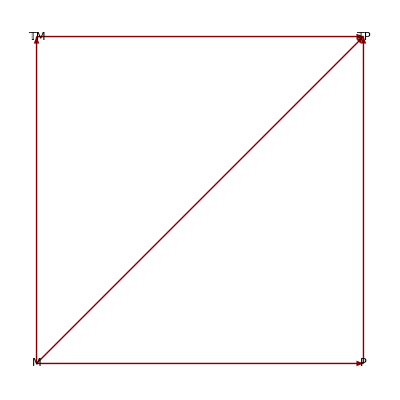

```mathematica
LayeredGraphPlot[{
{Style["M",Large]->Style["P",Large],Style["ϕ",Large]},
{Style["M",Large]->Style["𝕋M",Large],Style["v",Large]},
{Style["𝕋M",Large]->Style["𝕋P",Large],Style["dϕ",Large]},
{Style["P",Large]->Style["𝕋P",Large],Style["W",Large]},
{Style["M",Large]->Style["𝕋P",Large],Style["dϕ·v or W∘ϕ",Large]}
},
VertexLabeling->True,FormatType->StandardForm,
VertexCoordinateRules->{{0,0},{1,0},{0,1},{1,1}}
]/.Network`GraphPlot`wrapper->Identity
```

## 9. More on rules

### 9.1. MakeRule

Defining rules is one of the most important components of a tensor package. The function IndexRule takes care of dummy generation, but there are other points to consider when defining a rule:
	1. Checking consistency between left and right hand sides.
	2. Defining rules that work only for a given vbundle.
	3. Extending the rule to pattern expressions with equivalent index-structure under symmetries.
	4. Extendig the rule to patterns with a different up/down character if metrics are present.
We define the function MakeRule, which takes care of all these things. Note that there is not a parallel function for Set, but below we present a way to automatize a collection of rules.

MakeRule				Construct rules between xTensor` expressions
AutomaticRules			Automatize rules

Construction of rules.

Define again the environment for examples. This time we quite the info messages:

```mathematica
$DefInfoQ=False;
```

```mathematica
DefManifold[M3,3,{a,b,c,d,e,f,g,h}]
DefManifold[S2,2,{A,B,C,D}]//Quiet
DefMetric[-1,metricg[-a,-b],CD,PrintAs->"g"]
DefTensor[v[a],M3]
DefTensor[T[a,b],M3]
DefTensor[U[-a,-b,-c],M3,Antisymmetric[{1,2,3}]]
```

```mathematica
$PrePrint=ScreenDollarIndices;
```

The simplest way to define a rule would easily give corrupted answers:

```mathematica
rule=v[a_]->T[a,-b]v[b]
```

v | a̲
 →T | a |  
  | b v | b

```mathematica
v[b]/.rule
```

Validate::repeated: Found indices with the same name b.

Throw::nocatch: Uncaught Throw[Null] returned to top level.

Hold[Throw[Null]]

We have seen that changing to IndexRule we can solve those problems (underlined indices denote patterns):

```mathematica
rule=v[a_]↦T[a,b]v[-b]
```

HoldPattern[v | a̲
 ]:>Module[{b},T | a | b
  |   v |  
b]

```mathematica
v[b]/.rule
```

T | b | a
  |   v |  
a

```mathematica
%/.rule
```

T |   | c
a |   T | b | a
  |   v |  
c

We can also define the same rule using MakeRule. Note that there is no pattern on the lhs; by default all indices on the LHS are converted into patterns:

```mathematica
rule=MakeRule[{v[a],T[a,-b]v[b]},MetricOn->None]
```

{HoldPattern[v | UnderBar[a̲]
 ]:>Module[{b},T | a |  
  | b v | b
 ]}

```mathematica
T[-a,-b]v[a]v[b]/.rule
```

T |   |  
a | b T | a |  
  | c T | b |  
  | d v | c
  v | d

```mathematica
InputForm[rule]
```

{HoldPattern[v[(a_Symbol)?TangentM3`Q]] :> Module[{h$44689}, T[a, -h$44689]*v[h$44689]]}

Due to the option TestIndices→True, membership of the indices of the LHS is checked. The function M3`Q checks that an up-index belongs to M3, but it does not accept down-indices (this is due to the option MetricOn->None):

```mathematica
v[a]/.rule
```

T | a |  
  | b v | b

```mathematica
v[-a]/.rule
```

v |  
a

```mathematica
v[A]/.rule
```

v | A

In order to allow both up/down-indices of a given vbundle we use MetricOn. We need to have a metric first. (If the vbundle of the index did not have a metric MakeRule would refuse to change the up/down character):

```mathematica
rule=MakeRule[{v[a],T[a,-b]v[b]},MetricOn->{a},ContractMetrics->True]
```

{HoldPattern[v | UnderBar[a̲]
 ]:>Module[{b},T | a |  
  | b v | b
 ]}

```mathematica
InputForm[rule]
```

{HoldPattern[v[(a_)?TangentM3`pmQ]] :> Module[{h$44706}, T[a, -h$44706]*v[h$44706]]}

```mathematica
v[a]/.rule
```

T | a |  
  | b v | b

```mathematica
v[-a]/.rule
```

T |   |  
a | b v | b

If we have symmetries the situation gets even more complicated:

```mathematica
(rule=MakeRule[{U[a,b,c]v[-c],v[a]T[b]-v[b]T[a]},MetricOn->All,ContractMetrics->True])
```

{HoldPattern[U | UnderBar[a̲] | UnderBar[b̲] | UnderBar[c̲]
  |   |   v |  
UnderBar[c̲]]:>Module[{},T | b
  v | a
 -T | a
  v | b
 ],HoldPattern[U | UnderBar[a̲] | UnderBar[b̲] |  
  |   | UnderBar[c̲] v | UnderBar[c̲]
 ]:>Module[{},T | b
  v | a
 -T | a
  v | b
 ],HoldPattern[U | UnderBar[a̲] | UnderBar[c̲] | UnderBar[b̲]
  |   |   v |  
UnderBar[c̲]]:>Module[{},-T | b
  v | a
 +T | a
  v | b
 ],HoldPattern[U | UnderBar[a̲] |   | UnderBar[b̲]
  | UnderBar[c̲] |   v | UnderBar[c̲]
 ]:>Module[{},-T | b
  v | a
 +T | a
  v | b
 ],HoldPattern[U | UnderBar[b̲] | UnderBar[c̲] | UnderBar[a̲]
  |   |   v |  
UnderBar[c̲]]:>Module[{},T | b
  v | a
 -T | a
  v | b
 ],HoldPattern[U | UnderBar[b̲] |   | UnderBar[a̲]
  | UnderBar[c̲] |   v | UnderBar[c̲]
 ]:>Module[{},T | b
  v | a
 -T | a
  v | b
 ],HoldPattern[U | UnderBar[c̲] | UnderBar[a̲] | UnderBar[b̲]
  |   |   v |  
UnderBar[c̲]]:>Module[{},T | b
  v | a
 -T | a
  v | b
 ],HoldPattern[U |   | UnderBar[a̲] | UnderBar[b̲]
UnderBar[c̲] |   |   v | UnderBar[c̲]
 ]:>Module[{},T | b
  v | a
 -T | a
  v | b
 ],HoldPattern[U | UnderBar[c̲] | UnderBar[b̲] | UnderBar[a̲]
  |   |   v |  
UnderBar[c̲]]:>Module[{},-T | b
  v | a
 +T | a
  v | b
 ],HoldPattern[U |   | UnderBar[b̲] | UnderBar[a̲]
UnderBar[c̲] |   |   v | UnderBar[c̲]
 ]:>Module[{},-T | b
  v | a
 +T | a
  v | b
 ]}

```mathematica
U[-a,b,c]v[-b]/.rule
```

-T | c
  v |  
a+T |  
a v | c

```mathematica
U[-a,b,c]v[a]/.rule
```

T | c
  v | b
 -T | b
  v | c

```mathematica
U[-a,c,-c]v[a]/.rule//ToCanonical
```

0

It is possible to automate rules, declaring them as definitions for a symbol, in this case the tensor U:

```mathematica
AutomaticRules[U,rule]
```

Rules {1,2,3,4,5,6,7,8,9,10} have been declared as UpValues for U.

```mathematica
U[-a,b,c]v[-b]
```

-T | c
  v |  
a+T |  
a v | c

```mathematica
U[-a,b,c]v[a]
```

T | c
  v | b
 -T | b
  v | c

```mathematica
?U
```

Global`U

Dagger[U]^:=U
 
DefInfo[U]^:={tensor,}
 
DependenciesOfTensor[U]^:={M3}
 
HostsOf[U]^:={M3,𝕋M3}
 
PrintAs[U]^:=U
 
SlotsOfTensor[U]^:={-𝕋M3,-𝕋M3,-𝕋M3}
 
SymmetryGroupOfTensor[U]^:=StrongGenSet[{1,2,3},GenSet[-(1,2),-(2,3)]]
 
TensorID[U]^:={}
 
xTensorQ[U]^:=True
 
U/:U | UnderBar[a̲] | UnderBar[b̲] | UnderBar[c̲]
  |   |   v |  
UnderBar[c̲]:=Module[{},T | b
  v | a
 -T | a
  v | b
 ]
 
U/:U | UnderBar[a̲] | UnderBar[b̲] |  
  |   | UnderBar[c̲] v | UnderBar[c̲]
 :=Module[{},T | b
  v | a
 -T | a
  v | b
 ]
 
U/:U | UnderBar[a̲] | UnderBar[c̲] | UnderBar[b̲]
  |   |   v |  
UnderBar[c̲]:=Module[{},-T | b
  v | a
 +T | a
  v | b
 ]
 
U/:U | UnderBar[a̲] |   | UnderBar[b̲]
  | UnderBar[c̲] |   v | UnderBar[c̲]
 :=Module[{},-T | b
  v | a
 +T | a
  v | b
 ]
 
U/:U | UnderBar[b̲] | UnderBar[c̲] | UnderBar[a̲]
  |   |   v |  
UnderBar[c̲]:=Module[{},T | b
  v | a
 -T | a
  v | b
 ]
 
U/:U | UnderBar[b̲] |   | UnderBar[a̲]
  | UnderBar[c̲] |   v | UnderBar[c̲]
 :=Module[{},T | b
  v | a
 -T | a
  v | b
 ]
 
U/:U | UnderBar[c̲] | UnderBar[a̲] | UnderBar[b̲]
  |   |   v |  
UnderBar[c̲]:=Module[{},T | b
  v | a
 -T | a
  v | b
 ]
 
U/:U |   | UnderBar[a̲] | UnderBar[b̲]
UnderBar[c̲] |   |   v | UnderBar[c̲]
 :=Module[{},T | b
  v | a
 -T | a
  v | b
 ]
 
U/:U | UnderBar[c̲] | UnderBar[b̲] | UnderBar[a̲]
  |   |   v |  
UnderBar[c̲]:=Module[{},-T | b
  v | a
 +T | a
  v | b
 ]
 
U/:U |   | UnderBar[b̲] | UnderBar[a̲]
UnderBar[c̲] |   |   v | UnderBar[c̲]
 :=Module[{},-T | b
  v | a
 +T | a
  v | b
 ]

The simplest way to remove those definitions for U is removing the tensor and defining it again:

```mathematica
UndefTensor[U]
```

** UndefTensor: Undefined tensor U

```mathematica
DefTensor[U[-a,-b,-c],M3,Antisymmetric[{1,2,3}]]
```

### 9.2. Riemann expressions

As we said, there is no algorithm at present in xTensor` to canonicalize expressions with multiterm symmetries. That is an obstacle in GR when one wants to work with the Riemann tensor, which has a cyclic symmetry. A simple, brute-force, solution is to prepare a number of rules which are only valid for the Riemann tensor. We follow MathTensor's discussion of this point (see MathTensor book).
There are 48 rules in total, numbered from 1 to 40, some of them having subcases a, b, c, ...
14 of those rules are simple consequences of the monoterm symmetries of the Riemann tensor, and hence can be considered already implemented in ToCanonical:

RiemannRule1:

```mathematica
RiemannCD[-a,a,-c,-d]//ToCanonical
```

0

```mathematica
RiemannCD[-a,-b,-c,c]//ToCanonical
```

0

RiemannRule2:

```mathematica
RiemannCD[-a,-b,a,-d]//ToCanonical
```

R[▽] |   |  
b | d

RiemannRule3:

```mathematica
RiemannCD[-a,-b,-c,a]//ToCanonical
```

-R[▽] |   |  
b | c

RiemannRule4:

```mathematica
RiemannCD[-a,-b,b,-d]//ToCanonical
```

-R[▽] |   |  
a | d

RiemannRule5:

```mathematica
RiemannCD[-a,-b,-c,b]//ToCanonical
```

R[▽] |   |  
a | c

RiemannRule6:

```mathematica
RiemannCD[-a,-b,-c,-d]RicciCD[a,b]//ToCanonical
```

0

```mathematica
RiemannCD[-a,-b,-c,-d]RicciCD[c,d]//ToCanonical
```

0

RiemannRule31:

```mathematica
CD[-e]@RiemannCD[-a,-b,-c,-d]RicciCD[a,b]//ToCanonical
```

0

```mathematica
CD[-e]@RiemannCD[-a,-b,-c,-d]RicciCD[c,d]//ToCanonical
```

0

RiemannRule32:

```mathematica
CD[-e]@RiemannCD[-a,-b,-c,-d]CD[-f]@RicciCD[a,b]//ToCanonical
```

0

```mathematica
CD[-e]@RiemannCD[-a,-b,-c,-d]CD[-f]@RicciCD[c,d]//ToCanonical
```

0

RiemannRule33:

```mathematica
CD[-c]@RicciCD[-a,-b]RiemannCD[a,b,d,e]//ToCanonical
```

0

```mathematica
CD[-c]@RicciCD[-a,-b]RiemannCD[d,e,a,b]//ToCanonical
```

0

There are 2 more rules which can be obtained from the fact that the Einstein tensor is divergence free:

RiemannRule16:

```mathematica
CD[b][RicciCD[-a,-b]]//RicciToEinstein//ContractMetric
```

(▽_a R[▽])/2

RiemannRule17:

```mathematica
CD[a][RicciCD[-a,-b]]//RicciToEinstein//ContractMetric
```

(▽_b R[▽])/2

The other 32 rules are actual consequences of the cyclic symmetry of the Riemann tensor, and therefore must be programmed independently. Using MakeRule we can avoid typing equivalent rules (up to permutations of indices), reducing the number to 17 independent rules.
We first study 13 rules having derivatives of a single curvature tensor on the LHS. They are in fact only 6 independent rules:
	RuleDivRiemann
	RuleDivGradRicci
	RuleBoxRiemann
	RuleDivGradRiemann
	RuleD4RicciScalar
	RuleD4Ricci

The four rules 20--23 are all the same:

```mathematica
RuleDivRiemann=MakeRule[{CD[a]@RiemannCD[-a,-b,-c,-d],-CD[-d]@RicciCD[-b,-c]+CD[-c]@RicciCD[-b,-d]},UseSymmetries->True,MetricOn->All];
```

RiemannRule20:

```mathematica
CD[a]@RiemannCD[-a,-b,-c,-d]/.RuleDivRiemann
```

▽_c R[▽] |   |  
b | d-▽_d R[▽] |   |  
b | c

RiemannRule21:

```mathematica
CD[b]@RiemannCD[-a,-b,-c,-d]/.RuleDivRiemann
```

-(▽_c R[▽] |   |  
a | d)+▽_d R[▽] |   |  
a | c

RiemannRule22:

```mathematica
CD[c]@RiemannCD[-a,-b,-c,-d]/.RuleDivRiemann
```

▽_a R[▽] |   |  
d | b-▽_b R[▽] |   |  
d | a

RiemannRule23:

```mathematica
CD[d]@RiemannCD[-a,-b,-c,-d]/.RuleDivRiemann
```

-(▽_a R[▽] |   |  
c | b)+▽_b R[▽] |   |  
c | a

Create more indices:

```mathematica
GetIndicesOfVBundle[TangentM3,14]
```

{a,b,c,d,e,f,g,h,h1,h2,h3,h4,h5,h6}

Two rules with second derivatives of Ricci can be combined in a single rule:

```mathematica
RuleDivGradRicci=MakeRule[{CD[b]@CD[-c]@RicciCD[-a,-b],1/2CD[-c]@CD[-a]@RicciScalarCD[]+RicciCD[-h1,-a]RicciCD[-c,h1]-RicciCD[-h1,-h2]RiemannCD[-a,h2,-c,h1]},UseSymmetries->True,MetricOn->All];
```

RiemannRule18:

```mathematica
CD[b]@CD[-c]@RicciCD[-a,-b]/.RuleDivGradRicci
```

R[▽] |   |  
b | a R[▽] |   | b
c |  -R[▽] |   |  
b | d R[▽] |   | d |   | b
a |   | c |  +1/2 (▽_c▽_a R[▽])

RiemannRule19:

```mathematica
CD[a]@CD[-c]@RicciCD[-a,-b]/.RuleDivGradRicci
```

R[▽] |   |  
a | b R[▽] |   | a
c |  -R[▽] |   |  
a | d R[▽] |   | d |   | a
b |   | c |  +1/2 (▽_c▽_b R[▽])

Rules 26 to 30 are now two rules in xTensor`:

```mathematica
RuleBoxRiemann=MakeRule[{CD[e]@CD[-e]@RiemannCD[-a,-b,-c,-d],
CD[-b]@CD[-d]@RicciCD[-a,-c]-CD[-b]@CD[-c]@RicciCD[-a,-d]-
CD[-a]@CD[-d]@RicciCD[-b,-c]+CD[-a]@CD[-c]@RicciCD[-b,-d]+
RicciCD[-h1,-b]RiemannCD[-a,h1,-c,-d]-
RicciCD[-h1,-a]RiemannCD[-b,h1,-c,-d]-
RiemannCD[-h1,-h2,-c,-d]RiemannCD[-a,h1,-b,h2]-
RiemannCD[-h1,-b,-h2,-d]RiemannCD[-a,h1,-c,h2]+
RiemannCD[-h1,-b,-h2,-c]RiemannCD[-a,h1,-d,h2]+RiemannCD[-h1,-a,-h2,-d]RiemannCD[-b,h1,-c,h2]-RiemannCD[-h1,-a,-h2,-c]RiemannCD[-b,h1,-d,h2]-
RiemannCD[-h1,-a,-h2,-b]RiemannCD[-c,-d,h1,h2]},UseSymmetries->True,MetricOn->All];
```

```mathematica
RuleDivGradRiemann=MakeRule[{CD[a]@CD[-e]@RiemannCD[-a,-b,-c,-d],-CD[-e]@CD[-d]@RicciCD[-b,-c]+CD[-e]@CD[-c]@RicciCD[-b,-d]-RicciCD[-h1,-e]RiemannCD[-b,h1,-c,-d]+RiemannCD[-h1,-h2,-c,-d]RiemannCD[-b,h1,-e,h2]-RiemannCD[-h1,-b,-h2,-d]RiemannCD[-c,h2,-e,h1]+RiemannCD[-h1,-b,-h2,-c]RiemannCD[-d,h2,-e,h1]},UseSymmetries->True,MetricOn->All];
```

RiemannRule26:

```mathematica
CD[e]@CD[-e]@RiemannCD[-a,-b,-c,-d]/.RuleBoxRiemann
```

R[▽] |   |  
e | b R[▽] |   | e |   |  
a |   | c | d-R[▽] |   |  
e | a R[▽] |   | e |   |  
b |   | c | d-R[▽] |   |   | e | f
c | d |   |   R[▽] |   |   |   |  
e | a | f | b-R[▽] |   | e |   | f
b |   | d |   R[▽] |   |   |   |  
e | a | f | c+R[▽] |   | e |   | f
b |   | c |   R[▽] |   |   |   |  
e | a | f | d+R[▽] |   | e |   | f
a |   | d |   R[▽] |   |   |   |  
e | b | f | c-R[▽] |   | e |   | f
a |   | c |   R[▽] |   |   |   |  
e | b | f | d-R[▽] |   | e |   | f
a |   | b |   R[▽] |   |   |   |  
e | f | c | d+▽_a▽_c R[▽] |   |  
b | d-▽_a▽_d R[▽] |   |  
b | c-▽_b▽_c R[▽] |   |  
a | d+▽_b▽_d R[▽] |   |  
a | c

RiemannRule27:

```mathematica
CD[a]@CD[-e]@RiemannCD[-a,-b,-c,-d]/.RuleDivGradRiemann
```

-R[▽] |   |  
a | e R[▽] |   | a |   |  
b |   | c | d+R[▽] |   |   |   |  
a | f | c | d R[▽] |   | a |   | f
b |   | e |  -R[▽] |   |   |   |  
a | b | f | d R[▽] |   | f |   | a
c |   | e |  +R[▽] |   |   |   |  
a | b | f | c R[▽] |   | f |   | a
d |   | e |  +▽_e▽_c R[▽] |   |  
b | d-▽_e▽_d R[▽] |   |  
b | c

RiemannRule28:

```mathematica
CD[b]@CD[-e]@RiemannCD[-a,-b,-c,-d]/.RuleDivGradRiemann
```

R[▽] |   |  
b | e R[▽] |   | b |   |  
a |   | c | d-R[▽] |   | b |   | f
a |   | e |   R[▽] |   |   |   |  
b | f | c | d+R[▽] |   |   |   |  
b | a | f | d R[▽] |   | f |   | b
c |   | e |  -R[▽] |   |   |   |  
b | a | f | c R[▽] |   | f |   | b
d |   | e |  -▽_e▽_c R[▽] |   |  
a | d+▽_e▽_d R[▽] |   |  
a | c

RiemannRule29:

```mathematica
CD[c]@CD[-e]@RiemannCD[-a,-b,-c,-d]/.RuleDivGradRiemann
```

R[▽] |   | f |   | c
b |   | e |   R[▽] |   |   |   |  
c | d | f | a-R[▽] |   | f |   | c
a |   | e |   R[▽] |   |   |   |  
c | d | f | b-R[▽] |   |  
c | e R[▽] |   | c |   |  
d |   | a | b+R[▽] |   |   |   |  
c | f | a | b R[▽] |   | c |   | f
d |   | e |  +▽_e▽_a R[▽] |   |  
d | b-▽_e▽_b R[▽] |   |  
d | a

RiemannRule30:

```mathematica
CD[d]@CD[-e]@RiemannCD[-a,-b,-c,-d]/.RuleDivGradRiemann
```

R[▽] |   |  
d | e R[▽] |   | d |   |  
c |   | a | b-R[▽] |   | f |   | d
b |   | e |   R[▽] |   |   |   |  
d | c | f | a+R[▽] |   | f |   | d
a |   | e |   R[▽] |   |   |   |  
d | c | f | b-R[▽] |   | d |   | f
c |   | e |   R[▽] |   |   |   |  
d | f | a | b-▽_e▽_a R[▽] |   |  
c | b+▽_e▽_b R[▽] |   |  
c | a

Fourth derivative of the Ricci scalar: conversion to Box^2:

```mathematica
RuleD4RicciScalar=MakeRule[{CD[b]@CD[a]@CD[-b]@CD[-a]@RicciScalarCD[],1/2CD[-h1]@RicciScalarCD[]CD[h1]@RicciScalarCD[]+CD[h2]@CD[-h2]@CD[h1]@CD[-h1]@RicciScalarCD[]+CD[-h2]@CD[-h1]@RicciScalarCD[]RicciCD[h1,h2]},UseSymmetries->True,MetricOn->All];
```

RiemannRule24:

```mathematica
CD[b]@CD[a]@CD[-b]@CD[-a]@RicciScalarCD[]/.RuleD4RicciScalar
```

1/2 (▽_a R[▽]) (▽^a R[▽])+R[▽] | a | b
  |   (▽_b▽_a R[▽])+▽^b▽_b▽^a▽_a R[▽]

Fourth derivative of the Ricci tensor:

```mathematica
RuleD4Ricci=MakeRule[{CD[b]@CD[a]@CD[c]@CD[-c]@RicciCD[-a,-b],1/2CD[-h1]@RicciScalarCD[]CD[h1]@RicciScalarCD[]-3CD[-h3]@RicciCD[-h1,-h2]CD[h3]@RicciCD[h1,h2]+4CD[-h3]@RicciCD[-h1,-h2]CD[h2]@RicciCD[h1,h3]+1/2CD[h2]@CD[-h2]@CD[h1]@CD[-h1]@RicciScalarCD[]+2CD[-h2]@CD[-h1]@RicciScalarCD[]RicciCD[h1,h2]-CD[h3]@CD[-h3]@RicciCD[-h1,-h2]RicciCD[h1,h2]+2RicciCD[-h1,-h2]RicciCD[-h3,h1]RicciCD[h2,h3]-2CD[-h4]@CD[-h3]@RicciCD[-h1,-h2]RiemannCD[h1,h3,h2,h4]-2RicciCD[-h1,-h2]RicciCD[-h3,-h4]RiemannCD[h1,h3,h2,h4]},UseSymmetries->True,MetricOn->All];
```

RiemannRule25:

```mathematica
CD[b]@CD[a]@CD[c]@CD[-c]@RicciCD[-a,-b]/.RuleD4Ricci
```

2 R[▽] |   |  
a | b R[▽] | b | c
  |   R[▽] |   | a
c |  -2 R[▽] |   |  
a | b R[▽] |   |  
c | d R[▽] | a | c | b | d
  |   |   |  +1/2 (▽_a R[▽]) (▽^a R[▽])+2 R[▽] | a | b
  |   (▽_b▽_a R[▽])+1/2 (▽^b▽_b▽^a▽_a R[▽])+4 (▽^b R[▽] | a | c
  |  ) (▽_c R[▽] |   |  
a | b)-3 (▽_c R[▽] |   |  
a | b) (▽^c R[▽] | a | b
  |  )-R[▽] | a | b
  |   (▽^c▽_c R[▽] |   |  
a | b)-2 R[▽] | a | c | b | d
  |   |   |   (▽_d▽_c R[▽] |   |  
a | b)

Now we study six rules with products of two Riemann tensors on the LHS. There are only two different rules, depending on whether there are two or three contracted indices:
	RuleTwoRiemann3
	RuleTwoRiemann2

These are the independent rules:

```mathematica
RuleTwoRiemann3=MakeRule[{RiemannCD[-a,-b,-c,-d]RiemannCD[-e,a,b,c],-1/2RiemannCD[-f,-d,-g,-h]RiemannCD[-e,f,g,h]},UseSymmetries->True,MetricOn->All];
```

```mathematica
RuleTwoRiemann2=MakeRule[{RiemannCD[-a,-b,-c,-d]RiemannCD[-e,a,-g,b],1/2RiemannCD[-f,-h,-c,-d]RiemannCD[-e,-g,f,h]},UseSymmetries->True,MetricOn->All];
```

RiemannRule7:

```mathematica
RiemannCD[-a,-b,-c,-d]RiemannCD[-e,a,b,c]/.RuleTwoRiemann3
```

-1/2 R[▽] |   |   |   |  
a | d | b | c R[▽] |   | a | b | c
e |   |   |

RiemannRule8:

```mathematica
RiemannCD[-a,-b,-c,-d]RiemannCD[a,c,b,h]/.RuleTwoRiemann3
```

-1/2 g | h | e
  |   R[▽] |   |   |   |  
a | d | b | c R[▽] |   | a | b | c
e |   |   |

RiemannRule9a:

```mathematica
RiemannCD[-a,-b,-c,-d]RiemannCD[-e,a,-g,b]/.RuleTwoRiemann2
```

1/2 R[▽] |   |   |   |  
a | b | c | d R[▽] |   |   | a | b
e | g |   |

RiemannRule9b:

```mathematica
RiemannCD[-a,-b,-c,-d]RiemannCD[e,a,b,h]/.RuleTwoRiemann2
```

-1/2 g | e | f
  |   g | h | g
  |   R[▽] |   |   |   |  
a | b | c | d R[▽] |   |   | a | b
f | g |   |

RiemannRule9c:

```mathematica
RiemannCD[-a,-b,-c,-d]RiemannCD[a,f,b,h]/.RuleTwoRiemann2
```

1/2 g | f | e
  |   g | h | g
  |   R[▽] |   |   |   |  
a | b | c | d R[▽] |   |   | a | b
e | g |   |

RiemannRule9d:

```mathematica
RiemannCD[-a,-b,-c,-d]RiemannCD[a,f,g,b]/.RuleTwoRiemann2
```

-1/2 g | f | e
  |   g | g | h
  |   R[▽] |   |   |   |  
a | b | c | d R[▽] |   |   | a | b
e | h |   |

There are seven more rules involving two curvature tensors and derivatives, corresponding to five independent rules:
	RuleD01TwoRiemann
	RuleD11TwoRiemann
	RuleD2RicciRiemann
	RuleD2RicciDRiemann
	RuleD11bisTwoRiemann

```mathematica
RuleD01TwoRiemann=MakeRule[{CD[-e]@RiemannCD[a,f,b,c]RiemannCD[-a,-b,-c,-d],-1/2CD[-e]@RiemannCD[h1,f,h2,h3]RiemannCD[-h1,-d,-h2,-h3]},UseSymmetries->True,MetricOn->All];
```

```mathematica
RuleD11TwoRiemann=MakeRule[{CD[-e]@RiemannCD[-a,-b,-c,-d]CD[-f]@RiemannCD[a,g,b,c],-1/2CD[-e]@RiemannCD[-h1,-d,-h2,-h3]CD[-f]@RiemannCD[h1,g,h2,h3]},UseSymmetries->True,MetricOn->All];
```

```mathematica
RuleD2RicciRiemann=MakeRule[{CD[-d]@CD[-c]@RicciCD[-a,-b]RiemannCD[a,d,b,c],CD[-h4]@CD[-h3]@RicciCD[-h1,-h2]RiemannCD[h1,h3,h2,h4]},UseSymmetries->True,MetricOn->All];
```

```mathematica
RuleD2RicciDRiemann=MakeRule[{CD[-e]@RiemannCD[a,d,b,c]CD[-d]@CD[-c]@RicciCD[-a,-b],CD[-e]@RiemannCD[h1,h2,h3,h4]CD[-h4]@CD[-h2]@RicciCD[-h1,-h3]},UseSymmetries->True,MetricOn->All];
```

This rule has a typo in MathTensor's book. I assume the index c on the RHS is actually f:

```mathematica
RuleD11bisTwoRiemann=MakeRule[{CD[-g]@RiemannCD[-a,-b,-c,-d]CD[g]@RiemannCD[c,e,d,f],1/2CD[-h3]@RiemannCD[-h1,-h2,-a,-b]CD[h3]@RiemannCD[h1,h2,f,e]},UseSymmetries->True,MetricOn->All];
```

RiemannRule34:

```mathematica
CD[-e]@RiemannCD[a,f,b,c]RiemannCD[-a,-b,-c,-d]/.RuleD01TwoRiemann
```

-1/2 R[▽] |   |   |   |  
a | d | b | c (▽_e R[▽] | a | f | b | c
  |   |   |  )

RiemannRule35:

```mathematica
CD[-e]@RiemannCD[-a,-b,-c,-d]CD[-f]@RiemannCD[a,g,b,c]/.RuleD11TwoRiemann
```

-1/2 (▽_e R[▽] |   |   |   |  
a | d | b | c) (▽_f R[▽] | a | g | b | c
  |   |   |  )

RiemannRule36:

```mathematica
CD[-e]@RiemannCD[a,c,b,f]RiemannCD[-a,-b,-c,-d]/.RuleD01TwoRiemann
```

1/2 R[▽] |   |   |   |  
a | d | b | c (▽_e R[▽] | a | f | b | c
  |   |   |  )

RiemannRule37:

```mathematica
CD[-e]@RiemannCD[-a,-b,-c,-d]CD[-f]@RiemannCD[a,c,b,g]/.RuleD11TwoRiemann
```

1/2 (▽_e R[▽] |   |   |   |  
a | d | b | c) (▽_f R[▽] | a | g | b | c
  |   |   |  )

RiemannRule38:

```mathematica
CD[-g]@RiemannCD[-a,-b,-c,-d]CD[g]@RiemannCD[c,e,d,f]/.RuleD11bisTwoRiemann
```

1/2 (▽_g R[▽] |   |   |   |  
c | d | a | b) (▽^g R[▽] | c | d | f | e
  |   |   |  )

RiemannRule39:

```mathematica
CD[-e]@RiemannCD[a,d,b,c]CD[-d]@CD[-c]@RicciCD[-a,-b]/.RuleD2RicciDRiemann
```

(▽_d▽_b R[▽] |   |  
a | c) (▽_e R[▽] | a | b | c | d
  |   |   |  )

RiemannRule40:

```mathematica
CD[-d]@CD[-c]@RicciCD[-a,-b]RiemannCD[a,d,b,c]/.RuleD2RicciRiemann
```

R[▽] | a | c | b | d
  |   |   |   (▽_d▽_c R[▽] |   |  
a | b)

Finally we study six rules with products of three curvature tensors, only four of which are independent:
	RuleRicciTwoRiemann
	RuleThreeRiemann
	RuleThreeRiemannB
	RuleThreeRiemannC

Constructing the independent rules takes rather long because there are lots of equivalent cases:

```mathematica
AbsoluteTiming[Length[RuleRicciTwoRiemann=MakeRule[{RicciCD[-a,-b]RiemannCD[-c,-d,-e,a]RiemannCD[b,c,d,e],-1/2RicciCD[-h1,-h2]RiemannCD[-h3,-h4,-h5,h1]RiemannCD[h2,h5,h3,h4]},UseSymmetries->True,MetricOn->All]]]
```

{6.0632,4096}

```mathematica
AbsoluteTiming[Length[RuleThreeRiemann=MakeRule[{RiemannCD[-a,-b,-c,-d]RiemannCD[-e,-f,a,b]RiemannCD[c,e,d,f],1/2RiemannCD[-h1,-h2,-h3,-h4]RiemannCD[-h5,-h6,h1,h2]RiemannCD[h3,h4,h5,h6]},UseSymmetries->True,MetricOn->All]]]
```

{63.8858,32768}

```mathematica
AbsoluteTiming[Length[RuleThreeRiemannB=MakeRule[{RiemannCD[-a,-b,-c,-d]RiemannCD[-e,a,-f,b]RiemannCD[c,e,d,f],1/4RiemannCD[-h1,-h2,-h3,-h4]RiemannCD[-h5,-h6,h3,h4]RiemannCD[h1,h2,h5,h6]},UseSymmetries->True,MetricOn->All]]]
```

{63.8929,32768}

```mathematica
AbsoluteTiming[Length[RuleThreeRiemannC=MakeRule[{RiemannCD[-a,-b,-c,-d]RiemannCD[-e,a,-f,c]RiemannCD[b,f,d,e],RiemannCD[-h1,-h2,-h3,-h4]RiemannCD[-h5,h1,-h6,h3]RiemannCD[h2,h5,h4,h6]-1/4RiemannCD[-h1,-h2,-h3,-h4]RiemannCD[-h5,-h6,h1,h2]RiemannCD[h3,h4,h5,h6]},UseSymmetries->True,MetricOn->All]]]
```

{103.372,32768}

RiemannRule10:

```mathematica
RicciCD[-a,-b]RiemannCD[-c,-d,-e,a]RiemannCD[b,c,d,e]/.RuleRicciTwoRiemann
```

-1/2 R[▽] |   |  
a | b R[▽] | b | e | c | d
  |   |   |   R[▽] |   |   |   | a
c | d | e |

RiemannRule11:

```mathematica
RiemannCD[-a,-b,-c,-d]RiemannCD[-e,-f,a,b]RiemannCD[c,e,d,f]/.RuleThreeRiemann
```

1/2 R[▽] |   |   |   |  
a | b | c | d R[▽] | c | d | e | f
  |   |   |   R[▽] |   |   | a | b
e | f |   |

RiemannRule12:

```mathematica
RiemannCD[-a,-b,-c,-d]RiemannCD[-e,a,-f,b]RiemannCD[c,e,d,f]/.RuleThreeRiemannB
```

1/4 R[▽] |   |   |   |  
a | b | c | d R[▽] | a | b | e | f
  |   |   |   R[▽] |   |   | c | d
e | f |   |

RiemannRule13:

```mathematica
RiemannCD[-a,-b,-c,-d]RiemannCD[-e,a,-f,b]RiemannCD[c,d,e,f]/.RuleThreeRiemann
```

1/2 R[▽] |   |   |   |  
a | b | c | d R[▽] | c | d | e | f
  |   |   |   R[▽] |   |   | a | b
e | f |   |

RiemannRule14:

```mathematica
RiemannCD[-a,-b,-c,-d]RiemannCD[-e,a,-f,c]RiemannCD[b,d,e,f]/.RuleThreeRiemannB
```

1/4 R[▽] |   |   |   |  
a | b | c | d R[▽] | a | b | e | f
  |   |   |   R[▽] |   |   | c | d
e | f |   |

RiemannRule15:

```mathematica
RiemannCD[-a,-b,-c,-d]RiemannCD[-e,a,-f,c]RiemannCD[b,f,d,e]/.RuleThreeRiemannC
```

R[▽] |   |   |   |  
a | b | c | d R[▽] | b | e | d | f
  |   |   |   R[▽] |   | a |   | c
e |   | f |  -1/4 R[▽] |   |   |   |  
a | b | c | d R[▽] | c | d | e | f
  |   |   |   R[▽] |   |   | a | b
e | f |   |

Remove rules:

```mathematica
Remove[RuleBoxRiemann,RuleD01TwoRiemann,RuleD11bisTwoRiemann,RuleD11TwoRiemann,RuleD2RicciDRiemann,RuleD2RicciRiemann,RuleD4Ricci,RuleD4RicciScalar,RuleDivGradRicci,RuleDivGradRiemann,RuleDivRiemann,RuleRicciTwoRiemann,RuleThreeRiemann,RuleThreeRiemannB,RuleThreeRiemannC,RuleTwoRiemann2,RuleTwoRiemann3]
```

## 10. Manipulation of expressions

### 10.1. Find indices

Given an expression, very often we want to extract all indices of the expression, or those of certain type, or character or state. We have already seen how to select indices of any type and any character. In this subsection we shall define functions to extract all indices according to a number of ` `selectors.b4 .b4.
There are two sets of functions. There is first the internal function FindIndices, which returns all indices of an expression, without first evaluating it, and its relatives FindFreeIndices, FindDummyIndices and FindBlockedIndices. There is then the user driver for finding indices, called IndicesOf, which admits a number of criteria for index selection, and evaluates its input (as the user typically expects).

Define some more objects:

```mathematica
DefTensor[r[],M3]
DefTensor[S[LI[_],a,b],M3,Symmetric[{2,3}]]
DefTensor[n[a],M3]
```

```mathematica
$DefInfoQ=True;
```

Let us start with this expression

```mathematica
expr=4T[a,b,-c,Dir[v[d]]]v[-a]r[]^2CD[-e][S[LI[1],-b,d]]
```

4 r^2 T | a | b |   |  
  |   | c | v v |  
a (▽_e S | 1 |   | d
  | b |  )

The three Find*Indices functions have attribute HoldFirst, and hence require the use of Evaluate when we do not feed the expression itself:

```mathematica
FindIndices[Evaluate[expr]]
```

{a, b, -c, Dir[v | d
 ], -a, LI[1], -b, d, -e}

```mathematica
FindFreeIndices[Evaluate[expr]]
```

{-c, d, -e}

```mathematica
FindDummyIndices[Evaluate[expr]]
```

{a, b}

```mathematica
FindBlockedIndices[Evaluate[expr]]
```

{Dir[v | d
 ], LI[1]}

This attribute is given to be able to extract indices of expressions before they get evaluated:

```mathematica
n/:n[a_]n[-a_]:=-1
```

```mathematica
n[a]n[-a]
```

-1

```mathematica
FindIndices[n[a]n[-a]]
```

{a, -a}

Note that the returned lists of indices have head IndexList, in order to avoid confusion with basis and component indices:

```mathematica
InputForm[%]
```

IndexList[a, -a]

FindIndices				Get all indices of an expression
FindFreeIndices			Get all free indices of an expression
FindDummyIndices			Get all dummy indices of an expression
FindBlockedIndices				Get all blocked indices of an expression
IndexList				Head for a list of indices

Finding indices. Internal functions

Then we have the user driver, with two pairs of brackets:

With no selectors, we get all indices in the expression:

```mathematica
IndicesOf[][expr]
```

{a, b, -c, Dir[v | d
 ], -a, LI[1], -b, d, -e}

We can select indices by type:

```mathematica
IndicesOf[AIndex][expr]
```

{a, b, -c, -a, -b, d, -e}

```mathematica
IndicesOf[DIndex][expr]
```

{Dir[v | d
 ]}

```mathematica
IndicesOf[LIndex][expr]
```

{LI[1]}

or by character:

```mathematica
IndicesOf[Up][expr]
```

{a, b, LI[1], d}

```mathematica
IndicesOf[Down][expr]
```

{-c, Dir[v | d
 ], -a, -b, -e}

or by state:

```mathematica
IndicesOf[Free][expr]
```

{-c, d, -e}

```mathematica
IndicesOf[Dummy][expr]
```

{-a, a, -b, b}

```mathematica
IndicesOf[Blocked][expr]
```

{Dir[v | d
 ], LI[1]}

We can also specify a vbundle (or a basis):

```mathematica
IndicesOf[TangentM3][expr]
```

{a, b, -c, Dir[v | d
 ], -a, -b, d, -e}

or a tensor:

```mathematica
IndicesOf[S][expr]
```

{-b, d, LI[1]}

We can combine several selectors, in two possible ways: a list of selectors represents the union, and a sequence represents the intersection.

Directions or labels:

```mathematica
IndicesOf[{DIndex,LIndex}][expr]
```

{Dir[v | d
 ], LI[1]}

Free indices on the tensor S:

```mathematica
IndicesOf[Free,S][expr]
```

{d}

Members of a selectors list are conmutative, but not members of a sequence: the construction of the final list is performed from left to right. Compare with the previous result:

```mathematica
IndicesOf[S,Free][expr]
```

{-b, d}

This powerful function is very flexible and has more possibilities once we allow the presence of bases (see xCobaDoc.nb).

IndicesOf				Get all indices of an expression according to a number of selecting criteria

Finding indices. User driver

### 10.2. Replace indices

A second, commonly required operation is the change of indices. In principle, the user should never need to replace indices directly in an expression. But sometimes it is needed, either because two expressions with different free indices must be compared, or to avoid problems with the dummy indices. This subsection introduces the basic function ReplaceIndex, and five more functions based on it.
Replacing indices is a basic critical operation: done without care would inmediately lead to wrong results. Whenever possible, we recommend the use of delta contractions to change indices, which is a safer and mathematically clearer operation.

Above all, avoid the temptation of changing indices using normal rules, unless you are sure that index-collisions will not appear.

ReplaceIndex			Replace an index by another index in an expression
ReplaceDummies		Replace dummy indices by new dummy indices
SameDummies			Minimize number of different dummy indices among several terms of a sum
ChangeFreeIndices		Change free indices of an expression
EqualExpressionsQ		Check whether two expressions are proportional to each other apart from a renaming of free indices
SplitIndex			Return a list of expressions where an index has been replace by different possibilities in a list
TraceDummy			Return a sum expressions where a dummy pair has been replace by different possibilities in a list

Index replacements.

Let us go back to our expression:

```mathematica
expr
```

4 r^2 T | a | b |   |  
  |   | c | v v |  
a (▽_e S | 1 |   | d
  | b |  )

For similar reasons, ReplaceIndex has attribute HoldFirst, and hence we need Evaluate. We can replace a single index:

```mathematica
ReplaceIndex[Evaluate[expr],a->f]
```

4 r^2 T | f | b |   |  
  |   | c | v v |  
a (▽_e S | 1 |   | d
  | b |  )

Note that the paired index -a has not been replaced. We need separate rules for that (this gives greater flexibility):

```mathematica
ReplaceIndex[Evaluate[expr],{a->f,-a->-f}]
```

4 r^2 T | f | b |   |  
  |   | c | v v |  
f (▽_e S | 1 |   | d
  | b |  )

We can change the character of an index, or even the type:

```mathematica
ReplaceIndex[Evaluate[expr],{a->-f,-a->f,Dir[v[d]]->LI[2]}]
```

4 r^2 T |   | b |   | 2
f |   | c |   v | f
  (▽_e S | 1 |   | d
  | b |  )

If the rules do not apply, nothing happens:

```mathematica
ReplaceIndex[Evaluate[expr],{f->a}]
```

4 r^2 T | a | b |   |  
  |   | c | v v |  
a (▽_e S | 1 |   | d
  | b |  )

Pattern indices can be changed, but this should never be required:

```mathematica
ReplaceIndex[T[a_],a->b]
```

T | b̲

The replacement is performed with great care. In the following list T is a tensor, but X is not a tensor:

```mathematica
ReplaceIndex[{a,T[a],T[-a],X[a]},a->b]
```

{a,T | b
 ,T |  
a,X[a]}

As I said, the user should try to refrain from using ReplaceIndex. If a free index must be changed, use contractions with delta tensors: if we want to change from T[a] to T[b] we can do this:

```mathematica
T[a]delta[-a,b]
```

T | b

In some cases we need to change the dummy indices of an expression. For example when we want to multiply a previous expression by itself. ReplaceDummies is the function which calls ReplaceIndex to manipulate all possible cases with dummies. A particular case, always required in the canonicalization process, is implemented in SameDummies.

Suppose now this scalar expression:

```mathematica
expr=T[a,b]T[-a,-b]
```

T |   |  
a | b T | a | b
  |

This is incorrect:

```mathematica
expr expr
```

(T |   |  
a | b)^2 (T | a | b
  |)^2

The following is correct. ReplaceDummies changes the dummy by the given indices

```mathematica
expr ReplaceDummies[expr,IndexList[e,f]]
```

T |   |  
a | b T | a | b
  |   T |   |  
e | f T | e | f
  |

If not enough indices (or no index at all) are given, the dummies are replaced by unique  dollar-indices:

```mathematica
expr ReplaceDummies[expr]
```

T |   |  
a | b T | a | b
  |   T |   |  
c | d T | c | d
  |

```mathematica
IndicesOf[][%]
```

{-a, -b, a, b, -h$46992, -h$46993, h$46992, h$46993}

A particular case of dummy manipulation is the minimization of the number of dummies in a sum of terms. This is achieved using SameDummies, which is simply a combined call to FindDummyIndices and ReplaceDummies.

```mathematica
SameDummies[T[a,b,d,-d]v[-b]+T[a,c,e,-e]v[-c]]
```

2 T | a | b | c |  
  |   |   | c v |  
b

In parallel, sometimes we need to change the free indices of an expression. This happens for example when we need to compare the results of several independent computations. If we do not know the index translation table which brings one expression to the other, then we need to search among all permutations, what could take quite some time...

This changes the free indices a,c to b,e. The index b was a dummy in the original expression, and hence it must be replaced (by a unique dollar-dummy) before actually changing the free indices:

```mathematica
ChangeFreeIndices[T[a,b,c,d,-b,-d],{b,e}]
```

T | b | a | e | d |   |  
  |   |   |   | a | d

It is not obvious to see whether these two expressions are the same or not under a renaming of free indices:

```mathematica
expr1=4U[-a,-b,-c]U[b,-d,-e]T[c,d]
expr2=2U[-d,-b,-a]U[a,-f,g]T[d,-g]
```

4 T | c | d
  |   U |   |   |  
a | b | c U | b |   |  
  | d | e

2 T | d |  
  | g U | a |   | g
  | f |   U |   |   |  
d | b | a

The function EqualExpressionsQ gives True if one is simply a constant times the other, and False otherwise:

```mathematica
EqualExpressionsQ[expr1,expr2]
```

LEFT  == -2 RIGHT   with rules: {-a→-b,-e→-f}

True

```mathematica
EqualExpressionsQ[expr1,T[]expr2]
```

False

Finally, we introduce the operation of index splitting. The key idea is the concept of a splitrule of the form   a -> IndexList[ a1, a2, ... ].  The function SplitIndex is rather efficient because it uses ReplaceIndex only once, replacing the index by a temporary variable, which is later used to do all other replacements with ReplaceAll, which is much faster.

We can construct a list of replacements as follows:

```mathematica
SplitIndex[expr1,-a->IndexList[-A,-B,-C]]
```

{4 T | c | d
  |   U |   |   |  
A | b | c U | b |   |  
  | d | e,4 T | c | d
  |   U | b |   |  
  | d | e U |   |   |  
B | b | c,4 T | c | d
  |   U | b |   |  
  | d | e U |   |   |  
C | b | c}

or an array:

```mathematica
SplitIndex[expr1,{-a->IndexList[-A,-B],-b->IndexList[C,D]}]
```

{{4 T | c | d
  |   U |   | C |  
A |   | c U | b |   |  
  | d | e,4 T | c | d
  |   U |   | D |  
A |   | c U | b |   |  
  | d | e},{4 T | c | d
  |   U | b |   |  
  | d | e U |   | C |  
B |   | c,4 T | c | d
  |   U | b |   |  
  | d | e U |   | D |  
B |   | c}}

```mathematica
Dimensions[%]
```

{2,2}

There is also a combined notation for multiple expansions over the same range. Again, this is performed through a single call to ReplaceIndex.

```mathematica
SplitIndex[expr1,IndexList[-a,-b]->IndexList[LI[1],LI[2],LI[3]]]
```

{{4 T | c | d
  |   U | b |   |  
  | d | e U | 1 | 1 |  
  |   | c,4 T | c | d
  |   U | b |   |  
  | d | e U | 1 | 2 |  
  |   | c,4 T | c | d
  |   U | b |   |  
  | d | e U | 1 | 3 |  
  |   | c},{4 T | c | d
  |   U | b |   |  
  | d | e U | 2 | 1 |  
  |   | c,4 T | c | d
  |   U | b |   |  
  | d | e U | 2 | 2 |  
  |   | c,4 T | c | d
  |   U | b |   |  
  | d | e U | 2 | 3 |  
  |   | c},{4 T | c | d
  |   U | b |   |  
  | d | e U | 3 | 1 |  
  |   | c,4 T | c | d
  |   U | b |   |  
  | d | e U | 3 | 2 |  
  |   | c,4 T | c | d
  |   U | b |   |  
  | d | e U | 3 | 3 |  
  |   | c}}

```mathematica
Remove[expr1,expr2]
```

### 10.3. Scalar and scalar functions

Another important problem is the following. In the same way that we are using Times for a product of tensors, we shall use Power, Sqrt, Exp and other functions acting on scalar tensor expressions. There is a problem: there are built-in definitions for those functions that could be incorrect for tensors. For example we have (a b)^n = a^n b^n. However (v[a] v[-a])^n is not equal to v[a]^n v[-a]^n. To prevent those problems we have two options: we could define new functions IndexPower, IndexSqrt, etc, or we can introduce a new head Scalar such that the arguments of those functions must be always wrapped with that head.

Scalar				Wrapper to isolate scalar expressions
PutScalar			Wrap scalars with the head Scalar
BreakScalars			Break Scalar expressions into irreducible Scalar expressions
NoScalar			Remove all Scalar heads, introducing new dummies wherever needed

Scalar expressions.

The direct use of Power could lead to unconsistent expressions:

```mathematica
(v[a]v[-a])^2
```

(v |  
a)^2 (v | a)^2

Instead, the right way to write it would be

```mathematica
Scalar[v[a]v[-a]]^2
```

(v |  
a v | a
 )^2

xTensor` can work with those objects as usual:

```mathematica
Scalar[v[a]v[-a]]^2 Scalar[v[b]v[-b]]^3/Scalar[v[c]v[-c]]^4
```

((v |  
a v | a
 )^2 (v |  
b v | b
 )^3)/(v |  
c v | c
 )^4

```mathematica
Simplification[%]
```

(v |  
a v | a
 )

Note that Scalar effectively shields its argument from the rest of an expression and therefore there can be repeated indices:

```mathematica
v[a]Scalar[v[a]v[-a]]
```

(v |  
a v | a
 ) v | a

```mathematica
Validate[%]
```

(v |  
a v | a
 ) v | a

By default the function Simplification does not add new Scalar heads, because that takes some time for large expressions:

```mathematica
v[b]v[-b]/Scalar[v[a]v[-a]]//Simplification
```

(v |  
b v | b)/(v |  
a v | a
 )

You can force it using PutScalar:

```mathematica
PutScalar[%]
```

(v |  
b v | b
 )/(v |  
a v | a
 )

```mathematica
Simplification[%]
```

1

Two other functions to manipulate Scalar expressions are BreakScalars and NoScalar:

```mathematica
Scalar[v[a]v[-a]v[b]v[-b]]
```

(v |  
a v | a
  v |  
b v | b
 )

```mathematica
%//BreakScalars
```

(v |  
a v | a
 ) (v |  
b v | b
 )

```mathematica
%//Simplification
```

(v |  
a v | a
 )^2

```mathematica
%//NoScalar
```

v |  
a v | a
  v |  
b v | b

DefScalarFunction		Define a scalar function
UndefScalarFunction		Undefine a scalar function
$ScalarFunctions		List of defined scalar functions

Definition of a scalar function.

A scalar function is one that only accepts scalar arguments and returns scalars.

```mathematica
$ScalarFunctions
```

{}

We define a scalar function SF:

```mathematica
DefScalarFunction[SF]
```

** DefScalarFunction: Defining scalar function SF.

```mathematica
ScalarQ[SF[v[a]v[-a]]]
```

True

```mathematica
$CovDs
```

{PD,CD}

```mathematica
CD[-a][1/SF[Scalar[v[a]v[-a]]]]
```

-((v | b
  (▽_a v |  
b)+v |  
b (▽_a v | b
 )) SF'[(v |  
a v | a
 )])/SF[(v |  
a v | a
 )]^2

### 10.4. Inert heads

Sometimes we need to wrap tensors with some head. This is an extremely general concept and it is prepared to play the role of an arbitary head with the only property of being "transparent" to the symmetry and canonicalization routines. Dagger and ERROR are both inert heads.

DefInertHead			Define an inert head
UndefInertHead		Undefine an inert head
$InertHeads			List of defined inert heads
LinearQ			Boolean option to specify whether an inert head is linear or not
LinearQ			Detect whether an inert head is linear
ContractThrough		Option to specify which metrics, projectors or delta can be contracted through the inert head
ContractThroughQ		Detect whether a metric, projector or delta can be contracted through an inert head

Definition of an inert head.

A prototypical example could be traceless, transverse tensors: We define an inert head called TTPart:

```mathematica
DefInertHead[TTPart]
```

** DefInertHead: Defining inert head TTPart.

```mathematica
TTPart[U[-b,-c,-a]]//ToCanonical
```

TTPart[U |   |   |  
a | b | c]

```mathematica
UpVectorQ[TTPart[v[a]]]
```

True

```mathematica
UndefInertHead[TTPart]
```

** UndefInertHead: Undefined inert head TTPart

With help from Guillaume Faye, this concept has been improved in version 0.9.2 of xTensor` in three different ways:

1) There is an option LinearQ to make the inert head linear with respect to constants. The default value is False.

```mathematica
DefInertHead[lhead,LinearQ->True]
```

** DefInertHead: Defining inert head lhead.

```mathematica
LinearQ[lhead]
```

True

```mathematica
lhead[3T[a,b]+S[a,b]]
```

lhead[S | a | b
  |  ]+3 lhead[T | a | b
  |  ]

2) There is an option ContractThrough to specify a list of metrics, projectors and/or the delta tensor which can be contracted through the inert head. In this example only the delta tensor can be contracted:

```mathematica
DefInertHead[chead,ContractThrough->{delta}]
```

** DefInertHead: Defining inert head chead.

```mathematica
DefInertHead[mhead,ContractThrough->{delta,metricg}]
```

** DefInertHead: Defining inert head mhead.

```mathematica
?mhead
```

Global`mhead

mhead/:ContractThroughQ[mhead,delta]=True
 
mhead/:ContractThroughQ[mhead,metricg]=True
 
DefInfo[mhead]^={inert head,}
 
InertHeadQ[mhead]^=True
 
LinearQ[mhead]^=False
 
PrintAs[mhead]^=mhead

Compare now these cases:

```mathematica
delta[a,-b]{lhead[T[b]],chead[T[b]],mhead[T[b]]}
```

{δ | a |  
  | b lhead[T | b
 ],chead[T | a
 ],mhead[T | a
 ]}

```mathematica
ContractMetric[metricg[-a,-b]{lhead[T[b]],chead[T[b]],mhead[T[b]]}]
```

{lhead[T | b
 ] g |   |  
a | b,chead[T | b
 ] g |   |  
a | b,mhead[T |  
a]}

3) It is possible to have additional arguments, including arguments with synchronized lists of indices. This does not even have to be specified as an argument. The indices must be surrounded with the head IndexList. The system keeps a one to one relation between the indices in the tensorial expression and the indices in the lists of arguments. This correspondence is based on the slots: for example in the following expression the IndexList marks the {3, 2} slots of the tensor U, and this is kept through the use of the xTensor` functions:

```mathematica
expr=U[-a,-b,d]mhead[U[b,c,a],{a,c},IndexList[a,c]];
```

```mathematica
ReplaceIndex[Evaluate[expr],{c->f}]//InputForm
```

mhead[U[b, f, a], {a, c}, IndexList[a, f]]*U[-a, -b, d]

```mathematica
ToCanonical[expr]//InputForm
```

mhead[U[c, -a, -b], {a, c}, IndexList[-b, -a]]*U[d, a, b]

```mathematica
metricg[-f,-c]expr//ContractMetric//InputForm
```

mhead[U[b, -f, a], {a, c}, IndexList[a, -f]]*U[-a, -b, d]

Perhaps there should be something more general than slot-syncronization, but we do not know of a complete set of possibilities, and no other case has been asked for until now.

```mathematica
UndefInertHead[lhead]
```

** UndefInertHead: Undefined inert head lhead

```mathematica
UndefInertHead[chead]
```

** UndefInertHead: Undefined inert head chead

```mathematica
UndefInertHead[mhead]
```

** UndefInertHead: Undefined inert head mhead

### 10.5. Monomials

A monomial is defined as a product of tensors such that it cannot be further reduced into products with different dummies. The function BreakInMonomials decomposes an arbitrary expression in monomials with (inert) head Monomial.

We break this expressions in monomials. Note that scalars are left outside:

```mathematica
7r[]^2T[a,b,c]U[-b,-c,-e]v[e]T[f,g,h]v[-g]v[-h]
```

7 r^2 T | a | b | c
  |   |   T | f | g | h
  |   |   U |   |   |  
b | c | e v | e
  v |  
g v |  
h

```mathematica
BreakInMonomials[%]
```

7 Monomial[T | a | b | c
  |   |   U |   |   |  
b | c | e v | e
 ] Monomial[T | f | g | h
  |   |   v |  
g v |  
h] r^2

Now for example each monomial could be canonicalized independently:

```mathematica
%/.expr_Monomial:>ToCanonical[expr]
```

7 Monomial[T | a | b | c
  |   |   U |   |   |  
b | c | e v | e
 ] Monomial[T | f | g | h
  |   |   v |  
g v |  
h] r^2

Monomial			Head for a monomial expression
BreakInMonomials		Separate a term in monomials

Monomials.

### 10.6. Symmetrization of an expression. V1.1.0 UPDATE

ImposeSymmetry			Symmetrize an expression as given by a permutations group
Symmetrize				Symmetrize a set of indices
Antisymmetrize			Antisymmetrize a set of indices
PairSymmetrize			Symmetrize a set of pairs of indices
PairAntisymmetrize			Antisymmetrize a set of pairs of indices

Symmetrization.

Symmetrization of an expression under a given group of permutations. Numbers on the third argument refer to positions in the second argument of ImposeSymmetry. Note that ToCanonical is always applied after the symmetrization functions in order to take into account the antisymmetry of the tensor U. It is not automatically implemented into ImposeSymmetry because for large numbers of indices it would take ages to canonicalize all terms!

```mathematica
ImposeSymmetry[U[-a,-b,-c],{-a,-b},Symmetric[{1,2}]]//ToCanonical
```

0

```mathematica
ImposeSymmetry[U[-a,-b,-c],{-a,-b},Antisymmetric[{1,2}]]//ToCanonical
```

U |   |   |  
a | b | c

```mathematica
ImposeSymmetry[U[-a,-b,-c]U[-d,-e,-f],{-a,-d},Antisymmetric[{1,2}]]//ToCanonical
```

-1/2 U |   |   |  
a | e | f U |   |   |  
b | c | d+1/2 U |   |   |  
a | b | c U |   |   |  
d | e | f

```mathematica
xAct`xTensor`Symmetrize[U[-a,-b,-c]U[-d,-e,-f],{-a,-d}]//ToCanonical
```

1/2 U |   |   |  
a | e | f U |   |   |  
b | c | d+1/2 U |   |   |  
a | b | c U |   |   |  
d | e | f

```mathematica
xAct`xTensor`Symmetrize[U[-a,-b,-c]U[-d,-e,-f],{-e,-d}]//ToCanonical
```

0

```mathematica
Antisymmetrize[U[-a,-b,-c]U[-d,-e,-f],{-a,-d}]//ToCanonical
```

-1/2 U |   |   |  
a | e | f U |   |   |  
b | c | d+1/2 U |   |   |  
a | b | c U |   |   |  
d | e | f

```mathematica
Antisymmetrize[U[-a,-b,-c]U[-d,-e,-f],{-e,-d}]//ToCanonical
```

U |   |   |  
a | b | c U |   |   |  
d | e | f

```mathematica
ps=PairSymmetrize[U[-a,-b,-c]U[-d,-e,-f],{{-a,-b},{-c,-d},{-e,-f}}]//ToCanonical
```

1/6 U |   |   |  
a | e | f U |   |   |  
b | c | d+1/6 U |   |   |  
a | c | d U |   |   |  
b | e | f+1/6 U |   |   |  
a | b | f U |   |   |  
c | d | e+1/6 U |   |   |  
a | b | e U |   |   |  
c | d | f+1/6 U |   |   |  
a | b | d U |   |   |  
c | e | f+1/6 U |   |   |  
a | b | c U |   |   |  
d | e | f

```mathematica
pa=PairAntisymmetrize[U[-a,-b,-c]U[-d,-e,-f],{{-a,-b},{-c,-d},{-e,-f}}]//ToCanonical
```

1/6 U |   |   |  
a | e | f U |   |   |  
b | c | d-1/6 U |   |   |  
a | c | d U |   |   |  
b | e | f+1/6 U |   |   |  
a | b | f U |   |   |  
c | d | e-1/6 U |   |   |  
a | b | e U |   |   |  
c | d | f-1/6 U |   |   |  
a | b | d U |   |   |  
c | e | f+1/6 U |   |   |  
a | b | c U |   |   |  
d | e | f

```mathematica
ps-ReplaceIndex[Evaluate[ps],{-a->-c,-b->-d,-c->-a,-d->-b}]//Simplification
```

0

```mathematica
pa+ReplaceIndex[Evaluate[pa],{-a->-c,-b->-d,-c->-a,-d->-b}]//Simplification
```

0

Working with Gdelta implements certain identities involving many terms, which are even unknown to ToCanonical. For example, for a Gdelta with antisymmetric blocks of n indices, antisymmetrizing over more than n indices gives zero. ToCanonical does not know it, but the contraction rules encode that information. We develop this example in arbitrary dimension.

Define a manifold with metric in arbitrary dimension:

```mathematica
$DefInfoQ=$UndefInfoQ=False;
DefConstantSymbol[dim]
DefManifold[Mdim,dim,IndexRange[a,z]]
DefMetric[1,metric[-a,-b],cd,PrintAs->"g"]
```

ValidateSymbol::capital: System name a is overloaded as an abstract index.

ValidateSymbol::capital: System name b is overloaded as an abstract index.

ValidateSymbol::capital: System name c is overloaded as an abstract index.

General::stop: Further output of ValidateSymbol::capital will be suppressed during this calculation.

Take a Gdelta, with antisymmetric blocks of 3 indices:

```mathematica
Gdelta[-a,-b,-c,d,e,f]
```

δ |   |   |   | d | e | f
a | b | c |   |   |

Antisymmetrize in four indices, two in each block:

```mathematica
Antisymmetrize[%,{-a,-b,e,f}]
```

1/24 (δ |   |   |   | d | e | f
a | b | c |   |   |  -δ |   |   |   | d | f | e
a | b | c |   |   |  -δ |   | e |   | d |   | f
a |   | c |   | b |  +δ |   | e |   | d | f |  
a |   | c |   |   | b+δ |   | f |   | d |   | e
a |   | c |   | b |  -δ |   | f |   | d | e |  
a |   | c |   |   | b-δ |   |   |   | d | e | f
b | a | c |   |   |  +δ |   |   |   | d | f | e
b | a | c |   |   |  +δ |   | e |   | d |   | f
b |   | c |   | a |  -δ |   | e |   | d | f |  
b |   | c |   |   | a-δ |   | f |   | d |   | e
b |   | c |   | a |  +δ |   | f |   | d | e |  
b |   | c |   |   | a+δ | e |   |   | d |   | f
  | a | c |   | b |  -δ | e |   |   | d | f |  
  | a | c |   |   | b-δ | e |   |   | d |   | f
  | b | c |   | a |  +δ | e |   |   | d | f |  
  | b | c |   |   | a+δ | e | f |   | d |   |  
  |   | c |   | a | b-δ | e | f |   | d |   |  
  |   | c |   | b | a-δ | f |   |   | d |   | e
  | a | c |   | b |  +δ | f |   |   | d | e |  
  | a | c |   |   | b+δ | f |   |   | d |   | e
  | b | c |   | a |  -δ | f |   |   | d | e |  
  | b | c |   |   | a-δ | f | e |   | d |   |  
  |   | c |   | a | b+δ | f | e |   | d |   |  
  |   | c |   | b | a)

ToCanonical cannot see that this is zero:

```mathematica
%//ToCanonical
```

1/6 δ |   |   |   | d | e | f
a | b | c |   |   |  +1/6 δ |   |   | d |   | e | f
a | b |   | c |   |  -1/6 δ |   |   | e |   | d | f
a | c |   | b |   |  +1/6 δ |   |   | f |   | d | e
a | c |   | b |   |  -1/6 δ |   | d | e |   |   | f
a |   |   | b | c |  +1/6 δ |   | d | f |   |   | e
a |   |   | b | c |

We prove it by expansion into elementary deltas:

```mathematica
%//ExpandGdelta
```

1/6 (-δ |   | f
a |   δ |   | e
b |   δ |   | d
c |  +δ |   | e
a |   δ |   | f
b |   δ |   | d
c |  +δ |   | f
a |   δ |   | d
b |   δ |   | e
c |  -δ |   | d
a |   δ |   | f
b |   δ |   | e
c |  -δ |   | e
a |   δ |   | d
b |   δ |   | f
c |  +δ |   | d
a |   δ |   | e
b |   δ |   | f
c |  )+1/6 (-δ |   | f
a |   δ |   | e
b |   δ | d |  
  | c+δ |   | e
a |   δ |   | f
b |   δ | d |  
  | c-δ |   | f
b |   g |   |  
a | c g | d | e
  |  +δ |   | f
a |   g |   |  
b | c g | d | e
  |  +δ |   | e
b |   g |   |  
a | c g | d | f
  |  -δ |   | e
a |   g |   |  
b | c g | d | f
  |  )+1/6 (δ |   | f
a |   δ | d |  
  | c δ | e |  
  | b-δ |   | f
a |   δ | d |  
  | b δ | e |  
  | c+δ | e |  
  | c g |   |  
a | b g | d | f
  |  -δ | e |  
  | b g |   |  
a | c g | d | f
  |  -δ | d |  
  | c g |   |  
a | b g | e | f
  |  +δ | d |  
  | b g |   |  
a | c g | e | f
  |  )+1/6 (δ |   | f
a |   δ |   | d
c |   δ | e |  
  | b-δ |   | d
a |   δ |   | f
c |   δ | e |  
  | b+δ |   | f
c |   g |   |  
a | b g | e | d
  |  -δ |   | f
a |   g |   |  
c | b g | e | d
  |  -δ |   | d
c |   g |   |  
a | b g | e | f
  |  +δ |   | d
a |   g |   |  
c | b g | e | f
  |  )+1/6 (-δ |   | e
a |   δ | d |  
  | c δ | f |  
  | b+δ |   | e
a |   δ | d |  
  | b δ | f |  
  | c-δ | f |  
  | c g |   |  
a | b g | d | e
  |  +δ | f |  
  | b g |   |  
a | c g | d | e
  |  +δ | d |  
  | c g |   |  
a | b g | f | e
  |  -δ | d |  
  | b g |   |  
a | c g | f | e
  |  )+1/6 (-δ |   | e
a |   δ |   | d
c |   δ | f |  
  | b+δ |   | d
a |   δ |   | e
c |   δ | f |  
  | b-δ |   | e
c |   g |   |  
a | b g | f | d
  |  +δ |   | e
a |   g |   |  
c | b g | f | d
  |  +δ |   | d
c |   g |   |  
a | b g | f | e
  |  -δ |   | d
a |   g |   |  
c | b g | f | e
  |  )

```mathematica
%//ToCanonical
```

0

However, a different way of antisymmetrizing is contracting with a Gdelta, and this gives zero 
immediately, independently of the dimension:

```mathematica
Gdelta[-a,-b,-c,d,e,f]Gdelta[a,b,-e,-f,g,h,i,j]
```

0

Clean up:

```mathematica
UndefMetric[metric]
UndefManifold[Mdim]
UndefConstantSymbol[dim]
$DefInfoQ=$UndefInfoQ=True;
```

### 10.7. Symmetric Trace-Free part

The command STFPart returns the symmetric, trace-free part of an expression with only free indices. In order for a symmetric object to have a trace we need to use a metric.

This is the STF part of a 3-index tensor without symmetry, and with respect to the metricg:

```mathematica
STFPart[T[a,b,c],metricg]
```

1/6 (T | a | b | c
  |   |  +T | a | c | b
  |   |  +T | b | a | c
  |   |  +T | b | c | a
  |   |  +T | c | a | b
  |   |  +T | c | b | a
  |   |  )+1/10 (-1/6 g | b | c
  |   g |   |  
d | e (T | a | d | e
  |   |  +T | a | e | d
  |   |  +T | d | a | e
  |   |  +T | d | e | a
  |   |  +T | e | a | d
  |   |  +T | e | d | a
  |   |  )-1/6 g | c | b
  |   g |   |  
d | e (T | a | d | e
  |   |  +T | a | e | d
  |   |  +T | d | a | e
  |   |  +T | d | e | a
  |   |  +T | e | a | d
  |   |  +T | e | d | a
  |   |  )-1/6 g | a | c
  |   g |   |  
d | e (T | b | d | e
  |   |  +T | b | e | d
  |   |  +T | d | b | e
  |   |  +T | d | e | b
  |   |  +T | e | b | d
  |   |  +T | e | d | b
  |   |  )-1/6 g | c | a
  |   g |   |  
d | e (T | b | d | e
  |   |  +T | b | e | d
  |   |  +T | d | b | e
  |   |  +T | d | e | b
  |   |  +T | e | b | d
  |   |  +T | e | d | b
  |   |  )-1/6 g | a | b
  |   g |   |  
d | e (T | c | d | e
  |   |  +T | c | e | d
  |   |  +T | d | c | e
  |   |  +T | d | e | c
  |   |  +T | e | c | d
  |   |  +T | e | d | c
  |   |  )-1/6 g | b | a
  |   g |   |  
d | e (T | c | d | e
  |   |  +T | c | e | d
  |   |  +T | d | c | e
  |   |  +T | d | e | c
  |   |  +T | e | c | d
  |   |  +T | e | d | c
  |   |  ))

The result is not simplified at all. We must ask for explicit metric contraction and simplification:

```mathematica
%//ContractMetric//Simplification
```

1/30 (5 T | a | b | c
  |   |  +5 T | a | c | b
  |   |  -2 g | b | c
  |   T | a | d |  
  |   | d+5 T | b | a | c
  |   |  +5 T | b | c | a
  |   |  -2 g | a | c
  |   T | b | d |  
  |   | d+5 T | c | a | b
  |   |  +5 T | c | b | a
  |   |  -2 g | a | b
  |   T | c | d |  
  |   | d-2 g | b | c
  |   T | d | a |  
  |   | d-2 g | a | c
  |   T | d | b |  
  |   | d-2 g | a | b
  |   T | d | c |  
  |   | d-2 g | b | c
  |   T | d |   | a
  | d |  -2 g | a | c
  |   T | d |   | b
  | d |  -2 g | a | b
  |   T | d |   | c
  | d |  )

### 10.8. Mapping at specified positions

We use the package ExpressionManipulation` (written by David Park & Ted Ersek) to have full control on the positions of an expression

For versions of xTensor` before 0.9.8 this package was automatically loaded, but now we need to do it explicitly, to avoid confusing it with the xAct` packages. This package has no copyright messages:

```mathematica
<<xAct`ExpressionManipulation`
```

Suppose we have an expression like this, which is clearly 0 because U is antisymmetric and S is symmetric:

```mathematica
DefTensor[G[a,b],M3,Symmetric[{1,2}]]
```

** DefTensor: Defining tensor G[a,b].

```mathematica
expr=U[a,b,c]v[-a]v[-b]v[-c]+U[a,b,c]v[-a]G[-b,-c]+T[-b,-c]v[b]v[c]-T[-d,-e]v[d]v[e]
```

G |   |  
b | c U | a | b | c
  |   |   v |  
a+U | a | b | c
  |   |   v |  
a v |  
b v |  
c+T |   |  
b | c v | b
  v | c
 -T |   |  
d | e v | d
  v | e

```mathematica
Simplification[expr]
```

0

Each object in the expression can be identified in a tree-like form by its position. In this case there are four positions at level 1:

```mathematica
expr//ColorTerms
```

{1} G |   |  
b | c U | a | b | c
  |   |   v |  
a+{2} U | a | b | c
  |   |   v |  
a v |  
b v |  
c+{3} T |   |  
b | c v | b
  v | c
 +{4} -T |   |  
d | e v | d
  v | e

We can evaluate a given function at one or several positions:

```mathematica
MapAt[Simplification,expr,{2}]
```

G |   |  
b | c U | a | b | c
  |   |   v |  
a+T |   |  
b | c v | b
  v | c
 -T |   |  
d | e v | d
  v | e

```mathematica
MapAt[Simplification,expr,{{1},{2}}]
```

T |   |  
b | c v | b
  v | c
 -T |   |  
d | e v | d
  v | e

In order to map a function over several terms simultaneously we need to make use of the concept of ExtendedPosition (also from the ExpressionManipulation` package) and the new function NewMapAt. See notes for ExtendedPosition and eP.

```mathematica
MapAt[f,expr,{{3},{4}}]
```

f[T |   |  
b | c v | b
  v | c
 ]+f[-T |   |  
d | e v | d
  v | e
 ]+G |   |  
b | c U | a | b | c
  |   |   v |  
a+U | a | b | c
  |   |   v |  
a v |  
b v |  
c

```mathematica
NewMapAt[f,expr,eP[{},{3,4}]]
```

f[T |   |  
b | c v | b
  v | c
 -T |   |  
d | e v | d
  v | e
 ]+G |   |  
b | c U | a | b | c
  |   |   v |  
a+U | a | b | c
  |   |   v |  
a v |  
b v |  
c

We can also localize a given pattern:

```mathematica
expr//ColorPositionsOfPattern[U[__]]
```

G |   |  
b | c ({1,2} U | a | b | c
  |   |  ) v |  
a+({2,1} U | a | b | c
  |   |  ) v |  
a v |  
b v |  
c+T |   |  
b | c v | b
  v | c
 -T |   |  
d | e v | d
  v | e

or map a function onto the occurrences of that pattern:

```mathematica
Position[expr,U[__]]
```

{{1,2},{2,1}}

```mathematica
MapAt[f,expr,%]
```

f[U | a | b | c
  |   |  ] G |   |  
b | c v |  
a+f[U | a | b | c
  |   |  ] v |  
a v |  
b v |  
c+T |   |  
b | c v | b
  v | c
 -T |   |  
d | e v | d
  v | e

In case the expression is held, we can use EvaluateAt (also from the package ExpressionManipulation`) instead of MapAt:

```mathematica
Hold[U[a,b,c]v[-a]v[-b]v[-c]+U[a,b,c]v[-a]S[-b,-c]+T[-b,-c]v[b]v[c]-T[-d,-e]v[d]v[e]+1+2]
```

Hold[U | a | b | c
  |   |   v |  
a v |  
b v |  
c+U | a | b | c
  |   |   v |  
a S |   |  
b | c+T |   |  
b | c v | b
  v | c
 -T |   |  
d | e v | d
  v | e
 +1+2]

```mathematica
MapAt[Simplification,%,{1,1}]
```

Hold[Simplification[U | a | b | c
  |   |   v |  
a v |  
b v |  
c]+U | a | b | c
  |   |   v |  
a S |   |  
b | c+T |   |  
b | c v | b
  v | c
 -T |   |  
d | e v | d
  v | e
 +1+2]

```mathematica
EvaluateAt[{1,1},Simplification][%%]
```

Hold[0+U | a | b | c
  |   |   v |  
a S |   |  
b | c+T |   |  
b | c v | b
  v | c
 -T |   |  
d | e v | d
  v | e
 +1+2]

### 10.9. Coefficients

Given an expression, sometimes we need to get the (possibly indexed) coefficient multiplying a given tensor. When the objects have symmetries the coefficient might be more complicated than expected.

IndexCoefficient		Find the coefficient of an indexed expression

Coefficients of indexed expressions.

The basic relation is this:

```mathematica
IndexCoefficient[T[a,b],T[c,d]]
```

δ |   | a
c |   δ |   | b
d |

Metrics and symmetries must be taken into account:

```mathematica
IndexCoefficient[T[-a,-b],T[c,d]]
```

g |   |  
c | a g |   |  
d | b

```mathematica
IndexCoefficient[metricg[-a,-b],metricg[-c,-d]]
```

1/2 (δ |   | d
a |   δ |   | c
b |  +δ |   | c
a |   δ |   | d
b |  )

```mathematica
IndexCoefficient[T[a,b]v[-a]v[-b],v[-c]]//Simplification
```

1/2 (T | a | c
  |  +T | c | a
  |  ) v |  
a

```mathematica
IndexCoefficient[T[a,b]v[-a]v[-b],v[-c]v[-d]]
```

(T | c | d
  |)/2+(T | d | c
  |)/2

Imitating Coefficient, dependencies must be explicit:

```mathematica
IndexCoefficient[T[a,b],metricg[a,b]]
```

0

Frequently we need further manipulation of the result:

```mathematica
IndexCoefficient[T[a,b]v[-b]v[c]+T[d,-d]v[a]v[c],v[e]]
```

1/2 (δ |   | c
e |   T | a | b
  |   v |  
b+g |   |  
e | b T | a | b
  |   v | c
 )+1/2 (δ |   | c
e |   T | b |  
  | b v | a
 +δ |   | a
e |   T | b |  
  | b v | c
 )

```mathematica
%//ContractMetric//Simplification
```

1/2 (δ | c |  
  | e (T | b |  
  | b v | a
 +T | a | b
  |   v |  
b)+(T | a |  
  | e+δ | a |  
  | e T | b |  
  | b) v | c
 )

A closely related function is IndexCollect, which acts as a simple recursive driver for IndexCoefficient. This pair has been designed to follow closely the Mathematica pair Collect / Coefficient.

IndexCollect		Collect terms in an indexed expression

Suppose an expression like this:

```mathematica
expr=T[a,b,-c]v[c]+U[a,b,c,d]v[-c]v[-d]+metricg[a,b]
```

g | a | b
  |  +T | a | b |  
  |   | c v | c
 +U | a | b | c | d
  |   |   |   v |  
c v |  
d

```mathematica
IndexCollect[expr,{v[d],v[e]},Simplification]
```

g | a | b
  |  +(T | a | b |  
  |   | d+1/2 (U | a | b |   |  
  |   | c | d+U | a | b |   |  
  |   | d | c) v | c
 ) v | d

### 10.10. Tensor equations

It is not simple to deal with tensor equations because there are many things to worry about simultaneously. Currently xTensor` only works with linear equations where the x tensor is not contracted. The concept of equality (==) has been generalized to include tensor equalities.

From the point of view of Mathematica these two expressions are not related:

```mathematica
T[a,b]v[-b]==T[a,c]v[-c]
```

T | a | b
  |   v |  
b==T | a | c
  |   v |  
c

However xTensor` recognizes them as equal:

```mathematica
Simplification[%]
```

True

These two are clearly different:

```mathematica
Simplification[T[a,b]v[-b]==T[-a,c]v[-c]]
```

False

Solving equations. The answer is a tensor rule. Options to IndexSolve are actually options to MakeRule:

```mathematica
rule=IndexSolve[v[a]v[-a]T[b,c,d]==v[b]v[c]v[a]S[-a,d],T[b,c,d], MetricOn->{b},ContractMetrics->True]
```

{HoldPattern[T | UnderBar[b̲] | UnderBar[c̲] | UnderBar[d̲]
  |   |  ]:>Module[{a},(S |   | d
a |   v | b
  v | c
  v | a)/(v |  
a v | a
 )]}

```mathematica
{T[a,b,c],T[-a,b,c],T[a,-b,c],T[-a,-b,c]}/.rule
```

{(S |   | c
d |   v | a
  v | b
  v | d)/(v |  
a v | a
 ),(S |   | c
d |   v |  
a v | b
  v | d)/(v |  
a v | a
 ),T | a |   | c
  | b |  ,T |   |   | c
a | b |  }

### 10.11. Clean up

```mathematica
UndefMetric[metricg]
```

** UndefCovD: Undefined covariant derivative CD

** UndefTensor: Undefined antisymmetric tensor epsilonmetricg

** UndefTensor: Undefined symmetric metric tensor metricg

```mathematica
UndefTensor/@$Tensors;
```

** UndefTensor: Undefined tensor v

** UndefTensor: Undefined tensor T

** UndefTensor: Undefined tensor U

** UndefTensor: Undefined tensor r

** UndefTensor: Undefined tensor S

** UndefTensor: Undefined tensor n

** UndefTensor: Undefined tensor G

```mathematica
UndefManifold[S2]
```

** UndefVBundle: Undefined vbundle 𝕋S2

** UndefManifold: Undefined manifold S2

```mathematica
UndefManifold[M3]
```

** UndefVBundle: Undefined vbundle 𝕋M3

** UndefManifold: Undefined manifold M3

```mathematica
UndefScalarFunction[SF]
```

** UndefScalarFunction: Undefined scalar function SF

## 11. Final comments

### 11.1. ToDo list. Version

There are many things that xTensor` cannot do yet. Here there is a list with some of them:
	- Differential forms
	- Grasmann variables

Note: For further information about xTensor`, and to be kept informed about new releases, you may contact the author electronically at jose@xact.es. This is xTensorDoc.nb, the docfile of xTensor`, currently in version 1.1.3.

The latest version of the package can always be downloaded from   http://www.xAct.es/

### 11.2. Frequently Asked Questions

1. Why is delta contraction automatic? I want to have full control on every single detail of the process.
    Why is metric contraction not automatic? It is boring to ask continuously for trivial tasks.

There are two opposite approaches to the issue of automatic simplification: Too little automatic simplification makes the computations hard and slow, while too much automatic simplification makes the process too restrictive and the result seems just magic. Following Mathematica, we have tried to automatize all those things which are commonly required, like contraction of any tensor with delta, or the expansion of derivatives of products using the Leibnitz rule. However, most of the processes are not automatic: simplification, metric contraction, commutation of derivatives, etc.
There are some processes for which the user can choose whether they are automatic or not: look for the pairs commandStart / commandStop.

2. I want to define several tensors at the same time. Why not allowing this syntax? 
			DefTensor[{T[a], S[b,c], R[-a,-b,-c,-d}, M]

We do not include new definitions which do not save time or space with respect to their Mathematica counterparts. This helps learning Mathematica, and save space in xTensor`. In that particular example we recommend to use 
		Map[ DefTensor[#, M]&, {T[a], S[b,c], R[-a,-b,-c,-d]} ]
or simply threading
		Thread[ DefTensor[{T[a], S[b,c], R[-a,-b,-c,-d}, M] ]

3. In MathTensor many commands have an additional argument to map them only to a certain part of an expression. Why don't you have the same thing?

The answer is identical to that of question 2. Use the syntax MapAt[f, expr, n] to map the function f on the n-th term of expr.

4. xTensor is great for abstract tensor calculus, but I want to do component computations. Can I do that with xTensor?

No, there is no support in xTensor for component tensor computer algebra. The twin package xCoba is being developed for that purpose, but it does not have the degree of maturity of xTensor.

5. I want to do 3+1 decompositions (ADM-type). xTensor has a four-dimensional approach to that. Can I do the same with the traditional {i, 0} index splitting formalism?

Yes, this is possible, but there are no predefined tools to help in the process. You need to code them up using the building blocks: define three manifolds: 4d, 3d and 1d. Then use SplitIndex and TraceProductDummy for the computations.

### 11.3. Statistics

Collection of public symbols in xTensor`:

```mathematica
Names["xAct`xTensor`*"]
```

{ABIndexQ,AbstractIndex,AbstractIndexQ,Acceleration,AChristoffel,AddIndices,AIndex,AIndexQ,AllowUpperDerivatives,Anticommutator,Antihermitian,AntihermitianQ,Antisymmetrize,AnyDependencies,AnyIndices,AnyVBundles,AssociativeProductQ,At,AutomaticRules,BaseOfVBundle,Basis,BasisQ,BCIndexQ,BIndex,BIndexQ,Blocked,BlockedQ,Bracket,BracketToCovD,BreakChristoffel,BreakInMonomials,BreakScalars,CartesianProduct,CDIndexQ,ChangeCovD,ChangeCurvature,ChangeFreeIndices,ChangeIndex,ChangeTorsion,Chart,ChartQ,CheckZeroDerivative,CheckZeroDerivativeStart,CheckZeroDerivativeStop,Christoffel,ChristoffelToGradConformal,ChristoffelToGradMetric,ChristoffelToMetric,CIndex,CIndexForm,CIndexQ,ColorPositionsOfPattern,ColorTerms,CommutativityOfProduct,Commutator,CommuteCovDs,CommutePDs,ConformalFactor,ConformalRules,ConformalTo,ConstantMetric,ConstantQ,ConstantSymbol,ConstantSymbolQ,ContractCurvature,ContractDir,ContractMetric,ContractMetrics,ContractProjector,ContractThrough,ContractThroughQ,CovD,CovDOfMetric,CovDQ,CovDToChristoffel,Curvature,CurvatureQ,CurvatureRelations,Cyclize,Dagger,DaggerIndex,DaggerQ,DefAbstractIndex,DefConstantSymbol,DefCovD,DefineCommutator,DefInertHead,DefInfo,DefManifold,DefMapping,DefMetric,DefParameter,DefProduct,DefProductMetric,DefScalarFunction,DefTensor,DefVBundle,delta,DependenciesOf,DependenciesOfCovD,DependenciesOfInertHead,DependenciesOfTensor,Determinant,DiffeomorphismQ,DimOfManifold,DimOfVBundle,DIndex,DIndexQ,Dir,DirCovDToLieD,Disclaimer,DisjointManifoldsQ,DisjointVBundlesQ,DisorderedPairQ,Down,DownIndex,DownIndexQ,DownVectorQ,Dummy,DummyAs,DummyIn,EIndexQ,Einstein,EinsteinToRicci,EmptyManifold,epsilon,epsilonOrientation,epsilonOrientationInBasis,EqualExpressionsQ,ERROR,ExpandCommutator,ExpandGdelta,ExpandProductMetric,ExpandPullBack,ExpandPushForward,ExpandSdelta,Explode,ExtendedFrom,ExtrinsicK,ExtrinsicKToGradNormal,FindAllOfType,FindBlockedIndices,FindDummyIndices,FindFreeIndices,FindIndices,FirstDerQ,FlatMetric,FlatMetricQ,ForceSymmetries,Free,FRiemann,FrobeniusQ,FromMetric,FromProjected,FromStripped,FromTensorDerivative,GaussCodazzi,Gdelta,GetIndicesOfVBundle,GIndexQ,GiveOutputString,GiveSymbol,Grade,GradedProductQ,GradeOfCovD,GradeOfProduct,GradeOfTensor,GradMetricToChristoffel,GradNormalToExtrinsicK,HeadOfTensor,Hermitian,HermitianQ,HostsOf,IdentityElementOfProduct,IdentityMapping,Imaginary,ImmersionQ,IModQ,ImplicitTensorDepQ,Implode,ImposeSymmetry,IndexCoefficient,IndexCollect,IndexForm,IndexList,IndexOrderedQ,IndexRange,IndexRule,IndexRuleDelayed,IndexSet,IndexSetDelayed,IndexSolve,IndexSort,IndicesOf,IndicesOfVBundle,InducedDecomposition,InducedFrom,InertHead,InertHeadQ,Inv,InverseMapping,InvertibleQ,IsIndexOf,Keep,Kretschmann,Labels,LastIndex,LC,Leibnitz,LI,LieD,LieDToCovD,LIndex,LIndexQ,LinearPush,LinearQ,MakeProjectors,MakeRule,Manifold,ManifoldBoundary,ManifoldOfCovD,ManifoldQ,ManifoldsOf,Mapping,MappingDomain,MappingImage,MappingQ,Master,MasterOf,Metric,MetricEndowedQ,MetricOfCovD,MetricOn,MetricQ,MetricScalar,MetricsOfVBundle,MetricToProjector,Monomial,MultiplyHead,NewIndexIn,NoScalar,OrthogonalTo,OrthogonalToVectorQ,OrthogonalWithMetric,OtherDependencies,OverDerivatives,Pair,PairAntisymmetrize,PairQ,PairSymmetrize,ParamD,ParameterQ,ParametersOf,PatternIndex,PatternIndices,PD,PermuteIndices,PIndex,PIndexQ,Precompose,PrimeDagger,PrintAs,PrintAsCharacter,ProductByScalar,ProductOfScalars,ProductQ,Project,ProjectDerivative,Projected,ProjectedWith,Projector,ProjectorQ,ProjectorToMetric,ProjectWith,ProtectNewSymbol,PullBack,PullBackCovD,PullBackTensor,PullBackVBundle,PushForward,PushForwardTensor,PutScalar,RegisterIndices,RemoveIndices,ReplaceDummies,ReplaceIndex,Ricci,RicciScalar,RicciToEinstein,RicciToTFRicci,Riemann,RiemannDown,RiemannDownToRiemann,RiemannToChristoffel,RiemannToRiemannDown,RiemannToWeyl,SameDummies,Scalar,ScalarFunction,ScalarFunctionQ,ScalarQ,ScalarsOfProduct,ScreenDollarIndices,Sdelta,SeparateDir,SeparateMetric,ServantsOf,SetCharacters,SetConformalTo,SetIndexSortPriorities,SetOrthogonal,SetProjected,SetSplitTensors,SignatureOfMetric,SignDetOfMetric,Simplification,SlotsOfTensor,SortCovDs,SortCovDsStart,SortCovDsStop,SplitIndex,SplitManifold,SplitTensor,SplittingsOfManifold,SplittingsOfVBundle,SplitVBundle,STFPart,Stripped,SubdummiesIn,SubmanifoldQ,SubmanifoldsOfManifold,SubmersionQ,SubvbundleQ,SubvbundlesOfVBundle,Supercommutator,Sym,SymbolOfCovD,Symmetrize,Symmetry,SymmetryGroupOfCovD,SymmetryGroupOfTensor,SymmetryOf,SymmetryTableauxOfTensor,Tangent,TangentBundleOfManifold,TangentTensor,Tensor,TensorD,TensorDerivative,TensorID,TestIndices,Tetra,TetraRule,TFRicci,TFRicciToRicci,ToCanonical,ToInducedDerivative,Torsion,TorsionQ,TorsionToChristoffel,ToRule,ToStripped,ToTensorDerivative,TraceDummy,TraceProductDummy,TransposeDagger,Undef,UndefAbstractIndex,UndefConstantSymbol,UndefCovD,UndefInertHead,UndefManifold,UndefMapping,UndefMetric,UndefParameter,UndefProduct,UndefScalarFunction,UndefTensor,UndefVBundle,Up,UpIndex,UpIndexQ,UpVectorQ,UseMetricOnVBundle,UseSymmetries,UxSort,Validate,ValidateSymbolInSession,VanishingQ,VarD,VBundle,VBundleOfIndex,VBundleOfMetric,VBundleQ,VBundlesOfCovD,VectorOfInducedMetric,VisitorsOf,WeightedWithBasis,WeightOf,WeightOfTensor,Weyl,WeylToRiemann,xSort,xSortOrder,xSortPrecedence,xTensorFormStart,xTensorFormStop,xTensorQ,Zero,$AbstractIndices,$AccelerationSign,$Bases,$Charts,$CheckZeroDerivativeVerbose,$CIndexForm,$CommuteCovDsOnScalars,$ComputeNewDummies,$ConstantSymbols,$CovDFormat,$CovDs,$DefInfoQ,$epsilonSign,$ExtrinsicKSign,$FindIndicesAcceptedHeads,$ImplodeInfoQ,$IndexListColor,$InertHeads,$Manifolds,$Mappings,$Metrics,$MixedDers,$ParamDFormat,$Parameters,$ProductManifolds,$ProductMetrics,$Products,$ProjectedFormat,$ProtectNewSymbols,$ReadingVerbose,$RicciSign,$RiemannSign,$Rules,$ScalarColor,$ScalarFunctions,$SeparateScalarsFromScalar,$SumVBundles,$TensorBoxes,$Tensors,$TorsionSign,$TraceDummyVerbose,$UndefInfoQ,$VBundles,$Version,$xPermVersionExpected}

```mathematica
Length[%]
```

454

```mathematica
TimeUsed[]
```

58.8689

```mathematica
MemoryInUse[]/1000/1024//N
```

92.8695

```mathematica
MaxMemoryUsed[]/1000/1024//N
```

95.0775